```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,0.001,1,0]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[1].LEFT[ω,δ,t,ϵ].T2[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[1].LEFT[ω,δ,t,ϵ].T2[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[1].SR[ω,δ,t,ϵ].T1[1]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].SL[ω,δ,t,ϵ].T1[1]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[1].grr[ω,δ,t,ϵ].T1[1]-T1[1].GNON[ω,δ,t,ϵ].T1[1].GNON[ω,δ,t,ϵ]]
```

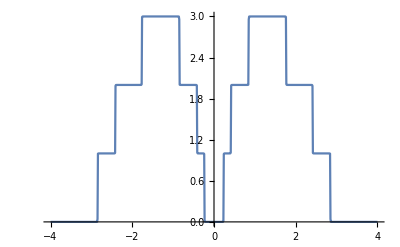

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028068},{0.01,0.0000253833},{0.02,0.0000164665},{0.03,1.1931×10^-6},{0.04,0.0000207725},{0.05,0.0000499985},{0.06,0.0000873229},{0.07,0.000133912},{0.08,0.000191348},{0.09,0.000261754},{0.1,0.00034798},{0.11,0.000453883},{0.12,0.000584744},{0.13,0.00074793},{0.14,0.000953945},{0.15,0.00121821},{0.16,0.00156416},{0.17,0.00202905},{0.18,0.00267559},{0.19,0.00361753},{0.2,0.00508411},{0.21,0.00761525},{0.22,0.0128634},{0.23,0.0295734},{0.24,0.525538},{0.25,0.794299},{0.26,0.873748},{0.27,0.910391},{0.28,0.930889},{0.29,0.943575},{0.3,0.951841},{0.31,0.957302},{0.32,0.960797},{0.33,0.962771},{0.34,0.963433},{0.35,0.962807},{0.36,0.960712},{0.37,0.956639},{0.38,0.949393},{0.39,0.935924},{0.4,0.906231},{0.41,0.797292},{0.42,1.14077},{0.43,1.58208},{0.44,1.7466},{0.45,1.82694},{0.46,1.87169},{0.47,1.89855},{0.48,1.91547},{0.49,1.92649},{0.5,1.93387},{0.51,1.93896},{0.52,1.94259},{0.53,1.9453},{0.54,1.94745},{0.55,1.94925},{0.56,1.95087},{0.57,1.95239},{0.58,1.95387},{0.59,1.95535},{0.6,1.95682},{0.61,1.9583},{0.62,1.95975},{0.63,1.96116},{0.64,1.9625},{0.65,1.96374},{0.66,1.96485},{0.67,1.9658},{0.68,1.96657},{0.69,1.96714},{0.7,1.96747},{0.71,1.96755},{0.72,1.96738},{0.73,1.96695},{0.74,1.96626},{0.75,1.96531},{0.76,1.96411},{0.77,1.96266},{0.78,1.96098},{0.79,1.95905},{0.8,1.95684},{0.81,1.95425},{0.82,1.95096},{0.83,1.94587},{0.84,1.93344},{0.85,2.00585},{0.86,2.47006},{0.87,2.70652},{0.88,2.805},{0.89,2.83437},{0.9,2.83369},{0.91,2.82245},{0.92,2.80982},{0.93,2.79995},{0.94,2.79463},{0.95,2.79456},{0.96,2.79994},{0.97,2.8107},{0.98,2.82662},{0.99,2.84719},{1.,2.87123},{1.01,2.89591},{1.02,2.91377},{1.03,2.90374},{1.04,2.8054},{1.05,2.48833},{1.06,2.03353},{1.07,2.00293},{1.08,2.2257},{1.09,2.39484},{1.1,2.44799},{1.11,2.34624},{1.12,2.0657},{1.13,1.81536},{1.14,1.89144},{1.15,2.14014},{1.16,2.36606},{1.17,2.53105},{1.18,2.64628},{1.19,2.72581},{1.2,2.77959},{1.21,2.81429},{1.22,2.83448},{1.23,2.84354},{1.24,2.84405},{1.25,2.83813},{1.26,2.82752},{1.27,2.81366},{1.28,2.79775},{1.29,2.78079},{1.3,2.76357},{1.31,2.74677},{1.32,2.73088},{1.33,2.71632},{1.34,2.7034},{1.35,2.69236},{1.36,2.68336},{1.37,2.67653},{1.38,2.67194},{1.39,2.66961},{1.4,2.66951},{1.41,2.67158},{1.42,2.6757},{1.43,2.68168},{1.44,2.68929},{1.45,2.69824},{1.46,2.70817},{1.47,2.71866},{1.48,2.72926},{1.49,2.73948},{1.5,2.74884},{1.51,2.75688},{1.52,2.76319},{1.53,2.76745},{1.54,2.76945},{1.55,2.76907},{1.56,2.76633},{1.57,2.76132},{1.58,2.7542},{1.59,2.74516},{1.6,2.73436},{1.61,2.72191},{1.62,2.70779},{1.63,2.69187},{1.64,2.67392},{1.65,2.6536},{1.66,2.63062},{1.67,2.60482},{1.68,2.57634},{1.69,2.54569},{1.7,2.51367},{1.71,2.48105},{1.72,2.44781},{1.73,2.41148},{1.74,2.36249},{1.75,2.2643},{1.76,1.90359},{1.77,1.63919},{1.78,1.27303},{1.79,1.23479},{1.8,1.57033},{1.81,1.66173},{1.82,1.69802},{1.83,1.7161},{1.84,1.72685},{1.85,1.73451},{1.86,1.74109},{1.87,1.74767},{1.88,1.75487},{1.89,1.76306},{1.9,1.77247},{1.91,1.78323},{1.92,1.79539},{1.93,1.80891},{1.94,1.82369},{1.95,1.83958},{1.96,1.8563},{1.97,1.87352},{1.98,1.8908},{1.99,1.90763},{2.,1.92339},{2.01,1.93744},{2.02,1.9491},{2.03,1.9577},{2.04,1.96267},{2.05,1.96356},{2.06,1.96012},{2.07,1.95231},{2.08,1.94033},{2.09,1.9246},{2.1,1.90573},{2.11,1.88447},{2.12,1.86162},{2.13,1.83803},{2.14,1.81449},{2.15,1.79173},{2.16,1.77038},{2.17,1.751},{2.18,1.73404},{2.19,1.71986},{2.2,1.70878},{2.21,1.70101},{2.22,1.69671},{2.23,1.69593},{2.24,1.69859},{2.25,1.70441},{2.26,1.71278},{2.27,1.72267},{2.28,1.73247},{2.29,1.73994},{2.3,1.7423},{2.31,1.73658},{2.32,1.72028},{2.33,1.692},{2.34,1.65194},{2.35,1.60159},{2.36,1.5428},{2.37,1.47617},{2.38,1.3982},{2.39,1.29397},{2.4,1.10312},{2.41,0.343392},{2.42,0.501917},{2.43,0.567768},{2.44,0.184289},{2.45,0.740848},{2.46,0.879892},{2.47,0.917565},{2.48,0.925621},{2.49,0.921024},{2.5,0.909926},{2.51,0.895313},{2.52,0.878985},{2.53,0.862206},{2.54,0.84595},{2.55,0.831012},{2.56,0.818056},{2.57,0.807654},{2.58,0.800305},{2.59,0.796455},{2.6,0.796499},{2.61,0.800792},{2.62,0.809626},{2.63,0.823198},{2.64,0.841536},{2.65,0.864377},{2.66,0.890973},{2.67,0.919828},{2.68,0.948383},{2.69,0.972762},{2.7,0.987808},{2.71,0.987729},{2.72,0.967547},{2.73,0.925035},{2.74,0.862131},{2.75,0.78474},{2.76,0.700854},{2.77,0.618122},{2.78,0.542201},{2.79,0.476318},{2.8,0.421704},{2.81,0.378238},{2.82,0.3447},{2.83,0.316885},{2.84,0.266297},{2.85,2.69782},{2.86,0.0173339},{2.87,0.434253},{2.88,0.0420219},{2.89,0.0164403},{2.9,0.008676},{2.91,0.0052562},{2.92,0.00345509},{2.93,0.00239877},{2.94,0.00173253},{2.95,0.00128955},{2.96,0.000982902},{2.97,0.000763776},{2.98,0.000603093},{2.99,0.000482713},{3.,0.000390881},{3.01,0.000319733},{3.02,0.000263864},{3.03,0.000219474},{3.04,0.000183836},{3.05,0.000154957},{3.06,0.000131359},{3.07,0.000111932},{3.08,0.0000958288},{3.09,0.0000823974},{3.1,0.0000711303},{3.11,0.0000616292},{3.12,0.0000535783},{3.13,0.0000467255},{3.14,0.0000408682},{3.15,0.0000358423},{3.16,0.000031514},{3.17,0.0000277739},{3.18,0.0000245316},{3.19,0.0000217124},{3.2,0.0000192543},{3.21,0.0000171052},{3.22,0.0000152216},{3.23,0.0000135667},{3.24,0.0000121095},{3.25,0.0000108236},{3.26,9.68651×10^-6},{3.27,8.67914×10^-6},{3.28,7.78503×10^-6},{3.29,6.99006×10^-6},{3.3,6.28205×10^-6},{3.31,5.6505×10^-6},{3.32,5.08629×10^-6},{3.33,4.58152×10^-6},{3.34,4.12931×10^-6},{3.35,3.72366×10^-6},{3.36,3.35931×10^-6},{3.37,3.03167×10^-6},{3.38,2.73671×10^-6},{3.39,2.47088×10^-6},{3.4,2.23106×10^-6},{3.41,2.01449×10^-6},{3.42,1.81874×10^-6},{3.43,1.64165×10^-6},{3.44,1.4813×10^-6},{3.45,1.33599×10^-6},{3.46,1.20423×10^-6},{3.47,1.08465×10^-6},{3.48,9.76067×10^-7},{3.49,8.77401×10^-7},{3.5,7.87697×10^-7},{3.51,7.06097×10^-7},{3.52,6.31831×10^-7},{3.53,5.64209×10^-7},{3.54,5.02613×10^-7},{3.55,4.46483×10^-7},{3.56,3.95319×10^-7},{3.57,3.48667×10^-7},{3.58,3.0612×10^-7},{3.59,2.6731×10^-7},{3.6,2.31902×10^-7},{3.61,1.99595×10^-7},{3.62,1.70117×10^-7},{3.63,1.43221×10^-7},{3.64,1.18681×10^-7},{3.65,9.62941×10^-8},{3.66,7.58756×10^-8},{3.67,5.72571×10^-8},{3.68,4.02853×10^-8},{3.69,2.4821×10^-8},{3.7,1.07372×10^-8},{3.71,2.08188×10^-9},{3.72,1.37419×10^-8},{3.73,2.43394×10^-8},{3.74,3.39624×10^-8},{3.75,4.26913×10^-8},{3.76,5.06×10^-8},{3.77,5.77557×10^-8},{3.78,6.42203×10^-8},{3.79,7.00501×10^-8},{3.8,7.52971×10^-8},{3.81,8.00088×10^-8},{3.82,8.42287×10^-8},{3.83,8.79969×10^-8},{3.84,9.13501×10^-8},{3.85,9.43221×10^-8},{3.86,9.69438×10^-8},{3.87,9.92438×10^-8},{3.88,1.01248×10^-7},{3.89,1.02982×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06767×10^-7},{3.93,1.0762×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

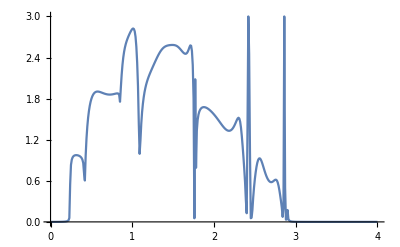

```mathematica
ListPlot[%99,Joined->True]
```

```mathematica
ListPlot[%97,Joined->True]
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null,Joined→True]

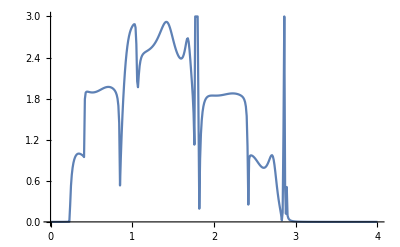

```mathematica
ListPlot[m1,Joined->True]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000273174},{0.01,0.0000230019},{0.02,9.96434×10^-7},{0.03,0.0000446168},{0.04,0.000108527},{0.05,0.000194156},{0.06,0.000303785},{0.07,0.000440694},{0.08,0.000609394},{0.09,0.000815977},{0.1,0.00106861},{0.11,0.00137831},{0.12,0.00176003},{0.13,0.0022344},{0.14,0.00283045},{0.15,0.00359002},{0.16,0.00457535},{0.17,0.00588277},{0.18,0.00766893},{0.19,0.0102063},{0.2,0.0140144},{0.21,0.0202314},{0.22,0.0320055},{0.23,0.0640348},{0.24,0.084395},{0.25,0.35967},{0.26,0.522674},{0.27,0.630198},{0.28,0.706507},{0.29,0.763256},{0.3,0.806649},{0.31,0.840231},{0.32,0.866115},{0.33,0.885563},{0.34,0.899249},{0.35,0.907343},{0.36,0.9094},{0.37,0.903936},{0.38,0.88715},{0.39,0.848661},{0.4,0.751875},{0.41,0.338545},{0.42,0.14259},{0.43,0.641986},{0.44,0.993735},{0.45,1.20071},{0.46,1.34018},{0.47,1.44192},{0.48,1.52},{0.49,1.58202},{0.5,1.6325},{0.51,1.67426},{0.52,1.70923},{0.53,1.73874},{0.54,1.76376},{0.55,1.785},{0.56,1.80304},{0.57,1.8183},{0.58,1.83116},{0.59,1.8419},{0.6,1.85079},{0.61,1.85803},{0.62,1.86381},{0.63,1.86831},{0.64,1.87166},{0.65,1.874},{0.66,1.87545},{0.67,1.87612},{0.68,1.87612},{0.69,1.87552},{0.7,1.87441},{0.71,1.87286},{0.72,1.87094},{0.73,1.86869},{0.74,1.86616},{0.75,1.86337},{0.76,1.86031},{0.77,1.85697},{0.78,1.85325},{0.79,1.84897},{0.8,1.84376},{0.81,1.83681},{0.82,1.82604},{0.83,1.80484},{0.84,1.73579},{0.85,2.11427},{0.86,2.72509},{0.87,2.79624},{0.88,2.82004},{0.89,2.83103},{0.9,2.83743},{0.91,2.84221},{0.92,2.84667},{0.93,2.85148},{0.94,2.85698},{0.95,2.86333},{0.96,2.87056},{0.97,2.87848},{0.98,2.88667},{0.99,2.8942},{1.,2.89916},{1.01,2.89739},{1.02,2.87951},{1.03,2.82308},{1.04,2.67539},{1.05,2.35456},{1.06,1.98161},{1.07,1.98459},{1.08,2.21473},{1.09,2.40419},{1.1,2.50943},{1.11,2.51672},{1.12,2.35215},{1.13,2.03577},{1.14,2.06002},{1.15,2.26759},{1.16,2.4092},{1.17,2.48997},{1.18,2.53569},{1.19,2.5611},{1.2,2.57412},{1.21,2.57928},{1.22,2.57947},{1.23,2.5766},{1.24,2.57206},{1.25,2.56691},{1.26,2.56195},{1.27,2.55782},{1.28,2.55506},{1.29,2.5541},{1.3,2.55534},{1.31,2.55912},{1.32,2.56578},{1.33,2.57563},{1.34,2.58899},{1.35,2.60617},{1.36,2.62744},{1.37,2.65301},{1.38,2.68295},{1.39,2.71711},{1.4,2.75496},{1.41,2.79536},{1.42,2.83643},{1.43,2.87529},{1.44,2.90813},{1.45,2.93049},{1.46,2.93807},{1.47,2.9278},{1.48,2.8989},{1.49,2.85331},{1.5,2.79525},{1.51,2.73004},{1.52,2.66292},{1.53,2.59812},{1.54,2.53859},{1.55,2.48608},{1.56,2.44144},{1.57,2.40501},{1.58,2.37692},{1.59,2.35733},{1.6,2.34667},{1.61,2.34584},{1.62,2.35647},{1.63,2.38106},{1.64,2.42291},{1.65,2.48479},{1.66,2.56387},{1.67,2.63988},{1.68,2.66586},{1.69,2.59938},{1.7,2.45997},{1.71,2.30518},{1.72,2.16681},{1.73,2.04335},{1.74,1.91496},{1.75,1.73975},{1.76,1.37447},{1.77,2.33998},{1.78,3},{1.79,0.154478},{1.8,0.882298},{1.81,0.625981},{1.82,0.10583},{1.83,1.2961},{1.84,1.64935},{1.85,1.76556},{1.86,1.82172},{1.87,1.85551},{1.88,1.87873},{1.89,1.89611},{1.9,1.90987},{1.91,1.92114},{1.92,1.93052},{1.93,1.93833},{1.94,1.94471},{1.95,1.94973},{1.96,1.95335},{1.97,1.95555},{1.98,1.95625},{1.99,1.95541},{2.,1.95301},{2.01,1.94904},{2.02,1.94357},{2.03,1.93668},{2.04,1.92854},{2.05,1.91934},{2.06,1.90933},{2.07,1.89882},{2.08,1.88812},{2.09,1.87758},{2.1,1.86757},{2.11,1.85847},{2.12,1.85063},{2.13,1.84441},{2.14,1.84017},{2.15,1.83822},{2.16,1.83886},{2.17,1.84235},{2.18,1.8489},{2.19,1.85861},{2.2,1.87146},{2.21,1.88724},{2.22,1.90541},{2.23,1.925},{2.24,1.94444},{2.25,1.96144},{2.26,1.97297},{2.27,1.97545},{2.28,1.96531},{2.29,1.93985},{2.3,1.89824},{2.31,1.84216},{2.32,1.77558},{2.33,1.7038},{2.34,1.63212},{2.35,1.56481},{2.36,1.5046},{2.37,1.45257},{2.38,1.40793},{2.39,1.36585},{2.4,1.30238},{2.41,0.925498},{2.42,0.426862},{2.43,0.755329},{2.44,0.951121},{2.45,0.965339},{2.46,0.973528},{2.47,0.978092},{2.48,0.98067},{2.49,0.98211},{2.5,0.982881},{2.51,0.983262},{2.52,0.983438},{2.53,0.983535},{2.54,0.983648},{2.55,0.983848},{2.56,0.98419},{2.57,0.984712},{2.58,0.985439},{2.59,0.986377},{2.6,0.987518},{2.61,0.988836},{2.62,0.990282},{2.63,0.991786},{2.64,0.993257},{2.65,0.994579},{2.66,0.995615},{2.67,0.996212},{2.68,0.996208},{2.69,0.995437},{2.7,0.993752},{2.71,0.991036},{2.72,0.987231},{2.73,0.982358},{2.74,0.976551},{2.75,0.97008},{2.76,0.96338},{2.77,0.957075},{2.78,0.951989},{2.79,0.949144},{2.8,0.949697},{2.81,0.954646},{2.82,0.963617},{2.83,0.968931},{2.84,0.91216},{2.85,0.409992},{2.86,0.00773974},{2.87,0.00312147},{2.88,0.00168382},{2.89,0.00104139},{2.9,0.000697545},{2.91,0.000492526},{2.92,0.000361119},{2.93,0.000272402},{2.94,0.000210105},{2.95,0.000164991},{2.96,0.000131498},{2.97,0.000106116},{2.98,0.000086547},{2.99,0.000071235},{3.,0.0000591008},{3.01,0.0000493774},{3.02,0.0000415091},{3.03,0.0000350865},{3.04,0.000029803},{3.05,0.0000254259},{3.06,0.0000217769},{3.07,0.0000187171},{3.08,0.0000161381},{3.09,0.0000139536},{3.1,0.0000120953},{3.11,0.000010508},{3.12,9.14698×10^-6},{3.13,7.976×10^-6},{3.14,6.96526×10^-6},{3.15,6.09023×10^-6},{3.16,5.33057×10^-6},{3.17,4.66937×10^-6},{3.18,4.09249×10^-6},{3.19,3.58805×10^-6},{3.2,3.14603×10^-6},{3.21,2.75796×10^-6},{3.22,2.41665×10^-6},{3.23,2.11596×10^-6},{3.24,1.85065×10^-6},{3.25,1.61623×10^-6},{3.26,1.40884×10^-6},{3.27,1.22513×10^-6},{3.28,1.06222×10^-6},{3.29,9.17631×10^-7},{3.3,7.8918×10^-7},{3.31,6.74981×10^-7},{3.32,5.73386×10^-7},{3.33,4.82956×10^-7},{3.34,4.02427×10^-7},{3.35,3.30693×10^-7},{3.36,2.66779×10^-7},{3.37,2.09827×10^-7},{3.38,1.59082×10^-7},{3.39,1.13874×10^-7},{3.4,7.36114×10^-8},{3.41,3.77702×10^-8},{3.42,5.88512×10^-9},{3.43,2.24575×10^-8},{3.44,4.76254×10^-8},{3.45,6.99463×10^-8},{3.46,8.97126×10^-8},{3.47,1.07185×10^-7},{3.48,1.22597×10^-7},{3.49,1.36158×10^-7},{3.5,1.48054×10^-7},{3.51,1.58452×10^-7},{3.52,1.67504×10^-7},{3.53,1.75344×10^-7},{3.54,1.82093×10^-7},{3.55,1.87861×10^-7},{3.56,1.92746×10^-7},{3.57,1.96836×10^-7},{3.58,2.00212×10^-7},{3.59,2.02945×10^-7},{3.6,2.051×10^-7},{3.61,2.06736×10^-7},{3.62,2.07905×10^-7},{3.63,2.08656×10^-7},{3.64,2.09032×10^-7},{3.65,2.09072×10^-7},{3.66,2.08811×10^-7},{3.67,2.08282×10^-7},{3.68,2.07513×10^-7},{3.69,2.06531×10^-7},{3.7,2.0536×10^-7},{3.71,2.0402×10^-7},{3.72,2.02533×10^-7},{3.73,2.00915×10^-7},{3.74,1.99183×10^-7},{3.75,1.9735×10^-7},{3.76,1.95431×10^-7},{3.77,1.93436×10^-7},{3.78,1.91378×10^-7},{3.79,1.89265×10^-7},{3.8,1.87107×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000265174},{0.01,0.0000240985},{0.02,7.98253×10^-7},{0.03,0.0000432833},{0.04,0.000108848},{0.05,0.000197438},{0.06,0.000311535},{0.07,0.000454732},{0.08,0.000632003},{0.09,0.000850099},{0.1,0.00111815},{0.11,0.00144852},{0.12,0.00185818},{0.13,0.00237075},{0.14,0.00301981},{0.15,0.00385438},{0.16,0.00494838},{0.17,0.00641806},{0.18,0.00845611},{0.19,0.0114053},{0.2,0.0159377},{0.21,0.0235802},{0.22,0.0387837},{0.23,0.0844722},{0.24,0.151536},{0.25,0.478024},{0.26,0.623774},{0.27,0.705988},{0.28,0.758969},{0.29,0.796001},{0.3,0.823211},{0.31,0.843741},{0.32,0.85929},{0.33,0.870765},{0.34,0.87856},{0.35,0.882659},{0.36,0.88258},{0.37,0.877122},{0.38,0.863598},{0.39,0.835388},{0.4,0.771488},{0.41,0.545363},{0.42,0.897418},{0.43,1.53415},{0.44,1.77563},{0.45,1.88662},{0.46,1.93961},{0.47,1.96284},{0.48,1.96966},{0.49,1.96721},{0.5,1.95959},{0.51,1.94929},{0.52,1.9379},{0.53,1.92641},{0.54,1.91547},{0.55,1.90551},{0.56,1.89679},{0.57,1.88947},{0.58,1.88365},{0.59,1.87935},{0.6,1.87658},{0.61,1.87531},{0.62,1.8755},{0.63,1.87708},{0.64,1.87996},{0.65,1.88404},{0.66,1.88922},{0.67,1.89536},{0.68,1.90231},{0.69,1.90991},{0.7,1.91797},{0.71,1.92629},{0.72,1.93466},{0.73,1.94284},{0.74,1.95062},{0.75,1.95774},{0.76,1.96397},{0.77,1.96907},{0.78,1.97283},{0.79,1.97499},{0.8,1.97525},{0.81,1.97313},{0.82,1.96748},{0.83,1.95457},{0.84,1.91417},{0.85,1.93119},{0.86,2.57856},{0.87,2.74186},{0.88,2.79777},{0.89,2.81662},{0.9,2.82034},{0.91,2.81786},{0.92,2.81351},{0.93,2.80964},{0.94,2.80762},{0.95,2.80837},{0.96,2.81253},{0.97,2.82061},{0.98,2.83299},{0.99,2.84985},{1.,2.87087},{1.01,2.89422},{1.02,2.91352},{1.03,2.90816},{1.04,2.81471},{1.05,2.49842},{1.06,2.05219},{1.07,1.97709},{1.08,2.13486},{1.09,2.26913},{1.1,2.308},{1.11,2.20521},{1.12,1.95655},{1.13,1.78821},{1.14,1.90538},{1.15,2.14341},{1.16,2.35839},{1.17,2.5241},{1.18,2.64763},{1.19,2.73792},{1.2,2.80124},{1.21,2.84188},{1.22,2.86323},{1.23,2.86845},{1.24,2.86069},{1.25,2.84306},{1.26,2.81854},{1.27,2.78982},{1.28,2.75915},{1.29,2.7284},{1.3,2.69895},{1.31,2.67186},{1.32,2.64787},{1.33,2.62746},{1.34,2.611},{1.35,2.5987},{1.36,2.59073},{1.37,2.58722},{1.38,2.58827},{1.39,2.59395},{1.4,2.60431},{1.41,2.61932},{1.42,2.63884},{1.43,2.6625},{1.44,2.68966},{1.45,2.7192},{1.46,2.74951},{1.47,2.77838},{1.48,2.80311},{1.49,2.82082},{1.5,2.82892},{1.51,2.82568},{1.52,2.8107},{1.53,2.78506},{1.54,2.75102},{1.55,2.71154},{1.56,2.66967},{1.57,2.62813},{1.58,2.58909},{1.59,2.55414},{1.6,2.5244},{1.61,2.50064},{1.62,2.48337},{1.63,2.47286},{1.64,2.46889},{1.65,2.47015},{1.66,2.47315},{1.67,2.47109},{1.68,2.45471},{1.69,2.41725},{1.7,2.36048},{1.71,2.29354},{1.72,2.22493},{1.73,2.15664},{1.74,2.08223},{1.75,1.98036},{1.76,1.7628},{1.77,0.0855597},{1.78,0.329134},{1.79,0.282599},{1.8,0.82566},{1.81,1.27873},{1.82,1.47237},{1.83,1.57303},{1.84,1.63347},{1.85,1.67399},{1.86,1.70373},{1.87,1.72733},{1.88,1.74732},{1.89,1.76517},{1.9,1.78178},{1.91,1.79766},{1.92,1.81312},{1.93,1.82828},{1.94,1.84315},{1.95,1.85764},{1.96,1.87157},{1.97,1.88471},{1.98,1.89677},{1.99,1.90743},{2.,1.91635},{2.01,1.92322},{2.02,1.92775},{2.03,1.92972},{2.04,1.92902},{2.05,1.92561},{2.06,1.9196},{2.07,1.91121},{2.08,1.90075},{2.09,1.88866},{2.1,1.87543},{2.11,1.86157},{2.12,1.84765},{2.13,1.83421},{2.14,1.82177},{2.15,1.81082},{2.16,1.80179},{2.17,1.79506},{2.18,1.79096},{2.19,1.78973},{2.2,1.79152},{2.21,1.79632},{2.22,1.80397},{2.23,1.81399},{2.24,1.82556},{2.25,1.8373},{2.26,1.84728},{2.27,1.85294},{2.28,1.85134},{2.29,1.83966},{2.3,1.81589},{2.31,1.77971},{2.32,1.73281},{2.33,1.67871},{2.34,1.6219},{2.35,1.56689},{2.36,1.51748},{2.37,1.47668},{2.38,1.44707},{2.39,1.43169},{2.4,1.43512},{2.41,1.43645},{2.42,0.883972},{2.43,0.0306559},{2.44,0.554905},{2.45,0.849149},{2.46,0.900611},{2.47,0.917822},{2.48,0.92496},{2.49,0.928094},{2.5,0.929415},{2.51,0.92991},{2.52,0.9301},{2.53,0.930291},{2.54,0.930676},{2.55,0.931378},{2.56,0.93247},{2.57,0.933986},{2.58,0.935922},{2.59,0.938233},{2.6,0.940833},{2.61,0.943591},{2.62,0.946329},{2.63,0.948814},{2.64,0.950766},{2.65,0.951852},{2.66,0.951704},{2.67,0.949929},{2.68,0.946133},{2.69,0.939959},{2.7,0.931119},{2.71,0.919445},{2.72,0.904923},{2.73,0.88773},{2.74,0.86825},{2.75,0.847065},{2.76,0.824928},{2.77,0.802705},{2.78,0.78128},{2.79,0.761399},{2.8,0.74333},{2.81,0.725977},{2.82,0.704073},{2.83,0.657371},{2.84,0.49554},{2.85,0.000847285},{2.86,0.015889},{2.87,0.00318509},{2.88,0.00174552},{2.89,0.00105922},{2.9,0.000703581},{2.91,0.000494852},{2.92,0.000362106},{2.93,0.000272853},{2.94,0.000210324},{2.95,0.000165102},{2.96,0.000131557},{2.97,0.000106149},{2.98,0.0000865651},{2.99,0.0000712454},{3.,0.0000591069},{3.01,0.000049381},{3.02,0.0000415114},{3.03,0.0000350879},{3.04,0.0000298038},{3.05,0.0000254265},{3.06,0.0000217772},{3.07,0.0000187174},{3.08,0.0000161382},{3.09,0.0000139537},{3.1,0.0000120954},{3.11,0.000010508},{3.12,9.147×10^-6},{3.13,7.97602×10^-6},{3.14,6.96527×10^-6},{3.15,6.09024×10^-6},{3.16,5.33058×10^-6},{3.17,4.66938×10^-6},{3.18,4.09249×10^-6},{3.19,3.58805×10^-6},{3.2,3.14603×10^-6},{3.21,2.75796×10^-6},{3.22,2.41665×10^-6},{3.23,2.11596×10^-6},{3.24,1.85065×10^-6},{3.25,1.61623×10^-6},{3.26,1.40884×10^-6},{3.27,1.22513×10^-6},{3.28,1.06222×10^-6},{3.29,9.17631×10^-7},{3.3,7.89179×10^-7},{3.31,6.7498×10^-7},{3.32,5.73386×10^-7},{3.33,4.82955×10^-7},{3.34,4.02427×10^-7},{3.35,3.30693×10^-7},{3.36,2.66779×10^-7},{3.37,2.09827×10^-7},{3.38,1.59082×10^-7},{3.39,1.13874×10^-7},{3.4,7.36113×10^-8},{3.41,3.77702×10^-8},{3.42,5.88508×10^-9},{3.43,2.24575×10^-8},{3.44,4.76254×10^-8},{3.45,6.99464×10^-8},{3.46,8.97127×10^-8},{3.47,1.07185×10^-7},{3.48,1.22597×10^-7},{3.49,1.36158×10^-7},{3.5,1.48054×10^-7},{3.51,1.58452×10^-7},{3.52,1.67504×10^-7},{3.53,1.75344×10^-7},{3.54,1.82093×10^-7},{3.55,1.87861×10^-7},{3.56,1.92746×10^-7},{3.57,1.96836×10^-7},{3.58,2.00212×10^-7},{3.59,2.02945×10^-7},{3.6,2.051×10^-7},{3.61,2.06736×10^-7},{3.62,2.07905×10^-7},{3.63,2.08656×10^-7},{3.64,2.09032×10^-7},{3.65,2.09072×10^-7},{3.66,2.08811×10^-7},{3.67,2.08282×10^-7},{3.68,2.07513×10^-7},{3.69,2.06531×10^-7},{3.7,2.0536×10^-7},{3.71,2.0402×10^-7},{3.72,2.02533×10^-7},{3.73,2.00915×10^-7},{3.74,1.99183×10^-7},{3.75,1.9735×10^-7},{3.76,1.95431×10^-7},{3.77,1.93436×10^-7},{3.78,1.91378×10^-7},{3.79,1.89265×10^-7},{3.8,1.87107×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000283419},{0.01,0.0000214199},{0.02,1.39074×10^-6},{0.03,0.0000317754},{0.04,0.0000784616},{0.05,0.000139422},{0.06,0.000215823},{0.07,0.000309306},{0.08,0.000422089},{0.09,0.000557105},{0.1,0.000718212},{0.11,0.000910485},{0.12,0.00114066},{0.13,0.00141778},{0.14,0.00175423},{0.15,0.00216732},{0.16,0.00268203},{0.17,0.00333571},{0.18,0.00418697},{0.19,0.00533375},{0.2,0.00695456},{0.21,0.009419},{0.22,0.0136701},{0.23,0.0233429},{0.24,0.117885},{0.25,0.382183},{0.26,0.588124},{0.27,0.733721},{0.28,0.829152},{0.29,0.887896},{0.3,0.921907},{0.31,0.940151},{0.32,0.948778},{0.33,0.951766},{0.34,0.951548},{0.35,0.949472},{0.36,0.946069},{0.37,0.941114},{0.38,0.933345},{0.39,0.919174},{0.4,0.886579},{0.41,0.754421},{0.42,1.26004},{0.43,1.62943},{0.44,1.7451},{0.45,1.80328},{0.46,1.83914},{0.47,1.86369},{0.48,1.88144},{0.49,1.89454},{0.5,1.90421},{0.51,1.91116},{0.52,1.91591},{0.53,1.91887},{0.54,1.92037},{0.55,1.92073},{0.56,1.92023},{0.57,1.91913},{0.58,1.91769},{0.59,1.91612},{0.6,1.91461},{0.61,1.91334},{0.62,1.91243},{0.63,1.91197},{0.64,1.91203},{0.65,1.91262},{0.66,1.91374},{0.67,1.91533},{0.68,1.91731},{0.69,1.91957},{0.7,1.92197},{0.71,1.92435},{0.72,1.92651},{0.73,1.92828},{0.74,1.92945},{0.75,1.92982},{0.76,1.92921},{0.77,1.92742},{0.78,1.92425},{0.79,1.91945},{0.8,1.9126},{0.81,1.90292},{0.82,1.88848},{0.83,1.86363},{0.84,1.80334},{0.85,1.63005},{0.86,1.95181},{0.87,2.15103},{0.88,2.27622},{0.89,2.35093},{0.9,2.39048},{0.91,2.40642},{0.92,2.40746},{0.93,2.39993},{0.94,2.38827},{0.95,2.37541},{0.96,2.36322},{0.97,2.35283},{0.98,2.34488},{0.99,2.3397},{1.,2.33742},{1.01,2.33808},{1.02,2.3416},{1.03,2.34788},{1.04,2.3568},{1.05,2.36817},{1.06,2.38182},{1.07,2.39748},{1.08,2.41488},{1.09,2.43366},{1.1,2.45342},{1.11,2.47367},{1.12,2.49387},{1.13,2.51345},{1.14,2.53178},{1.15,2.54827},{1.16,2.56235},{1.17,2.57354},{1.18,2.58151},{1.19,2.58605},{1.2,2.58714},{1.21,2.58489},{1.22,2.57958},{1.23,2.57161},{1.24,2.56144},{1.25,2.54961},{1.26,2.53663},{1.27,2.52304},{1.28,2.50931},{1.29,2.49589},{1.3,2.48318},{1.31,2.47151},{1.32,2.46118},{1.33,2.45243},{1.34,2.44546},{1.35,2.44042},{1.36,2.43742},{1.37,2.43652},{1.38,2.43772},{1.39,2.44097},{1.4,2.44616},{1.41,2.45312},{1.42,2.46167},{1.43,2.47156},{1.44,2.48253},{1.45,2.49434},{1.46,2.50672},{1.47,2.51945},{1.48,2.5323},{1.49,2.54503},{1.5,2.55738},{1.51,2.56902},{1.52,2.57951},{1.53,2.58827},{1.54,2.59451},{1.55,2.59728},{1.56,2.59547},{1.57,2.58796},{1.58,2.5738},{1.59,2.55253},{1.6,2.52441},{1.61,2.49058},{1.62,2.45306},{1.63,2.41455},{1.64,2.37815},{1.65,2.34706},{1.66,2.32446},{1.67,2.31339},{1.68,2.31625},{1.69,2.33332},{1.7,2.35925},{1.71,2.37746},{1.72,2.35649},{1.73,2.25442},{1.74,2.01948},{1.75,1.52146},{1.76,0.138551},{1.77,3},{1.78,0.514727},{1.79,0.534346},{1.8,0.0255621},{1.81,1.63013},{1.82,1.65824},{1.83,1.6987},{1.84,1.73306},{1.85,1.75997},{1.86,1.78064},{1.87,1.79635},{1.88,1.80812},{1.89,1.81677},{1.9,1.82288},{1.91,1.82695},{1.92,1.82937},{1.93,1.83046},{1.94,1.8305},{1.95,1.82972},{1.96,1.82833},{1.97,1.82652},{1.98,1.82443},{1.99,1.82222},{2.,1.81999},{2.01,1.81786},{2.02,1.81592},{2.03,1.81424},{2.04,1.81287},{2.05,1.81187},{2.06,1.81126},{2.07,1.81107},{2.08,1.8113},{2.09,1.81194},{2.1,1.81298},{2.11,1.81437},{2.12,1.81609},{2.13,1.81806},{2.14,1.82022},{2.15,1.82248},{2.16,1.82477},{2.17,1.82696},{2.18,1.82897},{2.19,1.83065},{2.2,1.8319},{2.21,1.83259},{2.22,1.83258},{2.23,1.83174},{2.24,1.82995},{2.25,1.82708},{2.26,1.82298},{2.27,1.81752},{2.28,1.81055},{2.29,1.80188},{2.3,1.79131},{2.31,1.77853},{2.32,1.76316},{2.33,1.74462},{2.34,1.72206},{2.35,1.69416},{2.36,1.65882},{2.37,1.61244},{2.38,1.54842},{2.39,1.45329},{2.4,1.29385},{2.41,0.951066},{2.42,1.01206},{2.43,3},{2.44,2.00466},{2.45,0.105273},{2.46,0.384223},{2.47,0.589142},{2.48,0.698299},{2.49,0.765232},{2.5,0.80997},{2.51,0.841385},{2.52,0.863888},{2.53,0.879873},{2.54,0.890767},{2.55,0.897523},{2.56,0.900875},{2.57,0.901477},{2.58,0.899976},{2.59,0.897039},{2.6,0.893368},{2.61,0.889686},{2.62,0.886721},{2.63,0.885181},{2.64,0.885715},{2.65,0.888866},{2.66,0.895001},{2.67,0.904197},{2.68,0.916083},{2.69,0.929613},{2.7,0.942784},{2.71,0.952386},{2.72,0.953954},{2.73,0.942206},{2.74,0.912217},{2.75,0.861154},{2.76,0.789749},{2.77,0.702394},{2.78,0.605461},{2.79,0.504696},{2.8,0.402777},{2.81,0.29699},{2.82,0.174117},{2.83,0.0123059},{2.84,0.53497},{2.85,3},{2.86,0.438336},{2.87,0.141894},{2.88,0.0588008},{2.89,0.112454},{2.9,0.0400328},{2.91,0.0258798},{2.92,0.0184365},{2.93,0.0137933},{2.94,0.010661},{2.95,0.00844146},{2.96,0.00681205},{2.97,0.00558273},{2.98,0.00463461},{2.99,0.00388994},{3.,0.00329598},{3.01,0.00281592},{3.02,0.00242342},{3.03,0.00209924},{3.04,0.00182908},{3.05,0.00160212},{3.06,0.00141006},{3.07,0.00124647},{3.08,0.00110629},{3.09,0.000985522},{3.1,0.000880945},{3.11,0.000789971},{3.12,0.000710491},{3.13,0.000640775},{3.14,0.000579396},{3.15,0.00052517},{3.16,0.000477107},{3.17,0.000434377},{3.18,0.000396279},{3.19,0.000362219},{3.2,0.000331691},{3.21,0.000304263},{3.22,0.000279563},{3.23,0.000257272},{3.24,0.000237113},{3.25,0.000218846},{3.26,0.000202263},{3.27,0.000187181},{3.28,0.00017344},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120513},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980556},{3.37,0.0000917087},{3.38,0.0000858464},{3.39,0.0000804257},{3.4,0.000075408},{3.41,0.0000707586},{3.42,0.000066446},{3.43,0.000062442},{3.44,0.000058721},{3.45,0.0000552598},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436215},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000278806},{0.01,0.0000252678},{0.02,0.0000187065},{0.03,8.25461×10^-6},{0.04,6.10014×10^-6},{0.05,0.0000244404},{0.06,0.0000469227},{0.07,0.0000737851},{0.08,0.000105358},{0.09,0.000142084},{0.1,0.000184538},{0.11,0.000233472},{0.12,0.00028986},{0.13,0.000354981},{0.14,0.000430534},{0.15,0.000518826},{0.16,0.000623063},{0.17,0.000747846},{0.18,0.00090005},{0.19,0.00109046},{0.2,0.00133694},{0.21,0.00167044},{0.22,0.00213494},{0.23,0.00218044},{0.24,0.304576},{0.25,0.625519},{0.26,0.788609},{0.27,0.880485},{0.28,0.934512},{0.29,0.966154},{0.3,0.983634},{0.31,0.99179},{0.32,0.993685},{0.33,0.991376},{0.34,0.986286},{0.35,0.979416},{0.36,0.971434},{0.37,0.962685},{0.38,0.953021},{0.39,0.941033},{0.4,0.919807},{0.41,0.822584},{0.42,1.30562},{0.43,1.63844},{0.44,1.73295},{0.45,1.77714},{0.46,1.80318},{0.47,1.82104},{0.48,1.83481},{0.49,1.84643},{0.5,1.85689},{0.51,1.86673},{0.52,1.87622},{0.53,1.88547},{0.54,1.89451},{0.55,1.90328},{0.56,1.9117},{0.57,1.91963},{0.58,1.92695},{0.59,1.93352},{0.6,1.93921},{0.61,1.94392},{0.62,1.94754},{0.63,1.95003},{0.64,1.95135},{0.65,1.95151},{0.66,1.95056},{0.67,1.94856},{0.68,1.94562},{0.69,1.94184},{0.7,1.93734},{0.71,1.93225},{0.72,1.92667},{0.73,1.92067},{0.74,1.91431},{0.75,1.90755},{0.76,1.90029},{0.77,1.89229},{0.78,1.88312},{0.79,1.87196},{0.8,1.85741},{0.81,1.83673},{0.82,1.80403},{0.83,1.74376},{0.84,1.5937},{0.85,1.02197},{0.86,1.62115},{0.87,1.95715},{0.88,2.16535},{0.89,2.30994},{0.9,2.41877},{0.91,2.50554},{0.92,2.57762},{0.93,2.63914},{0.94,2.69243},{0.95,2.7388},{0.96,2.77887},{0.97,2.81283},{0.98,2.8406},{0.99,2.86187},{1.,2.8762},{1.01,2.88297},{1.02,2.88139},{1.03,2.8703},{1.04,2.84806},{1.05,2.8121},{1.06,2.75849},{1.07,2.68128},{1.08,2.57233},{1.09,2.42328},{1.1,2.23375},{1.11,2.02914},{1.12,1.87064},{1.13,1.81677},{1.14,1.86424},{1.15,1.96203},{1.16,2.06566},{1.17,2.15533},{1.18,2.22715},{1.19,2.28345},{1.2,2.32785},{1.21,2.36365},{1.22,2.3934},{1.23,2.41893},{1.24,2.44144},{1.25,2.46169},{1.26,2.48006},{1.27,2.49671},{1.28,2.5116},{1.29,2.52466},{1.3,2.53581},{1.31,2.54502},{1.32,2.5524},{1.33,2.55816},{1.34,2.56265},{1.35,2.56632},{1.36,2.56973},{1.37,2.57349},{1.38,2.57826},{1.39,2.58471},{1.4,2.59353},{1.41,2.60541},{1.42,2.62099},{1.43,2.64085},{1.44,2.66537},{1.45,2.69468},{1.46,2.72831},{1.47,2.76498},{1.48,2.80209},{1.49,2.83549},{1.5,2.85944},{1.51,2.86748},{1.52,2.85424},{1.53,2.81765},{1.54,2.76028},{1.55,2.68865},{1.56,2.61092},{1.57,2.53445},{1.58,2.46439},{1.59,2.40363},{1.6,2.35338},{1.61,2.31395},{1.62,2.28554},{1.63,2.26881},{1.64,2.26557},{1.65,2.27959},{1.66,2.31752},{1.67,2.38852},{1.68,2.49635},{1.69,2.60837},{1.7,2.62362},{1.71,2.47418},{1.72,2.23646},{1.73,1.99016},{1.74,1.73231},{1.75,1.39309},{1.76,0.726884},{1.77,3},{1.78,3},{1.79,3},{1.8,3},{1.81,1.07998},{1.82,0.397583},{1.83,0.966329},{1.84,1.25548},{1.85,1.4278},{1.86,1.5413},{1.87,1.62135},{1.88,1.68064},{1.89,1.72616},{1.9,1.76207},{1.91,1.79094},{1.92,1.81447},{1.93,1.83378},{1.94,1.84969},{1.95,1.86275},{1.96,1.87339},{1.97,1.88192},{1.98,1.88858},{1.99,1.89359},{2.,1.89709},{2.01,1.89925},{2.02,1.90017},{2.03,1.9},{2.04,1.89884},{2.05,1.8968},{2.06,1.894},{2.07,1.89053},{2.08,1.88652},{2.09,1.88206},{2.1,1.87725},{2.11,1.8722},{2.12,1.86698},{2.13,1.86169},{2.14,1.85641},{2.15,1.85119},{2.16,1.8461},{2.17,1.84118},{2.18,1.83647},{2.19,1.83197},{2.2,1.82771},{2.21,1.82366},{2.22,1.81981},{2.23,1.81611},{2.24,1.81252},{2.25,1.80896},{2.26,1.80535},{2.27,1.80159},{2.28,1.79755},{2.29,1.79308},{2.3,1.78799},{2.31,1.78201},{2.32,1.77479},{2.33,1.76577},{2.34,1.75411},{2.35,1.73842},{2.36,1.71636},{2.37,1.68376},{2.38,1.63278},{2.39,1.54724},{2.4,1.38804},{2.41,1.024},{2.42,0.453661},{2.43,0.125122},{2.44,0.900011},{2.45,0.946004},{2.46,0.942171},{2.47,0.928587},{2.48,0.911594},{2.49,0.893113},{2.5,0.874115},{2.51,0.855293},{2.52,0.837226},{2.53,0.82043},{2.54,0.805374},{2.55,0.792488},{2.56,0.782171},{2.57,0.7748},{2.58,0.770734},{2.59,0.77032},{2.6,0.773892},{2.61,0.781759},{2.62,0.794176},{2.63,0.811286},{2.64,0.833023},{2.65,0.858952},{2.66,0.888029},{2.67,0.918297},{2.68,0.946567},{2.69,0.968256},{2.7,0.977669},{2.71,0.969034},{2.72,0.938282},{2.73,0.884891},{2.74,0.812617},{2.75,0.728413},{2.76,0.640112},{2.77,0.554241},{2.78,0.474907},{2.79,0.403729},{2.8,0.340211},{2.81,0.281867},{2.82,0.223004},{2.83,0.14806},{2.84,0.0147688},{2.85,3},{2.86,0.0348229},{2.87,3},{2.88,0.448628},{2.89,0.155462},{2.9,0.0815415},{2.91,0.0506009},{2.92,0.0344605},{2.93,0.0249112},{2.94,0.0187763},{2.95,0.0145981},{2.96,0.0116254},{2.97,0.00943708},{2.98,0.00778176},{2.99,0.00650129},{3.,0.00549213},{3.01,0.00468408},{3.02,0.00402819},{3.03,0.00348948},{3.04,0.0030424},{3.05,0.00266793},{3.06,0.0023517},{3.07,0.00208269},{3.08,0.00185233},{3.09,0.00165387},{3.1,0.00148196},{3.11,0.0013323},{3.12,0.0012014},{3.13,0.00108643},{3.14,0.000985043},{3.15,0.000895315},{3.16,0.000815633},{3.17,0.000744646},{3.18,0.000681217},{3.19,0.000624384},{3.2,0.000573326},{3.21,0.000527344},{3.22,0.000485836},{3.23,0.000448284},{3.24,0.000414241},{3.25,0.000383316},{3.26,0.000355172},{3.27,0.000329512},{3.28,0.000306077},{3.29,0.00028464},{3.3,0.000264999},{3.31,0.000246978},{3.32,0.000230418},{3.33,0.000215181},{3.34,0.000201143},{3.35,0.000188193},{3.36,0.000176233},{3.37,0.000165173},{3.38,0.000154934},{3.39,0.000145446},{3.4,0.000136644},{3.41,0.00012847},{3.42,0.000120872},{3.43,0.000113803},{3.44,0.00010722},{3.45,0.000101084},{3.46,0.0000953604},{3.47,0.0000900163},{3.48,0.0000850229},{3.49,0.0000803535},{3.5,0.0000759838},{3.51,0.0000718916},{3.52,0.0000680564},{3.53,0.0000644598},{3.54,0.0000610845},{3.55,0.0000579148},{3.56,0.0000549364},{3.57,0.0000521359},{3.58,0.0000495012},{3.59,0.0000470209},{3.6,0.0000446846},{3.61,0.0000424828},{3.62,0.0000404065},{3.63,0.0000384477},{3.64,0.0000365985},{3.65,0.0000348521},{3.66,0.0000332019},{3.67,0.0000316417},{3.68,0.0000301661},{3.69,0.0000287698},{3.7,0.0000274478},{3.71,0.0000261958},{3.72,0.0000250094},{3.73,0.0000238847},{3.74,0.0000228181},{3.75,0.0000218062},{3.76,0.0000208457},{3.77,0.0000199338},{3.78,0.0000190675},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.0000160099},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34173×10^-6},{3.96,8.97759×10^-6},{3.97,8.62955×10^-6},{3.98,8.29681×10^-6},{3.99,7.97861×10^-6},{4.,7.67424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282156},{0.01,0.000025824},{0.02,0.0000194732},{0.03,9.22358×10^-6},{0.04,4.93505×10^-6},{0.05,0.0000230834},{0.06,0.0000453764},{0.07,0.0000720506},{0.08,0.000103436},{0.09,0.000139974},{0.1,0.000182243},{0.11,0.000230996},{0.12,0.000287213},{0.13,0.000352183},{0.14,0.000427625},{0.15,0.000515874},{0.16,0.00062019},{0.17,0.000745264},{0.18,0.000898128},{0.19,0.00108981},{0.2,0.00133849},{0.21,0.0016744},{0.22,0.00212542},{0.23,0.00155752},{0.24,0.52383},{0.25,0.806643},{0.26,0.895034},{0.27,0.933036},{0.28,0.95139},{0.29,0.960446},{0.3,0.964627},{0.31,0.966124},{0.32,0.96613},{0.33,0.96534},{0.34,0.964174},{0.35,0.962889},{0.36,0.961635},{0.37,0.960482},{0.38,0.959418},{0.39,0.958284},{0.4,0.956456},{0.41,0.950782},{0.42,1.57489},{0.43,1.79922},{0.44,1.86487},{0.45,1.8957},{0.46,1.91366},{0.47,1.92555},{0.48,1.93412},{0.49,1.94066},{0.5,1.94586},{0.51,1.9501},{0.52,1.95361},{0.53,1.95652},{0.54,1.95894},{0.55,1.9609},{0.56,1.96247},{0.57,1.96366},{0.58,1.9645},{0.59,1.96502},{0.6,1.96523},{0.61,1.96515},{0.62,1.96481},{0.63,1.96423},{0.64,1.96341},{0.65,1.96239},{0.66,1.96117},{0.67,1.95976},{0.68,1.95817},{0.69,1.9564},{0.7,1.95441},{0.71,1.9522},{0.72,1.9497},{0.73,1.94683},{0.74,1.94347},{0.75,1.93946},{0.76,1.93454},{0.77,1.92833},{0.78,1.92024},{0.79,1.90936},{0.8,1.89408},{0.81,1.87148},{0.82,1.83549},{0.83,1.77086},{0.84,1.62232},{0.85,1.13118},{0.86,1.34616},{0.87,1.56343},{0.88,1.77004},{0.89,1.96333},{0.9,2.13878},{0.91,2.29257},{0.92,2.42267},{0.93,2.52896},{0.94,2.61289},{0.95,2.67689},{0.96,2.72384},{0.97,2.75661},{0.98,2.77785},{0.99,2.78975},{1.,2.79403},{1.01,2.79182},{1.02,2.78361},{1.03,2.76903},{1.04,2.74644},{1.05,2.7119},{1.06,2.65693},{1.07,2.5633},{1.08,2.39313},{1.09,2.0982},{1.1,1.83013},{1.11,2.02773},{1.12,2.37776},{1.13,2.58669},{1.14,2.6959},{1.15,2.75708},{1.16,2.79501},{1.17,2.82084},{1.18,2.8398},{1.19,2.85443},{1.2,2.86597},{1.21,2.87503},{1.22,2.88183},{1.23,2.88644},{1.24,2.88886},{1.25,2.88905},{1.26,2.88705},{1.27,2.88292},{1.28,2.87681},{1.29,2.86896},{1.3,2.85969},{1.31,2.84936},{1.32,2.8384},{1.33,2.82726},{1.34,2.8164},{1.35,2.80626},{1.36,2.79725},{1.37,2.78976},{1.38,2.7841},{1.39,2.78057},{1.4,2.77936},{1.41,2.78061},{1.42,2.78439},{1.43,2.79064},{1.44,2.7992},{1.45,2.80977},{1.46,2.82187},{1.47,2.83482},{1.48,2.84773},{1.49,2.85949},{1.5,2.86884},{1.51,2.87444},{1.52,2.87504},{1.53,2.8696},{1.54,2.85751},{1.55,2.8387},{1.56,2.81368},{1.57,2.78348},{1.58,2.74951},{1.59,2.71339},{1.6,2.67679},{1.61,2.6413},{1.62,2.60838},{1.63,2.57935},{1.64,2.55534},{1.65,2.53729},{1.66,2.52564},{1.67,2.51994},{1.68,2.51804},{1.69,2.51524},{1.7,2.50421},{1.71,2.47654},{1.72,2.42533},{1.73,2.34621},{1.74,2.23347},{1.75,2.06738},{1.76,1.7413},{1.77,1.82641},{1.78,3},{1.79,3},{1.8,1.7417},{1.81,0.129568},{1.82,0.828976},{1.83,1.16838},{1.84,1.36073},{1.85,1.48143},{1.86,1.56284},{1.87,1.62084},{1.88,1.664},{1.89,1.69731},{1.9,1.72383},{1.91,1.74556},{1.92,1.76381},{1.93,1.7795},{1.94,1.79325},{1.95,1.80551},{1.96,1.8166},{1.97,1.82674},{1.98,1.83609},{1.99,1.84472},{2.,1.85269},{2.01,1.86003},{2.02,1.86672},{2.03,1.87274},{2.04,1.87804},{2.05,1.88257},{2.06,1.88628},{2.07,1.8891},{2.08,1.89097},{2.09,1.89186},{2.1,1.89172},{2.11,1.89053},{2.12,1.88827},{2.13,1.88495},{2.14,1.8806},{2.15,1.87525},{2.16,1.86896},{2.17,1.8618},{2.18,1.85384},{2.19,1.84518},{2.2,1.8359},{2.21,1.82609},{2.22,1.81585},{2.23,1.80525},{2.24,1.79436},{2.25,1.78325},{2.26,1.77196},{2.27,1.7605},{2.28,1.74887},{2.29,1.73704},{2.3,1.72489},{2.31,1.71226},{2.32,1.69885},{2.33,1.68416},{2.34,1.66735},{2.35,1.64701},{2.36,1.62066},{2.37,1.58387},{2.38,1.52814},{2.39,1.43557},{2.4,1.26137},{2.41,0.840278},{2.42,0.0251764},{2.43,0.0700944},{2.44,0.730194},{2.45,0.88123},{2.46,0.925055},{2.47,0.935258},{2.48,0.929662},{2.49,0.914636},{2.5,0.893373},{2.51,0.867993},{2.52,0.840156},{2.53,0.811267},{2.54,0.782533},{2.55,0.754979},{2.56,0.72947},{2.57,0.706729},{2.58,0.68737},{2.59,0.671932},{2.6,0.660916},{2.61,0.654831},{2.62,0.654218},{2.63,0.659688},{2.64,0.67192},{2.65,0.691637},{2.66,0.719479},{2.67,0.755728},{2.68,0.799729},{2.69,0.848862},{2.7,0.897059},{2.71,0.933473},{2.72,0.943175},{2.73,0.912349},{2.74,0.837048},{2.75,0.72794},{2.76,0.604687},{2.77,0.485194},{2.78,0.379418},{2.79,0.289683},{2.8,0.213513},{2.81,0.145689},{2.82,0.0781106},{2.83,0.00489877},{2.84,0.152374},{2.85,1.11568},{2.86,3},{2.87,0.669981},{2.88,0.185753},{2.89,0.0247839},{2.9,0.0984436},{2.91,0.0529227},{2.92,0.0350322},{2.93,0.0250939},{2.94,0.0188448},{2.95,0.0146268},{2.96,0.0116384},{2.97,0.00944339},{2.98,0.00778497},{2.99,0.00650301},{3.,0.00549307},{3.01,0.00468461},{3.02,0.00402851},{3.03,0.00348967},{3.04,0.00304251},{3.05,0.002668},{3.06,0.00235175},{3.07,0.00208272},{3.08,0.00185235},{3.09,0.00165389},{3.1,0.00148197},{3.11,0.0013323},{3.12,0.0012014},{3.13,0.00108643},{3.14,0.000985045},{3.15,0.000895316},{3.16,0.000815634},{3.17,0.000744646},{3.18,0.000681218},{3.19,0.000624384},{3.2,0.000573326},{3.21,0.000527344},{3.22,0.000485836},{3.23,0.000448284},{3.24,0.000414241},{3.25,0.000383316},{3.26,0.000355172},{3.27,0.000329512},{3.28,0.000306077},{3.29,0.00028464},{3.3,0.000264999},{3.31,0.000246978},{3.32,0.000230418},{3.33,0.000215182},{3.34,0.000201143},{3.35,0.000188193},{3.36,0.000176233},{3.37,0.000165173},{3.38,0.000154934},{3.39,0.000145446},{3.4,0.000136644},{3.41,0.00012847},{3.42,0.000120872},{3.43,0.000113803},{3.44,0.00010722},{3.45,0.000101084},{3.46,0.0000953604},{3.47,0.0000900163},{3.48,0.0000850229},{3.49,0.0000803535},{3.5,0.0000759838},{3.51,0.0000718916},{3.52,0.0000680564},{3.53,0.0000644598},{3.54,0.0000610845},{3.55,0.0000579148},{3.56,0.0000549364},{3.57,0.0000521359},{3.58,0.0000495012},{3.59,0.0000470209},{3.6,0.0000446846},{3.61,0.0000424828},{3.62,0.0000404065},{3.63,0.0000384477},{3.64,0.0000365985},{3.65,0.0000348521},{3.66,0.0000332019},{3.67,0.0000316417},{3.68,0.0000301661},{3.69,0.0000287698},{3.7,0.0000274478},{3.71,0.0000261958},{3.72,0.0000250094},{3.73,0.0000238847},{3.74,0.0000228181},{3.75,0.0000218062},{3.76,0.0000208457},{3.77,0.0000199338},{3.78,0.0000190675},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.0000160099},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34173×10^-6},{3.96,8.97759×10^-6},{3.97,8.62955×10^-6},{3.98,8.29681×10^-6},{3.99,7.97861×10^-6},{4.,7.67424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279385},{0.01,0.0000196737},{0.02,9.58478×10^-6},{0.03,0.0000599682},{0.04,0.000132431},{0.05,0.00022881},{0.06,0.00035195},{0.07,0.000505908},{0.08,0.000696274},{0.09,0.00093064},{0.1,0.00121931},{0.11,0.00157633},{0.12,0.00202117},{0.13,0.00258118},{0.14,0.00329581},{0.15,0.00422355},{0.16,0.00545436},{0.17,0.00713303},{0.18,0.00950664},{0.19,0.0130309},{0.2,0.018643},{0.21,0.0286128},{0.22,0.0502299},{0.23,0.128925},{0.24,0.319518},{0.25,0.683326},{0.26,0.793439},{0.27,0.845513},{0.28,0.875423},{0.29,0.894474},{0.3,0.907321},{0.31,0.916206},{0.32,0.922318},{0.33,0.926316},{0.34,0.928546},{0.35,0.929139},{0.36,0.928011},{0.37,0.924794},{0.38,0.918575},{0.39,0.907084},{0.4,0.88332},{0.41,0.807773},{0.42,1.10817},{0.43,1.52491},{0.44,1.70418},{0.45,1.79649},{0.46,1.84883},{0.47,1.88015},{0.48,1.89946},{0.49,1.91152},{0.5,1.91908},{0.51,1.9238},{0.52,1.92671},{0.53,1.9285},{0.54,1.92961},{0.55,1.93034},{0.56,1.93091},{0.57,1.93143},{0.58,1.93201},{0.59,1.93271},{0.6,1.93354},{0.61,1.93454},{0.62,1.9357},{0.63,1.93702},{0.64,1.93848},{0.65,1.94006},{0.66,1.94174},{0.67,1.9435},{0.68,1.9453},{0.69,1.94712},{0.7,1.94892},{0.71,1.95067},{0.72,1.95235},{0.73,1.9539},{0.74,1.95531},{0.75,1.95653},{0.76,1.95749},{0.77,1.95815},{0.78,1.95841},{0.79,1.9581},{0.8,1.95695},{0.81,1.95443},{0.82,1.94929},{0.83,1.93795},{0.84,1.90483},{0.85,1.83074},{0.86,2.183},{0.87,2.39192},{0.88,2.52374},{0.89,2.6107},{0.9,2.66981},{0.91,2.71099},{0.92,2.74039},{0.93,2.76195},{0.94,2.77829},{0.95,2.79116},{0.96,2.80174},{0.97,2.81076},{0.98,2.81862},{0.99,2.82527},{1.,2.83002},{1.01,2.83078},{1.02,2.82189},{1.03,2.78743},{1.04,2.67861},{1.05,2.36152},{1.06,1.8355},{1.07,1.77568},{1.08,1.90402},{1.09,1.80742},{1.1,1.55971},{1.11,1.79227},{1.12,2.21654},{1.13,2.45707},{1.14,2.5837},{1.15,2.65801},{1.16,2.70663},{1.17,2.74121},{1.18,2.76733},{1.19,2.78792},{1.2,2.80463},{1.21,2.81846},{1.22,2.83006},{1.23,2.83984},{1.24,2.84812},{1.25,2.85513},{1.26,2.86103},{1.27,2.86598},{1.28,2.87008},{1.29,2.87343},{1.3,2.8761},{1.31,2.87814},{1.32,2.87959},{1.33,2.88047},{1.34,2.88077},{1.35,2.88048},{1.36,2.87955},{1.37,2.87794},{1.38,2.87557},{1.39,2.87238},{1.4,2.8683},{1.41,2.86326},{1.42,2.85724},{1.43,2.8502},{1.44,2.84219},{1.45,2.83327},{1.46,2.82359},{1.47,2.81334},{1.48,2.80278},{1.49,2.79221},{1.5,2.782},{1.51,2.77256},{1.52,2.76433},{1.53,2.75775},{1.54,2.7533},{1.55,2.75145},{1.56,2.75265},{1.57,2.75735},{1.58,2.76591},{1.59,2.77857},{1.6,2.79537},{1.61,2.81587},{1.62,2.83894},{1.63,2.86226},{1.64,2.88178},{1.65,2.89141},{1.66,2.88322},{1.67,2.84918},{1.68,2.78417},{1.69,2.68916},{1.7,2.57154},{1.71,2.44179},{1.72,2.30827},{1.73,2.17316},{1.74,2.02902},{1.75,1.8497},{1.76,1.5354},{1.77,1.63123},{1.78,3},{1.79,1.18225},{1.8,0.907},{1.81,1.37141},{1.82,1.55894},{1.83,1.65767},{1.84,1.71849},{1.85,1.76028},{1.86,1.79155},{1.87,1.81658},{1.88,1.83775},{1.89,1.85644},{1.9,1.87345},{1.91,1.88926},{1.92,1.9041},{1.93,1.91805},{1.94,1.93109},{1.95,1.94309},{1.96,1.95386},{1.97,1.96317},{1.98,1.97075},{1.99,1.97633},{2.,1.97966},{2.01,1.98052},{2.02,1.97877},{2.03,1.97433},{2.04,1.96724},{2.05,1.95763},{2.06,1.94574},{2.07,1.93189},{2.08,1.91651},{2.09,1.90007},{2.1,1.88308},{2.11,1.86606},{2.12,1.84955},{2.13,1.83404},{2.14,1.82002},{2.15,1.80793},{2.16,1.79817},{2.17,1.79111},{2.18,1.78706},{2.19,1.78632},{2.2,1.78908},{2.21,1.79548},{2.22,1.8055},{2.23,1.8189},{2.24,1.83511},{2.25,1.85307},{2.26,1.87103},{2.27,1.88644},{2.28,1.89589},{2.29,1.89545},{2.3,1.88135},{2.31,1.85105},{2.32,1.80427},{2.33,1.7433},{2.34,1.67235},{2.35,1.59596},{2.36,1.51731},{2.37,1.43631},{2.38,1.34657},{2.39,1.22523},{2.4,0.980264},{2.41,0.185367},{2.42,2.50857},{2.43,3},{2.44,0.330774},{2.45,0.736997},{2.46,0.819672},{2.47,0.846584},{2.48,0.856687},{2.49,0.859898},{2.5,0.859748},{2.51,0.857832},{2.52,0.855011},{2.53,0.851819},{2.54,0.848626},{2.55,0.845707},{2.56,0.843269},{2.57,0.841468},{2.58,0.840414},{2.59,0.840167},{2.6,0.840736},{2.61,0.842064},{2.62,0.844024},{2.63,0.846398},{2.64,0.848869},{2.65,0.851002},{2.66,0.85224},{2.67,0.851901},{2.68,0.849202},{2.69,0.843302},{2.7,0.833376},{2.71,0.818723},{2.72,0.798886},{2.73,0.773773},{2.74,0.743734},{2.75,0.709573},{2.76,0.672467},{2.77,0.633812},{2.78,0.595009},{2.79,0.55722},{2.8,0.521045},{2.81,0.485967},{2.82,0.448826},{2.83,0.39824},{2.84,0.284942},{2.85,0.0163165},{2.86,0.00491717},{2.87,0.00225381},{2.88,0.00109244},{2.89,0.00288656},{2.9,0.000662687},{2.91,0.000495793},{2.92,0.000363017},{2.93,0.000273254},{2.94,0.000210491},{2.95,0.000165172},{2.96,0.000131585},{2.97,0.00010616},{2.98,0.000086569},{2.99,0.0000712463},{3.,0.0000591066},{3.01,0.0000493804},{3.02,0.0000415107},{3.03,0.0000350873},{3.04,0.0000298033},{3.05,0.0000254261},{3.06,0.0000217769},{3.07,0.0000187171},{3.08,0.000016138},{3.09,0.0000139536},{3.1,0.0000120953},{3.11,0.0000105079},{3.12,9.14694×10^-6},{3.13,7.97597×10^-6},{3.14,6.96524×10^-6},{3.15,6.09021×10^-6},{3.16,5.33055×10^-6},{3.17,4.66936×10^-6},{3.18,4.09248×10^-6},{3.19,3.58804×10^-6},{3.2,3.14602×10^-6},{3.21,2.75795×10^-6},{3.22,2.41664×10^-6},{3.23,2.11596×10^-6},{3.24,1.85065×10^-6},{3.25,1.61623×10^-6},{3.26,1.40883×10^-6},{3.27,1.22512×10^-6},{3.28,1.06222×10^-6},{3.29,9.1763×10^-7},{3.3,7.89179×10^-7},{3.31,6.7498×10^-7},{3.32,5.73385×10^-7},{3.33,4.82955×10^-7},{3.34,4.02427×10^-7},{3.35,3.30692×10^-7},{3.36,2.66778×10^-7},{3.37,2.09827×10^-7},{3.38,1.59082×10^-7},{3.39,1.13874×10^-7},{3.4,7.36112×10^-8},{3.41,3.77701×10^-8},{3.42,5.88502×10^-9},{3.43,2.24575×10^-8},{3.44,4.76254×10^-8},{3.45,6.99464×10^-8},{3.46,8.97127×10^-8},{3.47,1.07185×10^-7},{3.48,1.22597×10^-7},{3.49,1.36158×10^-7},{3.5,1.48054×10^-7},{3.51,1.58452×10^-7},{3.52,1.67504×10^-7},{3.53,1.75344×10^-7},{3.54,1.82093×10^-7},{3.55,1.87861×10^-7},{3.56,1.92746×10^-7},{3.57,1.96836×10^-7},{3.58,2.00212×10^-7},{3.59,2.02945×10^-7},{3.6,2.051×10^-7},{3.61,2.06736×10^-7},{3.62,2.07905×10^-7},{3.63,2.08656×10^-7},{3.64,2.09032×10^-7},{3.65,2.09072×10^-7},{3.66,2.08811×10^-7},{3.67,2.08282×10^-7},{3.68,2.07513×10^-7},{3.69,2.06531×10^-7},{3.7,2.0536×10^-7},{3.71,2.0402×10^-7},{3.72,2.02533×10^-7},{3.73,2.00915×10^-7},{3.74,1.99183×10^-7},{3.75,1.9735×10^-7},{3.76,1.95431×10^-7},{3.77,1.93436×10^-7},{3.78,1.91378×10^-7},{3.79,1.89265×10^-7},{3.8,1.87107×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280905},{0.01,0.000024715},{0.02,0.0000146893},{0.03,2.15063×10^-6},{0.04,0.0000262105},{0.05,0.0000581654},{0.06,0.0000990078},{0.07,0.000150122},{0.08,0.000213396},{0.09,0.000291385},{0.1,0.000387561},{0.11,0.000506677},{0.12,0.000655348},{0.13,0.000842963},{0.14,0.00108319},{0.15,0.00139655},{0.16,0.00181513},{0.17,0.00239148},{0.18,0.00321737},{0.19,0.00446669},{0.2,0.00650915},{0.21,0.0102783},{0.22,0.0189398},{0.23,0.0535957},{0.24,0.62881},{0.25,0.865673},{0.26,0.92306},{0.27,0.947497},{0.28,0.960464},{0.29,0.96815},{0.3,0.972977},{0.31,0.97608},{0.32,0.978061},{0.33,0.979265},{0.34,0.979905},{0.35,0.98011},{0.36,0.979951},{0.37,0.979439},{0.38,0.978494},{0.39,0.976826},{0.4,0.973411},{0.41,0.962487},{0.42,1.27929},{0.43,1.57835},{0.44,1.71724},{0.45,1.7926},{0.46,1.83711},{0.47,1.86466},{0.48,1.88213},{0.49,1.89332},{0.5,1.90047},{0.51,1.905},{0.52,1.90784},{0.53,1.9096},{0.54,1.91072},{0.55,1.91147},{0.56,1.91207},{0.57,1.91265},{0.58,1.91331},{0.59,1.91408},{0.6,1.91502},{0.61,1.91611},{0.62,1.91736},{0.63,1.91875},{0.64,1.92025},{0.65,1.92182},{0.66,1.92344},{0.67,1.92506},{0.68,1.92663},{0.69,1.92813},{0.7,1.92951},{0.71,1.93073},{0.72,1.93175},{0.73,1.93254},{0.74,1.93305},{0.75,1.93323},{0.76,1.93301},{0.77,1.93229},{0.78,1.93094},{0.79,1.9287},{0.8,1.92511},{0.81,1.91927},{0.82,1.90912},{0.83,1.88891},{0.84,1.83448},{0.85,1.69692},{0.86,2.10331},{0.87,2.36449},{0.88,2.53914},{0.89,2.65642},{0.9,2.73427},{0.91,2.78505},{0.92,2.81751},{0.93,2.83788},{0.94,2.85059},{0.95,2.85882},{0.96,2.86492},{0.97,2.87068},{0.98,2.87752},{0.99,2.88656},{1.,2.89839},{1.01,2.91173},{1.02,2.91797},{1.03,2.87894},{1.04,2.6651},{1.05,2.20109},{1.06,1.96048},{1.07,1.93099},{1.08,2.29027},{1.09,2.3839},{1.1,2.42451},{1.11,2.45246},{1.12,2.47312},{1.13,2.48893},{1.14,2.50147},{1.15,2.51181},{1.16,2.52072},{1.17,2.52878},{1.18,2.53642},{1.19,2.54399},{1.2,2.55178},{1.21,2.56001},{1.22,2.5689},{1.23,2.57859},{1.24,2.58923},{1.25,2.60091},{1.26,2.61371},{1.27,2.62769},{1.28,2.64286},{1.29,2.6592},{1.3,2.67667},{1.31,2.69517},{1.32,2.71456},{1.33,2.73467},{1.34,2.75526},{1.35,2.77603},{1.36,2.79662},{1.37,2.81662},{1.38,2.83553},{1.39,2.85281},{1.4,2.86785},{1.41,2.88003},{1.42,2.88872},{1.43,2.8933},{1.44,2.89326},{1.45,2.8882},{1.46,2.8779},{1.47,2.86238},{1.48,2.84187},{1.49,2.81689},{1.5,2.78816},{1.51,2.7566},{1.52,2.72326},{1.53,2.68926},{1.54,2.6557},{1.55,2.62366},{1.56,2.59412},{1.57,2.56797},{1.58,2.546},{1.59,2.52891},{1.6,2.51737},{1.61,2.512},{1.62,2.51343},{1.63,2.52224},{1.64,2.5389},{1.65,2.56351},{1.66,2.59526},{1.67,2.63148},{1.68,2.66602},{1.69,2.68745},{1.7,2.67829},{1.71,2.61714},{1.72,2.48322},{1.73,2.2556},{1.74,1.89248},{1.75,1.25522},{1.76,0.250971},{1.77,1.09065},{1.78,0.294627},{1.79,1.44021},{1.8,1.79313},{1.81,1.90216},{1.82,1.9468},{1.83,1.96666},{1.84,1.9743},{1.85,1.97488},{1.86,1.97099},{1.87,1.96417},{1.88,1.95546},{1.89,1.94563},{1.9,1.93531},{1.91,1.92499},{1.92,1.91511},{1.93,1.906},{1.94,1.89793},{1.95,1.89114},{1.96,1.88577},{1.97,1.88195},{1.98,1.87971},{1.99,1.87906},{2.,1.87995},{2.01,1.88227},{2.02,1.88583},{2.03,1.8904},{2.04,1.89567},{2.05,1.90127},{2.06,1.90674},{2.07,1.91163},{2.08,1.91542},{2.09,1.91763},{2.1,1.91782},{2.11,1.91565},{2.12,1.91094},{2.13,1.90366},{2.14,1.89401},{2.15,1.88234},{2.16,1.86922},{2.17,1.85532},{2.18,1.84144},{2.19,1.8284},{2.2,1.81703},{2.21,1.80816},{2.22,1.80253},{2.23,1.80083},{2.24,1.80362},{2.25,1.81124},{2.26,1.82369},{2.27,1.84038},{2.28,1.8597},{2.29,1.87858},{2.3,1.89202},{2.31,1.8932},{2.32,1.87473},{2.33,1.83129},{2.34,1.76237},{2.35,1.67287},{2.36,1.57011},{2.37,1.45866},{2.38,1.33437},{2.39,1.17247},{2.4,0.873604},{2.41,0.373503},{2.42,0.829455},{2.43,0.692527},{2.44,1.89061},{2.45,0.502146},{2.46,0.868064},{2.47,0.912693},{2.48,0.91094},{2.49,0.898715},{2.5,0.8837},{2.51,0.868238},{2.52,0.853315},{2.53,0.839506},{2.54,0.82724},{2.55,0.816892},{2.56,0.808809},{2.57,0.803326},{2.58,0.80077},{2.59,0.80146},{2.6,0.805701},{2.61,0.813767},{2.62,0.825873},{2.63,0.842116},{2.64,0.862384},{2.65,0.886212},{2.66,0.912569},{2.67,0.939588},{2.68,0.964282},{2.69,0.982388},{2.7,0.988596},{2.71,0.977441},{2.72,0.944925},{2.73,0.89033},{2.74,0.817132},{2.75,0.7322},{2.76,0.643611},{2.77,0.558373},{2.78,0.481148},{2.79,0.414115},{2.8,0.357478},{2.81,0.309951},{2.82,0.268561},{2.83,0.225683},{2.84,0.146654},{2.85,1.09423},{2.86,0.174118},{2.87,0.00581818},{2.88,0.0854899},{2.89,0.018263},{2.9,0.00897202},{2.91,0.00533099},{2.92,0.00347907},{2.93,0.00240773},{2.94,0.00173626},{2.95,0.00129123},{2.96,0.00098371},{2.97,0.000764185},{2.98,0.000603308},{2.99,0.00048283},{3.,0.000390947},{3.01,0.000319771},{3.02,0.000263887},{3.03,0.000219488},{3.04,0.000183844},{3.05,0.000154962},{3.06,0.000131362},{3.07,0.000111934},{3.08,0.0000958301},{3.09,0.0000823982},{3.1,0.0000711309},{3.11,0.0000616296},{3.12,0.0000535785},{3.13,0.0000467257},{3.14,0.0000408684},{3.15,0.0000358424},{3.16,0.0000315141},{3.17,0.0000277739},{3.18,0.0000245316},{3.19,0.0000217125},{3.2,0.0000192543},{3.21,0.0000171052},{3.22,0.0000152216},{3.23,0.0000135667},{3.24,0.0000121095},{3.25,0.0000108236},{3.26,9.68651×10^-6},{3.27,8.67914×10^-6},{3.28,7.78503×10^-6},{3.29,6.99006×10^-6},{3.3,6.28205×10^-6},{3.31,5.6505×10^-6},{3.32,5.08629×10^-6},{3.33,4.58152×10^-6},{3.34,4.12931×10^-6},{3.35,3.72366×10^-6},{3.36,3.35931×10^-6},{3.37,3.03167×10^-6},{3.38,2.73671×10^-6},{3.39,2.47088×10^-6},{3.4,2.23106×10^-6},{3.41,2.01449×10^-6},{3.42,1.81874×10^-6},{3.43,1.64165×10^-6},{3.44,1.4813×10^-6},{3.45,1.33599×10^-6},{3.46,1.20423×10^-6},{3.47,1.08465×10^-6},{3.48,9.76067×10^-7},{3.49,8.77401×10^-7},{3.5,7.87697×10^-7},{3.51,7.06097×10^-7},{3.52,6.31831×10^-7},{3.53,5.64209×10^-7},{3.54,5.02613×10^-7},{3.55,4.46483×10^-7},{3.56,3.95319×10^-7},{3.57,3.48667×10^-7},{3.58,3.0612×10^-7},{3.59,2.6731×10^-7},{3.6,2.31902×10^-7},{3.61,1.99595×10^-7},{3.62,1.70117×10^-7},{3.63,1.43221×10^-7},{3.64,1.18681×10^-7},{3.65,9.62941×10^-8},{3.66,7.58756×10^-8},{3.67,5.72571×10^-8},{3.68,4.02853×10^-8},{3.69,2.4821×10^-8},{3.7,1.07372×10^-8},{3.71,2.08188×10^-9},{3.72,1.37419×10^-8},{3.73,2.43394×10^-8},{3.74,3.39624×10^-8},{3.75,4.26913×10^-8},{3.76,5.06×10^-8},{3.77,5.77557×10^-8},{3.78,6.42203×10^-8},{3.79,7.00501×10^-8},{3.8,7.52971×10^-8},{3.81,8.00088×10^-8},{3.82,8.42287×10^-8},{3.83,8.79969×10^-8},{3.84,9.13501×10^-8},{3.85,9.43221×10^-8},{3.86,9.69438×10^-8},{3.87,9.92438×10^-8},{3.88,1.01248×10^-7},{3.89,1.02982×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06767×10^-7},{3.93,1.0762×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280994},{0.01,0.0000245429},{0.02,0.0000139947},{0.03,3.71669×10^-6},{0.04,0.0000290237},{0.05,0.0000626494},{0.06,0.000105659},{0.07,0.000159542},{0.08,0.000226328},{0.09,0.00030877},{0.1,0.000410609},{0.11,0.000536969},{0.12,0.000694979},{0.13,0.000894752},{0.14,0.00115099},{0.15,0.00148571},{0.16,0.00193317},{0.17,0.00254922},{0.18,0.00343048},{0.19,0.00475781},{0.2,0.00690882},{0.21,0.0108116},{0.22,0.0194756},{0.23,0.0511605},{0.24,0.471494},{0.25,0.767471},{0.26,0.855627},{0.27,0.896395},{0.28,0.919261},{0.29,0.933475},{0.3,0.942818},{0.31,0.949103},{0.32,0.953286},{0.33,0.955897},{0.34,0.957216},{0.35,0.957349},{0.36,0.956227},{0.37,0.953547},{0.38,0.948544},{0.39,0.93931},{0.4,0.920001},{0.41,0.858912},{0.42,0.961683},{0.43,1.27065},{0.44,1.45934},{0.45,1.5845},{0.46,1.67234},{0.47,1.73614},{0.48,1.7834},{0.49,1.81869},{0.5,1.84497},{0.51,1.86428},{0.52,1.8781},{0.53,1.88754},{0.54,1.89344},{0.55,1.89651},{0.56,1.8973},{0.57,1.89629},{0.58,1.89386},{0.59,1.89037},{0.6,1.88611},{0.61,1.88133},{0.62,1.87624},{0.63,1.87104},{0.64,1.86588},{0.65,1.8609},{0.66,1.85621},{0.67,1.85189},{0.68,1.84802},{0.69,1.84466},{0.7,1.84183},{0.71,1.83955},{0.72,1.83782},{0.73,1.83663},{0.74,1.83593},{0.75,1.83564},{0.76,1.83569},{0.77,1.8359},{0.78,1.83608},{0.79,1.83588},{0.8,1.83474},{0.81,1.83164},{0.82,1.8244},{0.83,1.80719},{0.84,1.75583},{0.85,1.62738},{0.86,2.0858},{0.87,2.33184},{0.88,2.47977},{0.89,2.57644},{0.9,2.64337},{0.91,2.69177},{0.92,2.72794},{0.93,2.75559},{0.94,2.77694},{0.95,2.79331},{0.96,2.80544},{0.97,2.81365},{0.98,2.81789},{0.99,2.81771},{1.,2.81206},{1.01,2.79872},{1.02,2.77289},{1.03,2.72326},{1.04,2.62046},{1.05,2.38922},{1.06,1.99056},{1.07,2.01611},{1.08,2.35867},{1.09,2.54298},{1.1,2.62381},{1.11,2.66008},{1.12,2.6761},{1.13,2.68215},{1.14,2.68304},{1.15,2.68128},{1.16,2.67832},{1.17,2.67503},{1.18,2.67196},{1.19,2.6695},{1.2,2.66788},{1.21,2.66727},{1.22,2.66776},{1.23,2.66938},{1.24,2.67212},{1.25,2.67594},{1.26,2.68074},{1.27,2.68642},{1.28,2.69281},{1.29,2.69973},{1.3,2.707},{1.31,2.7144},{1.32,2.7217},{1.33,2.72869},{1.34,2.73514},{1.35,2.74086},{1.36,2.74568},{1.37,2.74947},{1.38,2.75212},{1.39,2.75358},{1.4,2.75382},{1.41,2.75287},{1.42,2.75078},{1.43,2.74764},{1.44,2.74354},{1.45,2.73859},{1.46,2.73289},{1.47,2.72654},{1.48,2.71964},{1.49,2.71225},{1.5,2.70444},{1.51,2.69624},{1.52,2.68769},{1.53,2.67885},{1.54,2.66975},{1.55,2.66049},{1.56,2.65119},{1.57,2.64202},{1.58,2.63318},{1.59,2.62494},{1.6,2.61758},{1.61,2.61139},{1.62,2.60662},{1.63,2.6034},{1.64,2.60167},{1.65,2.60106},{1.66,2.60068},{1.67,2.59888},{1.68,2.59303},{1.69,2.57934},{1.7,2.55283},{1.71,2.50763},{1.72,2.43688},{1.73,2.33047},{1.74,2.16502},{1.75,1.8612},{1.76,0.985843},{1.77,0.615881},{1.78,0.792451},{1.79,1.36271},{1.8,1.55401},{1.81,1.63321},{1.82,1.67286},{1.83,1.69447},{1.84,1.70638},{1.85,1.71255},{1.86,1.71508},{1.87,1.71528},{1.88,1.71395},{1.89,1.7117},{1.9,1.70897},{1.91,1.70609},{1.92,1.70335},{1.93,1.70099},{1.94,1.69921},{1.95,1.6982},{1.96,1.69812},{1.97,1.69911},{1.98,1.7013},{1.99,1.7048},{2.,1.70972},{2.01,1.71613},{2.02,1.7241},{2.03,1.73365},{2.04,1.74478},{2.05,1.75746},{2.06,1.77157},{2.07,1.78698},{2.08,1.80343},{2.09,1.82061},{2.1,1.83812},{2.11,1.85547},{2.12,1.87208},{2.13,1.88735},{2.14,1.90066},{2.15,1.91143},{2.16,1.91916},{2.17,1.92352},{2.18,1.92432},{2.19,1.92156},{2.2,1.91543},{2.21,1.9062},{2.22,1.8942},{2.23,1.87974},{2.24,1.86297},{2.25,1.84386},{2.26,1.82208},{2.27,1.79698},{2.28,1.7676},{2.29,1.73275},{2.3,1.69121},{2.31,1.64208},{2.32,1.58517},{2.33,1.52132},{2.34,1.45241},{2.35,1.3809},{2.36,1.3087},{2.37,1.23564},{2.38,1.15658},{2.39,1.0534},{2.4,0.856452},{2.41,0.0123201},{2.42,1.7556},{2.43,0.206803},{2.44,0.414187},{2.45,0.145261},{2.46,0.298241},{2.47,0.576562},{2.48,0.741648},{2.49,0.838515},{2.5,0.898813},{2.51,0.937177},{2.52,0.960818},{2.53,0.973758},{2.54,0.978571},{2.55,0.977153},{2.56,0.971054},{2.57,0.961634},{2.58,0.950115},{2.59,0.937595},{2.6,0.925053},{2.61,0.913333},{2.62,0.903143},{2.63,0.895046},{2.64,0.889449},{2.65,0.886585},{2.66,0.886481},{2.67,0.888903},{2.68,0.89329},{2.69,0.898663},{2.7,0.903541},{2.71,0.905905},{2.72,0.903282},{2.73,0.893033},{2.74,0.87288},{2.75,0.8416},{2.76,0.799625},{2.77,0.749242},{2.78,0.694205},{2.79,0.638948},{2.8,0.587774},{2.81,0.544397},{2.82,0.511871},{2.83,0.491986},{2.84,0.471341},{2.85,0.523394},{2.86,0.00914209},{2.87,0.536065},{2.88,0.04512},{2.89,0.0169835},{2.9,0.0088276},{2.91,0.0053096},{2.92,0.0034768},{2.93,0.00240851},{2.94,0.00173724},{2.95,0.00129195},{2.96,0.000984187},{2.97,0.000764488},{2.98,0.0006035},{2.99,0.000482952},{3.,0.000391024},{3.01,0.00031982},{3.02,0.000263919},{3.03,0.000219509},{3.04,0.000183858},{3.05,0.000154971},{3.06,0.000131368},{3.07,0.000111938},{3.08,0.0000958328},{3.09,0.0000824},{3.1,0.0000711321},{3.11,0.0000616304},{3.12,0.0000535791},{3.13,0.0000467261},{3.14,0.0000408686},{3.15,0.0000358425},{3.16,0.0000315142},{3.17,0.000027774},{3.18,0.0000245316},{3.19,0.0000217125},{3.2,0.0000192543},{3.21,0.0000171052},{3.22,0.0000152216},{3.23,0.0000135667},{3.24,0.0000121095},{3.25,0.0000108236},{3.26,9.68651×10^-6},{3.27,8.67914×10^-6},{3.28,7.78503×10^-6},{3.29,6.99005×10^-6},{3.3,6.28205×10^-6},{3.31,5.65049×10^-6},{3.32,5.08629×10^-6},{3.33,4.58152×10^-6},{3.34,4.12931×10^-6},{3.35,3.72365×10^-6},{3.36,3.3593×10^-6},{3.37,3.03167×10^-6},{3.38,2.73671×10^-6},{3.39,2.47088×10^-6},{3.4,2.23106×10^-6},{3.41,2.01449×10^-6},{3.42,1.81874×10^-6},{3.43,1.64164×10^-6},{3.44,1.4813×10^-6},{3.45,1.33599×10^-6},{3.46,1.20423×10^-6},{3.47,1.08465×10^-6},{3.48,9.76066×10^-7},{3.49,8.77401×10^-7},{3.5,7.87697×10^-7},{3.51,7.06096×10^-7},{3.52,6.31831×10^-7},{3.53,5.64209×10^-7},{3.54,5.02613×10^-7},{3.55,4.46483×10^-7},{3.56,3.95319×10^-7},{3.57,3.48667×10^-7},{3.58,3.0612×10^-7},{3.59,2.67309×10^-7},{3.6,2.31901×10^-7},{3.61,1.99595×10^-7},{3.62,1.70117×10^-7},{3.63,1.43221×10^-7},{3.64,1.18681×10^-7},{3.65,9.62941×10^-8},{3.66,7.58756×10^-8},{3.67,5.7257×10^-8},{3.68,4.02853×10^-8},{3.69,2.4821×10^-8},{3.7,1.07372×10^-8},{3.71,2.0819×10^-9},{3.72,1.3742×10^-8},{3.73,2.43394×10^-8},{3.74,3.39624×10^-8},{3.75,4.26913×10^-8},{3.76,5.06×10^-8},{3.77,5.77557×10^-8},{3.78,6.42203×10^-8},{3.79,7.00501×10^-8},{3.8,7.52972×10^-8},{3.81,8.00088×10^-8},{3.82,8.42287×10^-8},{3.83,8.79969×10^-8},{3.84,9.13501×10^-8},{3.85,9.43221×10^-8},{3.86,9.69438×10^-8},{3.87,9.92438×10^-8},{3.88,1.01248×10^-7},{3.89,1.02982×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06767×10^-7},{3.93,1.0762×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000273807},{0.01,0.000025921},{0.02,0.0000128411},{0.03,0.0000117841},{0.04,0.0000481484},{0.05,0.000096723},{0.06,0.000158278},{0.07,0.00023392},{0.08,0.000325147},{0.09,0.00043393},{0.1,0.000562825},{0.11,0.00071514},{0.12,0.000895156},{0.13,0.00110847},{0.14,0.00136251},{0.15,0.00166726},{0.16,0.00203652},{0.17,0.00248999},{0.18,0.00305688},{0.19,0.003783},{0.2,0.0047456},{0.21,0.00608876},{0.22,0.00811079},{0.23,0.0106186},{0.24,0.560828},{0.25,0.84843},{0.26,0.932064},{0.27,0.964792},{0.28,0.977962},{0.29,0.981888},{0.3,0.980872},{0.31,0.976951},{0.32,0.971126},{0.33,0.963824},{0.34,0.955079},{0.35,0.944545},{0.36,0.931377},{0.37,0.91387},{0.38,0.888495},{0.39,0.84701},{0.4,0.764787},{0.41,0.509113},{0.42,0.336707},{0.43,0.796292},{0.44,1.06484},{0.45,1.24511},{0.46,1.37706},{0.47,1.47932},{0.48,1.56182},{0.49,1.6303},{0.5,1.68831},{0.51,1.73815},{0.52,1.78134},{0.53,1.81891},{0.54,1.8516},{0.55,1.87993},{0.56,1.90427},{0.57,1.92492},{0.58,1.94213},{0.59,1.95611},{0.6,1.96709},{0.61,1.97525},{0.62,1.98084},{0.63,1.98406},{0.64,1.98517},{0.65,1.98442},{0.66,1.98205},{0.67,1.97833},{0.68,1.9735},{0.69,1.9678},{0.7,1.96148},{0.71,1.95473},{0.72,1.94775},{0.73,1.94071},{0.74,1.93376},{0.75,1.92702},{0.76,1.92058},{0.77,1.9145},{0.78,1.90881},{0.79,1.90351},{0.8,1.8985},{0.81,1.89361},{0.82,1.88837},{0.83,1.88152},{0.84,1.8678},{0.85,1.88405},{0.86,2.19506},{0.87,2.37897},{0.88,2.48828},{0.89,2.55659},{0.9,2.60187},{0.91,2.6339},{0.92,2.65818},{0.93,2.6778},{0.94,2.69451},{0.95,2.70918},{0.96,2.72214},{0.97,2.73325},{0.98,2.74196},{0.99,2.7471},{1.,2.7466},{1.01,2.73657},{1.02,2.70925},{1.03,2.64775},{1.04,2.51296},{1.05,2.22635},{1.06,1.81839},{1.07,1.8705},{1.08,2.26303},{1.09,2.51786},{1.1,2.6491},{1.11,2.71898},{1.12,2.75832},{1.13,2.78119},{1.14,2.79448},{1.15,2.80186},{1.16,2.80546},{1.17,2.80663},{1.18,2.80625},{1.19,2.80497},{1.2,2.80322},{1.21,2.80133},{1.22,2.79954},{1.23,2.798},{1.24,2.79681},{1.25,2.796},{1.26,2.79557},{1.27,2.79547},{1.28,2.7956},{1.29,2.79587},{1.3,2.79612},{1.31,2.79622},{1.32,2.79602},{1.33,2.79537},{1.34,2.79415},{1.35,2.79227},{1.36,2.78965},{1.37,2.7863},{1.38,2.78223},{1.39,2.77751},{1.4,2.77225},{1.41,2.76661},{1.42,2.76076},{1.43,2.75489},{1.44,2.74919},{1.45,2.74388},{1.46,2.73911},{1.47,2.73505},{1.48,2.7318},{1.49,2.72943},{1.5,2.72795},{1.51,2.7273},{1.52,2.72735},{1.53,2.72788},{1.54,2.7286},{1.55,2.72913},{1.56,2.72904},{1.57,2.72779},{1.58,2.72479},{1.59,2.7194},{1.6,2.71089},{1.61,2.6985},{1.62,2.68136},{1.63,2.65854},{1.64,2.62901},{1.65,2.59176},{1.66,2.54581},{1.67,2.49041},{1.68,2.42509},{1.69,2.3496},{1.7,2.26351},{1.71,2.165},{1.72,2.04872},{1.73,1.90073},{1.74,1.68432},{1.75,1.28079},{1.76,0.00965611},{1.77,3},{1.78,0.73533},{1.79,0.708602},{1.8,1.08132},{1.81,1.2667},{1.82,1.38186},{1.83,1.46197},{1.84,1.52166},{1.85,1.56817},{1.86,1.60548},{1.87,1.63592},{1.88,1.66094},{1.89,1.68148},{1.9,1.69819},{1.91,1.71152},{1.92,1.72184},{1.93,1.72942},{1.94,1.73456},{1.95,1.73749},{1.96,1.73849},{1.97,1.73779},{1.98,1.73566},{1.99,1.73236},{2.,1.72815},{2.01,1.72328},{2.02,1.718},{2.03,1.71253},{2.04,1.70709},{2.05,1.70191},{2.06,1.69716},{2.07,1.69303},{2.08,1.68968},{2.09,1.68727},{2.1,1.68594},{2.11,1.68582},{2.12,1.68702},{2.13,1.68965},{2.14,1.6938},{2.15,1.69952},{2.16,1.70685},{2.17,1.71578},{2.18,1.72623},{2.19,1.73804},{2.2,1.75093},{2.21,1.76447},{2.22,1.778},{2.23,1.79063},{2.24,1.80112},{2.25,1.80793},{2.26,1.80922},{2.27,1.80295},{2.28,1.78717},{2.29,1.76032},{2.3,1.72169},{2.31,1.67165},{2.32,1.61173},{2.33,1.54431},{2.34,1.47197},{2.35,1.3968},{2.36,1.31949},{2.37,1.23844},{2.38,1.14786},{2.39,1.03221},{2.4,0.842768},{2.41,0.301379},{2.42,3},{2.43,0.384904},{2.44,3},{2.45,0.956759},{2.46,0.0446458},{2.47,0.427642},{2.48,0.617547},{2.49,0.72743},{2.5,0.796913},{2.51,0.842881},{2.52,0.873624},{2.53,0.89372},{2.54,0.905996},{2.55,0.912401},{2.56,0.914426},{2.57,0.913312},{2.58,0.910149},{2.59,0.90592},{2.6,0.901519},{2.61,0.897755},{2.62,0.89534},{2.63,0.894877},{2.64,0.896833},{2.65,0.901497},{2.66,0.908919},{2.67,0.918816},{2.68,0.930444},{2.69,0.942456},{2.7,0.952762},{2.71,0.958496},{2.72,0.956181},{2.73,0.942231},{2.74,0.913784},{2.75,0.86963},{2.76,0.810795},{2.77,0.740343},{2.78,0.662379},{2.79,0.580611},{2.8,0.496836},{2.81,0.409019},{2.82,0.3065},{2.83,0.148557},{2.84,0.326055},{2.85,3},{2.86,0.208342},{2.87,0.0165269},{2.88,0.140798},{2.89,0.0623341},{2.9,0.037664},{2.91,0.0254627},{2.92,0.0183322},{2.93,0.0137627},{2.94,0.0106514},{2.95,0.00843856},{2.96,0.00681136},{2.97,0.00558275},{2.98,0.00463483},{2.99,0.00389019},{3.,0.00329619},{3.01,0.00281609},{3.02,0.00242355},{3.03,0.00209934},{3.04,0.00182916},{3.05,0.00160217},{3.06,0.0014101},{3.07,0.0012465},{3.08,0.00110632},{3.09,0.000985539},{3.1,0.000880959},{3.11,0.000789982},{3.12,0.000710499},{3.13,0.000640781},{3.14,0.000579401},{3.15,0.000525173},{3.16,0.00047711},{3.17,0.000434379},{3.18,0.000396281},{3.19,0.000362221},{3.2,0.000331692},{3.21,0.000304264},{3.22,0.000279564},{3.23,0.000257273},{3.24,0.000237113},{3.25,0.000218846},{3.26,0.000202263},{3.27,0.000187181},{3.28,0.000173441},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120513},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980557},{3.37,0.0000917087},{3.38,0.0000858464},{3.39,0.0000804257},{3.4,0.0000754081},{3.41,0.0000707586},{3.42,0.000066446},{3.43,0.000062442},{3.44,0.000058721},{3.45,0.0000552598},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436215},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000269417},{0.01,0.0000235672},{0.02,2.49614×10^-7},{0.03,0.0000443931},{0.04,0.000109527},{0.05,0.000197129},{0.06,0.000309578},{0.07,0.000450321},{0.08,0.000624114},{0.09,0.000837405},{0.1,0.00109888},{0.11,0.00142026},{0.12,0.00181758},{0.13,0.00231302},{0.14,0.00293796},{0.15,0.00373787},{0.16,0.00478084},{0.17,0.00617285},{0.18,0.00808759},{0.19,0.0108295},{0.2,0.0149844},{0.21,0.0218481},{0.22,0.0350501},{0.23,0.0718986},{0.24,0.0587281},{0.25,0.327038},{0.26,0.482778},{0.27,0.584558},{0.28,0.656832},{0.29,0.711147},{0.3,0.753573},{0.31,0.787553},{0.32,0.815137},{0.33,0.837569},{0.34,0.855589},{0.35,0.869566},{0.36,0.879539},{0.37,0.885101},{0.38,0.884985},{0.39,0.875579},{0.4,0.84382},{0.41,0.68972},{0.42,0.918979},{0.43,1.40354},{0.44,1.57463},{0.45,1.66395},{0.46,1.71926},{0.47,1.7568},{0.48,1.78368},{0.49,1.80355},{0.5,1.81847},{0.51,1.82971},{0.52,1.83812},{0.53,1.84431},{0.54,1.84872},{0.55,1.8517},{0.56,1.85353},{0.57,1.85448},{0.58,1.85473},{0.59,1.8545},{0.6,1.85394},{0.61,1.85321},{0.62,1.85244},{0.63,1.85176},{0.64,1.85126},{0.65,1.85104},{0.66,1.85116},{0.67,1.85168},{0.68,1.85263},{0.69,1.85402},{0.7,1.85584},{0.71,1.85807},{0.72,1.86063},{0.73,1.86345},{0.74,1.86638},{0.75,1.86926},{0.76,1.87183},{0.77,1.87376},{0.78,1.87452},{0.79,1.87333},{0.8,1.86877},{0.81,1.85809},{0.82,1.83491},{0.83,1.78028},{0.84,1.60403},{0.85,0.878628},{0.86,1.91369},{0.87,2.29244},{0.88,2.48323},{0.89,2.5945},{0.9,2.66433},{0.91,2.70994},{0.92,2.74046},{0.93,2.76134},{0.94,2.77612},{0.95,2.78727},{0.96,2.79664},{0.97,2.8056},{0.98,2.81516},{0.99,2.82585},{1.,2.83724},{1.01,2.84651},{1.02,2.84419},{1.03,2.802},{1.04,2.64185},{1.05,2.18669},{1.06,1.32635},{1.07,1.50696},{1.08,1.78276},{1.09,1.95936},{1.1,2.08271},{1.11,2.17305},{1.12,2.24249},{1.13,2.29855},{1.14,2.34592},{1.15,2.38757},{1.16,2.42542},{1.17,2.46068},{1.18,2.49409},{1.19,2.52606},{1.2,2.55673},{1.21,2.58606},{1.22,2.61386},{1.23,2.63985},{1.24,2.66368},{1.25,2.68502},{1.26,2.70355},{1.27,2.71906},{1.28,2.73145},{1.29,2.74076},{1.3,2.74715},{1.31,2.75091},{1.32,2.75243},{1.33,2.75217},{1.34,2.7506},{1.35,2.74822},{1.36,2.74546},{1.37,2.74272},{1.38,2.74033},{1.39,2.73853},{1.4,2.73745},{1.41,2.73713},{1.42,2.73748},{1.43,2.73829},{1.44,2.73921},{1.45,2.73978},{1.46,2.7394},{1.47,2.73741},{1.48,2.73312},{1.49,2.72589},{1.5,2.71529},{1.51,2.70113},{1.52,2.6836},{1.53,2.66328},{1.54,2.64113},{1.55,2.61838},{1.56,2.59642},{1.57,2.57669},{1.58,2.56062},{1.59,2.54954},{1.6,2.54471},{1.61,2.54735},{1.62,2.55863},{1.63,2.57953},{1.64,2.61042},{1.65,2.64999},{1.66,2.6932},{1.67,2.72829},{1.68,2.73538},{1.69,2.69296},{1.7,2.59373},{1.71,2.45371},{1.72,2.29853},{1.73,2.14218},{1.74,1.97664},{1.75,1.75926},{1.76,1.30687},{1.77,3},{1.78,3},{1.79,0.933018},{1.8,0.608706},{1.81,0.06372},{1.82,0.943781},{1.83,1.35182},{1.84,1.53131},{1.85,1.62715},{1.86,1.68599},{1.87,1.7259},{1.88,1.7551},{1.89,1.77781},{1.9,1.79636},{1.91,1.81216},{1.92,1.82606},{1.93,1.83858},{1.94,1.85004},{1.95,1.86061},{1.96,1.87038},{1.97,1.87934},{1.98,1.88746},{1.99,1.89466},{2.,1.90082},{2.01,1.90584},{2.02,1.90962},{2.03,1.91207},{2.04,1.91314},{2.05,1.91282},{2.06,1.91114},{2.07,1.9082},{2.08,1.90415},{2.09,1.89919},{2.1,1.89358},{2.11,1.88763},{2.12,1.88165},{2.13,1.87601},{2.14,1.87106},{2.15,1.86714},{2.16,1.8646},{2.17,1.86373},{2.18,1.86478},{2.19,1.86793},{2.2,1.87323},{2.21,1.88063},{2.22,1.88985},{2.23,1.90036},{2.24,1.91127},{2.25,1.92131},{2.26,1.92874},{2.27,1.93144},{2.28,1.9271},{2.29,1.91359},{2.3,1.88952},{2.31,1.85473},{2.32,1.81063},{2.33,1.7601},{2.34,1.70703},{2.35,1.65566},{2.36,1.61012},{2.37,1.57442},{2.38,1.55305},{2.39,1.55292},{2.4,1.58701},{2.41,1.61564},{2.42,0.141256},{2.43,0.581183},{2.44,0.844738},{2.45,0.899113},{2.46,0.92228},{2.47,0.935423},{2.48,0.944168},{2.49,0.950597},{2.5,0.95563},{2.51,0.95972},{2.52,0.963101},{2.53,0.965891},{2.54,0.968146},{2.55,0.969879},{2.56,0.971083},{2.57,0.971731},{2.58,0.971785},{2.59,0.9712},{2.6,0.969925},{2.61,0.967909},{2.62,0.965097},{2.63,0.96144},{2.64,0.956892},{2.65,0.951415},{2.66,0.94498},{2.67,0.937578},{2.68,0.929212},{2.69,0.919913},{2.7,0.909732},{2.71,0.898754},{2.72,0.887091},{2.73,0.874883},{2.74,0.862297},{2.75,0.849508},{2.76,0.836679},{2.77,0.823906},{2.78,0.811114},{2.79,0.797835},{2.8,0.7827},{2.81,0.762178},{2.82,0.727116},{2.83,0.651606},{2.84,0.448693},{2.85,0.00222286},{2.86,0.00636446},{2.87,0.00236436},{2.88,0.00186285},{2.89,0.00109535},{2.9,0.000716819},{2.91,0.000500389},{2.92,0.00036465},{2.93,0.000274105},{2.94,0.000210973},{2.95,0.000165454},{2.96,0.000131754},{2.97,0.000106262},{2.98,0.0000866318},{2.99,0.0000712855},{3.,0.0000591313},{3.01,0.0000493961},{3.02,0.0000415208},{3.03,0.0000350939},{3.04,0.0000298076},{3.05,0.0000254289},{3.06,0.0000217788},{3.07,0.0000187183},{3.08,0.0000161388},{3.09,0.0000139541},{3.1,0.0000120956},{3.11,0.0000105081},{3.12,9.14708×10^-6},{3.13,7.97606×10^-6},{3.14,6.96529×10^-6},{3.15,6.09024×10^-6},{3.16,5.33057×10^-6},{3.17,4.66936×10^-6},{3.18,4.09248×10^-6},{3.19,3.58803×10^-6},{3.2,3.14601×10^-6},{3.21,2.75795×10^-6},{3.22,2.41664×10^-6},{3.23,2.11595×10^-6},{3.24,1.85064×10^-6},{3.25,1.61623×10^-6},{3.26,1.40883×10^-6},{3.27,1.22512×10^-6},{3.28,1.06222×10^-6},{3.29,9.17626×10^-7},{3.3,7.89175×10^-7},{3.31,6.74976×10^-7},{3.32,5.73383×10^-7},{3.33,4.82953×10^-7},{3.34,4.02424×10^-7},{3.35,3.3069×10^-7},{3.36,2.66777×10^-7},{3.37,2.09826×10^-7},{3.38,1.5908×10^-7},{3.39,1.13873×10^-7},{3.4,7.36103×10^-8},{3.41,3.77693×10^-8},{3.42,5.8843×10^-9},{3.43,2.24582×10^-8},{3.44,4.7626×10^-8},{3.45,6.99469×10^-8},{3.46,8.97131×10^-8},{3.47,1.07186×10^-7},{3.48,1.22598×10^-7},{3.49,1.36158×10^-7},{3.5,1.48054×10^-7},{3.51,1.58452×10^-7},{3.52,1.67504×10^-7},{3.53,1.75344×10^-7},{3.54,1.82093×10^-7},{3.55,1.87861×10^-7},{3.56,1.92746×10^-7},{3.57,1.96836×10^-7},{3.58,2.00212×10^-7},{3.59,2.02945×10^-7},{3.6,2.051×10^-7},{3.61,2.06736×10^-7},{3.62,2.07905×10^-7},{3.63,2.08656×10^-7},{3.64,2.09032×10^-7},{3.65,2.09072×10^-7},{3.66,2.08811×10^-7},{3.67,2.08282×10^-7},{3.68,2.07513×10^-7},{3.69,2.06531×10^-7},{3.7,2.0536×10^-7},{3.71,2.04021×10^-7},{3.72,2.02533×10^-7},{3.73,2.00915×10^-7},{3.74,1.99183×10^-7},{3.75,1.9735×10^-7},{3.76,1.95431×10^-7},{3.77,1.93436×10^-7},{3.78,1.91378×10^-7},{3.79,1.89265×10^-7},{3.8,1.87107×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282837},{0.01,0.0000221918},{0.02,2.98995×10^-6},{0.03,0.000029351},{0.04,0.0000752213},{0.05,0.000135393},{0.06,0.000211064},{0.07,0.000303932},{0.08,0.0004163},{0.09,0.000551241},{0.1,0.000712831},{0.11,0.000906495},{0.12,0.00113952},{0.13,0.00142188},{0.14,0.00176745},{0.15,0.00219616},{0.16,0.00273759},{0.17,0.00343767},{0.18,0.00437187},{0.19,0.00567405},{0.2,0.00760805},{0.21,0.0107823},{0.22,0.0170217},{0.23,0.0358362},{0.24,0.519623},{0.25,0.855722},{0.26,0.947229},{0.27,0.977791},{0.28,0.986968},{0.29,0.987668},{0.3,0.985062},{0.31,0.981444},{0.32,0.977856},{0.33,0.974726},{0.34,0.972143},{0.35,0.969968},{0.36,0.967866},{0.37,0.965229},{0.38,0.960939},{0.39,0.952566},{0.4,0.933094},{0.41,0.864523},{0.42,0.888761},{0.43,1.15455},{0.44,1.31084},{0.45,1.41355},{0.46,1.48726},{0.47,1.54367},{0.48,1.589},{0.49,1.6268},{0.5,1.65925},{0.51,1.68773},{0.52,1.71318},{0.53,1.7362},{0.54,1.75723},{0.55,1.77659},{0.56,1.79447},{0.57,1.81104},{0.58,1.82637},{0.59,1.84054},{0.6,1.85356},{0.61,1.86545},{0.62,1.87619},{0.63,1.88574},{0.64,1.89406},{0.65,1.90112},{0.66,1.90686},{0.67,1.91125},{0.68,1.91424},{0.69,1.91582},{0.7,1.91599},{0.71,1.91475},{0.72,1.91215},{0.73,1.90825},{0.74,1.90311},{0.75,1.89682},{0.76,1.88946},{0.77,1.88107},{0.78,1.87165},{0.79,1.86103},{0.8,1.84876},{0.81,1.83372},{0.82,1.81305},{0.83,1.77826},{0.84,1.69135},{0.85,1.40644},{0.86,1.95374},{0.87,2.23383},{0.88,2.40192},{0.89,2.51442},{0.9,2.59529},{0.91,2.65657},{0.92,2.70499},{0.93,2.74464},{0.94,2.77812},{0.95,2.80718},{0.96,2.83304},{0.97,2.85655},{0.98,2.87829},{0.99,2.89863},{1.,2.91758},{1.01,2.93435},{1.02,2.94578},{1.03,2.94063},{1.04,2.87698},{1.05,2.60632},{1.06,2.0217},{1.07,1.95113},{1.08,2.20381},{1.09,2.37579},{1.1,2.4733},{1.11,2.52974},{1.12,2.56338},{1.13,2.58371},{1.14,2.59598},{1.15,2.60335},{1.16,2.60784},{1.17,2.61087},{1.18,2.61343},{1.19,2.6163},{1.2,2.62007},{1.21,2.62523},{1.22,2.63214},{1.23,2.64114},{1.24,2.65246},{1.25,2.66629},{1.26,2.68276},{1.27,2.7019},{1.28,2.72363},{1.29,2.74773},{1.3,2.7738},{1.31,2.8012},{1.32,2.82906},{1.33,2.8562},{1.34,2.8812},{1.35,2.90244},{1.36,2.91826},{1.37,2.92717},{1.38,2.92804},{1.39,2.92035},{1.4,2.90427},{1.41,2.88069},{1.42,2.85106},{1.43,2.81721},{1.44,2.78107},{1.45,2.74449},{1.46,2.70907},{1.47,2.67613},{1.48,2.64666},{1.49,2.62138},{1.5,2.60078},{1.51,2.58516},{1.52,2.57463},{1.53,2.56919},{1.54,2.56866},{1.55,2.57265},{1.56,2.58056},{1.57,2.5915},{1.58,2.6043},{1.59,2.61752},{1.6,2.62957},{1.61,2.63886},{1.62,2.64393},{1.63,2.64358},{1.64,2.63682},{1.65,2.62266},{1.66,2.59971},{1.67,2.56576},{1.68,2.51737},{1.69,2.45017},{1.7,2.36011},{1.71,2.24538},{1.72,2.10627},{1.73,1.93899},{1.74,1.72022},{1.75,1.36149},{1.76,0.372192},{1.77,2.11077},{1.78,2.0775},{1.79,0.410162},{1.8,1.118},{1.81,1.43633},{1.82,1.61},{1.83,1.71326},{1.84,1.77579},{1.85,1.81182},{1.86,1.8293},{1.87,1.83332},{1.88,1.82751},{1.89,1.81468},{1.9,1.79712},{1.91,1.77668},{1.92,1.75491},{1.93,1.73303},{1.94,1.71204},{1.95,1.69272},{1.96,1.67569},{1.97,1.66141},{1.98,1.65027},{1.99,1.64258},{2.,1.6386},{2.01,1.63856},{2.02,1.64266},{2.03,1.65108},{2.04,1.66397},{2.05,1.68138},{2.06,1.70326},{2.07,1.72934},{2.08,1.759},{2.09,1.79123},{2.1,1.8244},{2.11,1.85626},{2.12,1.88395},{2.13,1.90431},{2.14,1.91434},{2.15,1.91189},{2.16,1.89627},{2.17,1.86848},{2.18,1.83105},{2.19,1.78744},{2.2,1.74135},{2.21,1.69616},{2.22,1.65458},{2.23,1.61868},{2.24,1.58998},{2.25,1.56968},{2.26,1.55886},{2.27,1.5587},{2.28,1.57058},{2.29,1.59596},{2.3,1.63571},{2.31,1.68828},{2.32,1.74562},{2.33,1.78764},{2.34,1.78254},{2.35,1.70588},{2.36,1.56692},{2.37,1.40113},{2.38,1.23531},{2.39,1.06864},{2.4,0.862983},{2.41,0.437404},{2.42,3},{2.43,2.9037},{2.44,3},{2.45,2.63911},{2.46,1.12611},{2.47,0.317949},{2.48,0.109913},{2.49,0.362389},{2.5,0.526658},{2.51,0.641488},{2.52,0.72561},{2.53,0.788768},{2.54,0.836363},{2.55,0.871602},{2.56,0.896568},{2.57,0.912795},{2.58,0.921569},{2.59,0.924093},{2.6,0.921555},{2.61,0.915139},{2.62,0.906007},{2.63,0.895273},{2.64,0.883964},{2.65,0.872993},{2.66,0.863135},{2.67,0.855},{2.68,0.849009},{2.69,0.845359},{2.7,0.843971},{2.71,0.844423},{2.72,0.845869},{2.73,0.846959},{2.74,0.845822},{2.75,0.840147},{2.76,0.827453},{2.77,0.805538},{2.78,0.772995},{2.79,0.729505},{2.8,0.67552},{2.81,0.610764},{2.82,0.529814},{2.83,0.404022},{2.84,0.0244397},{2.85,1.33315},{2.86,0.0677301},{2.87,3},{2.88,0.144428},{2.89,0.0643005},{2.9,0.0383961},{2.91,0.0257714},{2.92,0.0184764},{2.93,0.0138354},{2.94,0.0106904},{2.95,0.0084605},{2.96,0.0068242},{2.97,0.00559052},{2.98,0.00463967},{2.99,0.00389327},{3.,0.0032982},{3.01,0.00281742},{3.02,0.00242445},{3.03,0.00209996},{3.04,0.00182958},{3.05,0.00160247},{3.06,0.00141031},{3.07,0.00124665},{3.08,0.00110643},{3.09,0.000985621},{3.1,0.000881019},{3.11,0.000790026},{3.12,0.000710532},{3.13,0.000640806},{3.14,0.00057942},{3.15,0.000525188},{3.16,0.000477121},{3.17,0.000434388},{3.18,0.000396288},{3.19,0.000362226},{3.2,0.000331697},{3.21,0.000304267},{3.22,0.000279567},{3.23,0.000257275},{3.24,0.000237115},{3.25,0.000218848},{3.26,0.000202264},{3.27,0.000187182},{3.28,0.000173441},{3.29,0.000160903},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120514},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980558},{3.37,0.0000917088},{3.38,0.0000858465},{3.39,0.0000804258},{3.4,0.0000754081},{3.41,0.0000707587},{3.42,0.0000664461},{3.43,0.0000624421},{3.44,0.000058721},{3.45,0.0000552599},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436216},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159294},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282837},{0.01,0.0000221918},{0.02,2.98995×10^-6},{0.03,0.000029351},{0.04,0.0000752213},{0.05,0.000135393},{0.06,0.000211064},{0.07,0.000303932},{0.08,0.0004163},{0.09,0.000551241},{0.1,0.000712831},{0.11,0.000906495},{0.12,0.00113952},{0.13,0.00142188},{0.14,0.00176745},{0.15,0.00219616},{0.16,0.00273759},{0.17,0.00343767},{0.18,0.00437187},{0.19,0.00567405},{0.2,0.00760805},{0.21,0.0107823},{0.22,0.0170217},{0.23,0.0358362},{0.24,0.519623},{0.25,0.855722},{0.26,0.947229},{0.27,0.977791},{0.28,0.986968},{0.29,0.987668},{0.3,0.985062},{0.31,0.981444},{0.32,0.977856},{0.33,0.974726},{0.34,0.972143},{0.35,0.969968},{0.36,0.967866},{0.37,0.965229},{0.38,0.960939},{0.39,0.952566},{0.4,0.933094},{0.41,0.864523},{0.42,0.888761},{0.43,1.15455},{0.44,1.31084},{0.45,1.41355},{0.46,1.48726},{0.47,1.54367},{0.48,1.589},{0.49,1.6268},{0.5,1.65925},{0.51,1.68773},{0.52,1.71318},{0.53,1.7362},{0.54,1.75723},{0.55,1.77659},{0.56,1.79447},{0.57,1.81104},{0.58,1.82637},{0.59,1.84054},{0.6,1.85356},{0.61,1.86545},{0.62,1.87619},{0.63,1.88574},{0.64,1.89406},{0.65,1.90112},{0.66,1.90686},{0.67,1.91125},{0.68,1.91424},{0.69,1.91582},{0.7,1.91599},{0.71,1.91475},{0.72,1.91215},{0.73,1.90825},{0.74,1.90311},{0.75,1.89682},{0.76,1.88946},{0.77,1.88107},{0.78,1.87165},{0.79,1.86103},{0.8,1.84876},{0.81,1.83372},{0.82,1.81305},{0.83,1.77826},{0.84,1.69135},{0.85,1.40644},{0.86,1.95374},{0.87,2.23383},{0.88,2.40192},{0.89,2.51442},{0.9,2.59529},{0.91,2.65657},{0.92,2.70499},{0.93,2.74464},{0.94,2.77812},{0.95,2.80718},{0.96,2.83304},{0.97,2.85655},{0.98,2.87829},{0.99,2.89863},{1.,2.91758},{1.01,2.93435},{1.02,2.94578},{1.03,2.94063},{1.04,2.87698},{1.05,2.60632},{1.06,2.0217},{1.07,1.95113},{1.08,2.20381},{1.09,2.37579},{1.1,2.4733},{1.11,2.52974},{1.12,2.56338},{1.13,2.58371},{1.14,2.59598},{1.15,2.60335},{1.16,2.60784},{1.17,2.61087},{1.18,2.61343},{1.19,2.6163},{1.2,2.62007},{1.21,2.62523},{1.22,2.63214},{1.23,2.64114},{1.24,2.65246},{1.25,2.66629},{1.26,2.68276},{1.27,2.7019},{1.28,2.72363},{1.29,2.74773},{1.3,2.7738},{1.31,2.8012},{1.32,2.82906},{1.33,2.8562},{1.34,2.8812},{1.35,2.90244},{1.36,2.91826},{1.37,2.92717},{1.38,2.92804},{1.39,2.92035},{1.4,2.90427},{1.41,2.88069},{1.42,2.85106},{1.43,2.81721},{1.44,2.78107},{1.45,2.74449},{1.46,2.70907},{1.47,2.67613},{1.48,2.64666},{1.49,2.62138},{1.5,2.60078},{1.51,2.58516},{1.52,2.57463},{1.53,2.56919},{1.54,2.56866},{1.55,2.57265},{1.56,2.58056},{1.57,2.5915},{1.58,2.6043},{1.59,2.61752},{1.6,2.62957},{1.61,2.63886},{1.62,2.64393},{1.63,2.64358},{1.64,2.63682},{1.65,2.62266},{1.66,2.59971},{1.67,2.56576},{1.68,2.51737},{1.69,2.45017},{1.7,2.36011},{1.71,2.24538},{1.72,2.10627},{1.73,1.93899},{1.74,1.72022},{1.75,1.36149},{1.76,0.372192},{1.77,2.11077},{1.78,2.0775},{1.79,0.410162},{1.8,1.118},{1.81,1.43633},{1.82,1.61},{1.83,1.71326},{1.84,1.77579},{1.85,1.81182},{1.86,1.8293},{1.87,1.83332},{1.88,1.82751},{1.89,1.81468},{1.9,1.79712},{1.91,1.77668},{1.92,1.75491},{1.93,1.73303},{1.94,1.71204},{1.95,1.69272},{1.96,1.67569},{1.97,1.66141},{1.98,1.65027},{1.99,1.64258},{2.,1.6386},{2.01,1.63856},{2.02,1.64266},{2.03,1.65108},{2.04,1.66397},{2.05,1.68138},{2.06,1.70326},{2.07,1.72934},{2.08,1.759},{2.09,1.79123},{2.1,1.8244},{2.11,1.85626},{2.12,1.88395},{2.13,1.90431},{2.14,1.91434},{2.15,1.91189},{2.16,1.89627},{2.17,1.86848},{2.18,1.83105},{2.19,1.78744},{2.2,1.74135},{2.21,1.69616},{2.22,1.65458},{2.23,1.61868},{2.24,1.58998},{2.25,1.56968},{2.26,1.55886},{2.27,1.5587},{2.28,1.57058},{2.29,1.59596},{2.3,1.63571},{2.31,1.68828},{2.32,1.74562},{2.33,1.78764},{2.34,1.78254},{2.35,1.70588},{2.36,1.56692},{2.37,1.40113},{2.38,1.23531},{2.39,1.06864},{2.4,0.862983},{2.41,0.437404},{2.42,3},{2.43,2.9037},{2.44,3},{2.45,2.63911},{2.46,1.12611},{2.47,0.317949},{2.48,0.109913},{2.49,0.362389},{2.5,0.526658},{2.51,0.641488},{2.52,0.72561},{2.53,0.788768},{2.54,0.836363},{2.55,0.871602},{2.56,0.896568},{2.57,0.912795},{2.58,0.921569},{2.59,0.924093},{2.6,0.921555},{2.61,0.915139},{2.62,0.906007},{2.63,0.895273},{2.64,0.883964},{2.65,0.872993},{2.66,0.863135},{2.67,0.855},{2.68,0.849009},{2.69,0.845359},{2.7,0.843971},{2.71,0.844423},{2.72,0.845869},{2.73,0.846959},{2.74,0.845822},{2.75,0.840147},{2.76,0.827453},{2.77,0.805538},{2.78,0.772995},{2.79,0.729505},{2.8,0.67552},{2.81,0.610764},{2.82,0.529814},{2.83,0.404022},{2.84,0.0244397},{2.85,1.33315},{2.86,0.0677301},{2.87,3},{2.88,0.144428},{2.89,0.0643005},{2.9,0.0383961},{2.91,0.0257714},{2.92,0.0184764},{2.93,0.0138354},{2.94,0.0106904},{2.95,0.0084605},{2.96,0.0068242},{2.97,0.00559052},{2.98,0.00463967},{2.99,0.00389327},{3.,0.0032982},{3.01,0.00281742},{3.02,0.00242445},{3.03,0.00209996},{3.04,0.00182958},{3.05,0.00160247},{3.06,0.00141031},{3.07,0.00124665},{3.08,0.00110643},{3.09,0.000985621},{3.1,0.000881019},{3.11,0.000790026},{3.12,0.000710532},{3.13,0.000640806},{3.14,0.00057942},{3.15,0.000525188},{3.16,0.000477121},{3.17,0.000434388},{3.18,0.000396288},{3.19,0.000362226},{3.2,0.000331697},{3.21,0.000304267},{3.22,0.000279567},{3.23,0.000257275},{3.24,0.000237115},{3.25,0.000218848},{3.26,0.000202264},{3.27,0.000187182},{3.28,0.000173441},{3.29,0.000160903},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120514},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980558},{3.37,0.0000917088},{3.38,0.0000858465},{3.39,0.0000804258},{3.4,0.0000754081},{3.41,0.0000707587},{3.42,0.0000664461},{3.43,0.0000624421},{3.44,0.000058721},{3.45,0.0000552599},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436216},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159294},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000272513},{0.01,0.0000272115},{0.02,0.0000206704},{0.03,7.58053×10^-6},{0.04,0.0000123319},{0.05,0.0000395846},{0.06,0.0000749745},{0.07,0.000119635},{0.08,0.000175124},{0.09,0.000243549},{0.1,0.00032776},{0.11,0.000431635},{0.12,0.000560511},{0.13,0.000721871},{0.14,0.000926442},{0.15,0.00119006},{0.16,0.00153694},{0.17,0.00200583},{0.18,0.00266243},{0.19,0.00362691},{0.2,0.00514374},{0.21,0.00779546},{0.22,0.0133956},{0.23,0.0319996},{0.24,0.519143},{0.25,0.778257},{0.26,0.854547},{0.27,0.890562},{0.28,0.9115},{0.29,0.925194},{0.3,0.93484},{0.31,0.941971},{0.32,0.947401},{0.33,0.951583},{0.34,0.954767},{0.35,0.957066},{0.36,0.958473},{0.37,0.958818},{0.38,0.957628},{0.39,0.953611},{0.4,0.942364},{0.41,0.89508},{0.42,1.32829},{0.43,1.71466},{0.44,1.85167},{0.45,1.91012},{0.46,1.93567},{0.47,1.94535},{0.48,1.94685},{0.49,1.94406},{0.5,1.93913},{0.51,1.93329},{0.52,1.92729},{0.53,1.92158},{0.54,1.91643},{0.55,1.912},{0.56,1.90838},{0.57,1.90561},{0.58,1.9037},{0.59,1.90263},{0.6,1.90236},{0.61,1.90285},{0.62,1.90405},{0.63,1.90588},{0.64,1.90829},{0.65,1.9112},{0.66,1.91452},{0.67,1.91817},{0.68,1.92208},{0.69,1.92614},{0.7,1.93027},{0.71,1.93437},{0.72,1.93836},{0.73,1.94214},{0.74,1.94562},{0.75,1.94871},{0.76,1.95129},{0.77,1.95327},{0.78,1.9545},{0.79,1.95477},{0.8,1.95374},{0.81,1.95071},{0.82,1.94412},{0.83,1.92924},{0.84,1.88404},{0.85,1.72},{0.86,2.26033},{0.87,2.52768},{0.88,2.67541},{0.89,2.76548},{0.9,2.82427},{0.91,2.86478},{0.92,2.8941},{0.93,2.91641},{0.94,2.9343},{0.95,2.94944},{0.96,2.96289},{0.97,2.97522},{0.98,2.98642},{0.99,2.99557},{1.,2.99995},{1.01,2.99264},{1.02,2.95663},{1.03,2.84912},{1.04,2.56739},{1.05,1.94708},{1.06,0.986698},{1.07,0.991544},{1.08,1.33007},{1.09,1.66687},{1.1,1.91696},{1.11,2.09355},{1.12,2.22082},{1.13,2.31601},{1.14,2.38995},{1.15,2.44934},{1.16,2.49841},{1.17,2.53988},{1.18,2.57551},{1.19,2.6065},{1.2,2.63363},{1.21,2.65745},{1.22,2.67836},{1.23,2.69664},{1.24,2.71251},{1.25,2.72617},{1.26,2.73782},{1.27,2.74764},{1.28,2.75585},{1.29,2.76265},{1.3,2.76827},{1.31,2.77294},{1.32,2.7769},{1.33,2.78038},{1.34,2.78359},{1.35,2.78673},{1.36,2.78996},{1.37,2.79343},{1.38,2.79722},{1.39,2.80138},{1.4,2.8059},{1.41,2.81073},{1.42,2.81574},{1.43,2.82074},{1.44,2.8255},{1.45,2.82972},{1.46,2.83308},{1.47,2.83521},{1.48,2.83578},{1.49,2.83449},{1.5,2.83109},{1.51,2.82545},{1.52,2.81757},{1.53,2.80758},{1.54,2.79573},{1.55,2.78243},{1.56,2.76816},{1.57,2.75346},{1.58,2.73891},{1.59,2.72507},{1.6,2.71246},{1.61,2.70152},{1.62,2.69257},{1.63,2.68574},{1.64,2.68092},{1.65,2.67759},{1.66,2.67468},{1.67,2.67038},{1.68,2.66199},{1.69,2.646},{1.7,2.61824},{1.71,2.57397},{1.72,2.50706},{1.73,2.40614},{1.74,2.24198},{1.75,1.91641},{1.76,0.908571},{1.77,0.885305},{1.78,0.772935},{1.79,1.30623},{1.8,1.60285},{1.81,1.69843},{1.82,1.74459},{1.83,1.77173},{1.84,1.7894},{1.85,1.8016},{1.86,1.81029},{1.87,1.81658},{1.88,1.82111},{1.89,1.82432},{1.9,1.82649},{1.91,1.82784},{1.92,1.82851},{1.93,1.82861},{1.94,1.82822},{1.95,1.82741},{1.96,1.82623},{1.97,1.82472},{1.98,1.82291},{1.99,1.82084},{2.,1.81853},{2.01,1.81601},{2.02,1.81331},{2.03,1.81047},{2.04,1.80754},{2.05,1.80455},{2.06,1.80158},{2.07,1.79871},{2.08,1.79601},{2.09,1.79358},{2.1,1.79154},{2.11,1.79001},{2.12,1.78911},{2.13,1.78899},{2.14,1.78976},{2.15,1.79158},{2.16,1.79454},{2.17,1.79875},{2.18,1.80426},{2.19,1.8111},{2.2,1.81918},{2.21,1.82834},{2.22,1.83829},{2.23,1.84854},{2.24,1.85839},{2.25,1.86691},{2.26,1.87285},{2.27,1.87476},{2.28,1.87099},{2.29,1.85994},{2.3,1.84024},{2.31,1.81109},{2.32,1.77248},{2.33,1.72521},{2.34,1.67077},{2.35,1.61084},{2.36,1.54667},{2.37,1.47813},{2.38,1.40199},{2.39,1.30708},{2.4,1.15297},{2.41,0.661436},{2.42,0.899689},{2.43,3},{2.44,0.0371274},{2.45,0.508168},{2.46,0.697553},{2.47,0.792528},{2.48,0.850209},{2.49,0.889352},{2.5,0.91766},{2.51,0.938762},{2.52,0.954522},{2.53,0.965961},{2.54,0.973666},{2.55,0.977999},{2.56,0.979206},{2.57,0.977479},{2.58,0.972993},{2.59,0.965924},{2.6,0.956459},{2.61,0.944799},{2.62,0.931155},{2.63,0.915749},{2.64,0.898805},{2.65,0.880545},{2.66,0.861189},{2.67,0.84095},{2.68,0.82004},{2.69,0.798669},{2.7,0.777052},{2.71,0.755421},{2.72,0.734034},{2.73,0.713184},{2.74,0.693225},{2.75,0.674585},{2.76,0.6578},{2.77,0.643558},{2.78,0.632775},{2.79,0.626721},{2.8,0.627256},{2.81,0.637294},{2.82,0.661722},{2.83,0.709133},{2.84,0.787923},{2.85,0.0253636},{2.86,0.00550155},{2.87,3},{2.88,0.0585213},{2.89,0.0187437},{2.9,0.00927583},{2.91,0.00546295},{2.92,0.00353914},{2.93,0.00243694},{2.94,0.00175133},{2.95,0.00129939},{2.96,0.000988318},{2.97,0.000766878},{2.98,0.00060493},{2.99,0.000483833},{3.,0.000391581},{3.01,0.00032018},{3.02,0.000264155},{3.03,0.000219667},{3.04,0.000183965},{3.05,0.000155045},{3.06,0.00013142},{3.07,0.000111975},{3.08,0.0000958588},{3.09,0.0000824188},{3.1,0.0000711457},{3.11,0.0000616404},{3.12,0.0000535865},{3.13,0.0000467316},{3.14,0.0000408727},{3.15,0.0000358456},{3.16,0.0000315165},{3.17,0.0000277757},{3.18,0.000024533},{3.19,0.0000217135},{3.2,0.0000192552},{3.21,0.0000171059},{3.22,0.0000152221},{3.23,0.0000135671},{3.24,0.0000121098},{3.25,0.0000108238},{3.26,9.68669×10^-6},{3.27,8.67929×10^-6},{3.28,7.78515×10^-6},{3.29,6.99015×10^-6},{3.3,6.28212×10^-6},{3.31,5.65055×10^-6},{3.32,5.08633×10^-6},{3.33,4.58156×10^-6},{3.34,4.12934×10^-6},{3.35,3.72368×10^-6},{3.36,3.35933×10^-6},{3.37,3.03168×10^-6},{3.38,2.73672×10^-6},{3.39,2.47089×10^-6},{3.4,2.23107×10^-6},{3.41,2.0145×10^-6},{3.42,1.81875×10^-6},{3.43,1.64165×10^-6},{3.44,1.4813×10^-6},{3.45,1.336×10^-6},{3.46,1.20423×10^-6},{3.47,1.08465×10^-6},{3.48,9.76068×10^-7},{3.49,8.77403×10^-7},{3.5,7.87698×10^-7},{3.51,7.06098×10^-7},{3.52,6.31832×10^-7},{3.53,5.6421×10^-7},{3.54,5.02613×10^-7},{3.55,4.46484×10^-7},{3.56,3.95319×10^-7},{3.57,3.48668×10^-7},{3.58,3.06121×10^-7},{3.59,2.6731×10^-7},{3.6,2.31902×10^-7},{3.61,1.99595×10^-7},{3.62,1.70117×10^-7},{3.63,1.43221×10^-7},{3.64,1.18681×10^-7},{3.65,9.62942×10^-8},{3.66,7.58757×10^-8},{3.67,5.72571×10^-8},{3.68,4.02853×10^-8},{3.69,2.48211×10^-8},{3.7,1.07373×10^-8},{3.71,2.08187×10^-9},{3.72,1.37419×10^-8},{3.73,2.43394×10^-8},{3.74,3.39623×10^-8},{3.75,4.26913×10^-8},{3.76,5.06×10^-8},{3.77,5.77557×10^-8},{3.78,6.42203×10^-8},{3.79,7.00501×10^-8},{3.8,7.52971×10^-8},{3.81,8.00088×10^-8},{3.82,8.42287×10^-8},{3.83,8.79969×10^-8},{3.84,9.13501×10^-8},{3.85,9.43221×10^-8},{3.86,9.69438×10^-8},{3.87,9.92438×10^-8},{3.88,1.01248×10^-7},{3.89,1.02982×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06767×10^-7},{3.93,1.0762×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000243056},{0.01,0.0000257958},{0.02,3.78024×10^-6},{0.03,0.000041483},{0.04,0.000110694},{0.05,0.00020555},{0.06,0.000328856},{0.07,0.000484731},{0.08,0.000678932},{0.09,0.000919339},{0.1,0.00121668},{0.11,0.00158563},{0.12,0.00204646},{0.13,0.00262768},{0.14,0.00337019},{0.15,0.00433434},{0.16,0.00561218},{0.17,0.00735019},{0.18,0.00979438},{0.19,0.0133884},{0.2,0.019015},{0.21,0.0287102},{0.22,0.0485056},{0.23,0.110135},{0.24,0.0360875},{0.25,0.372901},{0.26,0.537376},{0.27,0.634192},{0.28,0.698148},{0.29,0.743584},{0.3,0.777375},{0.31,0.803151},{0.32,0.82293},{0.33,0.837827},{0.34,0.848381},{0.35,0.85467},{0.36,0.856277},{0.37,0.852044},{0.38,0.839321},{0.39,0.811629},{0.4,0.74905},{0.41,0.542224},{0.42,0.650693},{0.43,1.19582},{0.44,1.49226},{0.45,1.66965},{0.46,1.77775},{0.47,1.84176},{0.48,1.87666},{0.49,1.89211},{0.5,1.89472},{0.51,1.88907},{0.52,1.87838},{0.53,1.86491},{0.54,1.85028},{0.55,1.83557},{0.56,1.82154},{0.57,1.80871},{0.58,1.7974},{0.59,1.78781},{0.6,1.78006},{0.61,1.77421},{0.62,1.77025},{0.63,1.76818},{0.64,1.76793},{0.65,1.76945},{0.66,1.77266},{0.67,1.77746},{0.68,1.78375},{0.69,1.79141},{0.7,1.80031},{0.71,1.81027},{0.72,1.82114},{0.73,1.83272},{0.74,1.84478},{0.75,1.8571},{0.76,1.8694},{0.77,1.88139},{0.78,1.89278},{0.79,1.90318},{0.8,1.91214},{0.81,1.919},{0.82,1.92241},{0.83,1.91856},{0.84,1.88792},{0.85,2.05044},{0.86,2.63104},{0.87,2.73753},{0.88,2.77627},{0.89,2.79428},{0.9,2.80427},{0.91,2.81115},{0.92,2.81725},{0.93,2.82387},{0.94,2.83175},{0.95,2.84131},{0.96,2.85269},{0.97,2.86563},{0.98,2.87921},{0.99,2.89134},{1.,2.89754},{1.01,2.88889},{1.02,2.84885},{1.03,2.75184},{1.04,2.57933},{1.05,2.40927},{1.06,2.10531},{1.07,1.8651},{1.08,1.91603},{1.09,2.0186},{1.1,2.13466},{1.11,2.24738},{1.12,2.3518},{1.13,2.44742},{1.14,2.53481},{1.15,2.61438},{1.16,2.686},{1.17,2.74902},{1.18,2.80236},{1.19,2.84483},{1.2,2.87537},{1.21,2.89341},{1.22,2.89901},{1.23,2.89298},{1.24,2.87682},{1.25,2.85252},{1.26,2.82231},{1.27,2.78843},{1.28,2.75292},{1.29,2.71754},{1.3,2.68367},{1.31,2.65237},{1.32,2.62439},{1.33,2.60026},{1.34,2.58034},{1.35,2.56484},{1.36,2.55393},{1.37,2.54772},{1.38,2.5463},{1.39,2.54978},{1.4,2.55823},{1.41,2.57171},{1.42,2.59023},{1.43,2.61367},{1.44,2.6417},{1.45,2.67367},{1.46,2.70843},{1.47,2.74424},{1.48,2.77866},{1.49,2.80861},{1.5,2.83068},{1.51,2.84168},{1.52,2.83932},{1.53,2.82283},{1.54,2.79318},{1.55,2.75281},{1.56,2.70505},{1.57,2.65332},{1.58,2.60063},{1.59,2.54932},{1.6,2.50096},{1.61,2.45652},{1.62,2.41655},{1.63,2.38133},{1.64,2.35102},{1.65,2.32567},{1.66,2.30509},{1.67,2.28843},{1.68,2.2737},{1.69,2.2576},{1.7,2.23635},{1.71,2.20692},{1.72,2.16711},{1.73,2.11357},{1.74,2.03752},{1.75,1.91256},{1.76,1.62778},{1.77,0.674761},{1.78,3},{1.79,0.314879},{1.8,0.886615},{1.81,1.30196},{1.82,1.50244},{1.83,1.60715},{1.84,1.6679},{1.85,1.70633},{1.86,1.73245},{1.87,1.75137},{1.88,1.76595},{1.89,1.77787},{1.9,1.78818},{1.91,1.79754},{1.92,1.80638},{1.93,1.815},{1.94,1.82355},{1.95,1.83211},{1.96,1.84071},{1.97,1.84932},{1.98,1.85785},{1.99,1.86619},{2.,1.87418},{2.01,1.88167},{2.02,1.88846},{2.03,1.89436},{2.04,1.89919},{2.05,1.90278},{2.06,1.905},{2.07,1.90576},{2.08,1.90502},{2.09,1.90281},{2.1,1.89922},{2.11,1.89441},{2.12,1.8886},{2.13,1.88205},{2.14,1.87507},{2.15,1.868},{2.16,1.86115},{2.17,1.85486},{2.18,1.8494},{2.19,1.84501},{2.2,1.84185},{2.21,1.83997},{2.22,1.83928},{2.23,1.83952},{2.24,1.84021},{2.25,1.84063},{2.26,1.83976},{2.27,1.83633},{2.28,1.82885},{2.29,1.81585},{2.3,1.79605},{2.31,1.76872},{2.32,1.73392},{2.33,1.69258},{2.34,1.64641},{2.35,1.59751},{2.36,1.54786},{2.37,1.49868},{2.38,1.44942},{2.39,1.39482},{2.4,1.3095},{2.41,0.934149},{2.42,0.613543},{2.43,0.572004},{2.44,0.531886},{2.45,0.145126},{2.46,0.672327},{2.47,0.850411},{2.48,0.912621},{2.49,0.941863},{2.5,0.958248},{2.51,0.968508},{2.52,0.97541},{2.53,0.980266},{2.54,0.983763},{2.55,0.986288},{2.56,0.988074},{2.57,0.989261},{2.58,0.989938},{2.59,0.990162},{2.6,0.989962},{2.61,0.989352},{2.62,0.988332},{2.63,0.986891},{2.64,0.985012},{2.65,0.982668},{2.66,0.979832},{2.67,0.976476},{2.68,0.972574},{2.69,0.968114},{2.7,0.963098},{2.71,0.957553},{2.72,0.951539},{2.73,0.945159},{2.74,0.938565},{2.75,0.931964},{2.76,0.925619},{2.77,0.919829},{2.78,0.914881},{2.79,0.910917},{2.8,0.907581},{2.81,0.903041},{2.82,0.890893},{2.83,0.848432},{2.84,0.674591},{2.85,0.0387647},{2.86,0.00887863},{2.87,0.00340225},{2.88,0.00175125},{2.89,0.00106325},{2.9,0.000706051},{2.91,0.000496263},{2.92,0.000362912},{2.93,0.000273321},{2.94,0.000210601},{2.95,0.000165271},{2.96,0.000131662},{2.97,0.000106215},{2.98,0.0000866078},{2.99,0.0000712734},{3.,0.0000591254},{3.01,0.0000493935},{3.02,0.0000415199},{3.03,0.0000350938},{3.04,0.0000298079},{3.05,0.0000254294},{3.06,0.0000217793},{3.07,0.0000187188},{3.08,0.0000161392},{3.09,0.0000139545},{3.1,0.0000120959},{3.11,0.0000105084},{3.12,9.1473×10^-6},{3.13,7.97624×10^-6},{3.14,6.96544×10^-6},{3.15,6.09036×10^-6},{3.16,5.33067×10^-6},{3.17,4.66945×10^-6},{3.18,4.09255×10^-6},{3.19,3.58809×10^-6},{3.2,3.14606×10^-6},{3.21,2.75798×10^-6},{3.22,2.41667×10^-6},{3.23,2.11597×10^-6},{3.24,1.85066×10^-6},{3.25,1.61624×10^-6},{3.26,1.40884×10^-6},{3.27,1.22513×10^-6},{3.28,1.06223×10^-6},{3.29,9.17634×10^-7},{3.3,7.89182×10^-7},{3.31,6.74982×10^-7},{3.32,5.73387×10^-7},{3.33,4.82957×10^-7},{3.34,4.02428×10^-7},{3.35,3.30693×10^-7},{3.36,2.66779×10^-7},{3.37,2.09828×10^-7},{3.38,1.59082×10^-7},{3.39,1.13874×10^-7},{3.4,7.36115×10^-8},{3.41,3.77703×10^-8},{3.42,5.88516×10^-9},{3.43,2.24574×10^-8},{3.44,4.76254×10^-8},{3.45,6.99463×10^-8},{3.46,8.97126×10^-8},{3.47,1.07185×10^-7},{3.48,1.22597×10^-7},{3.49,1.36158×10^-7},{3.5,1.48054×10^-7},{3.51,1.58452×10^-7},{3.52,1.67504×10^-7},{3.53,1.75344×10^-7},{3.54,1.82093×10^-7},{3.55,1.87861×10^-7},{3.56,1.92746×10^-7},{3.57,1.96836×10^-7},{3.58,2.00212×10^-7},{3.59,2.02945×10^-7},{3.6,2.051×10^-7},{3.61,2.06736×10^-7},{3.62,2.07905×10^-7},{3.63,2.08656×10^-7},{3.64,2.09032×10^-7},{3.65,2.09072×10^-7},{3.66,2.08811×10^-7},{3.67,2.08282×10^-7},{3.68,2.07513×10^-7},{3.69,2.06531×10^-7},{3.7,2.0536×10^-7},{3.71,2.0402×10^-7},{3.72,2.02533×10^-7},{3.73,2.00915×10^-7},{3.74,1.99183×10^-7},{3.75,1.9735×10^-7},{3.76,1.95431×10^-7},{3.77,1.93436×10^-7},{3.78,1.91378×10^-7},{3.79,1.89265×10^-7},{3.8,1.87107×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280808},{0.01,0.000025137},{0.02,0.0000154718},{0.03,1.05064×10^-6},{0.04,0.0000248064},{0.05,0.0000564358},{0.06,0.0000968874},{0.07,0.000147487},{0.08,0.000210037},{0.09,0.000286973},{0.1,0.000381581},{0.11,0.000498334},{0.12,0.000643401},{0.13,0.000825454},{0.14,0.00105697},{0.15,0.00135642},{0.16,0.00175219},{0.17,0.00228992},{0.18,0.00304735},{0.19,0.00416749},{0.2,0.00594297},{0.21,0.00907579},{0.22,0.0157688},{0.23,0.0385072},{0.24,0.461068},{0.25,0.747163},{0.26,0.836835},{0.27,0.879638},{0.28,0.9044},{0.29,0.920371},{0.3,0.93139},{0.31,0.939319},{0.32,0.94516},{0.33,0.949486},{0.34,0.952629},{0.35,0.95477},{0.36,0.955959},{0.37,0.956098},{0.38,0.954806},{0.39,0.950972},{0.4,0.94061},{0.41,0.895361},{0.42,1.47383},{0.43,1.77416},{0.44,1.86055},{0.45,1.89772},{0.46,1.9165},{0.47,1.92677},{0.48,1.93259},{0.49,1.93596},{0.5,1.93792},{0.51,1.93908},{0.52,1.93979},{0.53,1.94027},{0.54,1.94066},{0.55,1.94104},{0.56,1.94146},{0.57,1.94195},{0.58,1.94252},{0.59,1.94317},{0.6,1.9439},{0.61,1.9447},{0.62,1.94555},{0.63,1.94645},{0.64,1.94738},{0.65,1.94831},{0.66,1.94925},{0.67,1.95015},{0.68,1.95102},{0.69,1.95182},{0.7,1.95254},{0.71,1.95315},{0.72,1.95363},{0.73,1.95394},{0.74,1.95404},{0.75,1.95387},{0.76,1.95335},{0.77,1.95235},{0.78,1.95069},{0.79,1.94804},{0.8,1.94384},{0.81,1.937},{0.82,1.92512},{0.83,1.90183},{0.84,1.84197},{0.85,1.62592},{0.86,1.88646},{0.87,2.1184},{0.88,2.29843},{0.89,2.43218},{0.9,2.53005},{0.91,2.60206},{0.92,2.65614},{0.93,2.69803},{0.94,2.73165},{0.95,2.75958},{0.96,2.78338},{0.97,2.80383},{0.98,2.821},{0.99,2.83408},{1.,2.841},{1.01,2.83724},{1.02,2.8132},{1.03,2.74747},{1.04,2.58913},{1.05,2.19929},{1.06,1.36993},{1.07,1.50243},{1.08,1.90094},{1.09,2.18765},{1.1,2.3767},{1.11,2.49924},{1.12,2.5801},{1.13,2.63459},{1.14,2.67169},{1.15,2.69679},{1.16,2.71324},{1.17,2.72326},{1.18,2.72838},{1.19,2.72972},{1.2,2.7281},{1.21,2.72422},{1.22,2.71861},{1.23,2.71172},{1.24,2.70396},{1.25,2.69566},{1.26,2.6871},{1.27,2.67855},{1.28,2.67023},{1.29,2.66231},{1.3,2.65498},{1.31,2.64837},{1.32,2.64259},{1.33,2.63774},{1.34,2.6339},{1.35,2.63113},{1.36,2.62948},{1.37,2.62897},{1.38,2.62963},{1.39,2.63146},{1.4,2.63445},{1.41,2.63859},{1.42,2.64385},{1.43,2.65019},{1.44,2.65755},{1.45,2.66588},{1.46,2.67509},{1.47,2.68507},{1.48,2.69571},{1.49,2.70684},{1.5,2.71828},{1.51,2.7298},{1.52,2.7411},{1.53,2.75184},{1.54,2.76161},{1.55,2.76992},{1.56,2.7762},{1.57,2.77981},{1.58,2.78006},{1.59,2.77622},{1.6,2.76756},{1.61,2.75341},{1.62,2.73325},{1.63,2.70672},{1.64,2.67369},{1.65,2.63432},{1.66,2.58897},{1.67,2.5381},{1.68,2.48212},{1.69,2.42105},{1.7,2.35406},{1.71,2.27865},{1.72,2.18903},{1.73,2.07241},{1.74,1.89856},{1.75,1.58362},{1.76,0.81513},{1.77,0.935275},{1.78,0.89104},{1.79,1.2464},{1.8,1.71057},{1.81,1.73812},{1.82,1.74958},{1.83,1.75735},{1.84,1.76334},{1.85,1.76825},{1.86,1.77247},{1.87,1.77624},{1.88,1.77972},{1.89,1.78301},{1.9,1.7862},{1.91,1.78935},{1.92,1.79248},{1.93,1.79562},{1.94,1.79878},{1.95,1.80197},{1.96,1.80518},{1.97,1.80841},{1.98,1.81163},{1.99,1.81484},{2.,1.81801},{2.01,1.82112},{2.02,1.82415},{2.03,1.82708},{2.04,1.8299},{2.05,1.83258},{2.06,1.83514},{2.07,1.83756},{2.08,1.83986},{2.09,1.84206},{2.1,1.84418},{2.11,1.84625},{2.12,1.84832},{2.13,1.85042},{2.14,1.85259},{2.15,1.85483},{2.16,1.85715},{2.17,1.85948},{2.18,1.86173},{2.19,1.86371},{2.2,1.86516},{2.21,1.86568},{2.22,1.86476},{2.23,1.86174},{2.24,1.85582},{2.25,1.84614},{2.26,1.83177},{2.27,1.81193},{2.28,1.78602},{2.29,1.75389},{2.3,1.71589},{2.31,1.67295},{2.32,1.62652},{2.33,1.57838},{2.34,1.53037},{2.35,1.48415},{2.36,1.44089},{2.37,1.40108},{2.38,1.36413},{2.39,1.32714},{2.4,1.2786},{2.41,1.11574},{2.42,2.77338},{2.43,0.122215},{2.44,0.57906},{2.45,0.736746},{2.46,0.81885},{2.47,0.870093},{2.48,0.905026},{2.49,0.929671},{2.5,0.946944},{2.51,0.958463},{2.52,0.965275},{2.53,0.968179},{2.54,0.967882},{2.55,0.96506},{2.56,0.960389},{2.57,0.95454},{2.58,0.948165},{2.59,0.941877},{2.6,0.936228},{2.61,0.931687},{2.62,0.928613},{2.63,0.927224},{2.64,0.927561},{2.65,0.929436},{2.66,0.932372},{2.67,0.935526},{2.68,0.937624},{2.69,0.936927},{2.7,0.931283},{2.71,0.918318},{2.72,0.895824},{2.73,0.862298},{2.74,0.817496},{2.75,0.762749},{2.76,0.700831},{2.77,0.635383},{2.78,0.570102},{2.79,0.508018},{2.8,0.45103},{2.81,0.399579},{2.82,0.351903},{2.83,0.300412},{2.84,0.205271},{2.85,1.87808},{2.86,0.154069},{2.87,0.0223452},{2.88,0.00799758},{2.89,0.0286002},{2.9,0.0100877},{2.91,0.00560462},{2.92,0.00357082},{2.93,0.00244435},{2.94,0.00175265},{2.95,0.00129919},{2.96,0.000987824},{2.97,0.000766417},{2.98,0.000604569},{2.99,0.000483566},{3.,0.000391389},{3.01,0.000320043},{3.02,0.000264058},{3.03,0.000219597},{3.04,0.000183915},{3.05,0.000155009},{3.06,0.000131394},{3.07,0.000111955},{3.08,0.0000958448},{3.09,0.0000824083},{3.1,0.000071138},{3.11,0.0000616346},{3.12,0.0000535821},{3.13,0.0000467282},{3.14,0.0000408702},{3.15,0.0000358437},{3.16,0.000031515},{3.17,0.0000277746},{3.18,0.0000245321},{3.19,0.0000217128},{3.2,0.0000192546},{3.21,0.0000171055},{3.22,0.0000152218},{3.23,0.0000135668},{3.24,0.0000121096},{3.25,0.0000108236},{3.26,9.68656×10^-6},{3.27,8.67918×10^-6},{3.28,7.78506×10^-6},{3.29,6.99008×10^-6},{3.3,6.28207×10^-6},{3.31,5.65051×10^-6},{3.32,5.0863×10^-6},{3.33,4.58153×10^-6},{3.34,4.12932×10^-6},{3.35,3.72366×10^-6},{3.36,3.35931×10^-6},{3.37,3.03167×10^-6},{3.38,2.73671×10^-6},{3.39,2.47088×10^-6},{3.4,2.23106×10^-6},{3.41,2.01449×10^-6},{3.42,1.81874×10^-6},{3.43,1.64165×10^-6},{3.44,1.4813×10^-6},{3.45,1.33599×10^-6},{3.46,1.20423×10^-6},{3.47,1.08465×10^-6},{3.48,9.76067×10^-7},{3.49,8.77401×10^-7},{3.5,7.87697×10^-7},{3.51,7.06097×10^-7},{3.52,6.31831×10^-7},{3.53,5.64209×10^-7},{3.54,5.02613×10^-7},{3.55,4.46483×10^-7},{3.56,3.95319×10^-7},{3.57,3.48667×10^-7},{3.58,3.0612×10^-7},{3.59,2.67309×10^-7},{3.6,2.31902×10^-7},{3.61,1.99595×10^-7},{3.62,1.70117×10^-7},{3.63,1.43221×10^-7},{3.64,1.18681×10^-7},{3.65,9.62941×10^-8},{3.66,7.58756×10^-8},{3.67,5.7257×10^-8},{3.68,4.02853×10^-8},{3.69,2.4821×10^-8},{3.7,1.07372×10^-8},{3.71,2.08189×10^-9},{3.72,1.3742×10^-8},{3.73,2.43394×10^-8},{3.74,3.39624×10^-8},{3.75,4.26913×10^-8},{3.76,5.06×10^-8},{3.77,5.77557×10^-8},{3.78,6.42203×10^-8},{3.79,7.00501×10^-8},{3.8,7.52972×10^-8},{3.81,8.00088×10^-8},{3.82,8.42287×10^-8},{3.83,8.79969×10^-8},{3.84,9.13501×10^-8},{3.85,9.43221×10^-8},{3.86,9.69438×10^-8},{3.87,9.92438×10^-8},{3.88,1.01248×10^-7},{3.89,1.02982×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06767×10^-7},{3.93,1.0762×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000025713},{0.01,0.00002712},{0.02,0.0000143442},{0.03,0.000012489},{0.04,0.0000536514},{0.05,0.000109827},{0.06,0.000182151},{0.07,0.000272281},{0.08,0.000382498},{0.09,0.00051587},{0.1,0.000676478},{0.11,0.000869754},{0.12,0.00110298},{0.13,0.00138607},{0.14,0.00173275},{0.15,0.00216252},{0.16,0.002704},{0.17,0.00340094},{0.18,0.00432382},{0.19,0.0055945},{0.2,0.00744532},{0.21,0.0103887},{0.22,0.0158658},{0.23,0.0305158},{0.24,0.400354},{0.25,0.725712},{0.26,0.847694},{0.27,0.907809},{0.28,0.941044},{0.29,0.960086},{0.3,0.970684},{0.31,0.975852},{0.32,0.977346},{0.33,0.976252},{0.34,0.973255},{0.35,0.968745},{0.36,0.962828},{0.37,0.955223},{0.38,0.944897},{0.39,0.928863},{0.4,0.896902},{0.41,0.784456},{0.42,0.842493},{0.43,1.2447},{0.44,1.45613},{0.45,1.58794},{0.46,1.67881},{0.47,1.74545},{0.48,1.79628},{0.49,1.83599},{0.5,1.8674},{0.51,1.8923},{0.52,1.9119},{0.53,1.92702},{0.54,1.93829},{0.55,1.94619},{0.56,1.95111},{0.57,1.95339},{0.58,1.95335},{0.59,1.9513},{0.6,1.94752},{0.61,1.94231},{0.62,1.93594},{0.63,1.9287},{0.64,1.92085},{0.65,1.91264},{0.66,1.90432},{0.67,1.89609},{0.68,1.88815},{0.69,1.88066},{0.7,1.87375},{0.71,1.86751},{0.72,1.86201},{0.73,1.85726},{0.74,1.85323},{0.75,1.84978},{0.76,1.84674},{0.77,1.84373},{0.78,1.8402},{0.79,1.83516},{0.8,1.82693},{0.81,1.81218},{0.82,1.78357},{0.83,1.72062},{0.84,1.53368},{0.85,0.900682},{0.86,1.86467},{0.87,2.25147},{0.88,2.46789},{0.89,2.60921},{0.9,2.70889},{0.91,2.78176},{0.92,2.83539},{0.93,2.87409},{0.94,2.90061},{0.95,2.91691},{0.96,2.92454},{0.97,2.92489},{0.98,2.91923},{0.99,2.90875},{1.,2.89441},{1.01,2.87671},{1.02,2.85439},{1.03,2.81862},{1.04,2.71505},{1.05,2.23224},{1.06,1.58973},{1.07,1.64469},{1.08,1.97969},{1.09,2.29666},{1.1,2.45359},{1.11,2.52669},{1.12,2.56477},{1.13,2.58791},{1.14,2.60465},{1.15,2.61895},{1.16,2.63282},{1.17,2.64734},{1.18,2.66309},{1.19,2.68033},{1.2,2.6991},{1.21,2.71927},{1.22,2.74051},{1.23,2.76233},{1.24,2.78403},{1.25,2.80475},{1.26,2.82346},{1.27,2.83907},{1.28,2.85045},{1.29,2.85663},{1.3,2.85686},{1.31,2.85077},{1.32,2.83843},{1.33,2.82034},{1.34,2.7974},{1.35,2.77077},{1.36,2.74176},{1.37,2.71166},{1.38,2.68171},{1.39,2.65297},{1.4,2.62632},{1.41,2.60248},{1.42,2.58202},{1.43,2.56536},{1.44,2.55286},{1.45,2.54479},{1.46,2.54137},{1.47,2.54277},{1.48,2.54907},{1.49,2.56023},{1.5,2.57602},{1.51,2.59594},{1.52,2.61909},{1.53,2.64414},{1.54,2.66926},{1.55,2.69225},{1.56,2.71075},{1.57,2.72261},{1.58,2.7263},{1.59,2.72115},{1.6,2.70746},{1.61,2.6863},{1.62,2.65912},{1.63,2.62733},{1.64,2.59186},{1.65,2.55282},{1.66,2.50921},{1.67,2.45882},{1.68,2.39862},{1.69,2.32589},{1.7,2.24001},{1.71,2.14297},{1.72,2.03629},{1.73,1.914},{1.74,1.75024},{1.75,1.45446},{1.76,0.46737},{1.77,3},{1.78,0.73015},{1.79,1.18428},{1.8,1.53128},{1.81,1.66122},{1.82,1.71623},{1.83,1.73918},{1.84,1.74631},{1.85,1.74505},{1.86,1.73928},{1.87,1.73125},{1.88,1.72233},{1.89,1.71345},{1.9,1.70524},{1.91,1.69816},{1.92,1.69254},{1.93,1.68862},{1.94,1.6866},{1.95,1.68661},{1.96,1.68875},{1.97,1.69308},{1.98,1.69963},{1.99,1.70837},{2.,1.71922},{2.01,1.73204},{2.02,1.7466},{2.03,1.76257},{2.04,1.77951},{2.05,1.79683},{2.06,1.81384},{2.07,1.82972},{2.08,1.84359},{2.09,1.85456},{2.1,1.86181},{2.11,1.86472},{2.12,1.86293},{2.13,1.85642},{2.14,1.84551},{2.15,1.8309},{2.16,1.81352},{2.17,1.79448},{2.18,1.77497},{2.19,1.75614},{2.2,1.73909},{2.21,1.72481},{2.22,1.71415},{2.23,1.70788},{2.24,1.70661},{2.25,1.71083},{2.26,1.72076},{2.27,1.73622},{2.28,1.75626},{2.29,1.77865},{2.3,1.79921},{2.31,1.81138},{2.32,1.8066},{2.33,1.77639},{2.34,1.71596},{2.35,1.62691},{2.36,1.51621},{2.37,1.39117},{2.38,1.25292},{2.39,1.08756},{2.4,0.835792},{2.41,0.0688058},{2.42,1.6459},{2.43,3},{2.44,3},{2.45,2.54771},{2.46,0.379531},{2.47,0.290432},{2.48,0.572692},{2.49,0.716721},{2.5,0.799048},{2.51,0.849127},{2.52,0.880245},{2.53,0.899152},{2.54,0.909622},{2.55,0.913955},{2.56,0.913666},{2.57,0.909835},{2.58,0.903285},{2.59,0.894677},{2.6,0.884567},{2.61,0.873435},{2.62,0.861697},{2.63,0.849716},{2.64,0.837803},{2.65,0.826222},{2.66,0.815186},{2.67,0.804862},{2.68,0.795366},{2.69,0.786763},{2.7,0.77907},{2.71,0.772258},{2.72,0.766248},{2.73,0.760926},{2.74,0.756149},{2.75,0.751763},{2.76,0.747626},{2.77,0.743637},{2.78,0.739753},{2.79,0.735978},{2.8,0.732204},{2.81,0.727584},{2.82,0.717976},{2.83,0.683577},{2.84,0.499445},{2.85,0.087312},{2.86,0.0921199},{2.87,0.822547},{2.88,0.14297},{2.89,0.06619},{2.9,0.0393264},{2.91,0.0262238},{2.92,0.0187096},{2.93,0.0139625},{2.94,0.0107631},{2.95,0.0085038},{2.96,0.00685087},{2.97,0.00560742},{2.98,0.00465065},{2.99,0.00390056},{3.,0.00330313},{3.01,0.00282081},{3.02,0.00242682},{3.03,0.00210163},{3.04,0.00183079},{3.05,0.00160335},{3.06,0.00141095},{3.07,0.00124713},{3.08,0.00110678},{3.09,0.000985885},{3.1,0.000881219},{3.11,0.000790179},{3.12,0.000710649},{3.13,0.000640897},{3.14,0.00057949},{3.15,0.000525243},{3.16,0.000477164},{3.17,0.000434422},{3.18,0.000396315},{3.19,0.000362247},{3.2,0.000331714},{3.21,0.000304281},{3.22,0.000279578},{3.23,0.000257284},{3.24,0.000237122},{3.25,0.000218854},{3.26,0.000202269},{3.27,0.000187186},{3.28,0.000173444},{3.29,0.000160906},{3.3,0.000149446},{3.31,0.000138956},{3.32,0.000129341},{3.33,0.000120515},{3.34,0.000112402},{3.35,0.000104936},{3.36,0.0000980565},{3.37,0.0000917094},{3.38,0.000085847},{3.39,0.0000804262},{3.4,0.0000754085},{3.41,0.000070759},{3.42,0.0000664463},{3.43,0.0000624423},{3.44,0.0000587212},{3.45,0.00005526},{3.46,0.0000520377},{3.47,0.0000490351},{3.48,0.000046235},{3.49,0.0000436216},{3.5,0.0000411806},{3.51,0.0000388988},{3.52,0.0000367643},{3.53,0.0000347661},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.0000279481},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.000022643},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159294},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94859×10^-6},{3.79,9.50832×10^-6},{3.8,9.0903×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000243318},{0.01,0.0000254768},{0.02,1.62993×10^-6},{0.03,0.000046873},{0.04,0.000120731},{0.05,0.00022171},{0.06,0.00035276},{0.07,0.000518221},{0.08,0.000724165},{0.09,0.000978894},{0.1,0.00129371},{0.11,0.00168402},{0.12,0.0021711},{0.13,0.00278473},{0.14,0.00356754},{0.15,0.00458211},{0.16,0.00592338},{0.17,0.00774143},{0.18,0.0102861},{0.19,0.0140033},{0.2,0.0197676},{0.21,0.0295584},{0.22,0.0490807},{0.23,0.106938},{0.24,0.0117273},{0.25,0.280762},{0.26,0.439001},{0.27,0.537277},{0.28,0.604295},{0.29,0.652873},{0.3,0.689458},{0.31,0.717535},{0.32,0.739028},{0.33,0.75492},{0.34,0.765523},{0.35,0.770525},{0.36,0.768823},{0.37,0.757987},{0.38,0.732769},{0.39,0.680456},{0.4,0.561362},{0.41,0.147442},{0.42,0.266377},{0.43,1.06738},{0.44,1.44043},{0.45,1.65049},{0.46,1.77715},{0.47,1.85461},{0.48,1.90077},{0.49,1.92623},{0.5,1.9378},{0.51,1.94007},{0.52,1.93623},{0.53,1.92856},{0.54,1.91868},{0.55,1.90775},{0.56,1.89661},{0.57,1.88586},{0.58,1.87591},{0.59,1.86704},{0.6,1.85946},{0.61,1.85328},{0.62,1.84857},{0.63,1.84534},{0.64,1.8436},{0.65,1.84331},{0.66,1.84442},{0.67,1.84686},{0.68,1.85053},{0.69,1.85534},{0.7,1.86117},{0.71,1.86787},{0.72,1.87529},{0.73,1.88326},{0.74,1.8916},{0.75,1.90011},{0.76,1.90858},{0.77,1.91679},{0.78,1.92452},{0.79,1.93154},{0.8,1.93763},{0.81,1.94249},{0.82,1.94572},{0.83,1.94637},{0.84,1.94023},{0.85,2.64386},{0.86,2.93003},{0.87,2.9442},{0.88,2.94166},{0.89,2.93651},{0.9,2.93187},{0.91,2.92892},{0.92,2.92824},{0.93,2.93019},{0.94,2.935},{0.95,2.94278},{0.96,2.95341},{0.97,2.96644},{0.98,2.98069},{0.99,2.99361},{1.,2.9999},{1.01,2.98903},{1.02,2.9411},{1.03,2.82321},{1.04,2.59421},{1.05,2.24457},{1.06,1.91557},{1.07,1.01165},{1.08,1.29039},{1.09,1.7322},{1.1,1.98229},{1.11,2.1578},{1.12,2.29709},{1.13,2.41431},{1.14,2.51576},{1.15,2.60439},{1.16,2.68125},{1.17,2.7463},{1.18,2.79892},{1.19,2.83831},{1.2,2.86396},{1.21,2.87588},{1.22,2.87481},{1.23,2.86219},{1.24,2.84003},{1.25,2.81064},{1.26,2.77635},{1.27,2.73935},{1.28,2.7015},{1.29,2.66429},{1.3,2.62883},{1.31,2.59592},{1.32,2.56607},{1.33,2.53962},{1.34,2.51675},{1.35,2.49755},{1.36,2.48207},{1.37,2.47034},{1.38,2.4624},{1.39,2.45829},{1.4,2.45808},{1.41,2.46186},{1.42,2.46971},{1.43,2.48171},{1.44,2.49783},{1.45,2.51794},{1.46,2.54162},{1.47,2.56811},{1.48,2.59609},{1.49,2.6237},{1.5,2.64845},{1.51,2.66755},{1.52,2.67831},{1.53,2.67878},{1.54,2.66833},{1.55,2.64782},{1.56,2.61936},{1.57,2.58579},{1.58,2.55005},{1.59,2.51471},{1.6,2.48176},{1.61,2.45265},{1.62,2.4284},{1.63,2.40978},{1.64,2.39753},{1.65,2.39246},{1.66,2.39568},{1.67,2.40856},{1.68,2.43244},{1.69,2.46747},{1.7,2.50949},{1.71,2.54451},{1.72,2.54612},{1.73,2.48873},{1.74,2.36894},{1.75,2.19101},{1.76,1.87308},{1.77,0.15636},{1.78,0.571302},{1.79,0.812169},{1.8,0.101658},{1.81,0.760853},{1.82,1.17657},{1.83,1.38705},{1.84,1.50499},{1.85,1.57856},{1.86,1.62879},{1.87,1.66583},{1.88,1.69504},{1.89,1.71948},{1.9,1.74098},{1.91,1.76067},{1.92,1.77928},{1.93,1.79726},{1.94,1.81486},{1.95,1.83221},{1.96,1.8493},{1.97,1.86605},{1.98,1.88229},{1.99,1.89778},{2.,1.91223},{2.01,1.92531},{2.02,1.93666},{2.03,1.94595},{2.04,1.95284},{2.05,1.95709},{2.06,1.95853},{2.07,1.9571},{2.08,1.95286},{2.09,1.946},{2.1,1.93685},{2.11,1.92582},{2.12,1.91342},{2.13,1.90022},{2.14,1.8868},{2.15,1.87375},{2.16,1.86164},{2.17,1.85103},{2.18,1.8424},{2.19,1.8362},{2.2,1.83284},{2.21,1.83264},{2.22,1.83587},{2.23,1.8427},{2.24,1.85317},{2.25,1.86709},{2.26,1.884},{2.27,1.90302},{2.28,1.92272},{2.29,1.941},{2.3,1.95512},{2.31,1.96188},{2.32,1.95818},{2.33,1.94178},{2.34,1.9121},{2.35,1.87068},{2.36,1.82076},{2.37,1.76624},{2.38,1.70965},{2.39,1.64748},{2.4,1.54767},{2.41,1.06586},{2.42,0.345686},{2.43,3},{2.44,0.615758},{2.45,0.913668},{2.46,0.960084},{2.47,0.974726},{2.48,0.980803},{2.49,0.983593},{2.5,0.984834},{2.51,0.985249},{2.52,0.985198},{2.53,0.984888},{2.54,0.984453},{2.55,0.98399},{2.56,0.983573},{2.57,0.983264},{2.58,0.983112},{2.59,0.983156},{2.6,0.983425},{2.61,0.983937},{2.62,0.984695},{2.63,0.985691},{2.64,0.986898},{2.65,0.988272},{2.66,0.989754},{2.67,0.991262},{2.68,0.992703},{2.69,0.993968},{2.7,0.994944},{2.71,0.995518},{2.72,0.995596},{2.73,0.995114},{2.74,0.994061},{2.75,0.9925},{2.76,0.990593},{2.77,0.988622},{2.78,0.986992},{2.79,0.986212},{2.8,0.986778},{2.81,0.988777},{2.82,0.990483},{2.83,0.982269},{2.84,0.905236},{2.85,0.381791},{2.86,0.00826345},{2.87,0.00321836},{2.88,0.00171444},{2.89,0.00105371},{2.9,0.000703262},{2.91,0.000495444},{2.92,0.000362716},{2.93,0.000273323},{2.94,0.000210659},{2.95,0.000165337},{2.96,0.00013172},{2.97,0.000106262},{2.98,0.0000866446},{2.99,0.0000713017},{3.,0.000059147},{3.01,0.0000494099},{3.02,0.0000415324},{3.03,0.0000351033},{3.04,0.0000298152},{3.05,0.0000254349},{3.06,0.0000217836},{3.07,0.0000187221},{3.08,0.0000161418},{3.09,0.0000139565},{3.1,0.0000120975},{3.11,0.0000105096},{3.12,9.14827×10^-6},{3.13,7.97701×10^-6},{3.14,6.96605×10^-6},{3.15,6.09085×10^-6},{3.16,5.33106×10^-6},{3.17,4.66976×10^-6},{3.18,4.0928×10^-6},{3.19,3.58829×10^-6},{3.2,3.14622×10^-6},{3.21,2.75812×10^-6},{3.22,2.41677×10^-6},{3.23,2.11606×10^-6},{3.24,1.85074×10^-6},{3.25,1.6163×10^-6},{3.26,1.40889×10^-6},{3.27,1.22517×10^-6},{3.28,1.06226×10^-6},{3.29,9.1766×10^-7},{3.3,7.89204×10^-7},{3.31,6.75×10^-7},{3.32,5.73402×10^-7},{3.33,4.82969×10^-7},{3.34,4.02438×10^-7},{3.35,3.30702×10^-7},{3.36,2.66786×10^-7},{3.37,2.09834×10^-7},{3.38,1.59087×10^-7},{3.39,1.13878×10^-7},{3.4,7.36151×10^-8},{3.41,3.77733×10^-8},{3.42,5.88767×10^-9},{3.43,2.24553×10^-8},{3.44,4.76236×10^-8},{3.45,6.99448×10^-8},{3.46,8.97114×10^-8},{3.47,1.07184×10^-7},{3.48,1.22597×10^-7},{3.49,1.36157×10^-7},{3.5,1.48053×10^-7},{3.51,1.58452×10^-7},{3.52,1.67503×10^-7},{3.53,1.75343×10^-7},{3.54,1.82093×10^-7},{3.55,1.87861×10^-7},{3.56,1.92746×10^-7},{3.57,1.96836×10^-7},{3.58,2.00212×10^-7},{3.59,2.02945×10^-7},{3.6,2.051×10^-7},{3.61,2.06736×10^-7},{3.62,2.07905×10^-7},{3.63,2.08656×10^-7},{3.64,2.09032×10^-7},{3.65,2.09072×10^-7},{3.66,2.08811×10^-7},{3.67,2.08282×10^-7},{3.68,2.07513×10^-7},{3.69,2.06531×10^-7},{3.7,2.0536×10^-7},{3.71,2.0402×10^-7},{3.72,2.02533×10^-7},{3.73,2.00915×10^-7},{3.74,1.99183×10^-7},{3.75,1.9735×10^-7},{3.76,1.95431×10^-7},{3.77,1.93436×10^-7},{3.78,1.91378×10^-7},{3.79,1.89265×10^-7},{3.8,1.87107×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000152336},{0.01,0.0000281095},{0.02,0.00001678},{0.03,0.0000182576},{0.04,0.0000774664},{0.05,0.000162297},{0.06,0.000275288},{0.07,0.000420253},{0.08,0.000602582},{0.09,0.000829696},{0.1,0.00111173},{0.11,0.00146255},{0.12,0.00190133},{0.13,0.002455},{0.14,0.00316219},{0.15,0.0040798},{0.16,0.00529465},{0.17,0.00694493},{0.18,0.00926323},{0.19,0.0126709},{0.2,0.0180145},{0.21,0.0272801},{0.22,0.0465546},{0.23,0.110545},{0.24,0.237304},{0.25,0.586574},{0.26,0.706844},{0.27,0.76615},{0.28,0.800702},{0.29,0.822653},{0.3,0.837141},{0.31,0.846634},{0.32,0.852368},{0.33,0.8549},{0.34,0.85432},{0.35,0.850272},{0.36,0.841817},{0.37,0.827011},{0.38,0.801786},{0.39,0.756553},{0.4,0.662433},{0.41,0.362911},{0.42,0.3379},{0.43,0.953879},{0.44,1.28798},{0.45,1.49558},{0.46,1.63363},{0.47,1.72894},{0.48,1.79621},{0.49,1.84427},{0.5,1.8788},{0.51,1.90365},{0.52,1.92149},{0.53,1.93423},{0.54,1.94325},{0.55,1.94959},{0.56,1.954},{0.57,1.95706},{0.58,1.95918},{0.59,1.96068},{0.6,1.96178},{0.61,1.96265},{0.62,1.9634},{0.63,1.96409},{0.64,1.96477},{0.65,1.96544},{0.66,1.96609},{0.67,1.96669},{0.68,1.96721},{0.69,1.9676},{0.7,1.96778},{0.71,1.96771},{0.72,1.9673},{0.73,1.96649},{0.74,1.96518},{0.75,1.96329},{0.76,1.96069},{0.77,1.95721},{0.78,1.95259},{0.79,1.94637},{0.8,1.93768},{0.81,1.92461},{0.82,1.90241},{0.83,1.85585},{0.84,1.70585},{0.85,0.852592},{0.86,1.83709},{0.87,2.19501},{0.88,2.38049},{0.89,2.49591},{0.9,2.57581},{0.91,2.63519},{0.92,2.68174},{0.93,2.71982},{0.94,2.75217},{0.95,2.78064},{0.96,2.80654},{0.97,2.83083},{0.98,2.85414},{0.99,2.8766},{1.,2.89727},{1.01,2.91258},{1.02,2.91169},{1.03,2.86251},{1.04,2.67325},{1.05,2.13606},{1.06,1.27714},{1.07,1.43873},{1.08,1.83608},{1.09,2.07516},{1.1,2.22804},{1.11,2.33346},{1.12,2.41091},{1.13,2.47097},{1.14,2.51974},{1.15,2.5609},{1.16,2.59672},{1.17,2.62868},{1.18,2.65772},{1.19,2.68442},{1.2,2.70915},{1.21,2.73212},{1.22,2.75342},{1.23,2.77304},{1.24,2.79096},{1.25,2.8071},{1.26,2.82139},{1.27,2.83377},{1.28,2.84418},{1.29,2.85261},{1.3,2.85906},{1.31,2.86358},{1.32,2.86626},{1.33,2.8672},{1.34,2.86654},{1.35,2.86442},{1.36,2.86099},{1.37,2.85637},{1.38,2.85069},{1.39,2.84405},{1.4,2.8365},{1.41,2.82807},{1.42,2.81876},{1.43,2.80852},{1.44,2.79726},{1.45,2.7849},{1.46,2.77132},{1.47,2.75641},{1.48,2.7401},{1.49,2.72234},{1.5,2.70312},{1.51,2.68251},{1.52,2.66063},{1.53,2.63767},{1.54,2.61388},{1.55,2.58953},{1.56,2.56492},{1.57,2.54033},{1.58,2.51603},{1.59,2.49224},{1.6,2.46916},{1.61,2.4469},{1.62,2.42552},{1.63,2.40502},{1.64,2.38536},{1.65,2.36642},{1.66,2.34802},{1.67,2.32993},{1.68,2.31185},{1.69,2.29343},{1.7,2.27417},{1.71,2.25343},{1.72,2.23021},{1.73,2.20258},{1.74,2.16597},{1.75,2.10544},{1.76,1.91705},{1.77,1.4118},{1.78,3},{1.79,2.67568},{1.8,0.697234},{1.81,1.32293},{1.82,1.55163},{1.83,1.66286},{1.84,1.72585},{1.85,1.76493},{1.86,1.79062},{1.87,1.80814},{1.88,1.82035},{1.89,1.82895},{1.9,1.83497},{1.91,1.83909},{1.92,1.84177},{1.93,1.84331},{1.94,1.84389},{1.95,1.84365},{1.96,1.84266},{1.97,1.84095},{1.98,1.83854},{1.99,1.83539},{2.,1.8315},{2.01,1.82682},{2.02,1.82132},{2.03,1.81498},{2.04,1.80778},{2.05,1.79973},{2.06,1.79087},{2.07,1.78126},{2.08,1.771},{2.09,1.76021},{2.1,1.74905},{2.11,1.73769},{2.12,1.72635},{2.13,1.71526},{2.14,1.70465},{2.15,1.69476},{2.16,1.68586},{2.17,1.6782},{2.18,1.67202},{2.19,1.6676},{2.2,1.66517},{2.21,1.665},{2.22,1.66733},{2.23,1.67242},{2.24,1.68051},{2.25,1.69181},{2.26,1.70651},{2.27,1.72467},{2.28,1.74621},{2.29,1.7708},{2.3,1.7977},{2.31,1.82561},{2.32,1.85256},{2.33,1.87589},{2.34,1.89245},{2.35,1.89921},{2.36,1.89413},{2.37,1.87692},{2.38,1.84876},{2.39,1.8089},{2.4,1.73369},{2.41,1.27073},{2.42,0.0582665},{2.43,0.726567},{2.44,0.292631},{2.45,0.537809},{2.46,0.719849},{2.47,0.782535},{2.48,0.810137},{2.49,0.823402},{2.5,0.829536},{2.51,0.83169},{2.52,0.831494},{2.53,0.829916},{2.54,0.827599},{2.55,0.825012},{2.56,0.822523},{2.57,0.820437},{2.58,0.819015},{2.59,0.818488},{2.6,0.819057},{2.61,0.820899},{2.62,0.824164},{2.63,0.828971},{2.64,0.835405},{2.65,0.843503},{2.66,0.853247},{2.67,0.864544},{2.68,0.877209},{2.69,0.890943},{2.7,0.905316},{2.71,0.91975},{2.72,0.933528},{2.73,0.945814},{2.74,0.955725},{2.75,0.962436},{2.76,0.965322},{2.77,0.964119},{2.78,0.959044},{2.79,0.950802},{2.8,0.940333},{2.81,0.92791},{2.82,0.910074},{2.83,0.866883},{2.84,0.686777},{2.85,0.00133203},{2.86,0.00433644},{2.87,0.000242098},{2.88,0.00184339},{2.89,0.00109243},{2.9,0.000715441},{2.91,0.000499397},{2.92,0.000363878},{2.93,0.000273503},{2.94,0.000210507},{2.95,0.000165095},{2.96,0.000131478},{2.97,0.00010605},{2.98,0.0000864683},{2.99,0.0000711591},{3.,0.0000590333},{3.01,0.0000493198},{3.02,0.0000414612},{3.03,0.000035047},{3.04,0.0000297707},{3.05,0.0000253997},{3.06,0.0000217555},{3.07,0.0000186998},{3.08,0.0000161239},{3.09,0.0000139422},{3.1,0.000012086},{3.11,0.0000105003},{3.12,9.14073×10^-6},{3.13,7.97088×10^-6},{3.14,6.96105×10^-6},{3.15,6.08676×10^-6},{3.16,5.32771×10^-6},{3.17,4.667×10^-6},{3.18,4.09052×10^-6},{3.19,3.58641×10^-6},{3.2,3.14466×10^-6},{3.21,2.75682×10^-6},{3.22,2.4157×10^-6},{3.23,2.11516×10^-6},{3.24,1.84998×10^-6},{3.25,1.61567×10^-6},{3.26,1.40836×10^-6},{3.27,1.22472×10^-6},{3.28,1.06188×10^-6},{3.29,9.1734×10^-7},{3.3,7.88932×10^-7},{3.31,6.74769×10^-7},{3.32,5.73206×10^-7},{3.33,4.82801×10^-7},{3.34,4.02295×10^-7},{3.35,3.30579×10^-7},{3.36,2.66681×10^-7},{3.37,2.09744×10^-7},{3.38,1.5901×10^-7},{3.39,1.13811×10^-7},{3.4,7.35574×10^-8},{3.41,3.77234×10^-8},{3.42,5.84453×10^-9},{3.43,2.24927×10^-8},{3.44,4.7656×10^-8},{3.45,6.9973×10^-8},{3.46,8.97359×10^-8},{3.47,1.07206×10^-7},{3.48,1.22615×10^-7},{3.49,1.36173×10^-7},{3.5,1.48067×10^-7},{3.51,1.58464×10^-7},{3.52,1.67514×10^-7},{3.53,1.75353×10^-7},{3.54,1.82101×10^-7},{3.55,1.87868×10^-7},{3.56,1.92752×10^-7},{3.57,1.96842×10^-7},{3.58,2.00217×10^-7},{3.59,2.02949×10^-7},{3.6,2.05104×10^-7},{3.61,2.06739×10^-7},{3.62,2.07908×10^-7},{3.63,2.08659×10^-7},{3.64,2.09034×10^-7},{3.65,2.09074×10^-7},{3.66,2.08813×10^-7},{3.67,2.08283×10^-7},{3.68,2.07514×10^-7},{3.69,2.06532×10^-7},{3.7,2.05361×10^-7},{3.71,2.04022×10^-7},{3.72,2.02534×10^-7},{3.73,2.00916×10^-7},{3.74,1.99183×10^-7},{3.75,1.97351×10^-7},{3.76,1.95431×10^-7},{3.77,1.93437×10^-7},{3.78,1.91379×10^-7},{3.79,1.89266×10^-7},{3.8,1.87108×10^-7},{3.81,1.84912×10^-7},{3.82,1.82686×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55454×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000271239},{0.01,0.0000247019},{0.02,5.97203×10^-6},{0.03,0.0000290336},{0.04,0.0000808071},{0.05,0.000150395},{0.06,0.000239463},{0.07,0.000350416},{0.08,0.000486566},{0.09,0.000652398},{0.1,0.000853957},{0.11,0.00109942},{0.12,0.00139999},{0.13,0.00177124},{0.14,0.00223535},{0.15,0.00282475},{0.16,0.00358859},{0.17,0.00460469},{0.18,0.00600336},{0.19,0.0080195},{0.2,0.0111218},{0.21,0.0163976},{0.22,0.0270942},{0.23,0.0601952},{0.24,0.223775},{0.25,0.618808},{0.26,0.795705},{0.27,0.880285},{0.28,0.921644},{0.29,0.941432},{0.3,0.950171},{0.31,0.953325},{0.32,0.953858},{0.33,0.953413},{0.34,0.952905},{0.35,0.952824},{0.36,0.95341},{0.37,0.954742},{0.38,0.956781},{0.39,0.959353},{0.4,0.961902},{0.41,0.961343},{0.42,1.14345},{0.43,1.35639},{0.44,1.48087},{0.45,1.56214},{0.46,1.61976},{0.47,1.66335},{0.48,1.69811},{0.49,1.72707},{0.5,1.75205},{0.51,1.77421},{0.52,1.79428},{0.53,1.81273},{0.54,1.82987},{0.55,1.84589},{0.56,1.86088},{0.57,1.8749},{0.58,1.88797},{0.59,1.90006},{0.6,1.91113},{0.61,1.92114},{0.62,1.93002},{0.63,1.9377},{0.64,1.94412},{0.65,1.94921},{0.66,1.95292},{0.67,1.95521},{0.68,1.95606},{0.69,1.95544},{0.7,1.95338},{0.71,1.94992},{0.72,1.9451},{0.73,1.93902},{0.74,1.93174},{0.75,1.92338},{0.76,1.91399},{0.77,1.90362},{0.78,1.8922},{0.79,1.87946},{0.8,1.86474},{0.81,1.84639},{0.82,1.82017},{0.83,1.77285},{0.84,1.63959},{0.85,1.15736},{0.86,1.97846},{0.87,2.27433},{0.88,2.43161},{0.89,2.53216},{0.9,2.60378},{0.91,2.65865},{0.92,2.70301},{0.93,2.74039},{0.94,2.77293},{0.95,2.802},{0.96,2.8285},{0.97,2.853},{0.98,2.87584},{0.99,2.89711},{1.,2.91647},{1.01,2.9326},{1.02,2.94134},{1.03,2.92941},{1.04,2.85124},{1.05,2.56538},{1.06,2.03241},{1.07,1.98009},{1.08,2.21107},{1.09,2.37344},{1.1,2.46579},{1.11,2.51779},{1.12,2.54678},{1.13,2.56208},{1.14,2.56897},{1.15,2.57067},{1.16,2.56928},{1.17,2.56625},{1.18,2.56263},{1.19,2.55918},{1.2,2.55649},{1.21,2.55498},{1.22,2.555},{1.23,2.55678},{1.24,2.5605},{1.25,2.5663},{1.26,2.57424},{1.27,2.58435},{1.28,2.59658},{1.29,2.61086},{1.3,2.62699},{1.31,2.64471},{1.32,2.66366},{1.33,2.68335},{1.34,2.70317},{1.35,2.7224},{1.36,2.74024},{1.37,2.75584},{1.38,2.76842},{1.39,2.77731},{1.4,2.78207},{1.41,2.78255},{1.42,2.77894},{1.43,2.77175},{1.44,2.76178},{1.45,2.75001},{1.46,2.73752},{1.47,2.72539},{1.48,2.71462},{1.49,2.70608},{1.5,2.70046},{1.51,2.69824},{1.52,2.69962},{1.53,2.70449},{1.54,2.71232},{1.55,2.72205},{1.56,2.73195},{1.57,2.73963},{1.58,2.74208},{1.59,2.73598},{1.6,2.71824},{1.61,2.6866},{1.62,2.64004},{1.63,2.57892},{1.64,2.50447},{1.65,2.41819},{1.66,2.32122},{1.67,2.21398},{1.68,2.09616},{1.69,1.96709},{1.7,1.82639},{1.71,1.67461},{1.72,1.51285},{1.73,1.33874},{1.74,1.13218},{1.75,0.800255},{1.76,0.259679},{1.77,3},{1.78,1.50634},{1.79,0.474209},{1.8,1.31283},{1.81,1.53767},{1.82,1.67341},{1.83,1.76153},{1.84,1.81831},{1.85,1.85281},{1.86,1.87073},{1.87,1.8761},{1.88,1.87198},{1.89,1.86091},{1.9,1.84498},{1.91,1.82601},{1.92,1.8055},{1.93,1.78471},{1.94,1.76466},{1.95,1.74619},{1.96,1.72995},{1.97,1.71646},{1.98,1.70615},{1.99,1.69937},{2.,1.6964},{2.01,1.69749},{2.02,1.70287},{2.03,1.7127},{2.04,1.72709},{2.05,1.74604},{2.06,1.76937},{2.07,1.79659},{2.08,1.82684},{2.09,1.85866},{2.1,1.88993},{2.11,1.91778},{2.12,1.93885},{2.13,1.94962},{2.14,1.94718},{2.15,1.92999},{2.16,1.89834},{2.17,1.85445},{2.18,1.80186},{2.19,1.74463},{2.2,1.68655},{2.21,1.63066},{2.22,1.57911},{2.23,1.53323},{2.24,1.49372},{2.25,1.46095},{2.26,1.4351},{2.27,1.41635},{2.28,1.40505},{2.29,1.40178},{2.3,1.40738},{2.31,1.42282},{2.32,1.44868},{2.33,1.48377},{2.34,1.52241},{2.35,1.55136},{2.36,1.55092},{2.37,1.50524},{2.38,1.41309},{2.39,1.27995},{2.4,1.08583},{2.41,0.644023},{2.42,3},{2.43,0.00403184},{2.44,3},{2.45,1.88235},{2.46,0.0137999},{2.47,0.466932},{2.48,0.668091},{2.49,0.774082},{2.5,0.836598},{2.51,0.875053},{2.52,0.898253},{2.53,0.910826},{2.54,0.915556},{2.55,0.914356},{2.56,0.908707},{2.57,0.899865},{2.58,0.888956},{2.59,0.877014},{2.6,0.864997},{2.61,0.853787},{2.62,0.844194},{2.63,0.836953},{2.64,0.832719},{2.65,0.832059},{2.66,0.835431},{2.67,0.843138},{2.68,0.855245},{2.69,0.871457},{2.7,0.890922},{2.71,0.912005},{2.72,0.932059},{2.73,0.94735},{2.74,0.953349},{2.75,0.945567},{2.76,0.920887},{2.77,0.878857},{2.78,0.82217},{2.79,0.755882},{2.8,0.685765},{2.81,0.616527},{2.82,0.549976},{2.83,0.479413},{2.84,0.333016},{2.85,0.0594788},{2.86,3},{2.87,0.266174},{2.88,0.10574},{2.89,0.0579349},{2.9,0.0366202},{2.91,0.0251338},{2.92,0.0182095},{2.93,0.0137112},{2.94,0.010628},{2.95,0.00842714},{2.96,0.0068055},{2.97,0.0055796},{2.98,0.00463309},{2.99,0.00388918},{3.,0.0032956},{3.01,0.00281573},{3.02,0.00242332},{3.03,0.0020992},{3.04,0.00182906},{3.05,0.00160211},{3.06,0.00141006},{3.07,0.00124647},{3.08,0.0011063},{3.09,0.000985526},{3.1,0.000880949},{3.11,0.000789974},{3.12,0.000710493},{3.13,0.000640777},{3.14,0.000579398},{3.15,0.000525171},{3.16,0.000477108},{3.17,0.000434378},{3.18,0.00039628},{3.19,0.00036222},{3.2,0.000331692},{3.21,0.000304263},{3.22,0.000279564},{3.23,0.000257272},{3.24,0.000237113},{3.25,0.000218846},{3.26,0.000202263},{3.27,0.000187181},{3.28,0.00017344},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120513},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980556},{3.37,0.0000917086},{3.38,0.0000858463},{3.39,0.0000804257},{3.4,0.000075408},{3.41,0.0000707586},{3.42,0.000066446},{3.43,0.000062442},{3.44,0.000058721},{3.45,0.0000552598},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436215},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000255433},{0.01,0.0000262059},{0.02,0.0000105585},{0.03,0.0000212416},{0.04,0.0000695529},{0.05,0.000135268},{0.06,0.00021987},{0.07,0.000325525},{0.08,0.000455238},{0.09,0.000613073},{0.1,0.00080449},{0.11,0.00103684},{0.12,0.00132008},{0.13,0.00166798},{0.14,0.00209987},{0.15,0.00264364},{0.16,0.00334089},{0.17,0.00425624},{0.18,0.00549548},{0.19,0.00724419},{0.2,0.00986072},{0.21,0.0141426},{0.22,0.0223417},{0.23,0.0451484},{0.24,0.204611},{0.25,0.53584},{0.26,0.704098},{0.27,0.799205},{0.28,0.855917},{0.29,0.890218},{0.3,0.91051},{0.31,0.921657},{0.32,0.926691},{0.33,0.927607},{0.34,0.925769},{0.35,0.922129},{0.36,0.917344},{0.37,0.911822},{0.38,0.905685},{0.39,0.89849},{0.4,0.887824},{0.41,0.856078},{0.42,1.11732},{0.43,1.43603},{0.44,1.58496},{0.45,1.66226},{0.46,1.70428},{0.47,1.72748},{0.48,1.74032},{0.49,1.74749},{0.5,1.75175},{0.51,1.75474},{0.52,1.75748},{0.53,1.7606},{0.54,1.76445},{0.55,1.76923},{0.56,1.77502},{0.57,1.78184},{0.58,1.78961},{0.59,1.79825},{0.6,1.80763},{0.61,1.81757},{0.62,1.82791},{0.63,1.83846},{0.64,1.84901},{0.65,1.85936},{0.66,1.86932},{0.67,1.8787},{0.68,1.88732},{0.69,1.89503},{0.7,1.90173},{0.71,1.9073},{0.72,1.9117},{0.73,1.9149},{0.74,1.91687},{0.75,1.91764},{0.76,1.91722},{0.77,1.91559},{0.78,1.91269},{0.79,1.9083},{0.8,1.90193},{0.81,1.8924},{0.82,1.87672},{0.83,1.84553},{0.84,1.75057},{0.85,1.61519},{0.86,2.46931},{0.87,2.65592},{0.88,2.73611},{0.89,2.78004},{0.9,2.80738},{0.91,2.82588},{0.92,2.83928},{0.93,2.84961},{0.94,2.85809},{0.95,2.86549},{0.96,2.87231},{0.97,2.87882},{0.98,2.88504},{0.99,2.89055},{1.,2.89389},{1.01,2.89103},{1.02,2.87029},{1.03,2.79609},{1.04,2.56414},{1.05,2.0543},{1.06,1.6489},{1.07,1.40082},{1.08,1.63953},{1.09,2.05548},{1.1,2.28229},{1.11,2.40536},{1.12,2.47983},{1.13,2.52912},{1.14,2.56393},{1.15,2.58973},{1.16,2.60949},{1.17,2.62498},{1.18,2.63723},{1.19,2.64688},{1.2,2.65431},{1.21,2.65974},{1.22,2.66326},{1.23,2.6649},{1.24,2.66468},{1.25,2.6626},{1.26,2.65867},{1.27,2.65297},{1.28,2.64558},{1.29,2.6367},{1.3,2.62653},{1.31,2.61538},{1.32,2.60356},{1.33,2.59143},{1.34,2.57938},{1.35,2.56778},{1.36,2.55701},{1.37,2.54742},{1.38,2.53937},{1.39,2.53317},{1.4,2.52915},{1.41,2.52762},{1.42,2.52888},{1.43,2.53325},{1.44,2.54103},{1.45,2.55255},{1.46,2.56809},{1.47,2.58786},{1.48,2.61197},{1.49,2.64024},{1.5,2.67211},{1.51,2.70638},{1.52,2.74104},{1.53,2.77308},{1.54,2.79866},{1.55,2.81357},{1.56,2.81418},{1.57,2.7985},{1.58,2.76692},{1.59,2.7222},{1.6,2.66858},{1.61,2.61068},{1.62,2.55251},{1.63,2.49707},{1.64,2.44634},{1.65,2.40158},{1.66,2.36372},{1.67,2.33378},{1.68,2.31337},{1.69,2.3051},{1.7,2.31269},{1.71,2.33962},{1.72,2.38351},{1.73,2.42313},{1.74,2.40118},{1.75,2.19023},{1.76,1.10695},{1.77,3},{1.78,0.46874},{1.79,1.03055},{1.8,0.00902566},{1.81,1.23583},{1.82,1.47692},{1.83,1.56624},{1.84,1.61326},{1.85,1.64257},{1.86,1.66261},{1.87,1.67719},{1.88,1.68838},{1.89,1.69745},{1.9,1.70529},{1.91,1.7125},{1.92,1.71957},{1.93,1.72687},{1.94,1.7347},{1.95,1.74328},{1.96,1.75279},{1.97,1.76337},{1.98,1.77506},{1.99,1.7879},{2.,1.8018},{2.01,1.81664},{2.02,1.83217},{2.03,1.84807},{2.04,1.8639},{2.05,1.87909},{2.06,1.89301},{2.07,1.90494},{2.08,1.91415},{2.09,1.91993},{2.1,1.92172},{2.11,1.91911},{2.12,1.91198},{2.13,1.90047},{2.14,1.88505},{2.15,1.86639},{2.16,1.84538},{2.17,1.82301},{2.18,1.80029},{2.19,1.77818},{2.2,1.75754},{2.21,1.73915},{2.22,1.72361},{2.23,1.71143},{2.24,1.70294},{2.25,1.69835},{2.26,1.69761},{2.27,1.70037},{2.28,1.7058},{2.29,1.71236},{2.3,1.71752},{2.31,1.7177},{2.32,1.70845},{2.33,1.68542},{2.34,1.64579},{2.35,1.58963},{2.36,1.51991},{2.37,1.44054},{2.38,1.353},{2.39,1.25054},{2.4,1.09836},{2.41,0.63325},{2.42,1.42312},{2.43,2.28098},{2.44,2.80719},{2.45,0.0754399},{2.46,0.448292},{2.47,0.650152},{2.48,0.752134},{2.49,0.81121},{2.5,0.848099},{2.51,0.87203},{2.52,0.887721},{2.53,0.897853},{2.54,0.904088},{2.55,0.907537},{2.56,0.909},{2.57,0.909086},{2.58,0.908283},{2.59,0.906994},{2.6,0.905558},{2.61,0.904263},{2.62,0.903341},{2.63,0.902975},{2.64,0.903288},{2.65,0.904335},{2.66,0.906095},{2.67,0.908456},{2.68,0.911202},{2.69,0.914003},{2.7,0.916412},{2.71,0.917872},{2.72,0.917743},{2.73,0.915354},{2.74,0.910081},{2.75,0.901452},{2.76,0.889264},{2.77,0.873692},{2.78,0.855365},{2.79,0.835386},{2.8,0.815252},{2.81,0.796535},{2.82,0.779561},{2.83,0.756292},{2.84,0.652538},{2.85,0.774074},{2.86,1.49588},{2.87,0.246761},{2.88,0.103732},{2.89,0.0575429},{2.9,0.0365151},{2.91,0.0250997},{2.92,0.0181968},{2.93,0.013706},{2.94,0.0106257},{2.95,0.00842607},{2.96,0.00680497},{2.97,0.00557934},{2.98,0.00463294},{2.99,0.0038891},{3.,0.00329556},{3.01,0.0028157},{3.02,0.00242331},{3.03,0.00209919},{3.04,0.00182906},{3.05,0.00160211},{3.06,0.00141006},{3.07,0.00124647},{3.08,0.0011063},{3.09,0.000985525},{3.1,0.000880948},{3.11,0.000789974},{3.12,0.000710493},{3.13,0.000640777},{3.14,0.000579398},{3.15,0.000525171},{3.16,0.000477108},{3.17,0.000434378},{3.18,0.00039628},{3.19,0.00036222},{3.2,0.000331692},{3.21,0.000304263},{3.22,0.000279564},{3.23,0.000257272},{3.24,0.000237113},{3.25,0.000218846},{3.26,0.000202263},{3.27,0.000187181},{3.28,0.00017344},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120513},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980556},{3.37,0.0000917086},{3.38,0.0000858463},{3.39,0.0000804257},{3.4,0.000075408},{3.41,0.0000707586},{3.42,0.000066446},{3.43,0.000062442},{3.44,0.000058721},{3.45,0.0000552598},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436215},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000284101},{0.01,0.0000273732},{0.02,0.0000247076},{0.03,0.0000203809},{0.04,0.0000142785},{0.05,6.19655×10^-6},{0.06,4.17261×10^-6},{0.07,0.0000172638},{0.08,0.0000336749},{0.09,0.0000542196},{0.1,0.000080006},{0.11,0.000112553},{0.12,0.000153971},{0.13,0.000207234},{0.14,0.00027663},{0.15,0.000368491},{0.16,0.000492473},{0.17,0.000663878},{0.18,0.000908176},{0.19,0.00127058},{0.2,0.00183871},{0.21,0.00280538},{0.22,0.00468893},{0.23,0.00930819},{0.24,0.285866},{0.25,0.627903},{0.26,0.804004},{0.27,0.897846},{0.28,0.94763},{0.29,0.97255},{0.3,0.982997},{0.31,0.984904},{0.32,0.981771},{0.33,0.975686},{0.34,0.967856},{0.35,0.958873},{0.36,0.948806},{0.37,0.937092},{0.38,0.922046},{0.39,0.899176},{0.4,0.853849},{0.41,0.698093},{0.42,0.75467},{0.43,1.1614},{0.44,1.3495},{0.45,1.45801},{0.46,1.52924},{0.47,1.58026},{0.48,1.61925},{0.49,1.65062},{0.5,1.67692},{0.51,1.69972},{0.52,1.72002},{0.53,1.73849},{0.54,1.75557},{0.55,1.77155},{0.56,1.78661},{0.57,1.80089},{0.58,1.81445},{0.59,1.82733},{0.6,1.83956},{0.61,1.85113},{0.62,1.86204},{0.63,1.87226},{0.64,1.88179},{0.65,1.8906},{0.66,1.8987},{0.67,1.90607},{0.68,1.91271},{0.69,1.91864},{0.7,1.92386},{0.71,1.92838},{0.72,1.93221},{0.73,1.93535},{0.74,1.93778},{0.75,1.93944},{0.76,1.94022},{0.77,1.93992},{0.78,1.93815},{0.79,1.9342},{0.8,1.92674},{0.81,1.91299},{0.82,1.88652},{0.83,1.82902},{0.84,1.66157},{0.85,0.970217},{0.86,1.53836},{0.87,1.84566},{0.88,2.04212},{0.89,2.1825},{0.9,2.29002},{0.91,2.3764},{0.92,2.44823},{0.93,2.50947},{0.94,2.56262},{0.95,2.60932},{0.96,2.65063},{0.97,2.68728},{0.98,2.7197},{0.99,2.7482},{1.,2.77295},{1.01,2.79405},{1.02,2.81157},{1.03,2.82557},{1.04,2.83612},{1.05,2.84333},{1.06,2.84732},{1.07,2.84828},{1.08,2.84643},{1.09,2.84206},{1.1,2.83546},{1.11,2.82697},{1.12,2.81694},{1.13,2.80574},{1.14,2.79371},{1.15,2.7812},{1.16,2.76853},{1.17,2.756},{1.18,2.74387},{1.19,2.73239},{1.2,2.72177},{1.21,2.71219},{1.22,2.70379},{1.23,2.69671},{1.24,2.69106},{1.25,2.68691},{1.26,2.68434},{1.27,2.68338},{1.28,2.68406},{1.29,2.68639},{1.3,2.69034},{1.31,2.69586},{1.32,2.70288},{1.33,2.71127},{1.34,2.72084},{1.35,2.73138},{1.36,2.74258},{1.37,2.75408},{1.38,2.76543},{1.39,2.77613},{1.4,2.7856},{1.41,2.79323},{1.42,2.79839},{1.43,2.80051},{1.44,2.79904},{1.45,2.79358},{1.46,2.78385},{1.47,2.76975},{1.48,2.75134},{1.49,2.72884},{1.5,2.70257},{1.51,2.67296},{1.52,2.64045},{1.53,2.60549},{1.54,2.56847},{1.55,2.52973},{1.56,2.48951},{1.57,2.44799},{1.58,2.40526},{1.59,2.36136},{1.6,2.31632},{1.61,2.27017},{1.62,2.223},{1.63,2.17503},{1.64,2.12665},{1.65,2.07845},{1.66,2.03122},{1.67,1.98597},{1.68,1.94377},{1.69,1.90559},{1.7,1.87211},{1.71,1.84332},{1.72,1.8179},{1.73,1.7917},{1.74,1.75236},{1.75,1.65318},{1.76,1.14832},{1.77,3},{1.78,0.824031},{1.79,0.748852},{1.8,1.61534},{1.81,1.67998},{1.82,1.69793},{1.83,1.70477},{1.84,1.70728},{1.85,1.70768},{1.86,1.70694},{1.87,1.70558},{1.88,1.70387},{1.89,1.70199},{1.9,1.70005},{1.91,1.69816},{1.92,1.69636},{1.93,1.69471},{1.94,1.69325},{1.95,1.69201},{1.96,1.69102},{1.97,1.6903},{1.98,1.68987},{1.99,1.68976},{2.,1.68997},{2.01,1.69052},{2.02,1.69143},{2.03,1.6927},{2.04,1.69436},{2.05,1.6964},{2.06,1.69885},{2.07,1.7017},{2.08,1.70496},{2.09,1.70864},{2.1,1.71275},{2.11,1.71728},{2.12,1.72224},{2.13,1.72763},{2.14,1.73343},{2.15,1.73965},{2.16,1.74628},{2.17,1.75329},{2.18,1.76066},{2.19,1.76838},{2.2,1.7764},{2.21,1.78468},{2.22,1.79316},{2.23,1.80177},{2.24,1.81043},{2.25,1.81902},{2.26,1.82741},{2.27,1.83542},{2.28,1.84283},{2.29,1.84933},{2.3,1.85456},{2.31,1.85798},{2.32,1.8589},{2.33,1.85633},{2.34,1.84884},{2.35,1.8343},{2.36,1.80944},{2.37,1.76894},{2.38,1.70367},{2.39,1.59661},{2.4,1.4121},{2.41,1.05687},{2.42,0.775828},{2.43,0.673792},{2.44,0.223429},{2.45,0.355214},{2.46,0.733736},{2.47,0.826508},{2.48,0.848756},{2.49,0.856784},{2.5,0.860833},{2.51,0.863831},{2.52,0.866854},{2.53,0.870351},{2.54,0.874516},{2.55,0.879411},{2.56,0.885015},{2.57,0.89124},{2.58,0.897943},{2.59,0.904921},{2.6,0.911909},{2.61,0.918586},{2.62,0.92457},{2.63,0.929432},{2.64,0.932707},{2.65,0.933921},{2.66,0.932619},{2.67,0.928412},{2.68,0.921014},{2.69,0.91029},{2.7,0.896295},{2.71,0.879297},{2.72,0.859786},{2.73,0.838467},{2.74,0.816242},{2.75,0.794187},{2.76,0.773537},{2.77,0.755705},{2.78,0.742336},{2.79,0.735452},{2.8,0.737746},{2.81,0.753146},{2.82,0.787996},{2.83,0.85339},{2.84,0.96364},{2.85,0.0378349},{2.86,0.00336202},{2.87,0.0144893},{2.88,0.00195195},{2.89,0.000313297},{2.9,0.000134157},{2.91,0.0000789255},{2.92,0.0000536096},{2.93,0.0000394039},{2.94,0.0000304321},{2.95,0.0000243183},{2.96,0.0000199272},{2.97,0.0000166498},{2.98,0.0000141304},{2.99,0.0000121478},{3.,0.0000105575},{3.01,9.26146×10^-6},{3.02,8.19067×10^-6},{3.03,7.29556×10^-6},{3.04,6.53954×10^-6},{3.05,5.89516×10^-6},{3.06,5.34144×10^-6},{3.07,4.86214×10^-6},{3.08,4.44448×10^-6},{3.09,4.07834×10^-6},{3.1,3.75558×10^-6},{3.11,3.4696×10^-6},{3.12,3.21504×10^-6},{3.13,2.98744×10^-6},{3.14,2.78313×10^-6},{3.15,2.59904×10^-6},{3.16,2.43257×10^-6},{3.17,2.28156×10^-6},{3.18,2.14413×10^-6},{3.19,2.01871×10^-6},{3.2,1.90394×10^-6},{3.21,1.79863×10^-6},{3.22,1.70178×10^-6},{3.23,1.61249×10^-6},{3.24,1.53001×10^-6},{3.25,1.45364×10^-6},{3.26,1.38281×10^-6},{3.27,1.31699×10^-6},{3.28,1.25571×10^-6},{3.29,1.19856×10^-6},{3.3,1.14519×10^-6},{3.31,1.09525×10^-6},{3.32,1.04847×10^-6},{3.33,1.00458×10^-6},{3.34,9.6335×10^-7},{3.35,9.24565×10^-7},{3.36,8.88036×10^-7},{3.37,8.53591×10^-7},{3.38,8.21074×10^-7},{3.39,7.90344×10^-7},{3.4,7.6127×10^-7},{3.41,7.33737×10^-7},{3.42,7.07637×10^-7},{3.43,6.82872×10^-7},{3.44,6.59353×10^-7},{3.45,6.36996×10^-7},{3.46,6.15727×10^-7},{3.47,5.95477×10^-7},{3.48,5.7618×10^-7},{3.49,5.57779×10^-7},{3.5,5.40219×10^-7},{3.51,5.23448×10^-7},{3.52,5.07422×10^-7},{3.53,4.92095×10^-7},{3.54,4.77429×10^-7},{3.55,4.63385×10^-7},{3.56,4.4993×10^-7},{3.57,4.37031×10^-7},{3.58,4.24657×10^-7},{3.59,4.12781×10^-7},{3.6,4.01377×10^-7},{3.61,3.90419×10^-7},{3.62,3.79885×10^-7},{3.63,3.69754×10^-7},{3.64,3.60005×10^-7},{3.65,3.5062×10^-7},{3.66,3.4158×10^-7},{3.67,3.3287×10^-7},{3.68,3.24473×10^-7},{3.69,3.16374×10^-7},{3.7,3.0856×10^-7},{3.71,3.01018×10^-7},{3.72,2.93735×10^-7},{3.73,2.867×10^-7},{3.74,2.79902×10^-7},{3.75,2.7333×10^-7},{3.76,2.66974×10^-7},{3.77,2.60826×10^-7},{3.78,2.54876×10^-7},{3.79,2.49116×10^-7},{3.8,2.43538×10^-7},{3.81,2.38134×10^-7},{3.82,2.32898×10^-7},{3.83,2.27823×10^-7},{3.84,2.22902×10^-7},{3.85,2.18129×10^-7},{3.86,2.13499×10^-7},{3.87,2.09006×10^-7},{3.88,2.04644×10^-7},{3.89,2.00408×10^-7},{3.9,1.96295×10^-7},{3.91,1.92299×10^-7},{3.92,1.88415×10^-7},{3.93,1.84641×10^-7},{3.94,1.80971×10^-7},{3.95,1.77403×10^-7},{3.96,1.73931×10^-7},{3.97,1.70554×10^-7},{3.98,1.67268×10^-7},{3.99,1.64069×10^-7},{4.,1.60954×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280147},{0.01,0.0000280443},{0.02,0.000028195},{0.03,0.0000284703},{0.04,0.000028877},{0.05,0.0000294247},{0.06,0.0000301272},{0.07,0.0000310032},{0.08,0.0000320775},{0.09,0.0000333841},{0.1,0.000034969},{0.11,0.0000368962},{0.12,0.0000392569},{0.13,0.0000421853},{0.14,0.0000458869},{0.15,0.0000506918},{0.16,0.0000571604},{0.17,0.0000663114},{0.18,0.000080156},{0.19,0.000103108},{0.2,0.000146333},{0.21,0.000244732},{0.22,0.000556076},{0.23,0.00295633},{0.24,0.319394},{0.25,0.570378},{0.26,0.683014},{0.27,0.746413},{0.28,0.787101},{0.29,0.815586},{0.3,0.836807},{0.31,0.853362},{0.32,0.866721},{0.33,0.877747},{0.34,0.886939},{0.35,0.894541},{0.36,0.900553},{0.37,0.904659},{0.38,0.905908},{0.39,0.901656},{0.4,0.882772},{0.41,0.78869},{0.42,0.874271},{0.43,1.23216},{0.44,1.39509},{0.45,1.48915},{0.46,1.55113},{0.47,1.59552},{0.48,1.62917},{0.49,1.65576},{0.5,1.67745},{0.51,1.69559},{0.52,1.71107},{0.53,1.72451},{0.54,1.73634},{0.55,1.74688},{0.56,1.75638},{0.57,1.76501},{0.58,1.77293},{0.59,1.78025},{0.6,1.78707},{0.61,1.79345},{0.62,1.79946},{0.63,1.80516},{0.64,1.81059},{0.65,1.81579},{0.66,1.82078},{0.67,1.82561},{0.68,1.83028},{0.69,1.83483},{0.7,1.83927},{0.71,1.84362},{0.72,1.8479},{0.73,1.85211},{0.74,1.85627},{0.75,1.86038},{0.76,1.86444},{0.77,1.86842},{0.78,1.87228},{0.79,1.8759},{0.8,1.87902},{0.81,1.88098},{0.82,1.87995},{0.83,1.86926},{0.84,1.80797},{0.85,1.58118},{0.86,2.39702},{0.87,2.58611},{0.88,2.67098},{0.89,2.72043},{0.9,2.7538},{0.91,2.77867},{0.92,2.79865},{0.93,2.81569},{0.94,2.83092},{0.95,2.84507},{0.96,2.85855},{0.97,2.87152},{0.98,2.88378},{0.99,2.89445},{1.,2.90122},{1.01,2.89832},{1.02,2.87135},{1.03,2.78484},{1.04,2.56385},{1.05,2.13722},{1.06,1.53965},{1.07,1.26067},{1.08,1.74307},{1.09,2.06083},{1.1,2.23852},{1.11,2.3489},{1.12,2.42348},{1.13,2.47699},{1.14,2.51715},{1.15,2.54837},{1.16,2.57334},{1.17,2.59378},{1.18,2.61084},{1.19,2.62531},{1.2,2.63777},{1.21,2.64863},{1.22,2.65819},{1.23,2.6667},{1.24,2.67433},{1.25,2.68122},{1.26,2.68748},{1.27,2.6932},{1.28,2.69843},{1.29,2.70324},{1.3,2.70767},{1.31,2.71174},{1.32,2.71548},{1.33,2.71891},{1.34,2.72204},{1.35,2.72488},{1.36,2.72745},{1.37,2.72974},{1.38,2.73177},{1.39,2.73353},{1.4,2.73503},{1.41,2.73627},{1.42,2.73727},{1.43,2.73802},{1.44,2.73855},{1.45,2.73886},{1.46,2.73897},{1.47,2.7389},{1.48,2.73868},{1.49,2.73833},{1.5,2.73789},{1.51,2.73739},{1.52,2.73689},{1.53,2.73643},{1.54,2.73608},{1.55,2.73588},{1.56,2.73592},{1.57,2.73627},{1.58,2.737},{1.59,2.73819},{1.6,2.73992},{1.61,2.74226},{1.62,2.74527},{1.63,2.74903},{1.64,2.75358},{1.65,2.75896},{1.66,2.76521},{1.67,2.77235},{1.68,2.78041},{1.69,2.78941},{1.7,2.79928},{1.71,2.80976},{1.72,2.81979},{1.73,2.82594},{1.74,2.81662},{1.75,2.74841},{1.76,2.39914},{1.77,1.73782},{1.78,1.6803},{1.79,1.40616},{1.8,1.01514},{1.81,1.43001},{1.82,1.73235},{1.83,1.84236},{1.84,1.88854},{1.85,1.91114},{1.86,1.92335},{1.87,1.93029},{1.88,1.93426},{1.89,1.93638},{1.9,1.93728},{1.91,1.93733},{1.92,1.93674},{1.93,1.93566},{1.94,1.93419},{1.95,1.9324},{1.96,1.93034},{1.97,1.92805},{1.98,1.92556},{1.99,1.9229},{2.,1.92008},{2.01,1.91714},{2.02,1.91409},{2.03,1.91096},{2.04,1.90776},{2.05,1.90452},{2.06,1.90126},{2.07,1.89801},{2.08,1.8948},{2.09,1.89165},{2.1,1.88862},{2.11,1.88572},{2.12,1.88301},{2.13,1.88051},{2.14,1.87827},{2.15,1.87634},{2.16,1.87474},{2.17,1.87353},{2.18,1.87273},{2.19,1.87237},{2.2,1.87248},{2.21,1.87307},{2.22,1.87415},{2.23,1.87572},{2.24,1.87776},{2.25,1.88024},{2.26,1.88313},{2.27,1.88638},{2.28,1.88995},{2.29,1.89375},{2.3,1.89772},{2.31,1.90174},{2.32,1.90567},{2.33,1.90923},{2.34,1.91191},{2.35,1.91268},{2.36,1.90945},{2.37,1.89775},{2.38,1.86799},{2.39,1.79841},{2.4,1.63568},{2.41,1.22671},{2.42,0.910874},{2.43,0.86967},{2.44,0.571013},{2.45,0.144238},{2.46,0.664215},{2.47,0.827612},{2.48,0.884694},{2.49,0.911114},{2.5,0.92568},{2.51,0.93467},{2.52,0.940674},{2.53,0.944931},{2.54,0.9481},{2.55,0.950564},{2.56,0.952556},{2.57,0.954227},{2.58,0.955673},{2.59,0.956958},{2.6,0.958124},{2.61,0.959195},{2.62,0.960181},{2.63,0.961084},{2.64,0.961894},{2.65,0.962601},{2.66,0.963184},{2.67,0.963624},{2.68,0.963898},{2.69,0.963984},{2.7,0.963861},{2.71,0.963509},{2.72,0.962903},{2.73,0.962011},{2.74,0.960776},{2.75,0.959089},{2.76,0.956739},{2.77,0.953322},{2.78,0.948071},{2.79,0.939554},{2.8,0.925043},{2.81,0.899193},{2.82,0.850776},{2.83,0.752985},{2.84,0.523454},{2.85,0.0170499},{2.86,0.0222438},{2.87,0.00085768},{2.88,0.000288956},{2.89,0.000150442},{2.9,0.0000936632},{2.91,0.0000643198},{2.92,0.0000470268},{2.93,0.0000359286},{2.94,0.0000283636},{2.95,0.0000229687},{2.96,0.0000189834},{2.97,0.0000159547},{2.98,0.0000135986},{2.99,0.0000117293},{3.,0.0000102212},{3.01,8.9868×10^-6},{3.02,7.9636×10^-6},{3.03,7.10599×10^-6},{3.04,6.38001×10^-6},{3.05,5.76002×10^-6},{3.06,5.22633×10^-6},{3.07,4.7636×10^-6},{3.08,4.35976×10^-6},{3.09,4.00523×10^-6},{3.1,3.69226×10^-6},{3.11,3.41459×10^-6},{3.12,3.16709×10^-6},{3.13,2.94554×10^-6},{3.14,2.74642×10^-6},{3.15,2.56679×10^-6},{3.16,2.40419×10^-6},{3.17,2.25651×10^-6},{3.18,2.12198×10^-6},{3.19,1.99909×10^-6},{3.2,1.88651×10^-6},{3.21,1.78313×10^-6},{3.22,1.68796×10^-6},{3.23,1.60016×10^-6},{3.24,1.51898×10^-6},{3.25,1.44377×10^-6},{3.26,1.37395×10^-6},{3.27,1.30903×10^-6},{3.28,1.24855×10^-6},{3.29,1.19211×10^-6},{3.3,1.13936×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.59436×10^-7},{3.35,9.2101×10^-7},{3.36,8.84804×10^-7},{3.37,8.50648×10^-7},{3.38,8.18392×10^-7},{3.39,7.87896×10^-7},{3.4,7.59035×10^-7},{3.41,7.31693×10^-7},{3.42,7.05766×10^-7},{3.43,6.81158×10^-7},{3.44,6.5778×10^-7},{3.45,6.35553×10^-7},{3.46,6.14401×10^-7},{3.47,5.94257×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281145},{0.01,0.0000250731},{0.02,0.000016177},{0.03,1.27969×10^-6},{0.04,0.0000200301},{0.05,0.000048456},{0.06,0.0000850444},{0.07,0.000131265},{0.08,0.000189132},{0.09,0.000261384},{0.1,0.000351751},{0.11,0.000465353},{0.12,0.00060932},{0.13,0.000793756},{0.14,0.00103332},{0.15,0.00134985},{0.16,0.00177711},{0.17,0.00236948},{0.18,0.00321959},{0.19,0.0044971},{0.2,0.00654547},{0.21,0.0101722},{0.22,0.0178209},{0.23,0.0424349},{0.24,0.23961},{0.25,0.551171},{0.26,0.690828},{0.27,0.769563},{0.28,0.820137},{0.29,0.855375},{0.3,0.881279},{0.31,0.901014},{0.32,0.916401},{0.33,0.928556},{0.34,0.938196},{0.35,0.94579},{0.36,0.951647},{0.37,0.955945},{0.38,0.958728},{0.39,0.959833},{0.4,0.958579},{0.41,0.952187},{0.42,1.18412},{0.43,1.43904},{0.44,1.58056},{0.45,1.66441},{0.46,1.71545},{0.47,1.74643},{0.48,1.76461},{0.49,1.77441},{0.5,1.7787},{0.51,1.77941},{0.52,1.77786},{0.53,1.77501},{0.54,1.77152},{0.55,1.76786},{0.56,1.7644},{0.57,1.76137},{0.58,1.75895},{0.59,1.75724},{0.6,1.75633},{0.61,1.75625},{0.62,1.75702},{0.63,1.75863},{0.64,1.76106},{0.65,1.76427},{0.66,1.76822},{0.67,1.77284},{0.68,1.77806},{0.69,1.7838},{0.7,1.78998},{0.71,1.7965},{0.72,1.80325},{0.73,1.81011},{0.74,1.81694},{0.75,1.82359},{0.76,1.82987},{0.77,1.83554},{0.78,1.84028},{0.79,1.84363},{0.8,1.8448},{0.81,1.84229},{0.82,1.8327},{0.83,1.80606},{0.84,1.71437},{0.85,1.30053},{0.86,2.09515},{0.87,2.36993},{0.88,2.50743},{0.89,2.59036},{0.9,2.64588},{0.91,2.68561},{0.92,2.71534},{0.93,2.73833},{0.94,2.75654},{0.95,2.77119},{0.96,2.78311},{0.97,2.79278},{0.98,2.80042},{0.99,2.80585},{1.,2.80824},{1.01,2.8053},{1.02,2.79122},{1.03,2.75052},{1.04,2.64016},{1.05,2.35809},{1.06,1.92153},{1.07,1.89393},{1.08,2.14865},{1.09,2.3394},{1.1,2.45384},{1.11,2.52445},{1.12,2.57079},{1.13,2.60306},{1.14,2.6267},{1.15,2.64475},{1.16,2.65905},{1.17,2.6707},{1.18,2.68044},{1.19,2.68872},{1.2,2.69586},{1.21,2.70207},{1.22,2.70748},{1.23,2.71218},{1.24,2.7162},{1.25,2.71958},{1.26,2.72231},{1.27,2.72437},{1.28,2.72574},{1.29,2.72637},{1.3,2.72621},{1.31,2.72521},{1.32,2.72331},{1.33,2.72044},{1.34,2.71654},{1.35,2.71154},{1.36,2.70539},{1.37,2.69803},{1.38,2.68943},{1.39,2.67956},{1.4,2.66844},{1.41,2.65608},{1.42,2.64257},{1.43,2.62798},{1.44,2.61246},{1.45,2.59616},{1.46,2.5793},{1.47,2.56207},{1.48,2.54474},{1.49,2.52755},{1.5,2.51077},{1.51,2.49467},{1.52,2.47951},{1.53,2.46556},{1.54,2.45308},{1.55,2.44234},{1.56,2.43364},{1.57,2.42728},{1.58,2.42362},{1.59,2.42307},{1.6,2.42614},{1.61,2.43343},{1.62,2.4457},{1.63,2.4639},{1.64,2.48915},{1.65,2.52279},{1.66,2.56621},{1.67,2.6206},{1.68,2.68621},{1.69,2.76102},{1.7,2.83846},{1.71,2.90468},{1.72,2.93712},{1.73,2.90671},{1.74,2.77994},{1.75,2.49334},{1.76,1.69148},{1.77,0.829913},{1.78,0.215599},{1.79,0.303777},{1.8,1.421},{1.81,1.63735},{1.82,1.71041},{1.83,1.74389},{1.84,1.76211},{1.85,1.77324},{1.86,1.7807},{1.87,1.78612},{1.88,1.79032},{1.89,1.79374},{1.9,1.7966},{1.91,1.79897},{1.92,1.80083},{1.93,1.80213},{1.94,1.80276},{1.95,1.80258},{1.96,1.80146},{1.97,1.79927},{1.98,1.7959},{1.99,1.79125},{2.,1.78527},{2.01,1.77797},{2.02,1.76938},{2.03,1.7596},{2.04,1.7488},{2.05,1.73715},{2.06,1.72491},{2.07,1.71233},{2.08,1.6997},{2.09,1.68731},{2.1,1.67546},{2.11,1.66446},{2.12,1.65457},{2.13,1.6461},{2.14,1.6393},{2.15,1.63444},{2.16,1.6318},{2.17,1.63164},{2.18,1.63424},{2.19,1.63986},{2.2,1.64879},{2.21,1.66128},{2.22,1.67751},{2.23,1.69758},{2.24,1.72133},{2.25,1.74824},{2.26,1.77717},{2.27,1.8061},{2.28,1.83191},{2.29,1.85033},{2.3,1.85642},{2.31,1.84571},{2.32,1.81582},{2.33,1.76771},{2.34,1.70577},{2.35,1.63631},{2.36,1.56551},{2.37,1.49764},{2.38,1.43401},{2.39,1.37118},{2.4,1.2924},{2.41,1.08268},{2.42,3},{2.43,0.267397},{2.44,1.08212},{2.45,0.0203025},{2.46,0.486253},{2.47,0.657913},{2.48,0.732967},{2.49,0.772267},{2.5,0.79574},{2.51,0.811455},{2.52,0.823226},{2.53,0.833079},{2.54,0.842183},{2.55,0.85126},{2.56,0.86077},{2.57,0.871001},{2.58,0.882115},{2.59,0.894167},{2.6,0.907108},{2.61,0.920781},{2.62,0.93491},{2.63,0.949091},{2.64,0.962778},{2.65,0.975286},{2.66,0.985808},{2.67,0.99345},{2.68,0.997301},{2.69,0.996532},{2.7,0.990515},{2.71,0.978949},{2.72,0.961969},{2.73,0.940211},{2.74,0.914809},{2.75,0.887347},{2.76,0.859773},{2.77,0.83432},{2.78,0.813503},{2.79,0.800233},{2.8,0.798162},{2.81,0.81237},{2.82,0.850482},{2.83,0.921952},{2.84,0.988004},{2.85,0.0408072},{2.86,0.0464032},{2.87,0.000944125},{2.88,0.000387179},{2.89,0.000177274},{2.9,0.0000879294},{2.91,0.0000449507},{2.92,0.0000225425},{2.93,0.0000102356},{2.94,3.26029×10^-6},{2.95,7.49431×10^-7},{2.96,3.04522×10^-6},{2.97,4.3228×10^-6},{2.98,4.98419×10^-6},{2.99,5.26891×10^-6},{3.,5.32312×10^-6},{3.01,5.23763×10^-6},{3.02,5.06966×10^-6},{3.03,4.85554×10^-6},{3.04,4.61842×10^-6},{3.05,4.373×10^-6},{3.06,4.12854×10^-6},{3.07,3.89071×10^-6},{3.08,3.66287×10^-6},{3.09,3.44685×10^-6},{3.1,3.24347×10^-6},{3.11,3.05293×10^-6},{3.12,2.875×10^-6},{3.13,2.70921×10^-6},{3.14,2.55495×10^-6},{3.15,2.41152×10^-6},{3.16,2.27823×10^-6},{3.17,2.15434×10^-6},{3.18,2.03917×10^-6},{3.19,1.93205×10^-6},{3.2,1.83236×10^-6},{3.21,1.73951×10^-6},{3.22,1.65298×10^-6},{3.23,1.57224×10^-6},{3.24,1.49686×10^-6},{3.25,1.4264×10^-6},{3.26,1.36049×10^-6},{3.27,1.29876×10^-6},{3.28,1.24089×10^-6},{3.29,1.18659×10^-6},{3.3,1.13558×10^-6},{3.31,1.08763×10^-6},{3.32,1.04249×10^-6},{3.33,9.99978×10^-7},{3.34,9.59888×10^-7},{3.35,9.22051×10^-7},{3.36,8.86308×10^-7},{3.37,8.52512×10^-7},{3.38,8.20529×10^-7},{3.39,7.90236×10^-7},{3.4,7.6152×10^-7},{3.41,7.34276×10^-7},{3.42,7.08407×10^-7},{3.43,6.83826×10^-7},{3.44,6.60451×10^-7},{3.45,6.38205×10^-7},{3.46,6.17018×10^-7},{3.47,5.96827×10^-7},{3.48,5.7757×10^-7},{3.49,5.59192×10^-7},{3.5,5.41641×10^-7},{3.51,5.2487×10^-7},{3.52,5.08833×10^-7},{3.53,4.9349×10^-7},{3.54,4.78801×10^-7},{3.55,4.6473×10^-7},{3.56,4.51243×10^-7},{3.57,4.3831×10^-7},{3.58,4.25901×10^-7},{3.59,4.13988×10^-7},{3.6,4.02545×10^-7},{3.61,3.91549×10^-7},{3.62,3.80976×10^-7},{3.63,3.70806×10^-7},{3.64,3.61019×10^-7},{3.65,3.51596×10^-7},{3.66,3.4252×10^-7},{3.67,3.33773×10^-7},{3.68,3.2534×10^-7},{3.69,3.17207×10^-7},{3.7,3.0936×10^-7},{3.71,3.01786×10^-7},{3.72,2.94472×10^-7},{3.73,2.87406×10^-7},{3.74,2.80579×10^-7},{3.75,2.73979×10^-7},{3.76,2.67596×10^-7},{3.77,2.61421×10^-7},{3.78,2.55446×10^-7},{3.79,2.49662×10^-7},{3.8,2.44061×10^-7},{3.81,2.38636×10^-7},{3.82,2.33379×10^-7},{3.83,2.28284×10^-7},{3.84,2.23343×10^-7},{3.85,2.18552×10^-7},{3.86,2.13904×10^-7},{3.87,2.09393×10^-7},{3.88,2.05015×10^-7},{3.89,2.00764×10^-7},{3.9,1.96636×10^-7},{3.91,1.92626×10^-7},{3.92,1.88729×10^-7},{3.93,1.84941×10^-7},{3.94,1.81259×10^-7},{3.95,1.77679×10^-7},{3.96,1.74196×10^-7},{3.97,1.70808×10^-7},{3.98,1.67511×10^-7},{3.99,1.64302×10^-7},{4.,1.61178×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280605},{0.01,0.0000280587},{0.02,0.0000281973},{0.03,0.0000284804},{0.04,0.0000289166},{0.05,0.0000295193},{0.06,0.000030308},{0.07,0.0000313098},{0.08,0.0000325622},{0.09,0.0000341167},{0.1,0.0000360447},{0.11,0.000038447},{0.12,0.0000414683},{0.13,0.000045323},{0.14,0.0000503387},{0.15,0.0000570376},{0.16,0.0000662935},{0.17,0.0000796641},{0.18,0.000100156},{0.19,0.000134222},{0.2,0.000197966},{0.21,0.00034199},{0.22,0.00080749},{0.23,0.00517883},{0.24,0.732126},{0.25,0.898951},{0.26,0.939065},{0.27,0.956732},{0.28,0.966628},{0.29,0.972949},{0.3,0.977335},{0.31,0.980552},{0.32,0.983007},{0.33,0.984929},{0.34,0.986458},{0.35,0.987671},{0.36,0.988607},{0.37,0.989254},{0.38,0.989522},{0.39,0.989113},{0.4,0.986945},{0.41,0.976331},{0.42,1.3157},{0.43,1.58812},{0.44,1.70431},{0.45,1.76783},{0.46,1.80763},{0.47,1.83479},{0.48,1.85444},{0.49,1.86927},{0.5,1.88084},{0.51,1.89009},{0.52,1.89763},{0.53,1.90389},{0.54,1.90915},{0.55,1.91362},{0.56,1.91746},{0.57,1.92079},{0.58,1.92369},{0.59,1.92625},{0.6,1.9285},{0.61,1.93052},{0.62,1.93232},{0.63,1.93394},{0.64,1.93541},{0.65,1.93676},{0.66,1.938},{0.67,1.93915},{0.68,1.94022},{0.69,1.94123},{0.7,1.94218},{0.71,1.94309},{0.72,1.94396},{0.73,1.94479},{0.74,1.94557},{0.75,1.9463},{0.76,1.94695},{0.77,1.94748},{0.78,1.94779},{0.79,1.94775},{0.8,1.94703},{0.81,1.94499},{0.82,1.94},{0.83,1.92708},{0.84,1.88248},{0.85,1.69673},{0.86,2.11169},{0.87,2.34062},{0.88,2.48273},{0.89,2.57966},{0.9,2.65004},{0.91,2.70349},{0.92,2.74549},{0.93,2.77943},{0.94,2.80745},{0.95,2.83101},{0.96,2.85103},{0.97,2.86808},{0.98,2.88226},{0.99,2.8931},{1.,2.89888},{1.01,2.89517},{1.02,2.87031},{1.03,2.79184},{1.04,2.57013},{1.05,2.07346},{1.06,1.56072},{1.07,1.25322},{1.08,1.64299},{1.09,2.104},{1.1,2.34814},{1.11,2.48125},{1.12,2.56155},{1.13,2.61402},{1.14,2.65032},{1.15,2.67645},{1.16,2.69578},{1.17,2.71032},{1.18,2.72133},{1.19,2.72967},{1.2,2.73589},{1.21,2.74042},{1.22,2.74354},{1.23,2.74546},{1.24,2.74637},{1.25,2.74637},{1.26,2.74557},{1.27,2.74405},{1.28,2.74187},{1.29,2.73908},{1.3,2.73573},{1.31,2.73186},{1.32,2.72749},{1.33,2.72266},{1.34,2.7174},{1.35,2.71173},{1.36,2.70567},{1.37,2.69926},{1.38,2.69251},{1.39,2.68545},{1.4,2.67812},{1.41,2.67052},{1.42,2.6627},{1.43,2.65468},{1.44,2.6465},{1.45,2.63819},{1.46,2.62978},{1.47,2.62131},{1.48,2.61282},{1.49,2.60434},{1.5,2.59592},{1.51,2.58759},{1.52,2.57939},{1.53,2.57135},{1.54,2.56351},{1.55,2.5559},{1.56,2.54854},{1.57,2.54144},{1.58,2.53461},{1.59,2.52806},{1.6,2.52177},{1.61,2.51573},{1.62,2.50992},{1.63,2.50431},{1.64,2.49887},{1.65,2.49356},{1.66,2.48834},{1.67,2.48313},{1.68,2.47781},{1.69,2.47209},{1.7,2.46536},{1.71,2.45621},{1.72,2.44137},{1.73,2.41307},{1.74,2.35105},{1.75,2.19294},{1.76,1.65665},{1.77,0.327865},{1.78,1.39896},{1.79,1.84823},{1.8,1.92816},{1.81,1.95602},{1.82,1.96919},{1.83,1.97625},{1.84,1.98009},{1.85,1.98194},{1.86,1.98242},{1.87,1.98189},{1.88,1.98057},{1.89,1.97861},{1.9,1.97613},{1.91,1.97321},{1.92,1.96991},{1.93,1.96631},{1.94,1.96244},{1.95,1.95836},{1.96,1.9541},{1.97,1.9497},{1.98,1.94518},{1.99,1.94057},{2.,1.93589},{2.01,1.93117},{2.02,1.92642},{2.03,1.92164},{2.04,1.91686},{2.05,1.91206},{2.06,1.90726},{2.07,1.90244},{2.08,1.8976},{2.09,1.89273},{2.1,1.88781},{2.11,1.88281},{2.12,1.87772},{2.13,1.87251},{2.14,1.86713},{2.15,1.86156},{2.16,1.85574},{2.17,1.84963},{2.18,1.84317},{2.19,1.83631},{2.2,1.82899},{2.21,1.82114},{2.22,1.81269},{2.23,1.80356},{2.24,1.79369},{2.25,1.78297},{2.26,1.7713},{2.27,1.75857},{2.28,1.74464},{2.29,1.7293},{2.3,1.71231},{2.31,1.69328},{2.32,1.67168},{2.33,1.64665},{2.34,1.61689},{2.35,1.58023},{2.36,1.53305},{2.37,1.46898},{2.38,1.37612},{2.39,1.23056},{2.4,0.978508},{2.41,0.484124},{2.42,0.606248},{2.43,0.606169},{2.44,0.110719},{2.45,0.635167},{2.46,0.942676},{2.47,0.961968},{2.48,0.959494},{2.49,0.953106},{2.5,0.945399},{2.51,0.936893},{2.52,0.927712},{2.53,0.917892},{2.54,0.907462},{2.55,0.896459},{2.56,0.884932},{2.57,0.872941},{2.58,0.86056},{2.59,0.847873},{2.6,0.834972},{2.61,0.821954},{2.62,0.808928},{2.63,0.796003},{2.64,0.783298},{2.65,0.770937},{2.66,0.759051},{2.67,0.747782},{2.68,0.737282},{2.69,0.727722},{2.7,0.719297},{2.71,0.712231},{2.72,0.706792},{2.73,0.703302},{2.74,0.70216},{2.75,0.70387},{2.76,0.709071},{2.77,0.718595},{2.78,0.733533},{2.79,0.75532},{2.8,0.785819},{2.81,0.827256},{2.82,0.881263},{2.83,0.942285},{2.84,0.935735},{2.85,0.0210526},{2.86,0.00170183},{2.87,0.00110858},{2.88,0.010067},{2.89,0.00112756},{2.9,0.000230961},{2.91,0.00010797},{2.92,0.0000659002},{2.93,0.0000455494},{2.94,0.0000338017},{2.95,0.0000262697},{2.96,0.0000210951},{2.97,0.0000173611},{2.98,0.0000145659},{2.99,0.0000124123},{3.,0.0000107142},{3.01,9.34942×10^-6},{3.02,8.23465×10^-6},{3.03,7.31147×10^-6},{3.04,6.53774×10^-6},{3.05,5.88246×10^-6},{3.06,5.32231×10^-6},{3.07,4.83953×10^-6},{3.08,4.42033×10^-6},{3.09,4.0539×10^-6},{3.1,3.73165×10^-6},{3.11,3.44667×10^-6},{3.12,3.19337×10^-6},{3.13,2.96719×10^-6},{3.14,2.76434×10^-6},{3.15,2.5817×10^-6},{3.16,2.41665×10^-6},{3.17,2.26696×10^-6},{3.18,2.13079×10^-6},{3.19,2.00654×10^-6},{3.2,1.89283×10^-6},{3.21,1.78851×10^-6},{3.22,1.69256×10^-6},{3.23,1.6041×10^-6},{3.24,1.52237×10^-6},{3.25,1.44669×10^-6},{3.26,1.37648×10^-6},{3.27,1.31121×10^-6},{3.28,1.25044×10^-6},{3.29,1.19376×10^-6},{3.3,1.1408×10^-6},{3.31,1.09125×10^-6},{3.32,1.04481×10^-6},{3.33,1.00124×10^-6},{3.34,9.60288×10^-7},{3.35,9.2176×10^-7},{3.36,8.85466×10^-7},{3.37,8.51234×10^-7},{3.38,8.1891×10^-7},{3.39,7.88356×10^-7},{3.4,7.59443×10^-7},{3.41,7.32057×10^-7},{3.42,7.0609×10^-7},{3.43,6.81447×10^-7},{3.44,6.58039×10^-7},{3.45,6.35784×10^-7},{3.46,6.14608×10^-7},{3.47,5.94443×10^-7},{3.48,5.75225×10^-7},{3.49,5.56895×10^-7},{3.5,5.394×10^-7},{3.51,5.2269×10^-7},{3.52,5.06719×10^-7},{3.53,4.91443×10^-7},{3.54,4.76824×10^-7},{3.55,4.62823×10^-7},{3.56,4.49408×10^-7},{3.57,4.36545×10^-7},{3.58,4.24205×10^-7},{3.59,4.1236×10^-7},{3.6,4.00985×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69436×10^-7},{3.64,3.59708×10^-7},{3.65,3.50343×10^-7},{3.66,3.41321×10^-7},{3.67,3.32627×10^-7},{3.68,3.24246×10^-7},{3.69,3.16162×10^-7},{3.7,3.08361×10^-7},{3.71,3.00832×10^-7},{3.72,2.93561×10^-7},{3.73,2.86536×10^-7},{3.74,2.79748×10^-7},{3.75,2.73185×10^-7},{3.76,2.66839×10^-7},{3.77,2.60698×10^-7},{3.78,2.54756×10^-7},{3.79,2.49003×10^-7},{3.8,2.43432×10^-7},{3.81,2.38034×10^-7},{3.82,2.32804×10^-7},{3.83,2.27734×10^-7},{3.84,2.22819×10^-7},{3.85,2.18051×10^-7},{3.86,2.13425×10^-7},{3.87,2.08936×10^-7},{3.88,2.04578×10^-7},{3.89,2.00346×10^-7},{3.9,1.96236×10^-7},{3.91,1.92243×10^-7},{3.92,1.88363×10^-7},{3.93,1.84591×10^-7},{3.94,1.80924×10^-7},{3.95,1.77358×10^-7},{3.96,1.73889×10^-7},{3.97,1.70514×10^-7},{3.98,1.6723×10^-7},{3.99,1.64033×10^-7},{4.,1.6092×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000026861},{0.01,0.0000278131},{0.02,0.0000282661},{0.03,0.0000282454},{0.04,0.0000277404},{0.05,0.0000267025},{0.06,0.0000250402},{0.07,0.0000226078},{0.08,0.0000191879},{0.09,0.000014464},{0.1,7.97649×10^-6},{0.11,9.45302×10^-7},{0.12,0.000013294},{0.13,0.0000305664},{0.14,0.0000550738},{0.15,0.0000904923},{0.16,0.000142882},{0.17,0.000222688},{0.18,0.00034895},{0.19,0.000559014},{0.2,0.000933822},{0.21,0.00167642},{0.22,0.00343314},{0.23,0.0094001},{0.24,0.353466},{0.25,0.687334},{0.26,0.829918},{0.27,0.901852},{0.28,0.940899},{0.29,0.96238},{0.3,0.973622},{0.31,0.978531},{0.32,0.979345},{0.33,0.9774},{0.34,0.973487},{0.35,0.968026},{0.36,0.961119},{0.37,0.952487},{0.38,0.941198},{0.39,0.924743},{0.4,0.895164},{0.41,0.807734},{0.42,0.892095},{0.43,1.21352},{0.44,1.39499},{0.45,1.51044},{0.46,1.58984},{0.47,1.64741},{0.48,1.6908},{0.49,1.72448},{0.5,1.75127},{0.51,1.77302},{0.52,1.791},{0.53,1.80609},{0.54,1.81896},{0.55,1.83007},{0.56,1.8398},{0.57,1.84842},{0.58,1.85615},{0.59,1.86314},{0.6,1.86953},{0.61,1.87542},{0.62,1.88089},{0.63,1.88601},{0.64,1.89081},{0.65,1.89534},{0.66,1.89963},{0.67,1.90369},{0.68,1.90755},{0.69,1.91121},{0.7,1.91468},{0.71,1.91795},{0.72,1.92102},{0.73,1.92389},{0.74,1.92651},{0.75,1.92886},{0.76,1.93087},{0.77,1.93242},{0.78,1.93333},{0.79,1.93325},{0.8,1.93151},{0.81,1.92672},{0.82,1.91547},{0.83,1.88728},{0.84,1.79059},{0.85,1.42853},{0.86,2.17132},{0.87,2.43673},{0.88,2.57378},{0.89,2.65858},{0.9,2.71686},{0.91,2.75982},{0.92,2.7931},{0.93,2.8199},{0.94,2.84213},{0.95,2.86098},{0.96,2.87722},{0.97,2.89127},{0.98,2.90325},{0.99,2.91287},{1.,2.91913},{1.01,2.91951},{1.02,2.90778},{1.03,2.86769},{1.04,2.75432},{1.05,2.46024},{1.06,2.00095},{1.07,1.98865},{1.08,2.27381},{1.09,2.47934},{1.1,2.5997},{1.11,2.67221},{1.12,2.71823},{1.13,2.74863},{1.14,2.7691},{1.15,2.78281},{1.16,2.79167},{1.17,2.79683},{1.18,2.79908},{1.19,2.79895},{1.2,2.79684},{1.21,2.79304},{1.22,2.7878},{1.23,2.78132},{1.24,2.7738},{1.25,2.76541},{1.26,2.7563},{1.27,2.74663},{1.28,2.73654},{1.29,2.72618},{1.3,2.71568},{1.31,2.70518},{1.32,2.69479},{1.33,2.68463},{1.34,2.67482},{1.35,2.66544},{1.36,2.6566},{1.37,2.64838},{1.38,2.64085},{1.39,2.63408},{1.4,2.62812},{1.41,2.62301},{1.42,2.6188},{1.43,2.6155},{1.44,2.61312},{1.45,2.61164},{1.46,2.61106},{1.47,2.61131},{1.48,2.61233},{1.49,2.614},{1.5,2.61619},{1.51,2.6187},{1.52,2.6213},{1.53,2.62369},{1.54,2.62549},{1.55,2.62629},{1.56,2.62556},{1.57,2.62276},{1.58,2.61729},{1.59,2.60854},{1.6,2.59596},{1.61,2.57908},{1.62,2.55758},{1.63,2.53135},{1.64,2.50047},{1.65,2.46522},{1.66,2.42602},{1.67,2.38335},{1.68,2.33756},{1.69,2.28874},{1.7,2.23644},{1.71,2.17923},{1.72,2.11376},{1.73,2.03252},{1.74,1.91674},{1.75,1.70703},{1.76,1.07332},{1.77,1.46204},{1.78,1.69083},{1.79,0.832683},{1.8,1.32764},{1.81,1.54739},{1.82,1.60988},{1.83,1.63703},{1.84,1.65133},{1.85,1.65975},{1.86,1.66512},{1.87,1.6688},{1.88,1.67154},{1.89,1.67377},{1.9,1.67578},{1.91,1.67775},{1.92,1.67982},{1.93,1.68208},{1.94,1.6846},{1.95,1.68744},{1.96,1.69065},{1.97,1.69424},{1.98,1.69825},{1.99,1.70268},{2.,1.70754},{2.01,1.71283},{2.02,1.71854},{2.03,1.72465},{2.04,1.73114},{2.05,1.73798},{2.06,1.74511},{2.07,1.7525},{2.08,1.76006},{2.09,1.76773},{2.1,1.77542},{2.11,1.78303},{2.12,1.79044},{2.13,1.79753},{2.14,1.80417},{2.15,1.8102},{2.16,1.81549},{2.17,1.81987},{2.18,1.82319},{2.19,1.8253},{2.2,1.82607},{2.21,1.82537},{2.22,1.82312},{2.23,1.81924},{2.24,1.81372},{2.25,1.80658},{2.26,1.79786},{2.27,1.78768},{2.28,1.77619},{2.29,1.76359},{2.3,1.75011},{2.31,1.73603},{2.32,1.72165},{2.33,1.70726},{2.34,1.69313},{2.35,1.6794},{2.36,1.66587},{2.37,1.65139},{2.38,1.6322},{2.39,1.59599},{2.4,1.4947},{2.41,1.01161},{2.42,0.761164},{2.43,0.836945},{2.44,0.719405},{2.45,0.0877196},{2.46,0.911389},{2.47,0.961693},{2.48,0.972366},{2.49,0.977205},{2.5,0.980519},{2.51,0.983254},{2.52,0.985684},{2.53,0.987899},{2.54,0.989929},{2.55,0.991782},{2.56,0.993456},{2.57,0.994946},{2.58,0.996247},{2.59,0.997349},{2.6,0.998246},{2.61,0.998931},{2.62,0.999397},{2.63,0.999638},{2.64,0.999652},{2.65,0.999436},{2.66,0.998994},{2.67,0.998332},{2.68,0.997461},{2.69,0.996399},{2.7,0.99517},{2.71,0.993802},{2.72,0.992324},{2.73,0.990756},{2.74,0.989094},{2.75,0.987278},{2.76,0.985136},{2.77,0.982274},{2.78,0.977885},{2.79,0.970363},{2.8,0.956538},{2.81,0.930001},{2.82,0.877099},{2.83,0.765804},{2.84,0.506872},{2.85,0.0110704},{2.86,0.0153897},{2.87,0.00240631},{2.88,0.00041283},{2.89,0.000179142},{2.9,0.000103661},{2.91,0.0000686625},{2.92,0.0000491956},{2.93,0.0000371216},{2.94,0.000029068},{2.95,0.000023408},{2.96,0.0000192694},{2.97,0.0000161476},{2.98,0.0000137325},{2.99,0.0000118245},{3.,0.0000102904},{3.01,9.03797×10^-6},{3.02,8.00205×10^-6},{3.03,7.13527×10^-6},{3.04,6.4026×10^-6},{3.05,5.77764×10^-6},{3.06,5.2402×10^-6},{3.07,4.77462×10^-6},{3.08,4.3686×10^-6},{3.09,4.01235×10^-6},{3.1,3.69805×10^-6},{3.11,3.41933×10^-6},{3.12,3.17099×10^-6},{3.13,2.94877×10^-6},{3.14,2.7491×10^-6},{3.15,2.56903×10^-6},{3.16,2.40607×10^-6},{3.17,2.25809×10^-6},{3.18,2.12332×10^-6},{3.19,2.00022×10^-6},{3.2,1.88748×10^-6},{3.21,1.78396×10^-6},{3.22,1.68867×10^-6},{3.23,1.60077×10^-6},{3.24,1.51951×10^-6},{3.25,1.44423×10^-6},{3.26,1.37435×10^-6},{3.27,1.30937×10^-6},{3.28,1.24885×10^-6},{3.29,1.19237×10^-6},{3.3,1.13959×10^-6},{3.31,1.09019×10^-6},{3.32,1.04388×10^-6},{3.33,1.00042×10^-6},{3.34,9.59573×10^-7},{3.35,9.21131×10^-7},{3.36,8.84911×10^-7},{3.37,8.50743×10^-7},{3.38,8.18476×10^-7},{3.39,7.87971×10^-7},{3.4,7.59102×10^-7},{3.41,7.31753×10^-7},{3.42,7.0582×10^-7},{3.43,6.81206×10^-7},{3.44,6.57823×10^-7},{3.45,6.35591×10^-7},{3.46,6.14436×10^-7},{3.47,5.94288×10^-7},{3.48,5.75086×10^-7},{3.49,5.5677×10^-7},{3.5,5.39288×10^-7},{3.51,5.22589×10^-7},{3.52,5.06628×10^-7},{3.53,4.91361×10^-7},{3.54,4.76749×10^-7},{3.55,4.62756×10^-7},{3.56,4.49347×10^-7},{3.57,4.3649×10^-7},{3.58,4.24155×10^-7},{3.59,4.12315×10^-7},{3.6,4.00943×10^-7},{3.61,3.90016×10^-7},{3.62,3.7951×10^-7},{3.63,3.69405×10^-7},{3.64,3.5968×10^-7},{3.65,3.50317×10^-7},{3.66,3.41297×10^-7},{3.67,3.32606×10^-7},{3.68,3.24226×10^-7},{3.69,3.16143×10^-7},{3.7,3.08345×10^-7},{3.71,3.00817×10^-7},{3.72,2.93547×10^-7},{3.73,2.86524×10^-7},{3.74,2.79736×10^-7},{3.75,2.73175×10^-7},{3.76,2.66829×10^-7},{3.77,2.60689×10^-7},{3.78,2.54747×10^-7},{3.79,2.48995×10^-7},{3.8,2.43424×10^-7},{3.81,2.38028×10^-7},{3.82,2.32798×10^-7},{3.83,2.27729×10^-7},{3.84,2.22813×10^-7},{3.85,2.18046×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04574×10^-7},{3.89,2.00342×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84588×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000250902},{0.01,0.0000259772},{0.02,0.0000266912},{0.03,0.0000272606},{0.04,0.0000277012},{0.05,0.0000280164},{0.06,0.0000281976},{0.07,0.0000282223},{0.08,0.0000280512},{0.09,0.000027623},{0.1,0.0000268462},{0.11,0.0000255863},{0.12,0.0000236465},{0.13,0.0000207359},{0.14,0.0000164193},{0.15,0.0000100329},{0.16,5.42079×10^-7},{0.17,0.0000137128},{0.18,0.0000354794},{0.19,0.0000694692},{0.2,0.000123978},{0.21,0.000212942},{0.22,0.000341685},{0.23,0.000251588},{0.24,0.311055},{0.25,0.570171},{0.26,0.686134},{0.27,0.751199},{0.28,0.792675},{0.29,0.821351},{0.3,0.842311},{0.31,0.858244},{0.32,0.870684},{0.33,0.88053},{0.34,0.888295},{0.35,0.894189},{0.36,0.898113},{0.37,0.899486},{0.38,0.89669},{0.39,0.885171},{0.4,0.848504},{0.41,0.669231},{0.42,0.769084},{0.43,1.29356},{0.44,1.50597},{0.45,1.62187},{0.46,1.69571},{0.47,1.74742},{0.48,1.78604},{0.49,1.81625},{0.5,1.84071},{0.51,1.86103},{0.52,1.87828},{0.53,1.89314},{0.54,1.90609},{0.55,1.91747},{0.56,1.92753},{0.57,1.93645},{0.58,1.94436},{0.59,1.95136},{0.6,1.95752},{0.61,1.96291},{0.62,1.96755},{0.63,1.97149},{0.64,1.97474},{0.65,1.97733},{0.66,1.97927},{0.67,1.98057},{0.68,1.98124},{0.69,1.98127},{0.7,1.98067},{0.71,1.97943},{0.72,1.97753},{0.73,1.97495},{0.74,1.97165},{0.75,1.96756},{0.76,1.96256},{0.77,1.95648},{0.78,1.949},{0.79,1.93961},{0.8,1.92731},{0.81,1.91018},{0.82,1.8838},{0.83,1.8359},{0.84,1.71397},{0.85,1.3097},{0.86,1.93744},{0.87,2.22173},{0.88,2.37613},{0.89,2.46954},{0.9,2.52946},{0.91,2.56914},{0.92,2.59587},{0.93,2.61401},{0.94,2.62638},{0.95,2.63494},{0.96,2.64114},{0.97,2.6461},{0.98,2.65085},{0.99,2.65632},{1.,2.66358},{1.01,2.67379},{1.02,2.68813},{1.03,2.70631},{1.04,2.71612},{1.05,2.62229},{1.06,2.14464},{1.07,2.00335},{1.08,2.15148},{1.09,2.25098},{1.1,2.30895},{1.11,2.34498},{1.12,2.3691},{1.13,2.38636},{1.14,2.39951},{1.15,2.41013},{1.16,2.41919},{1.17,2.42733},{1.18,2.43499},{1.19,2.44245},{1.2,2.44996},{1.21,2.45768},{1.22,2.46574},{1.23,2.47424},{1.24,2.48327},{1.25,2.4929},{1.26,2.50317},{1.27,2.51414},{1.28,2.52583},{1.29,2.53826},{1.3,2.55143},{1.31,2.56533},{1.32,2.57992},{1.33,2.59514},{1.34,2.61091},{1.35,2.6271},{1.36,2.64357},{1.37,2.6601},{1.38,2.67646},{1.39,2.69235},{1.4,2.70744},{1.41,2.72134},{1.42,2.73364},{1.43,2.74388},{1.44,2.75162},{1.45,2.75641},{1.46,2.75786},{1.47,2.75561},{1.48,2.74941},{1.49,2.73913},{1.5,2.72472},{1.51,2.7063},{1.52,2.68406},{1.53,2.65833},{1.54,2.62949},{1.55,2.59797},{1.56,2.56422},{1.57,2.52866},{1.58,2.49166},{1.59,2.45352},{1.6,2.41444},{1.61,2.37451},{1.62,2.33369},{1.63,2.29182},{1.64,2.24856},{1.65,2.20339},{1.66,2.15555},{1.67,2.104},{1.68,2.04725},{1.69,1.98317},{1.7,1.90857},{1.71,1.81842},{1.72,1.70415},{1.73,1.54961},{1.74,1.31928},{1.75,0.912598},{1.76,0.177788},{1.77,0.813219},{1.78,1.59073},{1.79,1.61363},{1.8,1.44402},{1.81,0.95851},{1.82,0.807145},{1.83,1.51735},{1.84,1.79633},{1.85,1.88709},{1.86,1.92189},{1.87,1.93654},{1.88,1.94248},{1.89,1.94406},{1.9,1.94319},{1.91,1.9408},{1.92,1.93738},{1.93,1.9332},{1.94,1.92844},{1.95,1.9232},{1.96,1.91756},{1.97,1.91157},{1.98,1.90529},{1.99,1.89874},{2.,1.89197},{2.01,1.885},{2.02,1.87786},{2.03,1.87059},{2.04,1.86322},{2.05,1.85578},{2.06,1.84831},{2.07,1.84083},{2.08,1.83338},{2.09,1.826},{2.1,1.81872},{2.11,1.81159},{2.12,1.80462},{2.13,1.79787},{2.14,1.79136},{2.15,1.78512},{2.16,1.7792},{2.17,1.77361},{2.18,1.76838},{2.19,1.76354},{2.2,1.75912},{2.21,1.75512},{2.22,1.75157},{2.23,1.74849},{2.24,1.74587},{2.25,1.74374},{2.26,1.7421},{2.27,1.74094},{2.28,1.74027},{2.29,1.74006},{2.3,1.74029},{2.31,1.74089},{2.32,1.74173},{2.33,1.74254},{2.34,1.74284},{2.35,1.74171},{2.36,1.73735},{2.37,1.72622},{2.38,1.70099},{2.39,1.64551},{2.4,1.52041},{2.41,1.21467},{2.42,0.969148},{2.43,0.824715},{2.44,0.325287},{2.45,0.898427},{2.46,0.934969},{2.47,0.942416},{2.48,0.943381},{2.49,0.942004},{2.5,0.939519},{2.51,0.936404},{2.52,0.932878},{2.53,0.929058},{2.54,0.925013},{2.55,0.920788},{2.56,0.916417},{2.57,0.911924},{2.58,0.90733},{2.59,0.902653},{2.6,0.897907},{2.61,0.893104},{2.62,0.888253},{2.63,0.88336},{2.64,0.878427},{2.65,0.873451},{2.66,0.868421},{2.67,0.86332},{2.68,0.858118},{2.69,0.85277},{2.7,0.847211},{2.71,0.84135},{2.72,0.835052},{2.73,0.82813},{2.74,0.820312},{2.75,0.811207},{2.76,0.800242},{2.77,0.78656},{2.78,0.768854},{2.79,0.74508},{2.8,0.711932},{2.81,0.663833},{2.82,0.590867},{2.83,0.474078},{2.84,0.273544},{2.85,0.00485762},{2.86,0.00151534},{2.87,0.00345834},{2.88,0.0360734},{2.89,0.000957877},{2.9,0.000266994},{2.91,0.000124986},{2.92,0.000073696},{2.93,0.0000493522},{2.94,0.000035764},{2.95,0.000027327},{2.96,0.0000216829},{2.97,0.0000176949},{2.98,0.0000147576},{2.99,0.0000125224},{3.,0.0000107767},{3.01,9.38361×10^-6},{3.02,8.25202×10^-6},{3.03,7.31883×10^-6},{3.04,6.53923×10^-6},{3.05,5.88058×10^-6},{3.06,5.31861×10^-6},{3.07,4.83494×10^-6},{3.08,4.41542×10^-6},{3.09,4.04901×10^-6},{3.1,3.72696×10^-6},{3.11,3.44229×10^-6},{3.12,3.18935×10^-6},{3.13,2.96354×10^-6},{3.14,2.76105×10^-6},{3.15,2.57875×10^-6},{3.16,2.41401×10^-6},{3.17,2.26461×10^-6},{3.18,2.1287×10^-6},{3.19,2.00468×10^-6},{3.2,1.89118×10^-6},{3.21,1.78705×10^-6},{3.22,1.69126×10^-6},{3.23,1.60295×10^-6},{3.24,1.52134×10^-6},{3.25,1.44577×10^-6},{3.26,1.37566×10^-6},{3.27,1.31049×10^-6},{3.28,1.2498×10^-6},{3.29,1.19318×10^-6},{3.3,1.14029×10^-6},{3.31,1.09079×10^-6},{3.32,1.0444×10^-6},{3.33,1.00087×10^-6},{3.34,9.59957×10^-7},{3.35,9.21464×10^-7},{3.36,8.85199×10^-7},{3.37,8.50994×10^-7},{3.38,8.18695×10^-7},{3.39,7.88162×10^-7},{3.4,7.59268×10^-7},{3.41,7.31898×10^-7},{3.42,7.05947×10^-7},{3.43,6.81318×10^-7},{3.44,6.57922×10^-7},{3.45,6.35678×10^-7},{3.46,6.14512×10^-7},{3.47,5.94356×10^-7},{3.48,5.75146×10^-7},{3.49,5.56823×10^-7},{3.5,5.39335×10^-7},{3.51,5.2263×10^-7},{3.52,5.06664×10^-7},{3.53,4.91394×10^-7},{3.54,4.76778×10^-7},{3.55,4.62782×10^-7},{3.56,4.4937×10^-7},{3.57,4.36511×10^-7},{3.58,4.24174×10^-7},{3.59,4.12331×10^-7},{3.6,4.00958×10^-7},{3.61,3.90029×10^-7},{3.62,3.79522×10^-7},{3.63,3.69416×10^-7},{3.64,3.5969×10^-7},{3.65,3.50325×10^-7},{3.66,3.41305×10^-7},{3.67,3.32613×10^-7},{3.68,3.24232×10^-7},{3.69,3.16149×10^-7},{3.7,3.0835×10^-7},{3.71,3.00821×10^-7},{3.72,2.93551×10^-7},{3.73,2.86527×10^-7},{3.74,2.7974×10^-7},{3.75,2.73178×10^-7},{3.76,2.66831×10^-7},{3.77,2.60692×10^-7},{3.78,2.5475×10^-7},{3.79,2.48997×10^-7},{3.8,2.43426×10^-7},{3.81,2.38029×10^-7},{3.82,2.328×10^-7},{3.83,2.2773×10^-7},{3.84,2.22815×10^-7},{3.85,2.18047×10^-7},{3.86,2.13421×10^-7},{3.87,2.08932×10^-7},{3.88,2.04575×10^-7},{3.89,2.00343×10^-7},{3.9,1.96233×10^-7},{3.91,1.92241×10^-7},{3.92,1.8836×10^-7},{3.93,1.84589×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60919×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280716},{0.01,0.0000280735},{0.02,0.0000281798},{0.03,0.0000283946},{0.04,0.0000287245},{0.05,0.0000291789},{0.06,0.0000297711},{0.07,0.0000305189},{0.08,0.000031446},{0.09,0.0000325845},{0.1,0.0000339778},{0.11,0.0000356857},{0.12,0.0000377931},{0.13,0.0000404235},{0.14,0.0000437639},{0.15,0.0000481121},{0.16,0.0000539707},{0.17,0.0000622533},{0.18,0.0000747814},{0.19,0.0000956464},{0.2,0.000135645},{0.21,0.000230904},{0.22,0.000564032},{0.23,0.00387745},{0.24,0.594403},{0.25,0.83005},{0.26,0.899078},{0.27,0.931343},{0.28,0.949939},{0.29,0.962009},{0.3,0.97044},{0.31,0.976603},{0.32,0.981213},{0.33,0.984665},{0.34,0.987172},{0.35,0.988826},{0.36,0.989609},{0.37,0.989356},{0.38,0.987618},{0.39,0.983224},{0.4,0.972405},{0.41,0.93338},{0.42,1.05054},{0.43,1.31226},{0.44,1.46278},{0.45,1.55954},{0.46,1.62673},{0.47,1.67592},{0.48,1.71331},{0.49,1.74253},{0.5,1.76585},{0.51,1.78479},{0.52,1.80039},{0.53,1.81338},{0.54,1.82432},{0.55,1.83363},{0.56,1.84163},{0.57,1.84858},{0.58,1.85467},{0.59,1.86008},{0.6,1.86494},{0.61,1.86937},{0.62,1.87345},{0.63,1.87726},{0.64,1.88087},{0.65,1.88432},{0.66,1.88765},{0.67,1.8909},{0.68,1.89408},{0.69,1.89721},{0.7,1.90029},{0.71,1.90332},{0.72,1.90628},{0.73,1.90915},{0.74,1.9119},{0.75,1.91446},{0.76,1.91676},{0.77,1.91866},{0.78,1.91999},{0.79,1.9204},{0.8,1.91933},{0.81,1.91564},{0.82,1.90668},{0.83,1.88487},{0.84,1.81606},{0.85,1.59593},{0.86,2.07902},{0.87,2.30148},{0.88,2.43116},{0.89,2.51662},{0.9,2.57698},{0.91,2.62146},{0.92,2.65512},{0.93,2.68104},{0.94,2.70118},{0.95,2.71689},{0.96,2.72913},{0.97,2.73857},{0.98,2.74566},{0.99,2.75056},{1.,2.75303},{1.01,2.75187},{1.02,2.74354},{1.03,2.71768},{1.04,2.64183},{1.05,2.4184},{1.06,1.98862},{1.07,1.95321},{1.08,2.19841},{1.09,2.35989},{1.1,2.44919},{1.11,2.50139},{1.12,2.53429},{1.13,2.55646},{1.14,2.57232},{1.15,2.5843},{1.16,2.59387},{1.17,2.60191},{1.18,2.60902},{1.19,2.6156},{1.2,2.62193},{1.21,2.62819},{1.22,2.63453},{1.23,2.64105},{1.24,2.64781},{1.25,2.65486},{1.26,2.66222},{1.27,2.66989},{1.28,2.67788},{1.29,2.68615},{1.3,2.69468},{1.31,2.70342},{1.32,2.71231},{1.33,2.72128},{1.34,2.73024},{1.35,2.7391},{1.36,2.74774},{1.37,2.75605},{1.38,2.76388},{1.39,2.77108},{1.4,2.77749},{1.41,2.78293},{1.42,2.78721},{1.43,2.79014},{1.44,2.79153},{1.45,2.79119},{1.46,2.78893},{1.47,2.78459},{1.48,2.77802},{1.49,2.76911},{1.5,2.75777},{1.51,2.74399},{1.52,2.72776},{1.53,2.70917},{1.54,2.68833},{1.55,2.6654},{1.56,2.64061},{1.57,2.61418},{1.58,2.58637},{1.59,2.55743},{1.6,2.52758},{1.61,2.49701},{1.62,2.46584},{1.63,2.43412},{1.64,2.40179},{1.65,2.36868},{1.66,2.33451},{1.67,2.29883},{1.68,2.26101},{1.69,2.22014},{1.7,2.17492},{1.71,2.1234},{1.72,2.06234},{1.73,1.986},{1.74,1.88265},{1.75,1.72347},{1.76,1.40297},{1.77,0.490285},{1.78,0.605496},{1.79,1.3744},{1.8,1.67934},{1.81,1.77812},{1.82,1.82318},{1.83,1.848},{1.84,1.8634},{1.85,1.87373},{1.86,1.88106},{1.87,1.88649},{1.88,1.89064},{1.89,1.89394},{1.9,1.89664},{1.91,1.89894},{1.92,1.90099},{1.93,1.90291},{1.94,1.90477},{1.95,1.90667},{1.96,1.90865},{1.97,1.91075},{1.98,1.91302},{1.99,1.91548},{2.,1.91812},{2.01,1.92095},{2.02,1.92394},{2.03,1.92705},{2.04,1.93024},{2.05,1.93341},{2.06,1.93647},{2.07,1.9393},{2.08,1.94175},{2.09,1.94364},{2.1,1.94476},{2.11,1.9449},{2.12,1.94379},{2.13,1.94118},{2.14,1.93679},{2.15,1.93035},{2.16,1.92161},{2.17,1.91035},{2.18,1.89639},{2.19,1.87963},{2.2,1.86004},{2.21,1.8377},{2.22,1.81274},{2.23,1.78541},{2.24,1.75602},{2.25,1.72493},{2.26,1.69256},{2.27,1.6593},{2.28,1.62554},{2.29,1.59164},{2.3,1.55789},{2.31,1.52451},{2.32,1.49162},{2.33,1.4592},{2.34,1.42707},{2.35,1.39476},{2.36,1.36128},{2.37,1.32459},{2.38,1.28009},{2.39,1.21585},{2.4,1.0907},{2.41,0.622188},{2.42,0.0473618},{2.43,0.480889},{2.44,1.01425},{2.45,0.588734},{2.46,0.845318},{2.47,0.912643},{2.48,0.942426},{2.49,0.959584},{2.5,0.971074},{2.51,0.979429},{2.52,0.985692},{2.53,0.990295},{2.54,0.99338},{2.55,0.994935},{2.56,0.994863},{2.57,0.993023},{2.58,0.989258},{2.59,0.983412},{2.6,0.975353},{2.61,0.964985},{2.62,0.952268},{2.63,0.937224},{2.64,0.919947},{2.65,0.900606},{2.66,0.879446},{2.67,0.856775},{2.68,0.832963},{2.69,0.808421},{2.7,0.783597},{2.71,0.758957},{2.72,0.734982},{2.73,0.712162},{2.74,0.691002},{2.75,0.672026},{2.76,0.655805},{2.77,0.642983},{2.78,0.634329},{2.79,0.630793},{2.8,0.633576},{2.81,0.644115},{2.82,0.663506},{2.83,0.68824},{2.84,0.668276},{2.85,0.0136479},{2.86,0.00232333},{2.87,0.00579962},{2.88,0.0201333},{2.89,0.00101472},{2.9,0.000305289},{2.91,0.000145229},{2.92,0.0000853863},{2.93,0.0000566206},{2.94,0.000040538},{2.95,0.0000305956},{2.96,0.0000239946},{2.97,0.0000193731},{2.98,0.0000160023},{2.99,0.0000134624},{3.,0.0000114976},{3.01,9.9439×10^-6},{3.02,8.69262×10^-6},{3.03,7.66892×10^-6},{3.04,6.81999×10^-6},{3.05,6.10763×10^-6},{3.06,5.50362×10^-6},{3.07,4.98674×10^-6},{3.08,4.54076×10^-6},{3.09,4.15311×10^-6},{3.1,3.81389×10^-6},{3.11,3.51524×10^-6},{3.12,3.25086×10^-6},{3.13,3.01563×10^-6},{3.14,2.80534×10^-6},{3.15,2.61656×10^-6},{3.16,2.4464×10^-6},{3.17,2.29246×10^-6},{3.18,2.15272×10^-6},{3.19,2.02546×10^-6},{3.2,1.90921×10^-6},{3.21,1.80274×10^-6},{3.22,1.70495×10^-6},{3.23,1.61492×10^-6},{3.24,1.53183×10^-6},{3.25,1.455×10^-6},{3.26,1.38379×10^-6},{3.27,1.31766×10^-6},{3.28,1.25614×10^-6},{3.29,1.1988×10^-6},{3.3,1.14527×10^-6},{3.31,1.09522×10^-6},{3.32,1.04835×10^-6},{3.33,1.00439×10^-6},{3.34,9.63111×10^-7},{3.35,9.24288×10^-7},{3.36,8.87732×10^-7},{3.37,8.53268×10^-7},{3.38,8.2074×10^-7},{3.39,7.90004×10^-7},{3.4,7.60929×10^-7},{3.41,7.33398×10^-7},{3.42,7.07303×10^-7},{3.43,6.82545×10^-7},{3.44,6.59034×10^-7},{3.45,6.36687×10^-7},{3.46,6.15429×10^-7},{3.47,5.95189×10^-7},{3.48,5.75904×10^-7},{3.49,5.57514×10^-7},{3.5,5.39965×10^-7},{3.51,5.23206×10^-7},{3.52,5.07191×10^-7},{3.53,4.91875×10^-7},{3.54,4.77219×10^-7},{3.55,4.63186×10^-7},{3.56,4.4974×10^-7},{3.57,4.3685×10^-7},{3.58,4.24486×10^-7},{3.59,4.12619×10^-7},{3.6,4.01222×10^-7},{3.61,3.90273×10^-7},{3.62,3.79746×10^-7},{3.63,3.69622×10^-7},{3.64,3.5988×10^-7},{3.65,3.50501×10^-7},{3.66,3.41468×10^-7},{3.67,3.32763×10^-7},{3.68,3.24372×10^-7},{3.69,3.16278×10^-7},{3.7,3.08469×10^-7},{3.71,3.00932×10^-7},{3.72,2.93654×10^-7},{3.73,2.86623×10^-7},{3.74,2.79828×10^-7},{3.75,2.7326×10^-7},{3.76,2.66908×10^-7},{3.77,2.60763×10^-7},{3.78,2.54816×10^-7},{3.79,2.49059×10^-7},{3.8,2.43484×10^-7},{3.81,2.38083×10^-7},{3.82,2.3285×10^-7},{3.83,2.27777×10^-7},{3.84,2.22858×10^-7},{3.85,2.18088×10^-7},{3.86,2.1346×10^-7},{3.87,2.08968×10^-7},{3.88,2.04608×10^-7},{3.89,2.00374×10^-7},{3.9,1.96263×10^-7},{3.91,1.92268×10^-7},{3.92,1.88386×10^-7},{3.93,1.84613×10^-7},{3.94,1.80945×10^-7},{3.95,1.77377×10^-7},{3.96,1.73907×10^-7},{3.97,1.70531×10^-7},{3.98,1.67246×10^-7},{3.99,1.64048×10^-7},{4.,1.60934×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000920022},{0.01,0.0000320612},{0.02,6.55937×10^-6},{0.03,0.0000255811},{0.04,0.0000259362},{0.05,7.82555×10^-6},{0.06,0.0000292756},{0.07,0.0000866663},{0.08,0.000166528},{0.09,0.000272114},{0.1,0.000408038},{0.11,0.000580723},{0.12,0.000799087},{0.13,0.0010756},{0.14,0.00142795},{0.15,0.00188182},{0.16,0.00247563},{0.17,0.00326902},{0.18,0.00435935},{0.19,0.00591642},{0.2,0.00826483},{0.21,0.0121163},{0.22,0.0194375},{0.23,0.0392993},{0.24,0.114587},{0.25,0.355017},{0.26,0.494467},{0.27,0.585821},{0.28,0.650999},{0.29,0.700377},{0.3,0.739428},{0.31,0.771266},{0.32,0.79775},{0.33,0.820006},{0.34,0.838702},{0.35,0.854173},{0.36,0.866461},{0.37,0.875259},{0.38,0.879641},{0.39,0.877164},{0.4,0.860011},{0.41,0.783421},{0.42,1.07684},{0.43,1.50419},{0.44,1.70768},{0.45,1.81407},{0.46,1.86961},{0.47,1.89591},{0.48,1.90464},{0.49,1.90268},{0.5,1.89432},{0.51,1.88233},{0.52,1.86856},{0.53,1.85423},{0.54,1.84017},{0.55,1.82691},{0.56,1.81482},{0.57,1.80413},{0.58,1.79496},{0.59,1.78739},{0.6,1.78146},{0.61,1.77715},{0.62,1.77444},{0.63,1.77329},{0.64,1.77364},{0.65,1.77543},{0.66,1.77859},{0.67,1.78301},{0.68,1.78862},{0.69,1.79529},{0.7,1.80291},{0.71,1.81134},{0.72,1.82041},{0.73,1.82995},{0.74,1.83976},{0.75,1.84963},{0.76,1.8593},{0.77,1.86849},{0.78,1.87688},{0.79,1.88407},{0.8,1.8895},{0.81,1.89232},{0.82,1.89079},{0.83,1.88028},{0.84,1.84013},{0.85,1.97194},{0.86,2.64122},{0.87,2.80494},{0.88,2.86887},{0.89,2.8986},{0.9,2.91373},{0.91,2.92222},{0.92,2.928},{0.93,2.9333},{0.94,2.93944},{0.95,2.94727},{0.96,2.95717},{0.97,2.96908},{0.98,2.98214},{0.99,2.99409},{1.,2.99991},{1.01,2.98935},{1.02,2.94319},{1.03,2.83071},{1.04,2.60237},{1.05,1.90598},{1.06,0.899181},{1.07,0.813867},{1.08,1.10888},{1.09,1.60028},{1.1,1.86751},{1.11,2.04024},{1.12,2.16975},{1.13,2.27477},{1.14,2.36373},{1.15,2.44089},{1.16,2.50839},{1.17,2.56714},{1.18,2.61731},{1.19,2.65866},{1.2,2.69081},{1.21,2.71346},{1.22,2.72661},{1.23,2.73065},{1.24,2.72636},{1.25,2.71493},{1.26,2.69776},{1.27,2.67639},{1.28,2.65233},{1.29,2.62693},{1.3,2.60139},{1.31,2.57667},{1.32,2.55353},{1.33,2.53251},{1.34,2.51404},{1.35,2.49842},{1.36,2.48586},{1.37,2.47653},{1.38,2.47057},{1.39,2.46814},{1.4,2.46936},{1.41,2.4744},{1.42,2.48343},{1.43,2.49659},{1.44,2.51399},{1.45,2.53563},{1.46,2.56129},{1.47,2.59042},{1.48,2.62198},{1.49,2.65423},{1.5,2.68464},{1.51,2.70997},{1.52,2.72662},{1.53,2.73129},{1.54,2.72187},{1.55,2.69805},{1.56,2.66147},{1.57,2.61518},{1.58,2.56277},{1.59,2.50754},{1.6,2.45195},{1.61,2.39747},{1.62,2.34459},{1.63,2.29301},{1.64,2.24175},{1.65,2.18927},{1.66,2.1335},{1.67,2.07189},{1.68,2.00165},{1.69,1.92026},{1.7,1.82661},{1.71,1.72255},{1.72,1.61366},{1.73,1.5067},{1.74,1.40162},{1.75,1.27592},{1.76,1.02241},{1.77,0.304521},{1.78,0.807067},{1.79,0.214611},{1.8,3},{1.81,1.54262},{1.82,1.07167},{1.83,1.55065},{1.84,1.70021},{1.85,1.76254},{1.86,1.79391},{1.87,1.81234},{1.88,1.82488},{1.89,1.8347},{1.9,1.84335},{1.91,1.85162},{1.92,1.85991},{1.93,1.86841},{1.94,1.87717},{1.95,1.88612},{1.96,1.89512},{1.97,1.90395},{1.98,1.91234},{1.99,1.91998},{2.,1.92649},{2.01,1.93149},{2.02,1.93457},{2.03,1.93537},{2.04,1.93353},{2.05,1.92882},{2.06,1.92104},{2.07,1.91018},{2.08,1.8963},{2.09,1.87963},{2.1,1.86051},{2.11,1.83938},{2.12,1.81675},{2.13,1.79317},{2.14,1.76921},{2.15,1.74541},{2.16,1.72228},{2.17,1.70028},{2.18,1.6798},{2.19,1.6612},{2.2,1.64476},{2.21,1.63072},{2.22,1.6193},{2.23,1.61069},{2.24,1.60503},{2.25,1.60247},{2.26,1.60313},{2.27,1.60708},{2.28,1.61436},{2.29,1.62493},{2.3,1.6386},{2.31,1.65504},{2.32,1.67368},{2.33,1.69375},{2.34,1.71437},{2.35,1.73474},{2.36,1.75458},{2.37,1.77476},{2.38,1.7981},{2.39,1.83042},{2.4,1.88015},{2.41,1.88364},{2.42,0.800474},{2.43,0.597298},{2.44,1.38142},{2.45,0.85813},{2.46,0.933711},{2.47,0.950534},{2.48,0.956695},{2.49,0.959235},{2.5,0.960019},{2.51,0.959739},{2.52,0.958721},{2.53,0.957153},{2.54,0.955165},{2.55,0.952856},{2.56,0.950315},{2.57,0.947623},{2.58,0.944856},{2.59,0.942087},{2.6,0.939384},{2.61,0.936814},{2.62,0.934436},{2.63,0.932304},{2.64,0.930462},{2.65,0.928944},{2.66,0.927773},{2.67,0.926957},{2.68,0.926487},{2.69,0.926339},{2.7,0.926463},{2.71,0.926791},{2.72,0.927223},{2.73,0.927631},{2.74,0.92784},{2.75,0.92762},{2.76,0.926646},{2.77,0.924431},{2.78,0.920196},{2.79,0.912578},{2.8,0.899011},{2.81,0.874251},{2.82,0.82657},{2.83,0.726421},{2.84,0.484977},{2.85,0.00941026},{2.86,0.0120713},{2.87,0.00629878},{2.88,0.00229907},{2.89,0.00123955},{2.9,0.000779904},{2.91,0.000532338},{2.92,0.000382426},{2.93,0.000284679},{2.94,0.00021759},{2.95,0.000169762},{2.96,0.00013465},{2.97,0.000108262},{2.98,0.0000880439},{2.99,0.0000723019},{3.,0.0000598752},{3.01,0.0000499484},{3.02,0.0000419362},{3.03,0.0000354098},{3.04,0.0000300504},{3.05,0.0000256171},{3.06,0.0000219259},{3.07,0.0000188343},{3.08,0.0000162308},{3.09,0.0000140275},{3.1,0.0000121546},{3.11,0.0000105558},{3.12,9.18571×10^-6},{3.13,8.00755×10^-6},{3.14,6.99108×10^-6},{3.15,6.11144×10^-6},{3.16,5.34807×10^-6},{3.17,4.68386×10^-6},{3.18,4.10453×10^-6},{3.19,3.59808×10^-6},{3.2,3.15442×10^-6},{3.21,2.765×10^-6},{3.22,2.42257×10^-6},{3.23,2.12096×10^-6},{3.24,1.85488×10^-6},{3.25,1.61981×10^-6},{3.26,1.41188×10^-6},{3.27,1.22772×10^-6},{3.28,1.06443×10^-6},{3.29,9.19521×10^-7},{3.3,7.90799×10^-7},{3.31,6.7637×10^-7},{3.32,5.74581×10^-7},{3.33,4.83985×10^-7},{3.34,4.03315×10^-7},{3.35,3.3146×10^-7},{3.36,2.67443×10^-7},{3.37,2.10404×10^-7},{3.38,1.59582×10^-7},{3.39,1.14309×10^-7},{3.4,7.39899×10^-8},{3.41,3.81002×10^-8},{3.42,6.17315×10^-9},{3.43,2.22057×10^-8},{3.44,4.74051×10^-8},{3.45,6.97534×10^-8},{3.46,8.95435×10^-8},{3.47,1.07037×10^-7},{3.48,1.22467×10^-7},{3.49,1.36043×10^-7},{3.5,1.47953×10^-7},{3.51,1.58363×10^-7},{3.52,1.67425×10^-7},{3.53,1.75274×10^-7},{3.54,1.82032×10^-7},{3.55,1.87807×10^-7},{3.56,1.92698×10^-7},{3.57,1.96794×10^-7},{3.58,2.00174×10^-7},{3.59,2.02911×10^-7},{3.6,2.0507×10^-7},{3.61,2.06709×10^-7},{3.62,2.07882×10^-7},{3.63,2.08635×10^-7},{3.64,2.09013×10^-7},{3.65,2.09055×10^-7},{3.66,2.08796×10^-7},{3.67,2.08268×10^-7},{3.68,2.07501×10^-7},{3.69,2.0652×10^-7},{3.7,2.0535×10^-7},{3.71,2.04012×10^-7},{3.72,2.02526×10^-7},{3.73,2.00908×10^-7},{3.74,1.99177×10^-7},{3.75,1.97345×10^-7},{3.76,1.95426×10^-7},{3.77,1.93432×10^-7},{3.78,1.91374×10^-7},{3.79,1.89262×10^-7},{3.8,1.87104×10^-7},{3.81,1.84909×10^-7},{3.82,1.82683×10^-7},{3.83,1.80433×10^-7},{3.84,1.78166×10^-7},{3.85,1.75886×10^-7},{3.86,1.73598×10^-7},{3.87,1.71307×10^-7},{3.88,1.69017×10^-7},{3.89,1.6673×10^-7},{3.9,1.6445×10^-7},{3.91,1.6218×10^-7},{3.92,1.59922×10^-7},{3.93,1.57679×10^-7},{3.94,1.55453×10^-7},{3.95,1.53244×10^-7},{3.96,1.51056×10^-7},{3.97,1.48888×10^-7},{3.98,1.46743×10^-7},{3.99,1.44621×10^-7},{4.,1.42523×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279105},{0.01,0.0000280546},{0.02,0.0000277515},{0.03,0.000026988},{0.04,0.0000257148},{0.05,0.0000238419},{0.06,0.0000212286},{0.07,0.0000176676},{0.08,0.0000128603},{0.09,6.3779×10^-6},{0.1,2.39817×10^-6},{0.11,0.000014372},{0.12,0.0000308874},{0.13,0.0000539867},{0.14,0.0000868563},{0.15,0.000134631},{0.16,0.000205919},{0.17,0.000315864},{0.18,0.000492826},{0.19,0.000794435},{0.2,0.00135189},{0.21,0.0025192},{0.22,0.00557071},{0.23,0.0190117},{0.24,0.707694},{0.25,0.888071},{0.26,0.929682},{0.27,0.947314},{0.28,0.956707},{0.29,0.962297},{0.3,0.965786},{0.31,0.967944},{0.32,0.969147},{0.33,0.969566},{0.34,0.969246},{0.35,0.968121},{0.36,0.96599},{0.37,0.962434},{0.38,0.956583},{0.39,0.946435},{0.4,0.926139},{0.41,0.865411},{0.42,1.05899},{0.43,1.39496},{0.44,1.57453},{0.45,1.68394},{0.46,1.75638},{0.47,1.80703},{0.48,1.84385},{0.49,1.87134},{0.5,1.89228},{0.51,1.90848},{0.52,1.92113},{0.53,1.93109},{0.54,1.93896},{0.55,1.94518},{0.56,1.9501},{0.57,1.95398},{0.58,1.95701},{0.59,1.95936},{0.6,1.96114},{0.61,1.96246},{0.62,1.9634},{0.63,1.96403},{0.64,1.9644},{0.65,1.96455},{0.66,1.96453},{0.67,1.96435},{0.68,1.96403},{0.69,1.9636},{0.7,1.96306},{0.71,1.96241},{0.72,1.96164},{0.73,1.96073},{0.74,1.95966},{0.75,1.95836},{0.76,1.95674},{0.77,1.95466},{0.78,1.95186},{0.79,1.94793},{0.8,1.94206},{0.81,1.93268},{0.82,1.91615},{0.83,1.88233},{0.84,1.78863},{0.85,1.43641},{0.86,1.79127},{0.87,2.01328},{0.88,2.16661},{0.89,2.28045},{0.9,2.36885},{0.91,2.43961},{0.92,2.49751},{0.93,2.54565},{0.94,2.58615},{0.95,2.62052},{0.96,2.64985},{0.97,2.67494},{0.98,2.69637},{0.99,2.71455},{1.,2.72973},{1.01,2.74198},{1.02,2.75115},{1.03,2.75673},{1.04,2.75759},{1.05,2.75126},{1.06,2.7323},{1.07,2.68754},{1.08,2.58241},{1.09,2.33475},{1.1,2.00036},{1.11,2.1947},{1.12,2.50687},{1.13,2.66063},{1.14,2.73464},{1.15,2.77471},{1.16,2.79891},{1.17,2.81485},{1.18,2.82607},{1.19,2.83439},{1.2,2.84083},{1.21,2.846},{1.22,2.85026},{1.23,2.85387},{1.24,2.85701},{1.25,2.85979},{1.26,2.86229},{1.27,2.86459},{1.28,2.86673},{1.29,2.86874},{1.3,2.87065},{1.31,2.87247},{1.32,2.87422},{1.33,2.87589},{1.34,2.87749},{1.35,2.879},{1.36,2.88042},{1.37,2.88173},{1.38,2.8829},{1.39,2.88392},{1.4,2.88475},{1.41,2.88536},{1.42,2.88571},{1.43,2.88577},{1.44,2.88549},{1.45,2.88484},{1.46,2.88376},{1.47,2.8822},{1.48,2.88012},{1.49,2.87747},{1.5,2.87419},{1.51,2.87023},{1.52,2.86553},{1.53,2.86004},{1.54,2.8537},{1.55,2.84643},{1.56,2.83817},{1.57,2.82884},{1.58,2.81835},{1.59,2.8066},{1.6,2.79347},{1.61,2.77881},{1.62,2.76247},{1.63,2.74425},{1.64,2.72388},{1.65,2.70107},{1.66,2.67541},{1.67,2.64633},{1.68,2.61308},{1.69,2.57449},{1.7,2.52879},{1.71,2.47302},{1.72,2.40202},{1.73,2.30599},{1.74,2.16426},{1.75,1.92528},{1.76,1.41221},{1.77,0.462345},{1.78,0.994986},{1.79,1.77001},{1.8,1.88097},{1.81,1.91472},{1.82,1.92891},{1.83,1.93578},{1.84,1.93912},{1.85,1.94044},{1.86,1.94039},{1.87,1.93934},{1.88,1.93744},{1.89,1.93483},{1.9,1.93155},{1.91,1.92765},{1.92,1.92316},{1.93,1.9181},{1.94,1.91249},{1.95,1.90635},{1.96,1.89969},{1.97,1.89254},{1.98,1.88492},{1.99,1.87686},{2.,1.86838},{2.01,1.85953},{2.02,1.85032},{2.03,1.84082},{2.04,1.83105},{2.05,1.82106},{2.06,1.81091},{2.07,1.80065},{2.08,1.79033},{2.09,1.78},{2.1,1.76971},{2.11,1.75954},{2.12,1.74952},{2.13,1.73972},{2.14,1.7302},{2.15,1.721},{2.16,1.71218},{2.17,1.7038},{2.18,1.6959},{2.19,1.68853},{2.2,1.68176},{2.21,1.67562},{2.22,1.67018},{2.23,1.6655},{2.24,1.66165},{2.25,1.65872},{2.26,1.6568},{2.27,1.65602},{2.28,1.65653},{2.29,1.65855},{2.3,1.66234},{2.31,1.66824},{2.32,1.67673},{2.33,1.68839},{2.34,1.70403},{2.35,1.7247},{2.36,1.7517},{2.37,1.78644},{2.38,1.82959},{2.39,1.87666},{2.4,1.89145},{2.41,1.51974},{2.42,0.400306},{2.43,0.23011},{2.44,0.0885161},{2.45,0.477054},{2.46,0.660854},{2.47,0.730884},{2.48,0.7623},{2.49,0.777195},{2.5,0.783755},{2.51,0.785603},{2.52,0.784567},{2.53,0.781667},{2.54,0.777525},{2.55,0.772544},{2.56,0.766999},{2.57,0.761091},{2.58,0.754969},{2.59,0.74875},{2.6,0.742529},{2.61,0.736384},{2.62,0.730383},{2.63,0.724588},{2.64,0.719056},{2.65,0.713843},{2.66,0.70901},{2.67,0.704622},{2.68,0.700755},{2.69,0.697496},{2.7,0.694951},{2.71,0.69325},{2.72,0.692546},{2.73,0.693025},{2.74,0.694903},{2.75,0.698423},{2.76,0.703839},{2.77,0.711369},{2.78,0.721089},{2.79,0.732694},{2.8,0.744914},{2.81,0.754079},{2.82,0.750163},{2.83,0.704317},{2.84,0.519304},{2.85,0.0114932},{2.86,0.00117021},{2.87,0.000463757},{2.88,0.000317388},{2.89,0.000861441},{2.9,0.000664711},{2.91,0.000115102},{2.92,0.0000613094},{2.93,0.0000417319},{2.94,0.0000312121},{2.95,0.0000245394},{2.96,0.0000199208},{2.97,0.0000165471},{2.98,0.0000139895},{2.99,0.0000119963},{3.,0.0000104086},{3.01,9.12136×10^-6},{3.02,8.0621×10^-6},{3.03,7.17927×10^-6},{3.04,6.43532×10^-6},{3.05,5.80229×10^-6},{3.06,5.25898×10^-6},{3.07,4.78908×10^-6},{3.08,4.37983×10^-6},{3.09,4.02115×10^-6},{3.1,3.70499×10^-6},{3.11,3.42484×10^-6},{3.12,3.1754×10^-6},{3.13,2.95231×10^-6},{3.14,2.75197×10^-6},{3.15,2.57136×10^-6},{3.16,2.40797×10^-6},{3.17,2.25965×10^-6},{3.18,2.1246×10^-6},{3.19,2.00128×10^-6},{3.2,1.88836×10^-6},{3.21,1.78469×10^-6},{3.22,1.68928×10^-6},{3.23,1.60128×10^-6},{3.24,1.51993×10^-6},{3.25,1.44458×10^-6},{3.26,1.37465×10^-6},{3.27,1.30963×10^-6},{3.28,1.24906×10^-6},{3.29,1.19255×10^-6},{3.3,1.13975×10^-6},{3.31,1.09032×10^-6},{3.32,1.044×10^-6},{3.33,1.00052×10^-6},{3.34,9.59657×10^-7},{3.35,9.21203×10^-7},{3.36,8.84972×10^-7},{3.37,8.50796×10^-7},{3.38,8.18522×10^-7},{3.39,7.88011×10^-7},{3.4,7.59136×10^-7},{3.41,7.31782×10^-7},{3.42,7.05845×10^-7},{3.43,6.81228×10^-7},{3.44,6.57842×10^-7},{3.45,6.35608×10^-7},{3.46,6.1445×10^-7},{3.47,5.94301×10^-7},{3.48,5.75097×10^-7},{3.49,5.5678×10^-7},{3.5,5.39296×10^-7},{3.51,5.22596×10^-7},{3.52,5.06634×10^-7},{3.53,4.91366×10^-7},{3.54,4.76754×10^-7},{3.55,4.6276×10^-7},{3.56,4.49351×10^-7},{3.57,4.36493×10^-7},{3.58,4.24158×10^-7},{3.59,4.12317×10^-7},{3.6,4.00945×10^-7},{3.61,3.90018×10^-7},{3.62,3.79512×10^-7},{3.63,3.69406×10^-7},{3.64,3.59681×10^-7},{3.65,3.50318×10^-7},{3.66,3.41298×10^-7},{3.67,3.32606×10^-7},{3.68,3.24227×10^-7},{3.69,3.16144×10^-7},{3.7,3.08345×10^-7},{3.71,3.00817×10^-7},{3.72,2.93547×10^-7},{3.73,2.86524×10^-7},{3.74,2.79737×10^-7},{3.75,2.73175×10^-7},{3.76,2.66829×10^-7},{3.77,2.60689×10^-7},{3.78,2.54748×10^-7},{3.79,2.48995×10^-7},{3.8,2.43424×10^-7},{3.81,2.38028×10^-7},{3.82,2.32798×10^-7},{3.83,2.27729×10^-7},{3.84,2.22813×10^-7},{3.85,2.18046×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04574×10^-7},{3.89,2.00342×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84588×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000254758},{0.01,0.0000266758},{0.02,0.0000276684},{0.03,0.0000285018},{0.04,0.0000292045},{0.05,0.0000297873},{0.06,0.0000302431},{0.07,0.0000305437},{0.08,0.0000306348},{0.09,0.000030425},{0.1,0.0000297696},{0.11,0.0000284423},{0.12,0.0000260889},{0.13,0.0000221491},{0.14,0.0000157194},{0.15,5.30459×10^-6},{0.16,0.0000116512},{0.17,0.0000397027},{0.18,0.0000874073},{0.19,0.000172002},{0.2,0.000331659},{0.21,0.000663334},{0.22,0.00147176},{0.23,0.00393603},{0.24,0.343744},{0.25,0.608744},{0.26,0.715986},{0.27,0.772566},{0.28,0.806877},{0.29,0.829486},{0.3,0.845183},{0.31,0.85643},{0.32,0.864594},{0.33,0.870465},{0.34,0.87448},{0.35,0.876826},{0.36,0.877452},{0.37,0.875989},{0.38,0.871482},{0.39,0.861558},{0.4,0.839067},{0.41,0.766517},{0.42,0.995995},{0.43,1.33702},{0.44,1.49933},{0.45,1.59225},{0.46,1.65154},{0.47,1.69208},{0.48,1.72117},{0.49,1.74278},{0.5,1.75927},{0.51,1.7721},{0.52,1.78226},{0.53,1.79041},{0.54,1.79703},{0.55,1.80246},{0.56,1.80697},{0.57,1.81074},{0.58,1.81393},{0.59,1.81667},{0.6,1.81905},{0.61,1.82114},{0.62,1.82302},{0.63,1.82473},{0.64,1.82633},{0.65,1.82785},{0.66,1.82932},{0.67,1.83077},{0.68,1.83222},{0.69,1.8337},{0.7,1.83522},{0.71,1.8368},{0.72,1.83843},{0.73,1.84012},{0.74,1.84186},{0.75,1.84364},{0.76,1.84541},{0.77,1.8471},{0.78,1.84857},{0.79,1.84958},{0.8,1.84961},{0.81,1.84759},{0.82,1.84078},{0.83,1.8204},{0.84,1.73959},{0.85,1.51195},{0.86,2.34278},{0.87,2.54004},{0.88,2.6298},{0.89,2.68296},{0.9,2.71954},{0.91,2.74739},{0.92,2.77026},{0.93,2.79018},{0.94,2.80835},{0.95,2.82552},{0.96,2.84216},{0.97,2.8585},{0.98,2.87446},{0.99,2.88945},{1.,2.90179},{1.01,2.90725},{1.02,2.89518},{1.03,2.83675},{1.04,2.64461},{1.05,2.0637},{1.06,1.43244},{1.07,1.54836},{1.08,1.74872},{1.09,1.95325},{1.1,2.11882},{1.11,2.2418},{1.12,2.33253},{1.13,2.40078},{1.14,2.4535},{1.15,2.49527},{1.16,2.52917},{1.17,2.55723},{1.18,2.58086},{1.19,2.60107},{1.2,2.61857},{1.21,2.63386},{1.22,2.64736},{1.23,2.65934},{1.24,2.67004},{1.25,2.67963},{1.26,2.68825},{1.27,2.69602},{1.28,2.70302},{1.29,2.70932},{1.3,2.71499},{1.31,2.72008},{1.32,2.72463},{1.33,2.72866},{1.34,2.73223},{1.35,2.73533},{1.36,2.73801},{1.37,2.74027},{1.38,2.74213},{1.39,2.7436},{1.4,2.74469},{1.41,2.74542},{1.42,2.74579},{1.43,2.74581},{1.44,2.74548},{1.45,2.74483},{1.46,2.74386},{1.47,2.74259},{1.48,2.74104},{1.49,2.73922},{1.5,2.73718},{1.51,2.73493},{1.52,2.73251},{1.53,2.72996},{1.54,2.72731},{1.55,2.72461},{1.56,2.72189},{1.57,2.71916},{1.58,2.71646},{1.59,2.71376},{1.6,2.71105},{1.61,2.70827},{1.62,2.70532},{1.63,2.70205},{1.64,2.69828},{1.65,2.69372},{1.66,2.68801},{1.67,2.68067},{1.68,2.67103},{1.69,2.65818},{1.7,2.64072},{1.71,2.61638},{1.72,2.5812},{1.73,2.52756},{1.74,2.4395},{1.75,2.27989},{1.76,1.95108},{1.77,1.87233},{1.78,1.91092},{1.79,1.9045},{1.8,1.80672},{1.81,1.86477},{1.82,1.94574},{1.83,1.94759},{1.84,1.94721},{1.85,1.94682},{1.86,1.94656},{1.87,1.94641},{1.88,1.94634},{1.89,1.94633},{1.9,1.94635},{1.91,1.94639},{1.92,1.94644},{1.93,1.9465},{1.94,1.94656},{1.95,1.94662},{1.96,1.94667},{1.97,1.94671},{1.98,1.94675},{1.99,1.94677},{2.,1.94679},{2.01,1.9468},{2.02,1.94679},{2.03,1.94678},{2.04,1.94677},{2.05,1.94675},{2.06,1.94674},{2.07,1.94673},{2.08,1.94674},{2.09,1.94676},{2.1,1.94681},{2.11,1.94689},{2.12,1.947},{2.13,1.94715},{2.14,1.94735},{2.15,1.9476},{2.16,1.9479},{2.17,1.94825},{2.18,1.94864},{2.19,1.94907},{2.2,1.94951},{2.21,1.94995},{2.22,1.95036},{2.23,1.95069},{2.24,1.95088},{2.25,1.95088},{2.26,1.95057},{2.27,1.94985},{2.28,1.94856},{2.29,1.94649},{2.3,1.94335},{2.31,1.93876},{2.32,1.93216},{2.33,1.92276},{2.34,1.90937},{2.35,1.89015},{2.36,1.8622},{2.37,1.82075},{2.38,1.75763},{2.39,1.6579},{2.4,1.49168},{2.41,1.18716},{2.42,0.959525},{2.43,0.938041},{2.44,0.800578},{2.45,0.0406641},{2.46,0.81918},{2.47,0.930274},{2.48,0.958004},{2.49,0.969144},{2.5,0.974822},{2.51,0.978139},{2.52,0.980242},{2.53,0.981639},{2.54,0.982584},{2.55,0.983217},{2.56,0.983619},{2.57,0.983839},{2.58,0.983906},{2.59,0.983838},{2.6,0.983645},{2.61,0.98333},{2.62,0.982892},{2.63,0.982324},{2.64,0.981616},{2.65,0.980755},{2.66,0.979719},{2.67,0.978483},{2.68,0.977013},{2.69,0.975265},{2.7,0.973179},{2.71,0.970678},{2.72,0.967653},{2.73,0.963957},{2.74,0.95938},{2.75,0.953624},{2.76,0.946248},{2.77,0.936593},{2.78,0.923642},{2.79,0.905764},{2.8,0.880214},{2.81,0.842055},{2.82,0.78147},{2.83,0.675712},{2.84,0.456071},{2.85,0.0160369},{2.86,0.0731272},{2.87,0.00123265},{2.88,0.000345245},{2.89,0.000165933},{2.9,0.0000992808},{2.91,0.0000667162},{2.92,0.0000481667},{2.93,0.0000365154},{2.94,0.0000286843},{2.95,0.0000231527},{2.96,0.0000190931},{2.97,0.0000160223},{2.98,0.0000136414},{2.99,0.0000117571},{3.,0.0000102396},{3.01,8.99924×10^-6},{3.02,7.97214×10^-6},{3.03,7.11193×10^-6},{3.04,6.38421×10^-6},{3.05,5.76302×10^-6},{3.06,5.22849×10^-6},{3.07,4.76518×10^-6},{3.08,4.36093×10^-6},{3.09,4.00609×10^-6},{3.1,3.69291×10^-6},{3.11,3.41508×10^-6},{3.12,3.16747×10^-6},{3.13,2.94583×10^-6},{3.14,2.74664×10^-6},{3.15,2.56696×10^-6},{3.16,2.40432×10^-6},{3.17,2.25661×10^-6},{3.18,2.12207×10^-6},{3.19,1.99915×10^-6},{3.2,1.88656×10^-6},{3.21,1.78317×10^-6},{3.22,1.688×10^-6},{3.23,1.60019×10^-6},{3.24,1.519×10^-6},{3.25,1.44379×10^-6},{3.26,1.37397×10^-6},{3.27,1.30904×10^-6},{3.28,1.24856×10^-6},{3.29,1.19212×10^-6},{3.3,1.13937×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.59439×10^-7},{3.35,9.21013×10^-7},{3.36,8.84806×10^-7},{3.37,8.5065×10^-7},{3.38,8.18393×10^-7},{3.39,7.87897×10^-7},{3.4,7.59036×10^-7},{3.41,7.31694×10^-7},{3.42,7.05767×10^-7},{3.43,6.81159×10^-7},{3.44,6.57781×10^-7},{3.45,6.35553×10^-7},{3.46,6.14402×10^-7},{3.47,5.94258×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22569×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36479×10^-7},{3.58,4.24145×10^-7},{3.59,4.12306×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028243},{0.01,0.0000281515},{0.02,0.0000282138},{0.03,0.0000284316},{0.04,0.0000288112},{0.05,0.0000293636},{0.06,0.0000301058},{0.07,0.0000310619},{0.08,0.0000322649},{0.09,0.0000337602},{0.1,0.0000356099},{0.11,0.0000379002},{0.12,0.0000407528},{0.13,0.0000443438},{0.14,0.0000489363},{0.15,0.0000549391},{0.16,0.0000630195},{0.17,0.0000743374},{0.18,0.0000910778},{0.19,0.000117825},{0.2,0.000165765},{0.21,0.000269291},{0.22,0.000587766},{0.23,0.00333469},{0.24,0.534346},{0.25,0.775122},{0.26,0.850651},{0.27,0.887212},{0.28,0.908767},{0.29,0.923002},{0.3,0.933122},{0.31,0.940694},{0.32,0.94657},{0.33,0.951246},{0.34,0.955023},{0.35,0.958078},{0.36,0.960492},{0.37,0.962237},{0.38,0.963088},{0.39,0.962263},{0.4,0.95661},{0.41,0.920128},{0.42,1.52922},{0.43,1.7822},{0.44,1.85439},{0.45,1.88833},{0.46,1.90811},{0.47,1.92115},{0.48,1.93046},{0.49,1.93748},{0.5,1.943},{0.51,1.94748},{0.52,1.95121},{0.53,1.95436},{0.54,1.95707},{0.55,1.95943},{0.56,1.96151},{0.57,1.96334},{0.58,1.96497},{0.59,1.96642},{0.6,1.96772},{0.61,1.96888},{0.62,1.96991},{0.63,1.97083},{0.64,1.97164},{0.65,1.97236},{0.66,1.97297},{0.67,1.9735},{0.68,1.97394},{0.69,1.9743},{0.7,1.97456},{0.71,1.97472},{0.72,1.97478},{0.73,1.97471},{0.74,1.9745},{0.75,1.97411},{0.76,1.97347},{0.77,1.97248},{0.78,1.97099},{0.79,1.96871},{0.8,1.96512},{0.81,1.95916},{0.82,1.94841},{0.83,1.92604},{0.84,1.86294},{0.85,1.62249},{0.86,1.96179},{0.87,2.17766},{0.88,2.32408},{0.89,2.43049},{0.9,2.51161},{0.91,2.57563},{0.92,2.62752},{0.93,2.67047},{0.94,2.70661},{0.95,2.73741},{0.96,2.7639},{0.97,2.7868},{0.98,2.80659},{0.99,2.82349},{1.,2.83752},{1.01,2.84842},{1.02,2.85546},{1.03,2.85609},{1.04,2.82422},{1.05,2.43256},{1.06,1.93088},{1.07,1.93796},{1.08,2.01102},{1.09,2.16039},{1.1,2.31637},{1.11,2.43956},{1.12,2.5287},{1.13,2.59254},{1.14,2.63901},{1.15,2.67366},{1.16,2.7001},{1.17,2.72071},{1.18,2.73707},{1.19,2.75027},{1.2,2.76104},{1.21,2.76993},{1.22,2.77733},{1.23,2.78354},{1.24,2.78879},{1.25,2.79323},{1.26,2.79702},{1.27,2.80026},{1.28,2.80303},{1.29,2.8054},{1.3,2.80744},{1.31,2.80917},{1.32,2.81064},{1.33,2.81189},{1.34,2.81292},{1.35,2.81376},{1.36,2.81442},{1.37,2.81491},{1.38,2.81523},{1.39,2.81538},{1.4,2.81537},{1.41,2.8152},{1.42,2.81485},{1.43,2.81432},{1.44,2.81361},{1.45,2.81271},{1.46,2.8116},{1.47,2.81028},{1.48,2.80874},{1.49,2.80696},{1.5,2.80493},{1.51,2.80264},{1.52,2.80007},{1.53,2.79719},{1.54,2.79399},{1.55,2.79042},{1.56,2.78645},{1.57,2.78201},{1.58,2.77704},{1.59,2.77145},{1.6,2.7651},{1.61,2.75786},{1.62,2.74951},{1.63,2.73979},{1.64,2.72837},{1.65,2.7148},{1.66,2.69848},{1.67,2.6786},{1.68,2.65403},{1.69,2.62314},{1.7,2.58352},{1.71,2.53139},{1.72,2.46056},{1.73,2.36016},{1.74,2.20943},{1.75,1.96324},{1.76,1.50018},{1.77,0.993677},{1.78,0.286872},{1.79,0.0697071},{1.8,1.43788},{1.81,1.69141},{1.82,1.76217},{1.83,1.79},{1.84,1.8034},{1.85,1.81076},{1.86,1.81522},{1.87,1.81813},{1.88,1.82017},{1.89,1.82169},{1.9,1.8229},{1.91,1.82394},{1.92,1.82487},{1.93,1.82575},{1.94,1.82661},{1.95,1.82749},{1.96,1.82839},{1.97,1.82933},{1.98,1.83031},{1.99,1.83134},{2.,1.83242},{2.01,1.83357},{2.02,1.83477},{2.03,1.83602},{2.04,1.83735},{2.05,1.83873},{2.06,1.84018},{2.07,1.8417},{2.08,1.84329},{2.09,1.84495},{2.1,1.84669},{2.11,1.84851},{2.12,1.85041},{2.13,1.8524},{2.14,1.85448},{2.15,1.85665},{2.16,1.85891},{2.17,1.86125},{2.18,1.86368},{2.19,1.86617},{2.2,1.86873},{2.21,1.87133},{2.22,1.87396},{2.23,1.87658},{2.24,1.87918},{2.25,1.8817},{2.26,1.88412},{2.27,1.88638},{2.28,1.88843},{2.29,1.89018},{2.3,1.89155},{2.31,1.89239},{2.32,1.89251},{2.33,1.89158},{2.34,1.88907},{2.35,1.88404},{2.36,1.87483},{2.37,1.85829},{2.38,1.82804},{2.39,1.76972},{2.4,1.64409},{2.41,1.28909},{2.42,0.433422},{2.43,0.868228},{2.44,0.927057},{2.45,0.925789},{2.46,0.92107},{2.47,0.916037},{2.48,0.911095},{2.49,0.906308},{2.5,0.901689},{2.51,0.897249},{2.52,0.893007},{2.53,0.888985},{2.54,0.88521},{2.55,0.881715},{2.56,0.878532},{2.57,0.875697},{2.58,0.873247},{2.59,0.871218},{2.6,0.869646},{2.61,0.868569},{2.62,0.868022},{2.63,0.86804},{2.64,0.868657},{2.65,0.869905},{2.66,0.871818},{2.67,0.874425},{2.68,0.877756},{2.69,0.881837},{2.7,0.886692},{2.71,0.892338},{2.72,0.898778},{2.73,0.905992},{2.74,0.913919},{2.75,0.922417},{2.76,0.9312},{2.77,0.939716},{2.78,0.946918},{2.79,0.950812},{2.8,0.947536},{2.81,0.929361},{2.82,0.880028},{2.83,0.762705},{2.84,0.484644},{2.85,0.00701747},{2.86,0.000817962},{2.87,0.000381353},{2.88,0.000308769},{2.89,0.000625088},{2.9,0.0146069},{2.91,0.000277027},{2.92,0.0000927855},{2.93,0.0000521719},{2.94,0.0000355725},{2.95,0.0000266128},{2.96,0.0000209927},{2.97,0.0000171344},{2.98,0.0000143253},{2.99,0.0000121943},{3.,0.0000105283},{3.01,9.19491×10^-6},{3.02,8.10782×10^-6},{3.03,7.20786×10^-6},{3.04,6.4532×10^-6},{3.05,5.81339×10^-6},{3.06,5.26575×10^-6},{3.07,4.79308×10^-6},{3.08,4.38205×10^-6},{3.09,4.02223×10^-6},{3.1,3.70535×10^-6},{3.11,3.42476×10^-6},{3.12,3.17505×10^-6},{3.13,2.95181×10^-6},{3.14,2.7514×10^-6},{3.15,2.57076×10^-6},{3.16,2.40737×10^-6},{3.17,2.25908×10^-6},{3.18,2.12407×10^-6},{3.19,2.00079×10^-6},{3.2,1.8879×10^-6},{3.21,1.78427×10^-6},{3.22,1.68891×10^-6},{3.23,1.60094×10^-6},{3.24,1.51963×10^-6},{3.25,1.44431×10^-6},{3.26,1.37441×10^-6},{3.27,1.30941×10^-6},{3.28,1.24887×10^-6},{3.29,1.19238×10^-6},{3.3,1.13959×10^-6},{3.31,1.09018×10^-6},{3.32,1.04387×10^-6},{3.33,1.00041×10^-6},{3.34,9.59557×10^-7},{3.35,9.21114×10^-7},{3.36,8.84893×10^-7},{3.37,8.50725×10^-7},{3.38,8.18458×10^-7},{3.39,7.87953×10^-7},{3.4,7.59084×10^-7},{3.41,7.31736×10^-7},{3.42,7.05804×10^-7},{3.43,6.81191×10^-7},{3.44,6.57809×10^-7},{3.45,6.35578×10^-7},{3.46,6.14423×10^-7},{3.47,5.94276×10^-7},{3.48,5.75075×10^-7},{3.49,5.5676×10^-7},{3.5,5.39278×10^-7},{3.51,5.2258×10^-7},{3.52,5.06619×10^-7},{3.53,4.91353×10^-7},{3.54,4.76742×10^-7},{3.55,4.62749×10^-7},{3.56,4.49341×10^-7},{3.57,4.36484×10^-7},{3.58,4.2415×10^-7},{3.59,4.1231×10^-7},{3.6,4.00939×10^-7},{3.61,3.90012×10^-7},{3.62,3.79506×10^-7},{3.63,3.69401×10^-7},{3.64,3.59676×10^-7},{3.65,3.50313×10^-7},{3.66,3.41294×10^-7},{3.67,3.32603×10^-7},{3.68,3.24223×10^-7},{3.69,3.16141×10^-7},{3.7,3.08342×10^-7},{3.71,3.00814×10^-7},{3.72,2.93545×10^-7},{3.73,2.86522×10^-7},{3.74,2.79735×10^-7},{3.75,2.73173×10^-7},{3.76,2.66827×10^-7},{3.77,2.60688×10^-7},{3.78,2.54746×10^-7},{3.79,2.48994×10^-7},{3.8,2.43423×10^-7},{3.81,2.38027×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22813×10^-7},{3.85,2.18045×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000236366},{0.01,0.0000246795},{0.02,0.0000257008},{0.03,0.0000267457},{0.04,0.000027853},{0.05,0.000029059},{0.06,0.0000303988},{0.07,0.0000319092},{0.08,0.0000336303},{0.09,0.0000356072},{0.1,0.0000378919},{0.11,0.0000405447},{0.12,0.0000436356},{0.13,0.0000472438},{0.14,0.0000514536},{0.15,0.0000563421},{0.16,0.0000619459},{0.17,0.000068179},{0.18,0.0000746318},{0.19,0.0000800638},{0.2,0.0000811127},{0.21,0.0000693254},{0.22,0.0000352931},{0.23,0.000763526},{0.24,0.424519},{0.25,0.6943},{0.26,0.793688},{0.27,0.843849},{0.28,0.873501},{0.29,0.892745},{0.3,0.905997},{0.31,0.915464},{0.32,0.922344},{0.33,0.927311},{0.34,0.930724},{0.35,0.932719},{0.36,0.933208},{0.37,0.931798},{0.38,0.927503},{0.39,0.917845},{0.4,0.89516},{0.41,0.817448},{0.42,0.982568},{0.43,1.31456},{0.44,1.4885},{0.45,1.59503},{0.46,1.66675},{0.47,1.71819},{0.48,1.75679},{0.49,1.78674},{0.5,1.81061},{0.51,1.83003},{0.52,1.84611},{0.53,1.8596},{0.54,1.87107},{0.55,1.88092},{0.56,1.88944},{0.57,1.89688},{0.58,1.90341},{0.59,1.90918},{0.6,1.91431},{0.61,1.9189},{0.62,1.923},{0.63,1.9267},{0.64,1.93005},{0.65,1.93308},{0.66,1.93584},{0.67,1.93836},{0.68,1.94067},{0.69,1.94278},{0.7,1.94472},{0.71,1.9465},{0.72,1.94813},{0.73,1.9496},{0.74,1.95091},{0.75,1.95205},{0.76,1.95298},{0.77,1.95362},{0.78,1.95386},{0.79,1.95347},{0.8,1.95199},{0.81,1.94846},{0.82,1.94044},{0.83,1.92029},{0.84,1.84872},{0.85,1.67962},{0.86,2.39914},{0.87,2.60726},{0.88,2.70616},{0.89,2.76455},{0.9,2.80349},{0.91,2.83164},{0.92,2.85322},{0.93,2.87053},{0.94,2.88491},{0.95,2.89721},{0.96,2.90794},{0.97,2.91742},{0.98,2.92575},{0.99,2.93286},{1.,2.93838},{1.01,2.94152},{1.02,2.94069},{1.03,2.93289},{1.04,2.91233},{1.05,2.868},{1.06,2.77974},{1.07,2.61683},{1.08,2.36051},{1.09,2.07982},{1.1,1.93688},{1.11,1.97554},{1.12,2.09601},{1.13,2.2197},{1.14,2.32181},{1.15,2.40112},{1.16,2.46211},{1.17,2.50936},{1.18,2.54646},{1.19,2.57603},{1.2,2.59991},{1.21,2.61945},{1.22,2.6356},{1.23,2.64909},{1.24,2.66045},{1.25,2.67009},{1.26,2.67831},{1.27,2.68536},{1.28,2.69145},{1.29,2.69672},{1.3,2.7013},{1.31,2.7053},{1.32,2.7088},{1.33,2.71186},{1.34,2.71454},{1.35,2.71688},{1.36,2.71892},{1.37,2.72068},{1.38,2.72219},{1.39,2.72345},{1.4,2.72448},{1.41,2.72527},{1.42,2.72583},{1.43,2.72615},{1.44,2.72624},{1.45,2.72609},{1.46,2.7257},{1.47,2.72506},{1.48,2.72418},{1.49,2.72306},{1.5,2.72169},{1.51,2.72009},{1.52,2.71825},{1.53,2.71615},{1.54,2.7138},{1.55,2.71115},{1.56,2.70817},{1.57,2.70477},{1.58,2.70087},{1.59,2.69632},{1.6,2.69093},{1.61,2.6845},{1.62,2.67673},{1.63,2.66732},{1.64,2.65591},{1.65,2.64212},{1.66,2.62555},{1.67,2.60582},{1.68,2.58253},{1.69,2.55525},{1.7,2.52339},{1.71,2.48589},{1.72,2.44056},{1.73,2.38247},{1.74,2.30036},{1.75,2.16706},{1.76,1.90532},{1.77,1.76051},{1.78,1.78002},{1.79,1.72704},{1.8,1.5686},{1.81,1.20425},{1.82,1.30336},{1.83,1.68335},{1.84,1.82316},{1.85,1.8758},{1.86,1.90004},{1.87,1.91322},{1.88,1.92138},{1.89,1.92699},{1.9,1.93118},{1.91,1.93454},{1.92,1.93737},{1.93,1.93986},{1.94,1.94212},{1.95,1.94422},{1.96,1.9462},{1.97,1.94808},{1.98,1.9499},{1.99,1.95165},{2.,1.95336},{2.01,1.95502},{2.02,1.95663},{2.03,1.9582},{2.04,1.95973},{2.05,1.96122},{2.06,1.96265},{2.07,1.96404},{2.08,1.96537},{2.09,1.96664},{2.1,1.96784},{2.11,1.96895},{2.12,1.96996},{2.13,1.97086},{2.14,1.97162},{2.15,1.97221},{2.16,1.9726},{2.17,1.97274},{2.18,1.9726},{2.19,1.97211},{2.2,1.97121},{2.21,1.96983},{2.22,1.96787},{2.23,1.96524},{2.24,1.96184},{2.25,1.95753},{2.26,1.95219},{2.27,1.94564},{2.28,1.93772},{2.29,1.9282},{2.3,1.91682},{2.31,1.90322},{2.32,1.88692},{2.33,1.86725},{2.34,1.8432},{2.35,1.81323},{2.36,1.77488},{2.37,1.72419},{2.38,1.65437},{2.39,1.55337},{2.4,1.39759},{2.41,1.13014},{2.42,0.943431},{2.43,0.928343},{2.44,0.858806},{2.45,0.502644},{2.46,0.422207},{2.47,0.851768},{2.48,0.93601},{2.49,0.961928},{2.5,0.972864},{2.51,0.978364},{2.52,0.981412},{2.53,0.983169},{2.54,0.984161},{2.55,0.984652},{2.56,0.984782},{2.57,0.984632},{2.58,0.984244},{2.59,0.983644},{2.6,0.982844},{2.61,0.981847},{2.62,0.980651},{2.63,0.979247},{2.64,0.977626},{2.65,0.975773},{2.66,0.973669},{2.67,0.971292},{2.68,0.968612},{2.69,0.965594},{2.7,0.962187},{2.71,0.958324},{2.72,0.953911},{2.73,0.948813},{2.74,0.942833},{2.75,0.93568},{2.76,0.926916},{2.77,0.915867},{2.78,0.901482},{2.79,0.882059},{2.8,0.854736},{2.81,0.814396},{2.82,0.751035},{2.83,0.642121},{2.84,0.422979},{2.85,0.0124627},{2.86,0.175009},{2.87,0.00130184},{2.88,0.000338484},{2.89,0.000162022},{2.9,0.000097381},{2.91,0.0000657469},{2.92,0.0000476415},{2.93,0.0000362153},{2.94,0.0000285053},{2.95,0.0000230417},{2.96,0.0000190222},{2.97,0.0000159758},{2.98,0.0000136101},{2.99,0.0000117356},{3.,0.0000102247},{3.01,8.98864×10^-6},{3.02,7.96452×10^-6},{3.03,7.10638×10^-6},{3.04,6.38012×10^-6},{3.05,5.75998×10^-6},{3.06,5.2262×10^-6},{3.07,4.76344×10^-6},{3.08,4.3596×10^-6},{3.09,4.00507×10^-6},{3.1,3.69211×10^-6},{3.11,3.41446×10^-6},{3.12,3.16698×10^-6},{3.13,2.94544×10^-6},{3.14,2.74633×10^-6},{3.15,2.56672×10^-6},{3.16,2.40412×10^-6},{3.17,2.25645×10^-6},{3.18,2.12194×10^-6},{3.19,1.99905×10^-6},{3.2,1.88648×10^-6},{3.21,1.7831×10^-6},{3.22,1.68794×10^-6},{3.23,1.60014×10^-6},{3.24,1.51896×10^-6},{3.25,1.44375×10^-6},{3.26,1.37394×10^-6},{3.27,1.30902×10^-6},{3.28,1.24854×10^-6},{3.29,1.1921×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59432×10^-7},{3.35,9.21007×10^-7},{3.36,8.84801×10^-7},{3.37,8.50646×10^-7},{3.38,8.1839×10^-7},{3.39,7.87894×10^-7},{3.4,7.59033×10^-7},{3.41,7.31692×10^-7},{3.42,7.05765×10^-7},{3.43,6.81157×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.14401×10^-7},{3.47,5.94257×10^-7},{3.48,5.75057×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281214},{0.01,0.0000280958},{0.02,0.000028206},{0.03,0.0000284557},{0.04,0.0000288517},{0.05,0.0000294044},{0.06,0.000030128},{0.07,0.0000310415},{0.08,0.0000321701},{0.09,0.0000335465},{0.1,0.0000352131},{0.11,0.0000372253},{0.12,0.0000396563},{0.13,0.0000426033},{0.14,0.0000461985},{0.15,0.000050626},{0.16,0.0000561523},{0.17,0.000063185},{0.18,0.0000724044},{0.19,0.0000851195},{0.2,0.000104471},{0.21,0.000140979},{0.22,0.000253427},{0.23,0.00147829},{0.24,0.328126},{0.25,0.624539},{0.26,0.762599},{0.27,0.83897},{0.28,0.885381},{0.29,0.915104},{0.3,0.934634},{0.31,0.947504},{0.32,0.955785},{0.33,0.960745},{0.34,0.963168},{0.35,0.963498},{0.36,0.96189},{0.37,0.958128},{0.38,0.95133},{0.39,0.93887},{0.4,0.911541},{0.41,0.808702},{0.42,0.895777},{0.43,1.27163},{0.44,1.4487},{0.45,1.55097},{0.46,1.61739},{0.47,1.6639},{0.48,1.69821},{0.49,1.72454},{0.5,1.74539},{0.51,1.76232},{0.52,1.7764},{0.53,1.78835},{0.54,1.79866},{0.55,1.80773},{0.56,1.81583},{0.57,1.82317},{0.58,1.82991},{0.59,1.83617},{0.6,1.84205},{0.61,1.84763},{0.62,1.85295},{0.63,1.85807},{0.64,1.86301},{0.65,1.8678},{0.66,1.87244},{0.67,1.87695},{0.68,1.88132},{0.69,1.88554},{0.7,1.88961},{0.71,1.89351},{0.72,1.89721},{0.73,1.90066},{0.74,1.90383},{0.75,1.90665},{0.76,1.90901},{0.77,1.91075},{0.78,1.91162},{0.79,1.91119},{0.8,1.90859},{0.81,1.90206},{0.82,1.88727},{0.83,1.85094},{0.84,1.72886},{0.85,0.977311},{0.86,1.56634},{0.87,1.86508},{0.88,2.03723},{0.89,2.1493},{0.9,2.22813},{0.91,2.28656},{0.92,2.33156},{0.93,2.36721},{0.94,2.39609},{0.95,2.4199},{0.96,2.43981},{0.97,2.45665},{0.98,2.47105},{0.99,2.48346},{1.,2.49424},{1.01,2.50368},{1.02,2.51199},{1.03,2.51938},{1.04,2.52598},{1.05,2.53194},{1.06,2.53737},{1.07,2.54236},{1.08,2.547},{1.09,2.55137},{1.1,2.55554},{1.11,2.55957},{1.12,2.56351},{1.13,2.56743},{1.14,2.57137},{1.15,2.57536},{1.16,2.57947},{1.17,2.58371},{1.18,2.58813},{1.19,2.59276},{1.2,2.59762},{1.21,2.60274},{1.22,2.60815},{1.23,2.61385},{1.24,2.61988},{1.25,2.62623},{1.26,2.63292},{1.27,2.63996},{1.28,2.64734},{1.29,2.65506},{1.3,2.66312},{1.31,2.6715},{1.32,2.68017},{1.33,2.68912},{1.34,2.6983},{1.35,2.70767},{1.36,2.71716},{1.37,2.72671},{1.38,2.73622},{1.39,2.7456},{1.4,2.75472},{1.41,2.76344},{1.42,2.7716},{1.43,2.77901},{1.44,2.78549},{1.45,2.79081},{1.46,2.79476},{1.47,2.79709},{1.48,2.79759},{1.49,2.79602},{1.5,2.7922},{1.51,2.78594},{1.52,2.77713},{1.53,2.76568},{1.54,2.75156},{1.55,2.73481},{1.56,2.71549},{1.57,2.69376},{1.58,2.66976},{1.59,2.64369},{1.6,2.61574},{1.61,2.58607},{1.62,2.55482},{1.63,2.52204},{1.64,2.48768},{1.65,2.45159},{1.66,2.41343},{1.67,2.37265},{1.68,2.32838},{1.69,2.2793},{1.7,2.22339},{1.71,2.15733},{1.72,2.07535},{1.73,1.96638},{1.74,1.80591},{1.75,1.52713},{1.76,0.861284},{1.77,1.17705},{1.78,1.31808},{1.79,0.587259},{1.8,0.950017},{1.81,1.4648},{1.82,1.62225},{1.83,1.68824},{1.84,1.72333},{1.85,1.74495},{1.86,1.75962},{1.87,1.77025},{1.88,1.77835},{1.89,1.78473},{1.9,1.78993},{1.91,1.79425},{1.92,1.79792},{1.93,1.80108},{1.94,1.80384},{1.95,1.80628},{1.96,1.80845},{1.97,1.81039},{1.98,1.81212},{1.99,1.81367},{2.,1.81504},{2.01,1.81623},{2.02,1.81726},{2.03,1.8181},{2.04,1.81877},{2.05,1.81924},{2.06,1.81951},{2.07,1.81956},{2.08,1.81939},{2.09,1.81897},{2.1,1.81829},{2.11,1.81734},{2.12,1.81609},{2.13,1.81453},{2.14,1.81262},{2.15,1.81033},{2.16,1.80764},{2.17,1.80448},{2.18,1.80081},{2.19,1.79655},{2.2,1.79163},{2.21,1.78594},{2.22,1.77938},{2.23,1.7718},{2.24,1.76307},{2.25,1.753},{2.26,1.74142},{2.27,1.72813},{2.28,1.71293},{2.29,1.69561},{2.3,1.67594},{2.31,1.65368},{2.32,1.62854},{2.33,1.60016},{2.34,1.56797},{2.35,1.53109},{2.36,1.48795},{2.37,1.43576},{2.38,1.36947},{2.39,1.27962},{2.4,1.14752},{2.41,0.931231},{2.42,0.825978},{2.43,0.794153},{2.44,0.703153},{2.45,0.471096},{2.46,0.153655},{2.47,0.774661},{2.48,0.970751},{2.49,0.996652},{2.5,0.9945},{2.51,0.98691},{2.52,0.978486},{2.53,0.970323},{2.54,0.962679},{2.55,0.955589},{2.56,0.949041},{2.57,0.943013},{2.58,0.937493},{2.59,0.93248},{2.6,0.927982},{2.61,0.924016},{2.62,0.920604},{2.63,0.917774},{2.64,0.915561},{2.65,0.914},{2.66,0.913135},{2.67,0.913013},{2.68,0.913683},{2.69,0.915205},{2.7,0.917641},{2.71,0.921058},{2.72,0.925527},{2.73,0.931112},{2.74,0.937859},{2.75,0.945765},{2.76,0.954721},{2.77,0.964397},{2.78,0.974021},{2.79,0.981918},{2.8,0.984538},{2.81,0.974272},{2.82,0.934158},{2.83,0.823717},{2.84,0.535801},{2.85,0.00809327},{2.86,0.00128271},{2.87,0.00173115},{2.88,0.0277511},{2.89,0.00055924},{2.9,0.000174068},{2.91,0.0000909361},{2.92,0.0000582346},{2.93,0.0000413707},{2.94,0.0000312709},{2.95,0.0000246331},{2.96,0.0000199878},{2.97,0.0000165866},{2.98,0.0000140099},{2.99,0.0000120046},{3.,0.00001041},{3.01,9.11901×10^-6},{3.02,8.05784×10^-6},{3.03,7.17422×10^-6},{3.04,6.43012×10^-6},{3.05,5.79729×10^-6},{3.06,5.25436×10^-6},{3.07,4.7849×10^-6},{3.08,4.3761×10^-6},{3.09,4.01787×10^-6},{3.1,3.70211×10^-6},{3.11,3.42233×10^-6},{3.12,3.17322×10^-6},{3.13,2.95042×10^-6},{3.14,2.75033×10^-6},{3.15,2.56994×10^-6},{3.16,2.40673×10^-6},{3.17,2.25858×10^-6},{3.18,2.12367×10^-6},{3.19,2.00047×10^-6},{3.2,1.88765×10^-6},{3.21,1.78407×10^-6},{3.22,1.68875×10^-6},{3.23,1.60082×10^-6},{3.24,1.51953×10^-6},{3.25,1.44423×10^-6},{3.26,1.37434×10^-6},{3.27,1.30935×10^-6},{3.28,1.24882×10^-6},{3.29,1.19234×10^-6},{3.3,1.13956×10^-6},{3.31,1.09016×10^-6},{3.32,1.04385×10^-6},{3.33,1.00039×10^-6},{3.34,9.59543×10^-7},{3.35,9.21102×10^-7},{3.36,8.84883×10^-7},{3.37,8.50716×10^-7},{3.38,8.18451×10^-7},{3.39,7.87947×10^-7},{3.4,7.59079×10^-7},{3.41,7.31732×10^-7},{3.42,7.058×10^-7},{3.43,6.81187×10^-7},{3.44,6.57806×10^-7},{3.45,6.35576×10^-7},{3.46,6.14421×10^-7},{3.47,5.94275×10^-7},{3.48,5.75073×10^-7},{3.49,5.56759×10^-7},{3.5,5.39277×10^-7},{3.51,5.22579×10^-7},{3.52,5.06618×10^-7},{3.53,4.91352×10^-7},{3.54,4.76741×10^-7},{3.55,4.62749×10^-7},{3.56,4.4934×10^-7},{3.57,4.36484×10^-7},{3.58,4.24149×10^-7},{3.59,4.12309×10^-7},{3.6,4.00938×10^-7},{3.61,3.90011×10^-7},{3.62,3.79506×10^-7},{3.63,3.69401×10^-7},{3.64,3.59676×10^-7},{3.65,3.50313×10^-7},{3.66,3.41294×10^-7},{3.67,3.32603×10^-7},{3.68,3.24223×10^-7},{3.69,3.16141×10^-7},{3.7,3.08342×10^-7},{3.71,3.00814×10^-7},{3.72,2.93545×10^-7},{3.73,2.86522×10^-7},{3.74,2.79735×10^-7},{3.75,2.73173×10^-7},{3.76,2.66827×10^-7},{3.77,2.60688×10^-7},{3.78,2.54746×10^-7},{3.79,2.48994×10^-7},{3.8,2.43423×10^-7},{3.81,2.38027×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22813×10^-7},{3.85,2.18045×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282691},{0.01,0.0000276594},{0.02,0.0000265552},{0.03,0.0000249399},{0.04,0.0000227742},{0.05,0.0000199934},{0.06,0.0000165036},{0.07,0.0000121747},{0.08,6.83097×10^-6},{0.09,2.36389×10^-7},{0.1,7.9264×10^-6},{0.11,0.0000180873},{0.12,0.0000308362},{0.13,0.0000469958},{0.14,0.0000677382},{0.15,0.0000947772},{0.16,0.000130699},{0.17,0.000179563},{0.18,0.000248055},{0.19,0.000347886},{0.2,0.000501245},{0.21,0.000754433},{0.22,0.00120967},{0.23,0.00151806},{0.24,0.408924},{0.25,0.735478},{0.26,0.865427},{0.27,0.92784},{0.28,0.960269},{0.29,0.977362},{0.3,0.985948},{0.31,0.989604},{0.32,0.990362},{0.33,0.989438},{0.34,0.987591},{0.35,0.9853},{0.36,0.982859},{0.37,0.980423},{0.38,0.978},{0.39,0.975347},{0.4,0.971427},{0.41,0.959994},{0.42,1.10667},{0.43,1.30034},{0.44,1.40942},{0.45,1.47796},{0.46,1.5245},{0.47,1.55797},{0.48,1.58318},{0.49,1.60291},{0.5,1.61891},{0.51,1.63232},{0.52,1.64389},{0.53,1.65416},{0.54,1.66352},{0.55,1.67224},{0.56,1.68054},{0.57,1.68857},{0.58,1.69645},{0.59,1.70428},{0.6,1.71212},{0.61,1.72003},{0.62,1.72806},{0.63,1.73622},{0.64,1.74455},{0.65,1.75307},{0.66,1.76177},{0.67,1.77067},{0.68,1.77976},{0.69,1.78903},{0.7,1.79847},{0.71,1.80806},{0.72,1.81776},{0.73,1.82754},{0.74,1.83734},{0.75,1.8471},{0.76,1.8567},{0.77,1.86603},{0.78,1.87486},{0.79,1.88287},{0.8,1.88951},{0.81,1.89364},{0.82,1.89272},{0.83,1.87924},{0.84,1.81819},{0.85,1.58057},{0.86,2.08937},{0.87,2.30946},{0.88,2.43442},{0.89,2.5166},{0.9,2.57556},{0.91,2.62033},{0.92,2.65567},{0.93,2.68432},{0.94,2.70797},{0.95,2.72772},{0.96,2.74429},{0.97,2.7582},{0.98,2.76983},{0.99,2.77945},{1.,2.78729},{1.01,2.79352},{1.02,2.79831},{1.03,2.80178},{1.04,2.80407},{1.05,2.80531},{1.06,2.80561},{1.07,2.80511},{1.08,2.80391},{1.09,2.80214},{1.1,2.79991},{1.11,2.79734},{1.12,2.79454},{1.13,2.79161},{1.14,2.78865},{1.15,2.78575},{1.16,2.78299},{1.17,2.78043},{1.18,2.77813},{1.19,2.77615},{1.2,2.7745},{1.21,2.77321},{1.22,2.77228},{1.23,2.77168},{1.24,2.77139},{1.25,2.77135},{1.26,2.77149},{1.27,2.77171},{1.28,2.77189},{1.29,2.77191},{1.3,2.77159},{1.31,2.77079},{1.32,2.76931},{1.33,2.76697},{1.34,2.76359},{1.35,2.759},{1.36,2.75305},{1.37,2.74563},{1.38,2.73668},{1.39,2.72619},{1.4,2.71419},{1.41,2.70082},{1.42,2.68623},{1.43,2.67066},{1.44,2.6544},{1.45,2.63776},{1.46,2.62108},{1.47,2.60472},{1.48,2.58904},{1.49,2.5744},{1.5,2.56116},{1.51,2.54967},{1.52,2.54025},{1.53,2.53325},{1.54,2.52902},{1.55,2.52789},{1.56,2.53022},{1.57,2.53636},{1.58,2.54664},{1.59,2.56129},{1.6,2.58043},{1.61,2.60384},{1.62,2.63081},{1.63,2.65977},{1.64,2.68792},{1.65,2.71084},{1.66,2.72227},{1.67,2.71443},{1.68,2.67911},{1.69,2.60923},{1.7,2.50002},{1.71,2.34846},{1.72,2.14954},{1.73,1.88819},{1.74,1.52061},{1.75,0.914338},{1.76,0.466203},{1.77,0.467353},{1.78,0.809595},{1.79,0.0810263},{1.8,0.958088},{1.81,1.36164},{1.82,1.5582},{1.83,1.66816},{1.84,1.73682},{1.85,1.783},{1.86,1.81544},{1.87,1.83856},{1.88,1.85483},{1.89,1.86568},{1.9,1.87206},{1.91,1.87461},{1.92,1.87384},{1.93,1.87021},{1.94,1.86411},{1.95,1.85593},{1.96,1.84606},{1.97,1.83487},{1.98,1.82274},{1.99,1.81},{2.,1.79702},{2.01,1.78409},{2.02,1.77151},{2.03,1.75954},{2.04,1.74844},{2.05,1.73842},{2.06,1.72967},{2.07,1.72237},{2.08,1.7167},{2.09,1.71279},{2.1,1.71078},{2.11,1.71081},{2.12,1.71298},{2.13,1.71738},{2.14,1.72411},{2.15,1.73317},{2.16,1.74456},{2.17,1.75816},{2.18,1.77373},{2.19,1.79083},{2.2,1.80879},{2.21,1.8266},{2.22,1.84286},{2.23,1.85573},{2.24,1.863},{2.25,1.8622},{2.26,1.85093},{2.27,1.82726},{2.28,1.79019},{2.29,1.73997},{2.3,1.67812},{2.31,1.60712},{2.32,1.52979},{2.33,1.4487},{2.34,1.36549},{2.35,1.28048},{2.36,1.1921},{2.37,1.09597},{2.38,0.982367},{2.39,0.828533},{2.4,0.566085},{2.41,0.201075},{2.42,1.19863},{2.43,0.434303},{2.44,0.759583},{2.45,0.691246},{2.46,1.20766},{2.47,0.325747},{2.48,0.607599},{2.49,0.708561},{2.5,0.76148},{2.51,0.795452},{2.52,0.820287},{2.53,0.840182},{2.54,0.857214},{2.55,0.8725},{2.56,0.886667},{2.57,0.900054},{2.58,0.912818},{2.59,0.924992},{2.6,0.93651},{2.61,0.947229},{2.62,0.956948},{2.63,0.965419},{2.64,0.972363},{2.65,0.977495},{2.66,0.98054},{2.67,0.981266},{2.68,0.979511},{2.69,0.975213},{2.7,0.968436},{2.71,0.959395},{2.72,0.948465},{2.73,0.936198},{2.74,0.923314},{2.75,0.910713},{2.76,0.899471},{2.77,0.890858},{2.78,0.886366},{2.79,0.887747},{2.8,0.896998},{2.81,0.916017},{2.82,0.944583},{2.83,0.968731},{2.84,0.871704},{2.85,0.0189084},{2.86,0.0125424},{2.87,0.00996501},{2.88,0.000769329},{2.89,0.00025258},{2.9,0.000127572},{2.91,0.000078614},{2.92,0.000054087},{2.93,0.0000398501},{2.94,0.0000307507},{2.95,0.0000245316},{2.96,0.0000200678},{2.97,0.0000167423},{2.98,0.0000141916},{2.99,0.0000121886},{3.,0.000010585},{3.01,9.28004×10^-6},{3.02,8.20335×10^-6},{3.03,7.30425×10^-6},{3.04,6.54554×10^-6},{3.05,5.89931×10^-6},{3.06,5.34433×10^-6},{3.07,4.86415×10^-6},{3.08,4.44588×10^-6},{3.09,4.07931×10^-6},{3.1,3.75625×10^-6},{3.11,3.47007×10^-6},{3.12,3.21536×10^-6},{3.13,2.98765×10^-6},{3.14,2.78327×10^-6},{3.15,2.59913×10^-6},{3.16,2.43263×10^-6},{3.17,2.28159×10^-6},{3.18,2.14415×10^-6},{3.19,2.01871×10^-6},{3.2,1.90393×10^-6},{3.21,1.79862×10^-6},{3.22,1.70176×10^-6},{3.23,1.61248×10^-6},{3.24,1.52999×10^-6},{3.25,1.45363×10^-6},{3.26,1.3828×10^-6},{3.27,1.31698×10^-6},{3.28,1.2557×10^-6},{3.29,1.19855×10^-6},{3.3,1.14518×10^-6},{3.31,1.09524×10^-6},{3.32,1.04846×10^-6},{3.33,1.00457×10^-6},{3.34,9.63344×10^-7},{3.35,9.24559×10^-7},{3.36,8.88031×10^-7},{3.37,8.53587×10^-7},{3.38,8.2107×10^-7},{3.39,7.9034×10^-7},{3.4,7.61267×10^-7},{3.41,7.33734×10^-7},{3.42,7.07634×10^-7},{3.43,6.8287×10^-7},{3.44,6.5935×10^-7},{3.45,6.36994×10^-7},{3.46,6.15726×10^-7},{3.47,5.95475×10^-7},{3.48,5.76179×10^-7},{3.49,5.57778×10^-7},{3.5,5.40218×10^-7},{3.51,5.23447×10^-7},{3.52,5.07421×10^-7},{3.53,4.92094×10^-7},{3.54,4.77428×10^-7},{3.55,4.63385×10^-7},{3.56,4.4993×10^-7},{3.57,4.3703×10^-7},{3.58,4.24657×10^-7},{3.59,4.12781×10^-7},{3.6,4.01376×10^-7},{3.61,3.90419×10^-7},{3.62,3.79885×10^-7},{3.63,3.69754×10^-7},{3.64,3.60005×10^-7},{3.65,3.5062×10^-7},{3.66,3.4158×10^-7},{3.67,3.3287×10^-7},{3.68,3.24472×10^-7},{3.69,3.16374×10^-7},{3.7,3.0856×10^-7},{3.71,3.01018×10^-7},{3.72,2.93735×10^-7},{3.73,2.867×10^-7},{3.74,2.79902×10^-7},{3.75,2.7333×10^-7},{3.76,2.66974×10^-7},{3.77,2.60826×10^-7},{3.78,2.54876×10^-7},{3.79,2.49116×10^-7},{3.8,2.43538×10^-7},{3.81,2.38134×10^-7},{3.82,2.32898×10^-7},{3.83,2.27823×10^-7},{3.84,2.22902×10^-7},{3.85,2.18129×10^-7},{3.86,2.13499×10^-7},{3.87,2.09006×10^-7},{3.88,2.04644×10^-7},{3.89,2.00408×10^-7},{3.9,1.96295×10^-7},{3.91,1.92299×10^-7},{3.92,1.88415×10^-7},{3.93,1.84641×10^-7},{3.94,1.80971×10^-7},{3.95,1.77403×10^-7},{3.96,1.73931×10^-7},{3.97,1.70554×10^-7},{3.98,1.67268×10^-7},{3.99,1.64068×10^-7},{4.,1.60954×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281349},{0.01,0.0000281262},{0.02,0.0000266987},{0.03,0.0000238466},{0.04,0.0000194897},{0.05,0.0000134684},{0.06,5.53186×10^-6},{0.07,4.68319×10^-6},{0.08,0.0000176839},{0.09,0.0000341694},{0.1,0.0000551031},{0.11,0.0000818214},{0.12,0.000116202},{0.13,0.000160929},{0.14,0.000219927},{0.15,0.000299089},{0.16,0.000407569},{0.17,0.00056019},{0.18,0.000782254},{0.19,0.00112006},{0.2,0.00166677},{0.21,0.0026378},{0.22,0.004657},{0.23,0.010363},{0.24,0.350859},{0.25,0.677255},{0.26,0.816706},{0.27,0.887864},{0.28,0.927512},{0.29,0.950489},{0.3,0.96387},{0.31,0.971416},{0.32,0.975282},{0.33,0.976763},{0.34,0.976647},{0.35,0.975394},{0.36,0.973216},{0.37,0.970078},{0.38,0.965586},{0.39,0.958565},{0.4,0.945288},{0.41,0.905687},{0.42,1.07327},{0.43,1.34477},{0.44,1.50019},{0.45,1.60012},{0.46,1.66931},{0.47,1.71973},{0.48,1.75788},{0.49,1.78758},{0.5,1.81126},{0.51,1.8305},{0.52,1.84638},{0.53,1.85966},{0.54,1.8709},{0.55,1.8805},{0.56,1.88876},{0.57,1.89592},{0.58,1.90216},{0.59,1.9076},{0.6,1.91237},{0.61,1.91655},{0.62,1.9202},{0.63,1.9234},{0.64,1.92618},{0.65,1.92859},{0.66,1.93065},{0.67,1.93241},{0.68,1.93388},{0.69,1.9351},{0.7,1.93606},{0.71,1.9368},{0.72,1.93732},{0.73,1.93763},{0.74,1.93773},{0.75,1.93762},{0.76,1.93728},{0.77,1.93668},{0.78,1.93577},{0.79,1.93443},{0.8,1.93244},{0.81,1.92929},{0.82,1.92374},{0.83,1.91169},{0.84,1.87145},{0.85,1.78387},{0.86,2.32289},{0.87,2.49151},{0.88,2.57132},{0.89,2.61706},{0.9,2.64631},{0.91,2.6665},{0.92,2.68133},{0.93,2.69289},{0.94,2.70246},{0.95,2.71089},{0.96,2.71878},{0.97,2.72661},{0.98,2.7347},{0.99,2.74328},{1.,2.75227},{1.01,2.76085},{1.02,2.76597},{1.03,2.75697},{1.04,2.69559},{1.05,2.45396},{1.06,1.95265},{1.07,1.87924},{1.08,2.10313},{1.09,2.26783},{1.1,2.36858},{1.11,2.43325},{1.12,2.47787},{1.13,2.51077},{1.14,2.53646},{1.15,2.55754},{1.16,2.57557},{1.17,2.59155},{1.18,2.60615},{1.19,2.61981},{1.2,2.63284},{1.21,2.64545},{1.22,2.65777},{1.23,2.66989},{1.24,2.68184},{1.25,2.69361},{1.26,2.70516},{1.27,2.71642},{1.28,2.72727},{1.29,2.73757},{1.3,2.74713},{1.31,2.75575},{1.32,2.76322},{1.33,2.76928},{1.34,2.77368},{1.35,2.7762},{1.36,2.7766},{1.37,2.77473},{1.38,2.77045},{1.39,2.76372},{1.4,2.75456},{1.41,2.74309},{1.42,2.7295},{1.43,2.71406},{1.44,2.6971},{1.45,2.679},{1.46,2.66015},{1.47,2.64097},{1.48,2.62183},{1.49,2.60311},{1.5,2.58517},{1.51,2.56831},{1.52,2.55282},{1.53,2.53896},{1.54,2.52698},{1.55,2.51711},{1.56,2.5096},{1.57,2.50471},{1.58,2.50268},{1.59,2.50383},{1.6,2.50844},{1.61,2.5168},{1.62,2.52913},{1.63,2.54551},{1.64,2.56569},{1.65,2.58882},{1.66,2.61309},{1.67,2.63513},{1.68,2.64947},{1.69,2.64804},{1.7,2.62022},{1.71,2.55337},{1.72,2.43312},{1.73,2.24039},{1.74,1.93803},{1.75,1.42158},{1.76,0.271994},{1.77,0.804401},{1.78,0.798167},{1.79,0.0327048},{1.8,0.415972},{1.81,1.33415},{1.82,1.69575},{1.83,1.83628},{1.84,1.89857},{1.85,1.92768},{1.86,1.94002},{1.87,1.94257},{1.88,1.93874},{1.89,1.93042},{1.9,1.91877},{1.91,1.90463},{1.92,1.88863},{1.93,1.87128},{1.94,1.85305},{1.95,1.83433},{1.96,1.81548},{1.97,1.79681},{1.98,1.7786},{1.99,1.76111},{2.,1.74454},{2.01,1.7291},{2.02,1.71493},{2.03,1.70219},{2.04,1.69102},{2.05,1.68152},{2.06,1.67382},{2.07,1.66803},{2.08,1.66426},{2.09,1.66264},{2.1,1.66328},{2.11,1.66634},{2.12,1.67196},{2.13,1.6803},{2.14,1.69152},{2.15,1.70577},{2.16,1.72318},{2.17,1.7438},{2.18,1.76761},{2.19,1.79436},{2.2,1.82355},{2.21,1.85426},{2.22,1.88504},{2.23,1.91374},{2.24,1.93752},{2.25,1.95294},{2.26,1.95636},{2.27,1.94468},{2.28,1.91608},{2.29,1.87076},{2.3,1.81099},{2.31,1.74067},{2.32,1.66428},{2.33,1.58589},{2.34,1.50838},{2.35,1.43303},{2.36,1.35918},{2.37,1.28358},{2.38,1.19826},{2.39,1.0831},{2.4,0.872504},{2.41,0.140277},{2.42,1.78732},{2.43,0.00366141},{2.44,0.195056},{2.45,0.755857},{2.46,0.791375},{2.47,0.817834},{2.48,0.840043},{2.49,0.85832},{2.5,0.873926},{2.51,0.887821},{2.52,0.900632},{2.53,0.912744},{2.54,0.924376},{2.55,0.935623},{2.56,0.946485},{2.57,0.956881},{2.58,0.966666},{2.59,0.975634},{2.6,0.983529},{2.61,0.990059},{2.62,0.994906},{2.63,0.997746},{2.64,0.998273},{2.65,0.996226},{2.66,0.991417},{2.67,0.983758},{2.68,0.973291},{2.69,0.960201},{2.7,0.944833},{2.71,0.927688},{2.72,0.909421},{2.73,0.890828},{2.74,0.872838},{2.75,0.856514},{2.76,0.843065},{2.77,0.833893},{2.78,0.830681},{2.79,0.835521},{2.8,0.851105},{2.81,0.880798},{2.82,0.927602},{2.83,0.98479},{2.84,0.9456},{2.85,0.0300577},{2.86,0.216043},{2.87,0.00161158},{2.88,0.000384441},{2.89,0.000174018},{2.9,0.000101745},{2.91,0.000067829},{2.92,0.0000488864},{2.93,0.0000370889},{2.94,0.0000291798},{2.95,0.0000235899},{2.96,0.0000194795},{2.97,0.0000163624},{2.98,0.0000139393},{2.99,0.0000120171},{3.,0.0000104661},{3.01,9.1961×10^-6},{3.02,8.14317×10^-6},{3.03,7.26051×10^-6},{3.04,6.51334×10^-6},{3.05,5.87534×10^-6},{3.06,5.3263×10^-6},{3.07,4.85046×10^-6},{3.08,4.4354×10^-6},{3.09,4.07122×10^-6},{3.1,3.74995×10^-6},{3.11,3.46514×10^-6},{3.12,3.21147×10^-6},{3.13,2.98457×10^-6},{3.14,2.78081×10^-6},{3.15,2.59715×10^-6},{3.16,2.43104×10^-6},{3.17,2.2803×10^-6},{3.18,2.1431×10^-6},{3.19,2.01786×10^-6},{3.2,1.90323×10^-6},{3.21,1.79804×10^-6},{3.22,1.70128×10^-6},{3.23,1.61208×10^-6},{3.24,1.52966×10^-6},{3.25,1.45335×10^-6},{3.26,1.38257×10^-6},{3.27,1.31678×10^-6},{3.28,1.25553×10^-6},{3.29,1.19841×10^-6},{3.3,1.14506×10^-6},{3.31,1.09514×10^-6},{3.32,1.04838×10^-6},{3.33,1.0045×10^-6},{3.34,9.63281×10^-7},{3.35,9.24506×10^-7},{3.36,8.87985×10^-7},{3.37,8.53547×10^-7},{3.38,8.21036×10^-7},{3.39,7.9031×10^-7},{3.4,7.61241×10^-7},{3.41,7.33712×10^-7},{3.42,7.07615×10^-7},{3.43,6.82853×10^-7},{3.44,6.59336×10^-7},{3.45,6.36981×10^-7},{3.46,6.15714×10^-7},{3.47,5.95465×10^-7},{3.48,5.7617×10^-7},{3.49,5.5777×10^-7},{3.5,5.40211×10^-7},{3.51,5.23441×10^-7},{3.52,5.07415×10^-7},{3.53,4.9209×10^-7},{3.54,4.77424×10^-7},{3.55,4.63381×10^-7},{3.56,4.49926×10^-7},{3.57,4.37027×10^-7},{3.58,4.24654×10^-7},{3.59,4.12778×10^-7},{3.6,4.01374×10^-7},{3.61,3.90417×10^-7},{3.62,3.79883×10^-7},{3.63,3.69752×10^-7},{3.64,3.60004×10^-7},{3.65,3.50619×10^-7},{3.66,3.41579×10^-7},{3.67,3.32869×10^-7},{3.68,3.24472×10^-7},{3.69,3.16373×10^-7},{3.7,3.08559×10^-7},{3.71,3.01017×10^-7},{3.72,2.93735×10^-7},{3.73,2.867×10^-7},{3.74,2.79901×10^-7},{3.75,2.73329×10^-7},{3.76,2.66974×10^-7},{3.77,2.60825×10^-7},{3.78,2.54875×10^-7},{3.79,2.49115×10^-7},{3.8,2.43537×10^-7},{3.81,2.38134×10^-7},{3.82,2.32898×10^-7},{3.83,2.27823×10^-7},{3.84,2.22902×10^-7},{3.85,2.18129×10^-7},{3.86,2.13499×10^-7},{3.87,2.09005×10^-7},{3.88,2.04644×10^-7},{3.89,2.00408×10^-7},{3.9,1.96295×10^-7},{3.91,1.92299×10^-7},{3.92,1.88415×10^-7},{3.93,1.84641×10^-7},{3.94,1.80971×10^-7},{3.95,1.77402×10^-7},{3.96,1.73931×10^-7},{3.97,1.70554×10^-7},{3.98,1.67267×10^-7},{3.99,1.64068×10^-7},{4.,1.60954×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280212},{0.01,0.0000278772},{0.02,0.0000270159},{0.03,0.0000254137},{0.04,0.0000229959},{0.05,0.0000196297},{0.06,0.0000151118},{0.07,9.14641×10^-6},{0.08,1.31327×10^-6},{0.09,8.9835×10^-6},{0.1,0.0000225932},{0.11,0.0000407411},{0.12,0.0000652247},{0.13,0.0000987385},{0.14,0.000145427},{0.15,0.000211869},{0.16,0.000308911},{0.17,0.000455302},{0.18,0.000685447},{0.19,0.00106764},{0.2,0.00175304},{0.21,0.00313508},{0.22,0.0065601},{0.23,0.0203162},{0.24,0.557213},{0.25,0.80036},{0.26,0.867792},{0.27,0.898193},{0.28,0.914949},{0.29,0.925161},{0.3,0.931664},{0.31,0.935767},{0.32,0.938109},{0.33,0.938963},{0.34,0.938353},{0.35,0.936056},{0.36,0.931506},{0.37,0.923504},{0.38,0.909441},{0.39,0.882791},{0.4,0.822125},{0.41,0.590352},{0.42,0.702893},{0.43,1.28691},{0.44,1.52914},{0.45,1.6605},{0.46,1.74213},{0.47,1.79712},{0.48,1.83618},{0.49,1.86496},{0.5,1.88675},{0.51,1.90359},{0.52,1.91679},{0.53,1.92727},{0.54,1.93567},{0.55,1.94246},{0.56,1.94796},{0.57,1.95246},{0.58,1.95615},{0.59,1.95918},{0.6,1.96169},{0.61,1.96377},{0.62,1.9655},{0.63,1.96694},{0.64,1.96816},{0.65,1.96918},{0.66,1.97005},{0.67,1.97078},{0.68,1.97141},{0.69,1.97193},{0.7,1.97236},{0.71,1.97271},{0.72,1.97295},{0.73,1.97309},{0.74,1.97309},{0.75,1.9729},{0.76,1.97247},{0.77,1.97168},{0.78,1.97037},{0.79,1.96823},{0.8,1.96474},{0.81,1.95881},{0.82,1.94791},{0.83,1.92468},{0.84,1.8551},{0.85,1.62163},{0.86,2.26397},{0.87,2.56852},{0.88,2.73459},{0.89,2.83292},{0.9,2.89356},{0.91,2.9316},{0.92,2.9555},{0.93,2.97038},{0.94,2.97953},{0.95,2.9852},{0.96,2.98897},{0.97,2.99197},{0.98,2.99494},{0.99,2.99803},{1.,2.99994},{1.01,2.99506},{1.02,2.96326},{1.03,2.83606},{1.04,2.44756},{1.05,1.8169},{1.06,1.23597},{1.07,1.11034},{1.08,2.05287},{1.09,2.33722},{1.1,2.43883},{1.11,2.4923},{1.12,2.5248},{1.13,2.54608},{1.14,2.56063},{1.15,2.57089},{1.16,2.57826},{1.17,2.58365},{1.18,2.58765},{1.19,2.59068},{1.2,2.59303},{1.21,2.59493},{1.22,2.59652},{1.23,2.59795},{1.24,2.59931},{1.25,2.60069},{1.26,2.60213},{1.27,2.60371},{1.28,2.60546},{1.29,2.60741},{1.3,2.6096},{1.31,2.61206},{1.32,2.6148},{1.33,2.61784},{1.34,2.6212},{1.35,2.62488},{1.36,2.6289},{1.37,2.63325},{1.38,2.63794},{1.39,2.64296},{1.4,2.6483},{1.41,2.65396},{1.42,2.65991},{1.43,2.66614},{1.44,2.67263},{1.45,2.67933},{1.46,2.68622},{1.47,2.69326},{1.48,2.7004},{1.49,2.70759},{1.5,2.71476},{1.51,2.72186},{1.52,2.72882},{1.53,2.73555},{1.54,2.74197},{1.55,2.74799},{1.56,2.7535},{1.57,2.7584},{1.58,2.76256},{1.59,2.76585},{1.6,2.76812},{1.61,2.76922},{1.62,2.76896},{1.63,2.76714},{1.64,2.76352},{1.65,2.75782},{1.66,2.7497},{1.67,2.73873},{1.68,2.72433},{1.69,2.70568},{1.7,2.68153},{1.71,2.64985},{1.72,2.60709},{1.73,2.54648},{1.74,2.45368},{1.75,2.2929},{1.76,1.94432},{1.77,1.45433},{1.78,0.0736352},{1.79,1.3311},{1.8,1.75396},{1.81,1.81212},{1.82,1.82786},{1.83,1.83339},{1.84,1.83559},{1.85,1.83659},{1.86,1.83723},{1.87,1.8379},{1.88,1.8388},{1.89,1.84005},{1.9,1.84171},{1.91,1.84384},{1.92,1.84644},{1.93,1.84954},{1.94,1.85313},{1.95,1.85721},{1.96,1.86175},{1.97,1.86672},{1.98,1.87209},{1.99,1.87781},{2.,1.88381},{2.01,1.89002},{2.02,1.89636},{2.03,1.90273},{2.04,1.909},{2.05,1.91505},{2.06,1.92073},{2.07,1.92588},{2.08,1.93033},{2.09,1.93389},{2.1,1.93638},{2.11,1.93759},{2.12,1.93735},{2.13,1.93547},{2.14,1.93179},{2.15,1.92618},{2.16,1.91852},{2.17,1.90875},{2.18,1.89686},{2.19,1.88285},{2.2,1.86681},{2.21,1.84885},{2.22,1.82913},{2.23,1.80786},{2.24,1.78526},{2.25,1.76156},{2.26,1.73703},{2.27,1.71191},{2.28,1.68644},{2.29,1.66085},{2.3,1.6353},{2.31,1.60995},{2.32,1.58487},{2.33,1.56003},{2.34,1.53525},{2.35,1.5101},{2.36,1.48359},{2.37,1.45364},{2.38,1.41557},{2.39,1.35759},{2.4,1.24321},{2.41,0.905056},{2.42,0.782745},{2.43,2.49916},{2.44,0.542048},{2.45,0.771518},{2.46,0.838602},{2.47,0.874623},{2.48,0.899646},{2.49,0.91945},{2.5,0.936206},{2.51,0.950815},{2.52,0.96362},{2.53,0.974686},{2.54,0.983921},{2.55,0.99114},{2.56,0.996109},{2.57,0.99858},{2.58,0.998312},{2.59,0.995106},{2.6,0.988818},{2.61,0.979391},{2.62,0.966859},{2.63,0.951362},{2.64,0.933145},{2.65,0.91255},{2.66,0.890006},{2.67,0.866007},{2.68,0.841093},{2.69,0.815833},{2.7,0.790808},{2.71,0.766599},{2.72,0.74379},{2.73,0.722966},{2.74,0.70474},{2.75,0.689775},{2.76,0.678839},{2.77,0.672879},{2.78,0.673145},{2.79,0.681387},{2.8,0.7002},{2.81,0.73364},{2.82,0.788288},{2.83,0.874226},{2.84,0.985423},{2.85,0.031363},{2.86,0.00478446},{2.87,0.15476},{2.88,0.00189499},{2.89,0.000423793},{2.9,0.00018515},{2.91,0.000104961},{2.92,0.0000681691},{2.93,0.0000481014},{2.94,0.0000358878},{2.95,0.000027871},{2.96,0.0000223102},{2.97,0.0000182869},{2.98,0.0000152776},{2.99,0.0000129651},{3.,0.0000111481},{3.01,9.69335×10^-6},{3.02,8.50981×10^-6},{3.03,7.53348×10^-6},{3.04,6.71829×10^-6},{3.05,6.03034×10^-6},{3.06,5.44424×10^-6},{3.07,4.94068×10^-6},{3.08,4.50472×10^-6},{3.09,4.12467×10^-6},{3.1,3.79129×10^-6},{3.11,3.49716×10^-6},{3.12,3.2363×10^-6},{3.13,3.00383×10^-6},{3.14,2.79574×10^-6},{3.15,2.60869×10^-6},{3.16,2.43993×10^-6},{3.17,2.28712×10^-6},{3.18,2.14828×10^-6},{3.19,2.02176×10^-6},{3.2,1.90612×10^-6},{3.21,1.80014×10^-6},{3.22,1.70276×10^-6},{3.23,1.61307×10^-6},{3.24,1.53027×10^-6},{3.25,1.45367×10^-6},{3.26,1.38265×10^-6},{3.27,1.31669×10^-6},{3.28,1.25531×10^-6},{3.29,1.19809×10^-6},{3.3,1.14466×10^-6},{3.31,1.09469×10^-6},{3.32,1.04789×10^-6},{3.33,1.004×10^-6},{3.34,9.62766×10^-7},{3.35,9.23987×10^-7},{3.36,8.87469×10^-7},{3.37,8.53039×10^-7},{3.38,8.20539×10^-7},{3.39,7.89828×10^-7},{3.4,7.60775×10^-7},{3.41,7.33262×10^-7},{3.42,7.07183×10^-7},{3.43,6.82439×10^-7},{3.44,6.58941×10^-7},{3.45,6.36605×10^-7},{3.46,6.15356×10^-7},{3.47,5.95124×10^-7},{3.48,5.75846×10^-7},{3.49,5.57463×10^-7},{3.5,5.39919×10^-7},{3.51,5.23165×10^-7},{3.52,5.07154×10^-7},{3.53,4.91842×10^-7},{3.54,4.7719×10^-7},{3.55,4.6316×10^-7},{3.56,4.49717×10^-7},{3.57,4.36829×10^-7},{3.58,4.24467×10^-7},{3.59,4.12601×10^-7},{3.6,4.01207×10^-7},{3.61,3.90259×10^-7},{3.62,3.79734×10^-7},{3.63,3.69611×10^-7},{3.64,3.5987×10^-7},{3.65,3.50492×10^-7},{3.66,3.4146×10^-7},{3.67,3.32756×10^-7},{3.68,3.24365×10^-7},{3.69,3.16272×10^-7},{3.7,3.08464×10^-7},{3.71,3.00927×10^-7},{3.72,2.93649×10^-7},{3.73,2.86619×10^-7},{3.74,2.79825×10^-7},{3.75,2.73257×10^-7},{3.76,2.66905×10^-7},{3.77,2.6076×10^-7},{3.78,2.54813×10^-7},{3.79,2.49057×10^-7},{3.8,2.43482×10^-7},{3.81,2.38081×10^-7},{3.82,2.32848×10^-7},{3.83,2.27775×10^-7},{3.84,2.22857×10^-7},{3.85,2.18086×10^-7},{3.86,2.13458×10^-7},{3.87,2.08967×10^-7},{3.88,2.04607×10^-7},{3.89,2.00373×10^-7},{3.9,1.96262×10^-7},{3.91,1.92267×10^-7},{3.92,1.88385×10^-7},{3.93,1.84612×10^-7},{3.94,1.80944×10^-7},{3.95,1.77377×10^-7},{3.96,1.73907×10^-7},{3.97,1.70531×10^-7},{3.98,1.67245×10^-7},{3.99,1.64047×10^-7},{4.,1.60934×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000391565},{0.01,0.000301464},{0.02,0.000225404},{0.03,0.000161342},{0.04,0.000107768},{0.05,0.0000636322},{0.06,0.0000283061},{0.07,1.5758×10^-6},{0.08,0.0000163265},{0.09,0.0000246476},{0.1,0.0000219765},{0.11,6.01648×10^-6},{0.12,0.0000267849},{0.13,0.0000818435},{0.14,0.000167454},{0.15,0.000296547},{0.16,0.000489861},{0.17,0.000781998},{0.18,0.00123381},{0.19,0.00196017},{0.2,0.00320043},{0.21,0.00553243},{0.22,0.0107428},{0.23,0.0283282},{0.24,0.255322},{0.25,0.603675},{0.26,0.766948},{0.27,0.851417},{0.28,0.89696},{0.29,0.92133},{0.3,0.933482},{0.31,0.938337},{0.32,0.938762},{0.33,0.93649},{0.34,0.932578},{0.35,0.927646},{0.36,0.921993},{0.37,0.91561},{0.38,0.908077},{0.39,0.898091},{0.4,0.881498},{0.41,0.836023},{0.42,1.11429},{0.43,1.47042},{0.44,1.65314},{0.45,1.75814},{0.46,1.82185},{0.47,1.86123},{0.48,1.88529},{0.49,1.8993},{0.5,1.90652},{0.51,1.90912},{0.52,1.90855},{0.53,1.90585},{0.54,1.90175},{0.55,1.89679},{0.56,1.89136},{0.57,1.88576},{0.58,1.88021},{0.59,1.87487},{0.6,1.86984},{0.61,1.86522},{0.62,1.86105},{0.63,1.85738},{0.64,1.85421},{0.65,1.85156},{0.66,1.8494},{0.67,1.84772},{0.68,1.84648},{0.69,1.84564},{0.7,1.84512},{0.71,1.84486},{0.72,1.84476},{0.73,1.84467},{0.74,1.84443},{0.75,1.8438},{0.76,1.84242},{0.77,1.8398},{0.78,1.83513},{0.79,1.82713},{0.8,1.8135},{0.81,1.78977},{0.82,1.74607},{0.83,1.65532},{0.84,1.4048},{0.85,0.39551},{0.86,1.12026},{0.87,1.51879},{0.88,1.77495},{0.89,1.95837},{0.9,2.0987},{0.91,2.21091},{0.92,2.30342},{0.93,2.38131},{0.94,2.44782},{0.95,2.50504},{0.96,2.55441},{0.97,2.59688},{0.98,2.63313},{0.99,2.66365},{1.,2.68878},{1.01,2.70883},{1.02,2.72408},{1.03,2.73478},{1.04,2.74125},{1.05,2.74378},{1.06,2.74276},{1.07,2.73856},{1.08,2.73161},{1.09,2.72235},{1.1,2.71123},{1.11,2.69869},{1.12,2.68519},{1.13,2.67111},{1.14,2.65686},{1.15,2.64277},{1.16,2.62915},{1.17,2.61628},{1.18,2.60439},{1.19,2.59368},{1.2,2.58431},{1.21,2.57642},{1.22,2.57011},{1.23,2.56548},{1.24,2.56258},{1.25,2.56146},{1.26,2.56214},{1.27,2.56462},{1.28,2.56888},{1.29,2.57486},{1.3,2.58249},{1.31,2.59162},{1.32,2.60208},{1.33,2.61364},{1.34,2.62596},{1.35,2.63868},{1.36,2.65132},{1.37,2.66333},{1.38,2.6741},{1.39,2.683},{1.4,2.68938},{1.41,2.69265},{1.42,2.69233},{1.43,2.6881},{1.44,2.67983},{1.45,2.66761},{1.46,2.65178},{1.47,2.63282},{1.48,2.61141},{1.49,2.58827},{1.5,2.56419},{1.51,2.53993},{1.52,2.51621},{1.53,2.49369},{1.54,2.47297},{1.55,2.45459},{1.56,2.43904},{1.57,2.4268},{1.58,2.4183},{1.59,2.41393},{1.6,2.41395},{1.61,2.41838},{1.62,2.42664},{1.63,2.43718},{1.64,2.44692},{1.65,2.45101},{1.66,2.44343},{1.67,2.41893},{1.68,2.37553},{1.69,2.31558},{1.7,2.24422},{1.71,2.16637},{1.72,2.08445},{1.73,1.99721},{1.74,1.89854},{1.75,1.77243},{1.76,1.55359},{1.77,0.903776},{1.78,0.675739},{1.79,0.372405},{1.8,2.51546},{1.81,1.67467},{1.82,0.310311},{1.83,1.09909},{1.84,1.41843},{1.85,1.57108},{1.86,1.6547},{1.87,1.70554},{1.88,1.73909},{1.89,1.76271},{1.9,1.78023},{1.91,1.79372},{1.92,1.80439},{1.93,1.8129},{1.94,1.81965},{1.95,1.82485},{1.96,1.82861},{1.97,1.83099},{1.98,1.83201},{1.99,1.83169},{2.,1.83008},{2.01,1.82724},{2.02,1.82327},{2.03,1.81831},{2.04,1.81253},{2.05,1.80615},{2.06,1.79942},{2.07,1.7926},{2.08,1.78599},{2.09,1.77988},{2.1,1.77459},{2.11,1.77039},{2.12,1.76759},{2.13,1.76646},{2.14,1.76723},{2.15,1.77012},{2.16,1.77527},{2.17,1.78274},{2.18,1.79247},{2.19,1.80421},{2.2,1.81744},{2.21,1.83126},{2.22,1.84429},{2.23,1.85454},{2.24,1.85943},{2.25,1.85597},{2.26,1.84113},{2.27,1.81263},{2.28,1.76974},{2.29,1.71383},{2.3,1.6483},{2.31,1.57785},{2.32,1.50731},{2.33,1.44066},{2.34,1.38053},{2.35,1.32818},{2.36,1.28374},{2.37,1.24641},{2.38,1.21436},{2.39,1.18337},{2.4,1.13928},{2.41,0.982673},{2.42,3},{2.43,0.422117},{2.44,0.0792683},{2.45,0.59277},{2.46,0.733031},{2.47,0.783216},{2.48,0.807211},{2.49,0.821347},{2.5,0.831412},{2.51,0.839919},{2.52,0.848117},{2.53,0.85668},{2.54,0.865981},{2.55,0.876206},{2.56,0.887403},{2.57,0.899493},{2.58,0.912273},{2.59,0.925398},{2.6,0.938368},{2.61,0.950507},{2.62,0.960963},{2.63,0.968717},{2.64,0.97263},{2.65,0.971521},{2.66,0.964296},{2.67,0.950098},{2.68,0.92847},{2.69,0.899485},{2.7,0.863799},{2.71,0.822613},{2.72,0.777536},{2.73,0.730397},{2.74,0.68304},{2.75,0.637158},{2.76,0.5942},{2.77,0.555347},{2.78,0.521553},{2.79,0.493651},{2.8,0.472507},{2.81,0.459259},{2.82,0.455707},{2.83,0.464976},{2.84,0.491357},{2.85,0.0238389},{2.86,0.00152639},{2.87,0.0013352},{2.88,0.058508},{2.89,0.00154994},{2.9,0.000392031},{2.91,0.000147596},{2.92,0.000063878},{2.93,0.0000283767},{2.94,0.0000114811},{2.95,2.90167×10^-6},{2.96,1.591×10^-6},{2.97,3.94245×10^-6},{2.98,5.12223×10^-6},{2.99,5.64295×10^-6},{3.,5.78791×10^-6},{3.01,5.71897×10^-6},{3.02,5.53086×10^-6},{3.03,5.27996×10^-6},{3.04,5.00006×10^-6},{3.05,4.71145×10^-6},{3.06,4.42614×10^-6},{3.07,4.15105×10^-6},{3.08,3.88994×10^-6},{3.09,3.64459×10^-6},{3.1,3.41558×10^-6},{3.11,3.20275×10^-6},{3.12,3.00551×10^-6},{3.13,2.82301×10^-6},{3.14,2.6543×10^-6},{3.15,2.49839×10^-6},{3.16,2.3543×10^-6},{3.17,2.22106×10^-6},{3.18,2.09779×10^-6},{3.19,1.98364×10^-6},{3.2,1.87784×10^-6},{3.21,1.77967×10^-6},{3.22,1.6885×10^-6},{3.23,1.60372×10^-6},{3.24,1.5248×10^-6},{3.25,1.45124×10^-6},{3.26,1.38261×10^-6},{3.27,1.31849×10^-6},{3.28,1.25851×10^-6},{3.29,1.20235×10^-6},{3.3,1.14971×10^-6},{3.31,1.1003×10^-6},{3.32,1.05389×10^-6},{3.33,1.01023×10^-6},{3.34,9.69125×10^-7},{3.35,9.30386×10^-7},{3.36,8.93837×10^-7},{3.37,8.59323×10^-7},{3.38,8.26698×10^-7},{3.39,7.9583×10^-7},{3.4,7.66598×10^-7},{3.41,7.38892×10^-7},{3.42,7.12608×10^-7},{3.43,6.87653×10^-7},{3.44,6.6394×10^-7},{3.45,6.4139×10^-7},{3.46,6.19929×10^-7},{3.47,5.9949×10^-7},{3.48,5.80008×10^-7},{3.49,5.61426×10^-7},{3.5,5.43691×10^-7},{3.51,5.26752×10^-7},{3.52,5.10563×10^-7},{3.53,4.95081×10^-7},{3.54,4.80266×10^-7},{3.55,4.6608×10^-7},{3.56,4.52488×10^-7},{3.57,4.39459×10^-7},{3.58,4.26962×10^-7},{3.59,4.14969×10^-7},{3.6,4.03452×10^-7},{3.61,3.92389×10^-7},{3.62,3.81754×10^-7},{3.63,3.71528×10^-7},{3.64,3.61689×10^-7},{3.65,3.52218×10^-7},{3.66,3.43097×10^-7},{3.67,3.34309×10^-7},{3.68,3.25839×10^-7},{3.69,3.17672×10^-7},{3.7,3.09793×10^-7},{3.71,3.02189×10^-7},{3.72,2.94847×10^-7},{3.73,2.87757×10^-7},{3.74,2.80906×10^-7},{3.75,2.74284×10^-7},{3.76,2.67882×10^-7},{3.77,2.61689×10^-7},{3.78,2.55696×10^-7},{3.79,2.49896×10^-7},{3.8,2.4428×10^-7},{3.81,2.38841×10^-7},{3.82,2.33571×10^-7},{3.83,2.28464×10^-7},{3.84,2.23513×10^-7},{3.85,2.18711×10^-7},{3.86,2.14053×10^-7},{3.87,2.09534×10^-7},{3.88,2.05147×10^-7},{3.89,2.00888×10^-7},{3.9,1.96753×10^-7},{3.91,1.92736×10^-7},{3.92,1.88832×10^-7},{3.93,1.85039×10^-7},{3.94,1.81351×10^-7},{3.95,1.77765×10^-7},{3.96,1.74278×10^-7},{3.97,1.70885×10^-7},{3.98,1.67584×10^-7},{3.99,1.64371×10^-7},{4.,1.61243×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000244371},{0.01,0.0000262014},{0.02,0.0000272214},{0.03,0.0000275799},{0.04,0.0000273136},{0.05,0.0000264158},{0.06,0.0000248358},{0.07,0.0000224721},{0.08,0.0000191609},{0.09,0.000014656},{0.1,8.59597×10^-6},{0.11,4.53729×10^-7},{0.12,0.0000105453},{0.13,0.0000255563},{0.14,0.0000463381},{0.15,0.0000756413},{0.16,0.000117913},{0.17,0.000180645},{0.18,0.000277136},{0.19,0.000432661},{0.2,0.00069993},{0.21,0.00120478},{0.22,0.00231932},{0.23,0.00549744},{0.24,0.323515},{0.25,0.594133},{0.26,0.709122},{0.27,0.771809},{0.28,0.810892},{0.29,0.837309},{0.3,0.856096},{0.31,0.869861},{0.32,0.880055},{0.33,0.887503},{0.34,0.892632},{0.35,0.895558},{0.36,0.89606},{0.37,0.8934},{0.38,0.885779},{0.39,0.86859},{0.4,0.826926},{0.41,0.670279},{0.42,0.722815},{0.43,1.18506},{0.44,1.4023},{0.45,1.52703},{0.46,1.60743},{0.47,1.66323},{0.48,1.704},{0.49,1.73497},{0.5,1.75924},{0.51,1.77875},{0.52,1.79482},{0.53,1.80831},{0.54,1.81987},{0.55,1.82995},{0.56,1.8389},{0.57,1.84697},{0.58,1.85435},{0.59,1.8612},{0.6,1.86763},{0.61,1.87373},{0.62,1.87956},{0.63,1.88518},{0.64,1.89063},{0.65,1.89592},{0.66,1.90108},{0.67,1.90611},{0.68,1.91103},{0.69,1.91582},{0.7,1.92049},{0.71,1.92501},{0.72,1.92939},{0.73,1.93361},{0.74,1.93765},{0.75,1.94149},{0.76,1.94512},{0.77,1.94851},{0.78,1.95163},{0.79,1.95444},{0.8,1.95686},{0.81,1.95872},{0.82,1.9596},{0.83,1.95816},{0.84,1.94747},{0.85,1.98112},{0.86,2.41699},{0.87,2.63369},{0.88,2.75209},{0.89,2.82205},{0.9,2.86584},{0.91,2.89467},{0.92,2.91477},{0.93,2.9298},{0.94,2.94207},{0.95,2.95306},{0.96,2.96372},{0.97,2.97451},{0.98,2.98534},{0.99,2.99502},{1.,2.9999},{1.01,2.99028},{1.02,2.93996},{1.03,2.77711},{1.04,2.33025},{1.05,1.50783},{1.06,0.907319},{1.07,1.2334},{1.08,1.31437},{1.09,1.57014},{1.1,1.80113},{1.11,1.96371},{1.12,2.0785},{1.13,2.16258},{1.14,2.22654},{1.15,2.27687},{1.16,2.31767},{1.17,2.35163},{1.18,2.38055},{1.19,2.40568},{1.2,2.42789},{1.21,2.44781},{1.22,2.46589},{1.23,2.48244},{1.24,2.49769},{1.25,2.51181},{1.26,2.5249},{1.27,2.53702},{1.28,2.54823},{1.29,2.55854},{1.3,2.56797},{1.31,2.57653},{1.32,2.5842},{1.33,2.59101},{1.34,2.59695},{1.35,2.60204},{1.36,2.60631},{1.37,2.60979},{1.38,2.61252},{1.39,2.61457},{1.4,2.61599},{1.41,2.61689},{1.42,2.61733},{1.43,2.61742},{1.44,2.61727},{1.45,2.61699},{1.46,2.6167},{1.47,2.61651},{1.48,2.61655},{1.49,2.61693},{1.5,2.61778},{1.51,2.61921},{1.52,2.62132},{1.53,2.62423},{1.54,2.62802},{1.55,2.63278},{1.56,2.63858},{1.57,2.64547},{1.58,2.65348},{1.59,2.66261},{1.6,2.67285},{1.61,2.68412},{1.62,2.69631},{1.63,2.70922},{1.64,2.7226},{1.65,2.73606},{1.66,2.7491},{1.67,2.76103},{1.68,2.7709},{1.69,2.7774},{1.7,2.77858},{1.71,2.77135},{1.72,2.75017},{1.73,2.70364},{1.74,2.60364},{1.75,2.35965},{1.76,1.48082},{1.77,0.785187},{1.78,0.85139},{1.79,0.379841},{1.8,0.0401474},{1.81,1.0852},{1.82,1.41011},{1.83,1.53591},{1.84,1.59646},{1.85,1.62998},{1.86,1.65036},{1.87,1.66368},{1.88,1.67299},{1.89,1.67996},{1.9,1.6856},{1.91,1.69053},{1.92,1.69518},{1.93,1.69983},{1.94,1.70471},{1.95,1.70995},{1.96,1.71567},{1.97,1.72192},{1.98,1.72877},{1.99,1.73624},{2.,1.74433},{2.01,1.75302},{2.02,1.76229},{2.03,1.77207},{2.04,1.78231},{2.05,1.79289},{2.06,1.8037},{2.07,1.81461},{2.08,1.82545},{2.09,1.83604},{2.1,1.84617},{2.11,1.85562},{2.12,1.86414},{2.13,1.87151},{2.14,1.87744},{2.15,1.8817},{2.16,1.88405},{2.17,1.88424},{2.18,1.88207},{2.19,1.87738},{2.2,1.87003},{2.21,1.85992},{2.22,1.847},{2.23,1.8313},{2.24,1.81286},{2.25,1.79182},{2.26,1.76837},{2.27,1.74275},{2.28,1.71527},{2.29,1.68633},{2.3,1.65638},{2.31,1.62591},{2.32,1.59553},{2.33,1.56586},{2.34,1.53762},{2.35,1.51159},{2.36,1.48864},{2.37,1.46972},{2.38,1.45576},{2.39,1.44697},{2.4,1.43684},{2.41,1.30584},{2.42,0.867596},{2.43,0.057577},{2.44,2.13362},{2.45,0.469651},{2.46,0.781797},{2.47,0.851332},{2.48,0.870193},{2.49,0.873354},{2.5,0.870922},{2.51,0.866739},{2.52,0.862577},{2.53,0.859385},{2.54,0.857736},{2.55,0.85801},{2.56,0.860467},{2.57,0.865285},{2.58,0.872562},{2.59,0.88231},{2.6,0.894434},{2.61,0.908695},{2.62,0.924661},{2.63,0.941653},{2.64,0.958681},{2.65,0.974398},{2.66,0.987091},{2.67,0.994746},{2.68,0.995222},{2.69,0.986552},{2.7,0.967335},{2.71,0.937129},{2.72,0.896695},{2.73,0.847981},{2.74,0.793817},{2.75,0.737435},{2.76,0.681983},{2.77,0.630174},{2.78,0.584164},{2.79,0.545622},{2.8,0.515964},{2.81,0.496735},{2.82,0.490134},{2.83,0.499506},{2.84,0.524102},{2.85,0.197254},{2.86,0.0104946},{2.87,0.206942},{2.88,0.00661306},{2.89,0.0020591},{2.9,0.000958312},{2.91,0.000526472},{2.92,0.000317325},{2.93,0.000203001},{2.94,0.000135345},{2.95,0.0000929827},{2.96,0.0000653144},{2.97,0.000046642},{2.98,0.000033708},{2.99,0.0000245576},{3.,0.0000179706},{3.01,0.0000131605},{3.02,9.60586×10^-6},{3.03,6.95313×10^-6},{3.04,4.95756×10^-6},{3.05,3.44677×10^-6},{3.06,2.29745×10^-6},{3.07,1.42022×10^-6},{3.08,7.49466×10^-7},{3.09,2.36519×10^-7},{3.1,1.55068×10^-7},{3.11,4.52834×10^-7},{3.12,6.77746×10^-7},{3.13,8.45882×10^-7},{3.14,9.69647×10^-7},{3.15,1.05867×10^-6},{3.16,1.12045×10^-6},{3.17,1.16088×10^-6},{3.18,1.18458×10^-6},{3.19,1.1952×10^-6},{3.2,1.19564×10^-6},{3.21,1.18818×10^-6},{3.22,1.17466×10^-6},{3.23,1.15652×10^-6},{3.24,1.13492×10^-6},{3.25,1.11078×10^-6},{3.26,1.08485×10^-6},{3.27,1.05769×10^-6},{3.28,1.02978×10^-6},{3.29,1.00149×10^-6},{3.3,9.73111×10^-7},{3.31,9.44862×10^-7},{3.32,9.16923×10^-7},{3.33,8.8943×10^-7},{3.34,8.62488×10^-7},{3.35,8.36171×10^-7},{3.36,8.10536×10^-7},{3.37,7.8562×10^-7},{3.38,7.61447×10^-7},{3.39,7.38031×10^-7},{3.4,7.15376×10^-7},{3.41,6.93481×10^-7},{3.42,6.72336×10^-7},{3.43,6.5193×10^-7},{3.44,6.32248×10^-7},{3.45,6.13271×10^-7},{3.46,5.94982×10^-7},{3.47,5.77359×10^-7},{3.48,5.6038×10^-7},{3.49,5.44025×10^-7},{3.5,5.2827×10^-7},{3.51,5.13094×10^-7},{3.52,4.98476×10^-7},{3.53,4.84393×10^-7},{3.54,4.70826×10^-7},{3.55,4.57752×10^-7},{3.56,4.45153×10^-7},{3.57,4.33009×10^-7},{3.58,4.21302×10^-7},{3.59,4.10014×10^-7},{3.6,3.99127×10^-7},{3.61,3.88626×10^-7},{3.62,3.78493×10^-7},{3.63,3.68713×10^-7},{3.64,3.59273×10^-7},{3.65,3.50158×10^-7},{3.66,3.41354×10^-7},{3.67,3.3285×10^-7},{3.68,3.24631×10^-7},{3.69,3.16688×10^-7},{3.7,3.09008×10^-7},{3.71,3.0158×10^-7},{3.72,2.94396×10^-7},{3.73,2.87444×10^-7},{3.74,2.80716×10^-7},{3.75,2.74203×10^-7},{3.76,2.67896×10^-7},{3.77,2.61787×10^-7},{3.78,2.55868×10^-7},{3.79,2.50133×10^-7},{3.8,2.44573×10^-7},{3.81,2.39182×10^-7},{3.82,2.33954×10^-7},{3.83,2.28883×10^-7},{3.84,2.23962×10^-7},{3.85,2.19186×10^-7},{3.86,2.14549×10^-7},{3.87,2.10048×10^-7},{3.88,2.05675×10^-7},{3.89,2.01428×10^-7},{3.9,1.973×10^-7},{3.91,1.93289×10^-7},{3.92,1.8939×10^-7},{3.93,1.85598×10^-7},{3.94,1.81911×10^-7},{3.95,1.78324×10^-7},{3.96,1.74834×10^-7},{3.97,1.71438×10^-7},{3.98,1.68132×10^-7},{3.99,1.64914×10^-7},{4.,1.6178×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280066},{0.01,0.0000280299},{0.02,0.0000280748},{0.03,0.0000281438},{0.04,0.0000282361},{0.05,0.0000283475},{0.06,0.0000284694},{0.07,0.0000285879},{0.08,0.0000286815},{0.09,0.0000287176},{0.1,0.0000286474},{0.11,0.0000283974},{0.12,0.0000278555},{0.13,0.0000268481},{0.14,0.0000251019},{0.15,0.0000221748},{0.16,0.0000173312},{0.17,9.30185×10^-6},{0.18,4.20121×10^-6},{0.19,0.0000275243},{0.2,0.0000694217},{0.21,0.000148205},{0.22,0.000291504},{0.23,0.000278559},{0.24,0.427022},{0.25,0.687965},{0.26,0.782488},{0.27,0.830434},{0.28,0.85921},{0.29,0.878321},{0.3,0.8919},{0.31,0.902016},{0.32,0.909805},{0.33,0.915927},{0.34,0.920766},{0.35,0.924528},{0.36,0.92726},{0.37,0.928826},{0.38,0.928756},{0.39,0.925745},{0.4,0.915471},{0.41,0.871821},{0.42,1.27939},{0.43,1.6038},{0.44,1.72643},{0.45,1.79015},{0.46,1.82908},{0.47,1.8553},{0.48,1.87417},{0.49,1.88841},{0.5,1.89954},{0.51,1.9085},{0.52,1.91585},{0.53,1.922},{0.54,1.92722},{0.55,1.93169},{0.56,1.93556},{0.57,1.93893},{0.58,1.94187},{0.59,1.94445},{0.6,1.94672},{0.61,1.9487},{0.62,1.95042},{0.63,1.9519},{0.64,1.95317},{0.65,1.95422},{0.66,1.95507},{0.67,1.95572},{0.68,1.95616},{0.69,1.95639},{0.7,1.9564},{0.71,1.95617},{0.72,1.95566},{0.73,1.95484},{0.74,1.95362},{0.75,1.95192},{0.76,1.94958},{0.77,1.94636},{0.78,1.94185},{0.79,1.93537},{0.8,1.92567},{0.81,1.91021},{0.82,1.88318},{0.83,1.8281},{0.84,1.67346},{0.85,0.945038},{0.86,1.45398},{0.87,1.7724},{0.88,1.98175},{0.89,2.13036},{0.9,2.24135},{0.91,2.32734},{0.92,2.39582},{0.93,2.45159},{0.94,2.49785},{0.95,2.5368},{0.96,2.57001},{0.97,2.59856},{0.98,2.6231},{0.99,2.64386},{1.,2.6603},{1.01,2.67041},{1.02,2.66848},{1.03,2.63836},{1.04,2.5317},{1.05,2.22029},{1.06,1.71799},{1.07,1.75607},{1.08,2.0668},{1.09,2.2721},{1.1,2.39089},{1.11,2.46375},{1.12,2.51176},{1.13,2.54534},{1.14,2.56994},{1.15,2.58859},{1.16,2.6031},{1.17,2.61461},{1.18,2.62387},{1.19,2.63139},{1.2,2.63753},{1.21,2.64256},{1.22,2.64668},{1.23,2.65003},{1.24,2.65275},{1.25,2.65493},{1.26,2.65665},{1.27,2.65797},{1.28,2.65896},{1.29,2.65967},{1.3,2.66014},{1.31,2.66042},{1.32,2.66053},{1.33,2.66052},{1.34,2.66041},{1.35,2.66024},{1.36,2.66004},{1.37,2.65983},{1.38,2.65963},{1.39,2.65948},{1.4,2.65939},{1.41,2.65939},{1.42,2.65951},{1.43,2.65976},{1.44,2.66017},{1.45,2.66076},{1.46,2.66154},{1.47,2.66255},{1.48,2.6638},{1.49,2.66531},{1.5,2.6671},{1.51,2.66921},{1.52,2.67164},{1.53,2.67443},{1.54,2.67759},{1.55,2.68116},{1.56,2.68515},{1.57,2.6896},{1.58,2.69451},{1.59,2.69993},{1.6,2.70587},{1.61,2.71234},{1.62,2.71937},{1.63,2.72697},{1.64,2.73513},{1.65,2.74384},{1.66,2.75305},{1.67,2.76263},{1.68,2.77236},{1.69,2.78176},{1.7,2.7899},{1.71,2.79484},{1.72,2.79252},{1.73,2.77378},{1.74,2.71612},{1.75,2.55532},{1.76,2.04491},{1.77,1.13877},{1.78,0.32274},{1.79,0.0383934},{1.8,1.26728},{1.81,1.61886},{1.82,1.72876},{1.83,1.77418},{1.84,1.79635},{1.85,1.80821},{1.86,1.8148},{1.87,1.81841},{1.88,1.82021},{1.89,1.82086},{1.9,1.82073},{1.91,1.82009},{1.92,1.8191},{1.93,1.81786},{1.94,1.81645},{1.95,1.81494},{1.96,1.81337},{1.97,1.81177},{1.98,1.81016},{1.99,1.80856},{2.,1.80698},{2.01,1.80543},{2.02,1.80392},{2.03,1.80244},{2.04,1.80101},{2.05,1.79962},{2.06,1.79826},{2.07,1.79693},{2.08,1.79562},{2.09,1.79432},{2.1,1.79302},{2.11,1.79171},{2.12,1.79036},{2.13,1.78895},{2.14,1.78745},{2.15,1.78584},{2.16,1.78406},{2.17,1.78208},{2.18,1.77983},{2.19,1.77725},{2.2,1.77427},{2.21,1.77079},{2.22,1.76672},{2.23,1.76194},{2.24,1.75633},{2.25,1.74972},{2.26,1.74196},{2.27,1.73285},{2.28,1.72217},{2.29,1.70965},{2.3,1.69497},{2.31,1.67774},{2.32,1.65741},{2.33,1.63325},{2.34,1.60422},{2.35,1.56873},{2.36,1.52435},{2.37,1.46708},{2.38,1.39015},{2.39,1.28125},{2.4,1.11547},{2.41,0.832025},{2.42,0.684722},{2.43,0.485987},{2.44,0.0277914},{2.45,0.240261},{2.46,0.709549},{2.47,0.887503},{2.48,0.954675},{2.49,0.983086},{2.5,0.995226},{2.51,0.999272},{2.52,0.998691},{2.53,0.995159},{2.54,0.989588},{2.55,0.982526},{2.56,0.974341},{2.57,0.965306},{2.58,0.955637},{2.59,0.945519},{2.6,0.93512},{2.61,0.924592},{2.62,0.914083},{2.63,0.903732},{2.64,0.893677},{2.65,0.884056},{2.66,0.875008},{2.67,0.866676},{2.68,0.859213},{2.69,0.852783},{2.7,0.847572},{2.71,0.84379},{2.72,0.841683},{2.73,0.841541},{2.74,0.843714},{2.75,0.848623},{2.76,0.856773},{2.77,0.868751},{2.78,0.885207},{2.79,0.906727},{2.8,0.933465},{2.81,0.96395},{2.82,0.991047},{2.83,0.985732},{2.84,0.807837},{2.85,0.0126094},{2.86,0.00134496},{2.87,0.00105088},{2.88,0.00784923},{2.89,0.0015929},{2.9,0.000270421},{2.91,0.000116886},{2.92,0.0000685676},{2.93,0.0000464032},{2.94,0.0000340386},{2.95,0.0000262835},{2.96,0.0000210306},{2.97,0.0000172748},{2.98,0.0000144797},{2.99,0.0000123344},{3.,0.0000106468},{3.01,9.29229×10^-6},{3.02,8.18676×10^-6},{3.03,7.27152×10^-6},{3.04,6.50448×10^-6},{3.05,5.85475×10^-6},{3.06,5.29921×10^-6},{3.07,4.82023×10^-6},{3.08,4.40416×10^-6},{3.09,4.04032×10^-6},{3.1,3.7202×10^-6},{3.11,3.437×10^-6},{3.12,3.18518×10^-6},{3.13,2.96022×10^-6},{3.14,2.7584×10^-6},{3.15,2.57663×10^-6},{3.16,2.41229×10^-6},{3.17,2.26322×10^-6},{3.18,2.12757×10^-6},{3.19,2.00375×10^-6},{3.2,1.89042×10^-6},{3.21,1.78642×10^-6},{3.22,1.69074×10^-6},{3.23,1.60251×10^-6},{3.24,1.52098×10^-6},{3.25,1.44547×10^-6},{3.26,1.37541×10^-6},{3.27,1.31028×10^-6},{3.28,1.24962×10^-6},{3.29,1.19303×10^-6},{3.3,1.14016×10^-6},{3.31,1.09068×10^-6},{3.32,1.04431×10^-6},{3.33,1.00079×10^-6},{3.34,9.59889×10^-7},{3.35,9.21405×10^-7},{3.36,8.85149×10^-7},{3.37,8.50951×10^-7},{3.38,8.18657×10^-7},{3.39,7.88129×10^-7},{3.4,7.5924×10^-7},{3.41,7.31874×10^-7},{3.42,7.05926×10^-7},{3.43,6.81299×10^-7},{3.44,6.57906×10^-7},{3.45,6.35664×10^-7},{3.46,6.145×10^-7},{3.47,5.94345×10^-7},{3.48,5.75136×10^-7},{3.49,5.56815×10^-7},{3.5,5.39327×10^-7},{3.51,5.22624×10^-7},{3.52,5.06659×10^-7},{3.53,4.91389×10^-7},{3.54,4.76774×10^-7},{3.55,4.62778×10^-7},{3.56,4.49367×10^-7},{3.57,4.36507×10^-7},{3.58,4.24171×10^-7},{3.59,4.12329×10^-7},{3.6,4.00956×10^-7},{3.61,3.90027×10^-7},{3.62,3.7952×10^-7},{3.63,3.69414×10^-7},{3.64,3.59688×10^-7},{3.65,3.50324×10^-7},{3.66,3.41304×10^-7},{3.67,3.32612×10^-7},{3.68,3.24231×10^-7},{3.69,3.16148×10^-7},{3.7,3.08349×10^-7},{3.71,3.0082×10^-7},{3.72,2.9355×10^-7},{3.73,2.86527×10^-7},{3.74,2.79739×10^-7},{3.75,2.73177×10^-7},{3.76,2.66831×10^-7},{3.77,2.60691×10^-7},{3.78,2.54749×10^-7},{3.79,2.48997×10^-7},{3.8,2.43426×10^-7},{3.81,2.38029×10^-7},{3.82,2.32799×10^-7},{3.83,2.2773×10^-7},{3.84,2.22815×10^-7},{3.85,2.18047×10^-7},{3.86,2.13421×10^-7},{3.87,2.08932×10^-7},{3.88,2.04575×10^-7},{3.89,2.00343×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84589×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60919×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280051},{0.01,0.0000250335},{0.02,0.0000165064},{0.03,2.42302×10^-6},{0.04,0.0000174498},{0.05,0.0000435879},{0.06,0.0000767384},{0.07,0.00011797},{0.08,0.000168749},{0.09,0.000231058},{0.1,0.000307564},{0.11,0.000401874},{0.12,0.000518917},{0.13,0.000665531},{0.14,0.000851396},{0.15,0.00109057},{0.16,0.00140411},{0.17,0.00182483},{0.18,0.00240642},{0.19,0.00324272},{0.2,0.00451313},{0.21,0.00660906},{0.22,0.0105945},{0.23,0.0210541},{0.24,0.09986},{0.25,0.298771},{0.26,0.440355},{0.27,0.547546},{0.28,0.632237},{0.29,0.701043},{0.3,0.757881},{0.31,0.805201},{0.32,0.844613},{0.33,0.877236},{0.34,0.903903},{0.35,0.925284},{0.36,0.941954},{0.37,0.954446},{0.38,0.963278},{0.39,0.969008},{0.4,0.972567},{0.41,0.985294},{0.42,1.96298},{0.43,1.96626},{0.44,1.96272},{0.45,1.95792},{0.46,1.95248},{0.47,1.94674},{0.48,1.94093},{0.49,1.93526},{0.5,1.92989},{0.51,1.92493},{0.52,1.92051},{0.53,1.91668},{0.54,1.91351},{0.55,1.91101},{0.56,1.90921},{0.57,1.90809},{0.58,1.90763},{0.59,1.90778},{0.6,1.9085},{0.61,1.9097},{0.62,1.9113},{0.63,1.9132},{0.64,1.9153},{0.65,1.91748},{0.66,1.91961},{0.67,1.92156},{0.68,1.92319},{0.69,1.92437},{0.7,1.92497},{0.71,1.92484},{0.72,1.92387},{0.73,1.92192},{0.74,1.91886},{0.75,1.91455},{0.76,1.90881},{0.77,1.90141},{0.78,1.89202},{0.79,1.88005},{0.8,1.86454},{0.81,1.84364},{0.82,1.81341},{0.83,1.76398},{0.84,1.65939},{0.85,1.30874},{0.86,1.46119},{0.87,1.62797},{0.88,1.78332},{0.89,1.92613},{0.9,2.05644},{0.91,2.17457},{0.92,2.28102},{0.93,2.37637},{0.94,2.46125},{0.95,2.53629},{0.96,2.60213},{0.97,2.65934},{0.98,2.70847},{0.99,2.75001},{1.,2.78441},{1.01,2.81209},{1.02,2.83344},{1.03,2.84885},{1.04,2.8587},{1.05,2.86338},{1.06,2.86332},{1.07,2.85896},{1.08,2.85079},{1.09,2.8393},{1.1,2.82502},{1.11,2.80849},{1.12,2.79026},{1.13,2.77086},{1.14,2.75079},{1.15,2.73053},{1.16,2.71051},{1.17,2.69112},{1.18,2.67269},{1.19,2.6555},{1.2,2.6398},{1.21,2.62578},{1.22,2.6136},{1.23,2.60338},{1.24,2.59523},{1.25,2.58924},{1.26,2.58546},{1.27,2.58396},{1.28,2.5848},{1.29,2.58802},{1.3,2.59366},{1.31,2.60176},{1.32,2.61232},{1.33,2.62533},{1.34,2.6407},{1.35,2.6583},{1.36,2.67784},{1.37,2.69888},{1.38,2.72077},{1.39,2.74254},{1.4,2.76289},{1.41,2.78017},{1.42,2.79239},{1.43,2.79734},{1.44,2.79292},{1.45,2.7774},{1.46,2.74988},{1.47,2.71054},{1.48,2.66075},{1.49,2.60285},{1.5,2.5397},{1.51,2.47426},{1.52,2.40908},{1.53,2.34613},{1.54,2.28667},{1.55,2.23133},{1.56,2.18024},{1.57,2.13315},{1.58,2.08958},{1.59,2.04889},{1.6,2.01037},{1.61,1.97325},{1.62,1.93676},{1.63,1.90016},{1.64,1.86279},{1.65,1.82417},{1.66,1.78423},{1.67,1.74361},{1.68,1.70417},{1.69,1.66943},{1.7,1.64461},{1.71,1.63542},{1.72,1.64528},{1.73,1.67233},{1.74,1.70807},{1.75,1.7367},{1.76,1.71607},{1.77,1.49839},{1.78,0.649577},{1.79,0.933833},{1.8,0.402754},{1.81,3},{1.82,1.1744},{1.83,1.76522},{1.84,1.89952},{1.85,1.94667},{1.86,1.96673},{1.87,1.97537},{1.88,1.97805},{1.89,1.97703},{1.9,1.97345},{1.91,1.96792},{1.92,1.96085},{1.93,1.95252},{1.94,1.94317},{1.95,1.933},{1.96,1.92218},{1.97,1.91088},{1.98,1.89926},{1.99,1.88747},{2.,1.87564},{2.01,1.86391},{2.02,1.85239},{2.03,1.84121},{2.04,1.83046},{2.05,1.82023},{2.06,1.81061},{2.07,1.80167},{2.08,1.79349},{2.09,1.78612},{2.1,1.77962},{2.11,1.77404},{2.12,1.76942},{2.13,1.7658},{2.14,1.76321},{2.15,1.76168},{2.16,1.76125},{2.17,1.76192},{2.18,1.76374},{2.19,1.7667},{2.2,1.77082},{2.21,1.7761},{2.22,1.78254},{2.23,1.79012},{2.24,1.79881},{2.25,1.80858},{2.26,1.81936},{2.27,1.83107},{2.28,1.84361},{2.29,1.85684},{2.3,1.87059},{2.31,1.88465},{2.32,1.8988},{2.33,1.91276},{2.34,1.92622},{2.35,1.93884},{2.36,1.95029},{2.37,1.9602},{2.38,1.96822},{2.39,1.97397},{2.4,1.97672},{2.41,1.96542},{2.42,0.984599},{2.43,0.974031},{2.44,0.966603},{2.45,0.957299},{2.46,0.946076},{2.47,0.93323},{2.48,0.919151},{2.49,0.904273},{2.5,0.889044},{2.51,0.873904},{2.52,0.859274},{2.53,0.845548},{2.54,0.833082},{2.55,0.822196},{2.56,0.813174},{2.57,0.806262},{2.58,0.801672},{2.59,0.799578},{2.6,0.800117},{2.61,0.803375},{2.62,0.809377},{2.63,0.818059},{2.64,0.829234},{2.65,0.842545},{2.66,0.857402},{2.67,0.872912},{2.68,0.887823},{2.69,0.900484},{2.7,0.908889},{2.71,0.910827},{2.72,0.904176},{2.73,0.887324},{2.74,0.859612},{2.75,0.821634},{2.76,0.775261},{2.77,0.723312},{2.78,0.669021},{2.79,0.615456},{2.8,0.565058},{2.81,0.519288},{2.82,0.47801},{2.83,0.436918},{2.84,0.36964},{2.85,0.197927},{2.86,0.00558435},{2.87,0.00224033},{2.88,0.00614202},{2.89,0.0236677},{2.9,0.00116375},{2.91,0.000345186},{2.92,0.000161411},{2.93,0.0000933128},{2.94,0.0000609552},{2.95,0.0000430879},{2.96,0.0000321759},{2.97,0.0000250126},{2.98,0.0000200481},{2.99,0.0000164594},{3.,0.0000137766},{3.01,0.0000117153},{3.02,0.000010095},{3.03,8.79674×10^-6},{3.04,7.73939×10^-6},{3.05,6.86601×10^-6},{3.06,6.13566×10^-6},{3.07,5.5183×10^-6},{3.08,4.99145×10^-6},{3.09,4.53798×10^-6},{3.1,4.1447×10^-6},{3.11,3.80124×10^-6},{3.12,3.49943×10^-6},{3.13,3.23271×10^-6},{3.14,2.99576×10^-6},{3.15,2.78426×10^-6},{3.16,2.59465×10^-6},{3.17,2.42396×10^-6},{3.18,2.26973×10^-6},{3.19,2.12989×10^-6},{3.2,2.00267×10^-6},{3.21,1.88659×10^-6},{3.22,1.78037×10^-6},{3.23,1.68291×10^-6},{3.24,1.59326×10^-6},{3.25,1.5106×10^-6},{3.26,1.43422×10^-6},{3.27,1.36348×10^-6},{3.28,1.29785×10^-6},{3.29,1.23683×10^-6},{3.3,1.18×10^-6},{3.31,1.12698×10^-6},{3.32,1.07743×10^-6},{3.33,1.03106×10^-6},{3.34,9.87596×10^-7},{3.35,9.46798×10^-7},{3.36,9.08452×10^-7},{3.37,8.72364×10^-7},{3.38,8.38357×10^-7},{3.39,8.06274×10^-7},{3.4,7.75972×10^-7},{3.41,7.4732×10^-7},{3.42,7.202×10^-7},{3.43,6.94503×10^-7},{3.44,6.70132×10^-7},{3.45,6.46996×10^-7},{3.46,6.25013×10^-7},{3.47,6.04107×10^-7},{3.48,5.84209×10^-7},{3.49,5.65254×10^-7},{3.5,5.47183×10^-7},{3.51,5.29943×10^-7},{3.52,5.13483×10^-7},{3.53,4.97756×10^-7},{3.54,4.8272×10^-7},{3.55,4.68334×10^-7},{3.56,4.54562×10^-7},{3.57,4.41369×10^-7},{3.58,4.28723×10^-7},{3.59,4.16594×10^-7},{3.6,4.04955×10^-7},{3.61,3.93779×10^-7},{3.62,3.83042×10^-7},{3.63,3.72721×10^-7},{3.64,3.62796×10^-7},{3.65,3.53247×10^-7},{3.66,3.44054×10^-7},{3.67,3.352×10^-7},{3.68,3.26669×10^-7},{3.69,3.18446×10^-7},{3.7,3.10515×10^-7},{3.71,3.02863×10^-7},{3.72,2.95478×10^-7},{3.73,2.88347×10^-7},{3.74,2.81459×10^-7},{3.75,2.74802×10^-7},{3.76,2.68367×10^-7},{3.77,2.62145×10^-7},{3.78,2.56124×10^-7},{3.79,2.50299×10^-7},{3.8,2.44659×10^-7},{3.81,2.39197×10^-7},{3.82,2.33907×10^-7},{3.83,2.2878×10^-7},{3.84,2.2381×10^-7},{3.85,2.18992×10^-7},{3.86,2.14318×10^-7},{3.87,2.09784×10^-7},{3.88,2.05384×10^-7},{3.89,2.01112×10^-7},{3.9,1.96965×10^-7},{3.91,1.92936×10^-7},{3.92,1.89022×10^-7},{3.93,1.85218×10^-7},{3.94,1.81521×10^-7},{3.95,1.77927×10^-7},{3.96,1.74431×10^-7},{3.97,1.7103×10^-7},{3.98,1.67722×10^-7},{3.99,1.64502×10^-7},{4.,1.61368×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280412},{0.01,0.0000279695},{0.02,0.000027872},{0.03,0.000027747},{0.04,0.0000275903},{0.05,0.0000273945},{0.06,0.0000271491},{0.07,0.0000268396},{0.08,0.0000264472},{0.09,0.0000259476},{0.1,0.0000253104},{0.11,0.000024498},{0.12,0.0000234664},{0.13,0.0000221665},{0.14,0.0000205524},{0.15,0.0000186028},{0.16,0.000016377},{0.17,0.0000141646},{0.18,0.0000129021},{0.19,0.0000154464},{0.2,0.0000310988},{0.21,0.0000960433},{0.22,0.000416451},{0.23,0.00459961},{0.24,0.758373},{0.25,0.913325},{0.26,0.948242},{0.27,0.962907},{0.28,0.970758},{0.29,0.975542},{0.3,0.978688},{0.31,0.980847},{0.32,0.982345},{0.33,0.983348},{0.34,0.983931},{0.35,0.984097},{0.36,0.983775},{0.37,0.982777},{0.38,0.980684},{0.39,0.976468},{0.4,0.966978},{0.41,0.934929},{0.42,1.20775},{0.43,1.52217},{0.44,1.67327},{0.45,1.75953},{0.46,1.81397},{0.47,1.85056},{0.48,1.87621},{0.49,1.8947},{0.5,1.9083},{0.51,1.91843},{0.52,1.92602},{0.53,1.93174},{0.54,1.93603},{0.55,1.93924},{0.56,1.94162},{0.57,1.94336},{0.58,1.94459},{0.59,1.94545},{0.6,1.94601},{0.61,1.94634},{0.62,1.94652},{0.63,1.94657},{0.64,1.94654},{0.65,1.94646},{0.66,1.94634},{0.67,1.9462},{0.68,1.94605},{0.69,1.9459},{0.7,1.94573},{0.71,1.94554},{0.72,1.94531},{0.73,1.945},{0.74,1.94457},{0.75,1.94395},{0.76,1.94301},{0.77,1.94159},{0.78,1.9394},{0.79,1.93594},{0.8,1.93032},{0.81,1.92074},{0.82,1.90302},{0.83,1.8652},{0.84,1.75477},{0.85,1.30182},{0.86,1.83513},{0.87,2.15119},{0.88,2.35683},{0.89,2.49972},{0.9,2.60279},{0.91,2.67892},{0.92,2.73603},{0.93,2.77936},{0.94,2.8125},{0.95,2.83801},{0.96,2.85777},{0.97,2.87311},{0.98,2.88491},{0.99,2.8935},{1.,2.89824},{1.01,2.8961},{1.02,2.87725},{1.03,2.81024},{1.04,2.60555},{1.05,2.19914},{1.06,1.9607},{1.07,1.93042},{1.08,2.2894},{1.09,2.54695},{1.1,2.62741},{1.11,2.6634},{1.12,2.68382},{1.13,2.69673},{1.14,2.70531},{1.15,2.71114},{1.16,2.71513},{1.17,2.71784},{1.18,2.71966},{1.19,2.72083},{1.2,2.72155},{1.21,2.72195},{1.22,2.72215},{1.23,2.7222},{1.24,2.72219},{1.25,2.72216},{1.26,2.72214},{1.27,2.72218},{1.28,2.72229},{1.29,2.72249},{1.3,2.7228},{1.31,2.72324},{1.32,2.7238},{1.33,2.72451},{1.34,2.72535},{1.35,2.72633},{1.36,2.72745},{1.37,2.72869},{1.38,2.73006},{1.39,2.73153},{1.4,2.7331},{1.41,2.73473},{1.42,2.73641},{1.43,2.73811},{1.44,2.7398},{1.45,2.74143},{1.46,2.74297},{1.47,2.74436},{1.48,2.74556},{1.49,2.74652},{1.5,2.74716},{1.51,2.74743},{1.52,2.74726},{1.53,2.74658},{1.54,2.74532},{1.55,2.7434},{1.56,2.74074},{1.57,2.73729},{1.58,2.73296},{1.59,2.7277},{1.6,2.72145},{1.61,2.71415},{1.62,2.70576},{1.63,2.69625},{1.64,2.6856},{1.65,2.67379},{1.66,2.66079},{1.67,2.64655},{1.68,2.63096},{1.69,2.61377},{1.7,2.59442},{1.71,2.57175},{1.72,2.54319},{1.73,2.50286},{1.74,2.43569},{1.75,2.29409},{1.76,1.83788},{1.77,0.7984},{1.78,1.67081},{1.79,1.77678},{1.8,1.80037},{1.81,1.81204},{1.82,1.81967},{1.83,1.82546},{1.84,1.83032},{1.85,1.8347},{1.86,1.83889},{1.87,1.84304},{1.88,1.84726},{1.89,1.85162},{1.9,1.85616},{1.91,1.86091},{1.92,1.86587},{1.93,1.87104},{1.94,1.8764},{1.95,1.88192},{1.96,1.88754},{1.97,1.89321},{1.98,1.89885},{1.99,1.90439},{2.,1.90972},{2.01,1.91471},{2.02,1.91925},{2.03,1.92319},{2.04,1.92637},{2.05,1.92862},{2.06,1.92977},{2.07,1.92964},{2.08,1.92805},{2.09,1.92482},{2.1,1.9198},{2.11,1.91283},{2.12,1.90381},{2.13,1.89263},{2.14,1.87924},{2.15,1.86364},{2.16,1.84585},{2.17,1.82595},{2.18,1.80404},{2.19,1.78029},{2.2,1.75486},{2.21,1.72797},{2.22,1.69982},{2.23,1.67064},{2.24,1.64063},{2.25,1.60997},{2.26,1.57884},{2.27,1.54735},{2.28,1.51555},{2.29,1.48346},{2.3,1.45097},{2.31,1.41786},{2.32,1.38372},{2.33,1.34788},{2.34,1.30921},{2.35,1.26581},{2.36,1.21436},{2.37,1.14868},{2.38,1.05631},{2.39,0.908628},{2.4,0.625439},{2.41,0.123803},{2.42,0.151621},{2.43,0.477554},{2.44,0.216348},{2.45,0.265522},{2.46,0.659623},{2.47,0.754552},{2.48,0.802548},{2.49,0.835365},{2.5,0.861134},{2.51,0.882858},{2.52,0.901864},{2.53,0.918765},{2.54,0.933814},{2.55,0.947057},{2.56,0.958411},{2.57,0.967712},{2.58,0.974752},{2.59,0.979306},{2.6,0.981155},{2.61,0.980117},{2.62,0.976067},{2.63,0.968958},{2.64,0.958835},{2.65,0.945845},{2.66,0.930241},{2.67,0.912374},{2.68,0.892684},{2.69,0.871684},{2.7,0.849941},{2.71,0.828064},{2.72,0.806691},{2.73,0.786484},{2.74,0.768136},{2.75,0.75239},{2.76,0.740073},{2.77,0.732156},{2.78,0.729855},{2.79,0.734788},{2.8,0.749246},{2.81,0.776661},{2.82,0.822373},{2.83,0.894249},{2.84,0.988062},{2.85,0.0330046},{2.86,0.00261226},{2.87,0.00366045},{2.88,0.0153224},{2.89,0.000687719},{2.9,0.000223246},{2.91,0.000114439},{2.92,0.0000712584},{2.93,0.0000492871},{2.94,0.0000363955},{2.95,0.000028106},{2.96,0.0000224253},{2.97,0.0000183457},{2.98,0.0000153085},{2.99,0.0000129817},{3.,0.0000111571},{3.01,9.69824×10^-6},{3.02,8.51242×10^-6},{3.03,7.53482×10^-6},{3.04,6.71892×10^-6},{3.05,6.03058×10^-6},{3.06,5.44427×10^-6},{3.07,4.9406×10^-6},{3.08,4.50458×10^-6},{3.09,4.12452×10^-6},{3.1,3.79113×10^-6},{3.11,3.49701×10^-6},{3.12,3.23617×10^-6},{3.13,3.00371×10^-6},{3.14,2.79563×10^-6},{3.15,2.60861×10^-6},{3.16,2.43985×10^-6},{3.17,2.28705×10^-6},{3.18,2.14823×10^-6},{3.19,2.02171×10^-6},{3.2,1.90608×10^-6},{3.21,1.80011×10^-6},{3.22,1.70273×10^-6},{3.23,1.61305×10^-6},{3.24,1.53025×10^-6},{3.25,1.45365×10^-6},{3.26,1.38264×10^-6},{3.27,1.31668×10^-6},{3.28,1.2553×10^-6},{3.29,1.19808×10^-6},{3.3,1.14465×10^-6},{3.31,1.09469×10^-6},{3.32,1.04789×10^-6},{3.33,1.00399×10^-6},{3.34,9.62761×10^-7},{3.35,9.23983×10^-7},{3.36,8.87466×10^-7},{3.37,8.53036×10^-7},{3.38,8.20537×10^-7},{3.39,7.89825×10^-7},{3.4,7.60773×10^-7},{3.41,7.33261×10^-7},{3.42,7.07182×10^-7},{3.43,6.82438×10^-7},{3.44,6.58939×10^-7},{3.45,6.36604×10^-7},{3.46,6.15355×10^-7},{3.47,5.95124×10^-7},{3.48,5.75846×10^-7},{3.49,5.57462×10^-7},{3.5,5.39919×10^-7},{3.51,5.23165×10^-7},{3.52,5.07154×10^-7},{3.53,4.91842×10^-7},{3.54,4.7719×10^-7},{3.55,4.63159×10^-7},{3.56,4.49717×10^-7},{3.57,4.36829×10^-7},{3.58,4.24467×10^-7},{3.59,4.12601×10^-7},{3.6,4.01207×10^-7},{3.61,3.90259×10^-7},{3.62,3.79734×10^-7},{3.63,3.69611×10^-7},{3.64,3.5987×10^-7},{3.65,3.50492×10^-7},{3.66,3.41459×10^-7},{3.67,3.32756×10^-7},{3.68,3.24365×10^-7},{3.69,3.16272×10^-7},{3.7,3.08464×10^-7},{3.71,3.00927×10^-7},{3.72,2.93649×10^-7},{3.73,2.86619×10^-7},{3.74,2.79825×10^-7},{3.75,2.73257×10^-7},{3.76,2.66905×10^-7},{3.77,2.6076×10^-7},{3.78,2.54813×10^-7},{3.79,2.49057×10^-7},{3.8,2.43482×10^-7},{3.81,2.38081×10^-7},{3.82,2.32848×10^-7},{3.83,2.27775×10^-7},{3.84,2.22857×10^-7},{3.85,2.18086×10^-7},{3.86,2.13458×10^-7},{3.87,2.08967×10^-7},{3.88,2.04607×10^-7},{3.89,2.00373×10^-7},{3.9,1.96262×10^-7},{3.91,1.92267×10^-7},{3.92,1.88385×10^-7},{3.93,1.84612×10^-7},{3.94,1.80944×10^-7},{3.95,1.77377×10^-7},{3.96,1.73907×10^-7},{3.97,1.70531×10^-7},{3.98,1.67245×10^-7},{3.99,1.64047×10^-7},{4.,1.60934×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000267286},{0.01,0.000026925},{0.02,0.0000272404},{0.03,0.00002768},{0.04,0.0000282534},{0.05,0.0000289749},{0.06,0.000029865},{0.07,0.0000309514},{0.08,0.0000322716},{0.09,0.0000338763},{0.1,0.0000358352},{0.11,0.0000382446},{0.12,0.0000412411},{0.13,0.0000450222},{0.14,0.0000498822},{0.15,0.0000562742},{0.16,0.0000649259},{0.17,0.0000770669},{0.18,0.0000949196},{0.19,0.000122882},{0.2,0.000170884},{0.21,0.000266532},{0.22,0.000522525},{0.23,0.00224141},{0.24,0.312003},{0.25,0.591091},{0.26,0.723653},{0.27,0.799943},{0.28,0.849008},{0.29,0.882856},{0.3,0.90732},{0.31,0.925553},{0.32,0.939394},{0.33,0.949961},{0.34,0.957941},{0.35,0.96372},{0.36,0.967425},{0.37,0.968862},{0.38,0.967258},{0.39,0.960357},{0.4,0.940372},{0.41,0.856718},{0.42,1.29912},{0.43,1.67088},{0.44,1.7978},{0.45,1.85936},{0.46,1.89449},{0.47,1.91637},{0.48,1.93067},{0.49,1.94022},{0.5,1.9466},{0.51,1.95073},{0.52,1.95322},{0.53,1.95449},{0.54,1.9548},{0.55,1.95437},{0.56,1.95335},{0.57,1.95187},{0.58,1.95001},{0.59,1.94787},{0.6,1.9455},{0.61,1.94297},{0.62,1.94031},{0.63,1.93758},{0.64,1.93482},{0.65,1.93205},{0.66,1.92931},{0.67,1.92663},{0.68,1.92403},{0.69,1.92154},{0.7,1.91918},{0.71,1.91697},{0.72,1.91491},{0.73,1.91302},{0.74,1.9113},{0.75,1.90973},{0.76,1.90829},{0.77,1.90692},{0.78,1.90547},{0.79,1.90373},{0.8,1.90116},{0.81,1.89665},{0.82,1.88721},{0.83,1.86297},{0.84,1.76833},{0.85,1.37623},{0.86,2.33131},{0.87,2.57416},{0.88,2.68654},{0.89,2.75348},{0.9,2.79958},{0.91,2.83459},{0.92,2.86316},{0.93,2.88776},{0.94,2.90981},{0.95,2.93013},{0.96,2.9491},{0.97,2.96669},{0.98,2.98233},{0.99,2.99452},{1.,2.99992},{1.01,2.99131},{1.02,2.95254},{1.03,2.84469},{1.04,2.56942},{1.05,2.00225},{1.06,1.63179},{1.07,1.63806},{1.08,1.75208},{1.09,1.89624},{1.1,2.03437},{1.11,2.15077},{1.12,2.24396},{1.13,2.3175},{1.14,2.37561},{1.15,2.42185},{1.16,2.45898},{1.17,2.48901},{1.18,2.51348},{1.19,2.53349},{1.2,2.54991},{1.21,2.5634},{1.22,2.57445},{1.23,2.58348},{1.24,2.59082},{1.25,2.59672},{1.26,2.60142},{1.27,2.60511},{1.28,2.60794},{1.29,2.61007},{1.3,2.6116},{1.31,2.61266},{1.32,2.61335},{1.33,2.61374},{1.34,2.61393},{1.35,2.61399},{1.36,2.61399},{1.37,2.61398},{1.38,2.61402},{1.39,2.61418},{1.4,2.61449},{1.41,2.61499},{1.42,2.61574},{1.43,2.61676},{1.44,2.61809},{1.45,2.61976},{1.46,2.6218},{1.47,2.62422},{1.48,2.62706},{1.49,2.63032},{1.5,2.63402},{1.51,2.63817},{1.52,2.64279},{1.53,2.64786},{1.54,2.6534},{1.55,2.65938},{1.56,2.6658},{1.57,2.67264},{1.58,2.67985},{1.59,2.6874},{1.6,2.69521},{1.61,2.70322},{1.62,2.7113},{1.63,2.71932},{1.64,2.72708},{1.65,2.73435},{1.66,2.74079},{1.67,2.74592},{1.68,2.74907},{1.69,2.74921},{1.7,2.74473},{1.71,2.73294},{1.72,2.70906},{1.73,2.6641},{1.74,2.57945},{1.75,2.41214},{1.76,2.0439},{1.77,1.74093},{1.78,1.71654},{1.79,1.45682},{1.8,0.249266},{1.81,1.75474},{1.82,1.8784},{1.83,1.89999},{1.84,1.90732},{1.85,1.91136},{1.86,1.91448},{1.87,1.91738},{1.88,1.92026},{1.89,1.92321},{1.9,1.92623},{1.91,1.92931},{1.92,1.93242},{1.93,1.93554},{1.94,1.93864},{1.95,1.94167},{1.96,1.94459},{1.97,1.94738},{1.98,1.94999},{1.99,1.95238},{2.,1.9545},{2.01,1.95631},{2.02,1.95779},{2.03,1.95887},{2.04,1.95954},{2.05,1.95974},{2.06,1.95947},{2.07,1.95867},{2.08,1.95735},{2.09,1.95548},{2.1,1.95305},{2.11,1.95006},{2.12,1.94652},{2.13,1.94245},{2.14,1.93786},{2.15,1.9328},{2.16,1.92729},{2.17,1.92138},{2.18,1.91513},{2.19,1.90861},{2.2,1.90187},{2.21,1.89499},{2.22,1.88807},{2.23,1.88118},{2.24,1.87442},{2.25,1.86791},{2.26,1.86175},{2.27,1.85609},{2.28,1.85107},{2.29,1.84685},{2.3,1.84363},{2.31,1.84159},{2.32,1.84095},{2.33,1.84189},{2.34,1.84449},{2.35,1.84859},{2.36,1.85337},{2.37,1.85634},{2.38,1.85068},{2.39,1.81678},{2.4,1.69023},{2.41,1.18752},{2.42,0.597757},{2.43,0.833016},{2.44,0.557286},{2.45,0.851778},{2.46,0.903449},{2.47,0.921258},{2.48,0.929383},{2.49,0.933547},{2.5,0.935701},{2.51,0.936672},{2.52,0.936872},{2.53,0.936529},{2.54,0.935784},{2.55,0.934727},{2.56,0.933422},{2.57,0.931917},{2.58,0.930247},{2.59,0.928443},{2.6,0.926531},{2.61,0.924533},{2.62,0.922472},{2.63,0.920373},{2.64,0.91826},{2.65,0.916164},{2.66,0.914121},{2.67,0.912176},{2.68,0.910384},{2.69,0.908811},{2.7,0.907539},{2.71,0.906663},{2.72,0.906292},{2.73,0.906541},{2.74,0.907517},{2.75,0.909294},{2.76,0.91186},{2.77,0.915011},{2.78,0.918166},{2.79,0.919978},{2.8,0.91755},{2.81,0.904687},{2.82,0.867636},{2.83,0.773059},{2.84,0.525229},{2.85,0.0117308},{2.86,0.0173119},{2.87,0.00198172},{2.88,0.000382116},{2.89,0.000172666},{2.9,0.000101696},{2.91,0.0000679456},{2.92,0.0000489041},{2.93,0.0000369952},{2.94,0.0000290113},{2.95,0.0000233825},{2.96,0.0000192584},{2.97,0.0000161433},{2.98,0.0000137314},{2.99,0.0000118249},{3.,0.0000102913},{3.01,9.03912×10^-6},{3.02,8.00319×10^-6},{3.03,7.13631×10^-6},{3.04,6.40351×10^-6},{3.05,5.77841×10^-6},{3.06,5.24085×10^-6},{3.07,4.77516×10^-6},{3.08,4.36905×10^-6},{3.09,4.01273×10^-6},{3.1,3.69836×10^-6},{3.11,3.41959×10^-6},{3.12,3.17121×10^-6},{3.13,2.94895×10^-6},{3.14,2.74925×10^-6},{3.15,2.56916×10^-6},{3.16,2.40617×10^-6},{3.17,2.25818×10^-6},{3.18,2.12339×10^-6},{3.19,2.00028×10^-6},{3.2,1.88753×10^-6},{3.21,1.784×10^-6},{3.22,1.68871×10^-6},{3.23,1.6008×10^-6},{3.24,1.51953×10^-6},{3.25,1.44425×10^-6},{3.26,1.37437×10^-6},{3.27,1.30939×10^-6},{3.28,1.24886×10^-6},{3.29,1.19238×10^-6},{3.3,1.1396×10^-6},{3.31,1.0902×10^-6},{3.32,1.04389×10^-6},{3.33,1.00043×10^-6},{3.34,9.59578×10^-7},{3.35,9.21136×10^-7},{3.36,8.84915×10^-7},{3.37,8.50747×10^-7},{3.38,8.18479×10^-7},{3.39,7.87974×10^-7},{3.4,7.59104×10^-7},{3.41,7.31755×10^-7},{3.42,7.05821×10^-7},{3.43,6.81207×10^-7},{3.44,6.57825×10^-7},{3.45,6.35593×10^-7},{3.46,6.14437×10^-7},{3.47,5.94289×10^-7},{3.48,5.75087×10^-7},{3.49,5.56771×10^-7},{3.5,5.39288×10^-7},{3.51,5.2259×10^-7},{3.52,5.06628×10^-7},{3.53,4.91361×10^-7},{3.54,4.7675×10^-7},{3.55,4.62756×10^-7},{3.56,4.49347×10^-7},{3.57,4.3649×10^-7},{3.58,4.24155×10^-7},{3.59,4.12315×10^-7},{3.6,4.00943×10^-7},{3.61,3.90016×10^-7},{3.62,3.7951×10^-7},{3.63,3.69405×10^-7},{3.64,3.5968×10^-7},{3.65,3.50317×10^-7},{3.66,3.41297×10^-7},{3.67,3.32606×10^-7},{3.68,3.24226×10^-7},{3.69,3.16144×10^-7},{3.7,3.08345×10^-7},{3.71,3.00817×10^-7},{3.72,2.93547×10^-7},{3.73,2.86524×10^-7},{3.74,2.79736×10^-7},{3.75,2.73175×10^-7},{3.76,2.66829×10^-7},{3.77,2.60689×10^-7},{3.78,2.54747×10^-7},{3.79,2.48995×10^-7},{3.8,2.43424×10^-7},{3.81,2.38028×10^-7},{3.82,2.32798×10^-7},{3.83,2.27729×10^-7},{3.84,2.22813×10^-7},{3.85,2.18046×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04574×10^-7},{3.89,2.00342×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84588×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280436},{0.01,0.0000276809},{0.02,0.0000273571},{0.03,0.0000270657},{0.04,0.0000268003},{0.05,0.0000265534},{0.06,0.0000263164},{0.07,0.0000260787},{0.08,0.0000258272},{0.09,0.0000255442},{0.1,0.000025206},{0.11,0.00002478},{0.12,0.0000242196},{0.13,0.0000234578},{0.14,0.0000223957},{0.15,0.0000208849},{0.16,0.0000186987},{0.17,0.0000154876},{0.18,0.0000107167},{0.19,3.62367×10^-6},{0.2,6.49524×10^-6},{0.21,0.0000173598},{0.22,5.78849×10^-6},{0.23,0.000895626},{0.24,0.290049},{0.25,0.569973},{0.26,0.710821},{0.27,0.795366},{0.28,0.851577},{0.29,0.891325},{0.3,0.920469},{0.31,0.942221},{0.32,0.958476},{0.33,0.970412},{0.34,0.97877},{0.35,0.983983},{0.36,0.986202},{0.37,0.985177},{0.38,0.979837},{0.39,0.966713},{0.4,0.932106},{0.41,0.763137},{0.42,1.09447},{0.43,1.57602},{0.44,1.72877},{0.45,1.80117},{0.46,1.84164},{0.47,1.86617},{0.48,1.88162},{0.49,1.89149},{0.5,1.89773},{0.51,1.90157},{0.52,1.90381},{0.53,1.90498},{0.54,1.90548},{0.55,1.90559},{0.56,1.90553},{0.57,1.90547},{0.58,1.90552},{0.59,1.90577},{0.6,1.90629},{0.61,1.90713},{0.62,1.90832},{0.63,1.90986},{0.64,1.91176},{0.65,1.914},{0.66,1.91656},{0.67,1.91939},{0.68,1.92245},{0.69,1.92566},{0.7,1.92895},{0.71,1.93221},{0.72,1.93534},{0.73,1.93819},{0.74,1.94059},{0.75,1.94234},{0.76,1.94316},{0.77,1.9427},{0.78,1.94045},{0.79,1.9356},{0.8,1.92683},{0.81,1.91166},{0.82,1.88471},{0.83,1.83142},{0.84,1.69161},{0.85,1.23368},{0.86,1.89109},{0.87,2.21922},{0.88,2.41183},{0.89,2.53635},{0.9,2.6211},{0.91,2.68033},{0.92,2.72222},{0.93,2.75194},{0.94,2.77304},{0.95,2.78811},{0.96,2.79923},{0.97,2.80815},{0.98,2.81641},{0.99,2.82548},{1.,2.83658},{1.01,2.84997},{1.02,2.86122},{1.03,2.84372},{1.04,2.67496},{1.05,2.13208},{1.06,1.68739},{1.07,1.5772},{1.08,1.96025},{1.09,2.22341},{1.1,2.32984},{1.11,2.3851},{1.12,2.42037},{1.13,2.44618},{1.14,2.46705},{1.15,2.48526},{1.16,2.50214},{1.17,2.51846},{1.18,2.53473},{1.19,2.55128},{1.2,2.56829},{1.21,2.58586},{1.22,2.60398},{1.23,2.6226},{1.24,2.64156},{1.25,2.66065},{1.26,2.67958},{1.27,2.69801},{1.28,2.71553},{1.29,2.73169},{1.3,2.74601},{1.31,2.75804},{1.32,2.76734},{1.33,2.77353},{1.34,2.77635},{1.35,2.77565},{1.36,2.7714},{1.37,2.76372},{1.38,2.75287},{1.39,2.73919},{1.4,2.72314},{1.41,2.7052},{1.42,2.68589},{1.43,2.66572},{1.44,2.6452},{1.45,2.62476},{1.46,2.60482},{1.47,2.58575},{1.48,2.56787},{1.49,2.55144},{1.5,2.53673},{1.51,2.52395},{1.52,2.51329},{1.53,2.50494},{1.54,2.49902},{1.55,2.49564},{1.56,2.4948},{1.57,2.49638},{1.58,2.50005},{1.59,2.50517},{1.6,2.51065},{1.61,2.51495},{1.62,2.51602},{1.63,2.51156},{1.64,2.49939},{1.65,2.47804},{1.66,2.44711},{1.67,2.40741},{1.68,2.36052},{1.69,2.30816},{1.7,2.2515},{1.71,2.19045},{1.72,2.12298},{1.73,2.04361},{1.74,1.93909},{1.75,1.77155},{1.76,1.35959},{1.77,3},{1.78,0.250528},{1.79,2.11046},{1.8,0.481613},{1.81,1.4597},{1.82,1.72037},{1.83,1.81737},{1.84,1.86161},{1.85,1.88426},{1.86,1.89657},{1.87,1.90334},{1.88,1.90688},{1.89,1.9084},{1.9,1.9086},{1.91,1.90789},{1.92,1.90653},{1.93,1.90468},{1.94,1.90246},{1.95,1.89994},{1.96,1.89717},{1.97,1.8942},{1.98,1.89106},{1.99,1.88777},{2.,1.88434},{2.01,1.88079},{2.02,1.87713},{2.03,1.87338},{2.04,1.86954},{2.05,1.86562},{2.06,1.86164},{2.07,1.8576},{2.08,1.85352},{2.09,1.8494},{2.1,1.84527},{2.11,1.84113},{2.12,1.83699},{2.13,1.83287},{2.14,1.82876},{2.15,1.82469},{2.16,1.82065},{2.17,1.81666},{2.18,1.8127},{2.19,1.80878},{2.2,1.8049},{2.21,1.80104},{2.22,1.79719},{2.23,1.79334},{2.24,1.78947},{2.25,1.78557},{2.26,1.7816},{2.27,1.77754},{2.28,1.77337},{2.29,1.76903},{2.3,1.76448},{2.31,1.75961},{2.32,1.75427},{2.33,1.74814},{2.34,1.74073},{2.35,1.73108},{2.36,1.71745},{2.37,1.69655},{2.38,1.66177},{2.39,1.59867},{2.4,1.47048},{2.41,1.15114},{2.42,0.830037},{2.43,0.640022},{2.44,0.792192},{2.45,0.812343},{2.46,0.821007},{2.47,0.826724},{2.48,0.831471},{2.49,0.835947},{2.5,0.840463},{2.51,0.845177},{2.52,0.850177},{2.53,0.855511},{2.54,0.861204},{2.55,0.867261},{2.56,0.873676},{2.57,0.88043},{2.58,0.887491},{2.59,0.894816},{2.6,0.902354},{2.61,0.910041},{2.62,0.917802},{2.63,0.925555},{2.64,0.933208},{2.65,0.940665},{2.66,0.947825},{2.67,0.954588},{2.68,0.960857},{2.69,0.966545},{2.7,0.971576},{2.71,0.975889},{2.72,0.979441},{2.73,0.982204},{2.74,0.984154},{2.75,0.985251},{2.76,0.985391},{2.77,0.984318},{2.78,0.981444},{2.79,0.975491},{2.8,0.963708},{2.81,0.940073},{2.82,0.890732},{2.83,0.780932},{2.84,0.511171},{2.85,0.00819984},{2.86,0.0021909},{2.87,0.00473987},{2.88,0.0927976},{2.89,0.00162134},{2.9,0.000416652},{2.91,0.000183718},{2.92,0.000102958},{2.93,0.0000660156},{2.94,0.0000461023},{2.95,0.000034137},{2.96,0.0000263722},{2.97,0.0000210367},{2.98,0.0000172052},{2.99,0.0000143559},{3.,0.0000121761},{3.01,0.000010469},{3.02,9.10551×10^-6},{3.03,7.99812×10^-6},{3.04,7.08564×10^-6},{3.05,6.32429×10^-6},{3.06,5.68198×10^-6},{3.07,5.13481×10^-6},{3.08,4.66462×10^-6},{3.09,4.25741×10^-6},{3.1,3.90226×10^-6},{3.11,3.59054×10^-6},{3.12,3.31536×10^-6},{3.13,3.07112×10^-6},{3.14,2.85331×10^-6},{3.15,2.65818×10^-6},{3.16,2.48265×10^-6},{3.17,2.32414×10^-6},{3.18,2.1805×10^-6},{3.19,2.04989×10^-6},{3.2,1.93076×10^-6},{3.21,1.8218×10^-6},{3.22,1.72185×10^-6},{3.23,1.62994×10^-6},{3.24,1.54522×10^-6},{3.25,1.46694×10^-6},{3.26,1.39447×10^-6},{3.27,1.32724×10^-6},{3.28,1.26474×10^-6},{3.29,1.20654×10^-6},{3.3,1.15225×10^-6},{3.31,1.10152×10^-6},{3.32,1.05405×10^-6},{3.33,1.00955×10^-6},{3.34,9.67786×10^-7},{3.35,9.28533×10^-7},{3.36,8.91592×10^-7},{3.37,8.56783×10^-7},{3.38,8.23944×10^-7},{3.39,7.92928×10^-7},{3.4,7.63601×10^-7},{3.41,7.35843×10^-7},{3.42,7.09542×10^-7},{3.43,6.84598×10^-7},{3.44,6.60918×10^-7},{3.45,6.38418×10^-7},{3.46,6.1702×10^-7},{3.47,5.96654×10^-7},{3.48,5.77254×10^-7},{3.49,5.58759×10^-7},{3.5,5.41114×10^-7},{3.51,5.24267×10^-7},{3.52,5.08171×10^-7},{3.53,4.92782×10^-7},{3.54,4.78059×10^-7},{3.55,4.63964×10^-7},{3.56,4.50462×10^-7},{3.57,4.3752×10^-7},{3.58,4.25108×10^-7},{3.59,4.13197×10^-7},{3.6,4.0176×10^-7},{3.61,3.90773×10^-7},{3.62,3.80212×10^-7},{3.63,3.70056×10^-7},{3.64,3.60285×10^-7},{3.65,3.50879×10^-7},{3.66,3.4182×10^-7},{3.67,3.33092×10^-7},{3.68,3.24679×10^-7},{3.69,3.16566×10^-7},{3.7,3.08738×10^-7},{3.71,3.01184×10^-7},{3.72,2.9389×10^-7},{3.73,2.86844×10^-7},{3.74,2.80036×10^-7},{3.75,2.73454×10^-7},{3.76,2.6709×10^-7},{3.77,2.60934×10^-7},{3.78,2.54977×10^-7},{3.79,2.4921×10^-7},{3.8,2.43626×10^-7},{3.81,2.38217×10^-7},{3.82,2.32976×10^-7},{3.83,2.27895×10^-7},{3.84,2.2297×10^-7},{3.85,2.18193×10^-7},{3.86,2.13559×10^-7},{3.87,2.09061×10^-7},{3.88,2.04696×10^-7},{3.89,2.00458×10^-7},{3.9,1.96341×10^-7},{3.91,1.92342×10^-7},{3.92,1.88456×10^-7},{3.93,1.84679×10^-7},{3.94,1.81007×10^-7},{3.95,1.77436×10^-7},{3.96,1.73963×10^-7},{3.97,1.70584×10^-7},{3.98,1.67296×10^-7},{3.99,1.64095×10^-7},{4.,1.60979×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
μ1
```

2

```mathematica
μ4
```

5

```mathematica
μ5
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{1,1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000276867},{0.01,0.0000279819},{0.02,0.0000282504},{0.03,0.0000285049},{0.04,0.0000287533},{0.05,0.0000289988},{0.06,0.0000292406},{0.07,0.0000294731},{0.08,0.0000296849},{0.09,0.0000298575},{0.1,0.0000299624},{0.11,0.0000299573},{0.12,0.00002978},{0.13,0.0000293391},{0.14,0.0000284996},{0.15,0.0000270614},{0.16,0.0000247254},{0.17,0.0000210464},{0.18,0.0000153809},{0.19,6.91315×10^-6},{0.2,4.72578×10^-6},{0.21,0.00001473},{0.22,0.0000305182},{0.23,0.00133422},{0.24,0.365091},{0.25,0.62124},{0.26,0.723251},{0.27,0.777085},{0.28,0.810043},{0.29,0.832176},{0.3,0.848029},{0.31,0.859954},{0.32,0.869291},{0.33,0.87686},{0.34,0.883193},{0.35,0.888653},{0.36,0.893495},{0.37,0.89791},{0.38,0.902025},{0.39,0.905868},{0.4,0.90895},{0.41,0.904375},{0.42,1.51501},{0.43,1.74192},{0.44,1.80832},{0.45,1.83998},{0.46,1.85875},{0.47,1.8714},{0.48,1.88071},{0.49,1.88802},{0.5,1.89405},{0.51,1.89922},{0.52,1.9038},{0.53,1.90796},{0.54,1.9118},{0.55,1.91539},{0.56,1.91879},{0.57,1.92204},{0.58,1.92514},{0.59,1.92812},{0.6,1.93098},{0.61,1.93371},{0.62,1.93632},{0.63,1.93879},{0.64,1.94111},{0.65,1.94327},{0.66,1.94525},{0.67,1.94702},{0.68,1.94858},{0.69,1.94987},{0.7,1.95088},{0.71,1.95156},{0.72,1.95186},{0.73,1.95171},{0.74,1.95103},{0.75,1.9497},{0.76,1.94755},{0.77,1.94433},{0.78,1.93967},{0.79,1.93292},{0.8,1.92301},{0.81,1.90778},{0.82,1.88258},{0.83,1.83472},{0.84,1.71187},{0.85,1.33825},{0.86,1.94096},{0.87,2.23624},{0.88,2.40878},{0.89,2.52096},{0.9,2.59868},{0.91,2.65482},{0.92,2.69658},{0.93,2.72835},{0.94,2.75302},{0.95,2.77259},{0.96,2.78855},{0.97,2.80205},{0.98,2.81408},{0.99,2.82558},{1.,2.8375},{1.01,2.85103},{1.02,2.86749},{1.03,2.88593},{1.04,2.86755},{1.05,2.37307},{1.06,1.5951},{1.07,1.57105},{1.08,1.76441},{1.09,2.01616},{1.1,2.20264},{1.11,2.32223},{1.12,2.39917},{1.13,2.45078},{1.14,2.48707},{1.15,2.51376},{1.16,2.53425},{1.17,2.55059},{1.18,2.56414},{1.19,2.57579},{1.2,2.58614},{1.21,2.59565},{1.22,2.60462},{1.23,2.61329},{1.24,2.62185},{1.25,2.63042},{1.26,2.63912},{1.27,2.64802},{1.28,2.65718},{1.29,2.66663},{1.3,2.67639},{1.31,2.68646},{1.32,2.69682},{1.33,2.70744},{1.34,2.71825},{1.35,2.72918},{1.36,2.74011},{1.37,2.75093},{1.38,2.76147},{1.39,2.77155},{1.4,2.78098},{1.41,2.78951},{1.42,2.79691},{1.43,2.80292},{1.44,2.80728},{1.45,2.80973},{1.46,2.81004},{1.47,2.80801},{1.48,2.80348},{1.49,2.79632},{1.5,2.78649},{1.51,2.774},{1.52,2.75893},{1.53,2.74141},{1.54,2.72163},{1.55,2.69981},{1.56,2.67619},{1.57,2.65102},{1.58,2.62453},{1.59,2.59692},{1.6,2.56833},{1.61,2.53884},{1.62,2.50847},{1.63,2.47711},{1.64,2.44457},{1.65,2.41051},{1.66,2.37442},{1.67,2.33558},{1.68,2.29293},{1.69,2.24488},{1.7,2.18899},{1.71,2.12122},{1.72,2.03427},{1.73,1.91354},{1.74,1.72482},{1.75,1.36518},{1.76,0.304044},{1.77,1.05363},{1.78,1.60907},{1.79,1.2367},{1.8,0.886965},{1.81,1.76777},{1.82,1.85102},{1.83,1.87364},{1.84,1.88304},{1.85,1.8879},{1.86,1.89077},{1.87,1.89263},{1.88,1.89391},{1.89,1.89484},{1.9,1.89556},{1.91,1.89614},{1.92,1.89663},{1.93,1.89706},{1.94,1.89747},{1.95,1.89786},{1.96,1.89825},{1.97,1.89865},{1.98,1.89908},{1.99,1.89953},{2.,1.90002},{2.01,1.90057},{2.02,1.90116},{2.03,1.90182},{2.04,1.90256},{2.05,1.90338},{2.06,1.90429},{2.07,1.9053},{2.08,1.90643},{2.09,1.90768},{2.1,1.90907},{2.11,1.91059},{2.12,1.91227},{2.13,1.9141},{2.14,1.91608},{2.15,1.91821},{2.16,1.92049},{2.17,1.92291},{2.18,1.92545},{2.19,1.92808},{2.2,1.93078},{2.21,1.93351},{2.22,1.93622},{2.23,1.93887},{2.24,1.94137},{2.25,1.94367},{2.26,1.94567},{2.27,1.94729},{2.28,1.94841},{2.29,1.94889},{2.3,1.94857},{2.31,1.9472},{2.32,1.94446},{2.33,1.93981},{2.34,1.93243},{2.35,1.92091},{2.36,1.90281},{2.37,1.87369},{2.38,1.82498},{2.39,1.73857},{2.4,1.56945},{2.41,1.16067},{2.42,0.205408},{2.43,0.0966103},{2.44,0.865809},{2.45,0.944247},{2.46,0.962664},{2.47,0.968109},{2.48,0.969212},{2.49,0.968417},{2.5,0.966617},{2.51,0.964195},{2.52,0.961341},{2.53,0.958155},{2.54,0.954699},{2.55,0.951011},{2.56,0.947117},{2.57,0.943037},{2.58,0.938786},{2.59,0.934374},{2.6,0.929809},{2.61,0.925094},{2.62,0.92023},{2.63,0.915212},{2.64,0.910032},{2.65,0.90467},{2.66,0.899103},{2.67,0.893291},{2.68,0.887182},{2.69,0.880704},{2.7,0.873757},{2.71,0.866206},{2.72,0.857868},{2.73,0.848491},{2.74,0.83773},{2.75,0.8251},{2.76,0.809918},{2.77,0.7912},{2.78,0.767503},{2.79,0.736655},{2.8,0.695302},{2.81,0.638068},{2.82,0.555969},{2.83,0.43313},{2.84,0.239512},{2.85,0.00392775},{2.86,0.000810638},{2.87,0.000729692},{2.88,0.00197274},{2.89,0.0246845},{2.9,0.000644156},{2.91,0.00018712},{2.92,0.0000912955},{2.93,0.0000558265},{2.94,0.0000385517},{2.95,0.000028662},{2.96,0.0000223733},{2.97,0.0000180736},{2.98,0.000014975},{2.99,0.000012652},{3.,0.0000108563},{3.01,9.4338×10^-6},{3.02,8.28435×10^-6},{3.03,7.34004×10^-6},{3.04,6.55336×10^-6},{3.05,5.89013×10^-6},{3.06,5.32513×10^-6},{3.07,4.83944×10^-6},{3.08,4.41855×10^-6},{3.09,4.0512×10^-6},{3.1,3.7285×10^-6},{3.11,3.44338×10^-6},{3.12,3.19013×10^-6},{3.13,2.96408×10^-6},{3.14,2.76144×10^-6},{3.15,2.57902×10^-6},{3.16,2.4142×10^-6},{3.17,2.26475×10^-6},{3.18,2.12879×10^-6},{3.19,2.00474×10^-6},{3.2,1.89122×10^-6},{3.21,1.78707×10^-6},{3.22,1.69127×10^-6},{3.23,1.60295×10^-6},{3.24,1.52134×10^-6},{3.25,1.44577×10^-6},{3.26,1.37566×10^-6},{3.27,1.31048×10^-6},{3.28,1.24979×10^-6},{3.29,1.19317×10^-6},{3.3,1.14028×10^-6},{3.31,1.09078×10^-6},{3.32,1.04439×10^-6},{3.33,1.00086×10^-6},{3.34,9.5995×10^-7},{3.35,9.21457×10^-7},{3.36,8.85193×10^-7},{3.37,8.50988×10^-7},{3.38,8.18689×10^-7},{3.39,7.88157×10^-7},{3.4,7.59264×10^-7},{3.41,7.31894×10^-7},{3.42,7.05943×10^-7},{3.43,6.81314×10^-7},{3.44,6.57919×10^-7},{3.45,6.35675×10^-7},{3.46,6.1451×10^-7},{3.47,5.94354×10^-7},{3.48,5.75143×10^-7},{3.49,5.56821×10^-7},{3.5,5.39333×10^-7},{3.51,5.22629×10^-7},{3.52,5.06663×10^-7},{3.53,4.91392×10^-7},{3.54,4.76777×10^-7},{3.55,4.62781×10^-7},{3.56,4.49369×10^-7},{3.57,4.3651×10^-7},{3.58,4.24173×10^-7},{3.59,4.12331×10^-7},{3.6,4.00957×10^-7},{3.61,3.90029×10^-7},{3.62,3.79522×10^-7},{3.63,3.69415×10^-7},{3.64,3.59689×10^-7},{3.65,3.50325×10^-7},{3.66,3.41305×10^-7},{3.67,3.32612×10^-7},{3.68,3.24232×10^-7},{3.69,3.16149×10^-7},{3.7,3.0835×10^-7},{3.71,3.00821×10^-7},{3.72,2.93551×10^-7},{3.73,2.86527×10^-7},{3.74,2.7974×10^-7},{3.75,2.73178×10^-7},{3.76,2.66831×10^-7},{3.77,2.60692×10^-7},{3.78,2.5475×10^-7},{3.79,2.48997×10^-7},{3.8,2.43426×10^-7},{3.81,2.38029×10^-7},{3.82,2.328×10^-7},{3.83,2.2773×10^-7},{3.84,2.22815×10^-7},{3.85,2.18047×10^-7},{3.86,2.13421×10^-7},{3.87,2.08932×10^-7},{3.88,2.04575×10^-7},{3.89,2.00343×10^-7},{3.9,1.96233×10^-7},{3.91,1.92241×10^-7},{3.92,1.8836×10^-7},{3.93,1.84589×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60919×10^-7}}

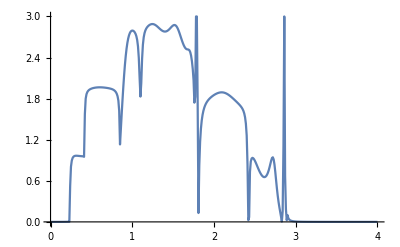

```mathematica
ListPlot[%408,Joined->True]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{2,2}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028063},{0.01,0.0000269858},{0.02,0.0000239065},{0.03,0.0000187574},{0.04,0.0000113433},{0.05,1.32579×10^-6},{0.06,0.0000118076},{0.07,0.0000287919},{0.08,0.0000506614},{0.09,0.000078865},{0.1,0.000115444},{0.11,0.000163308},{0.12,0.000226671},{0.13,0.000311773},{0.14,0.000428082},{0.15,0.000590423},{0.16,0.000822901},{0.17,0.00116656},{0.18,0.00169557},{0.19,0.00255468},{0.2,0.0040584},{0.21,0.00700816},{0.22,0.0140812},{0.23,0.0417988},{0.24,0.345295},{0.25,0.667418},{0.26,0.783844},{0.27,0.842638},{0.28,0.877542},{0.29,0.900159},{0.3,0.915479},{0.31,0.925956},{0.32,0.932895},{0.33,0.936995},{0.34,0.938588},{0.35,0.937712},{0.36,0.934097},{0.37,0.926995},{0.38,0.914709},{0.39,0.893129},{0.4,0.849766},{0.41,0.716568},{0.42,0.883715},{0.43,1.31367},{0.44,1.53407},{0.45,1.66671},{0.46,1.75371},{0.47,1.81362},{0.48,1.85598},{0.49,1.88627},{0.5,1.90789},{0.51,1.92309},{0.52,1.93346},{0.53,1.94014},{0.54,1.94398},{0.55,1.94567},{0.56,1.94573},{0.57,1.94457},{0.58,1.94256},{0.59,1.93995},{0.6,1.93699},{0.61,1.93387},{0.62,1.93074},{0.63,1.92772},{0.64,1.92492},{0.65,1.92241},{0.66,1.92026},{0.67,1.91851},{0.68,1.91718},{0.69,1.91631},{0.7,1.91588},{0.71,1.9159},{0.72,1.91634},{0.73,1.91718},{0.74,1.91836},{0.75,1.91983},{0.76,1.92151},{0.77,1.92327},{0.78,1.92494},{0.79,1.92626},{0.8,1.92672},{0.81,1.92535},{0.82,1.91976},{0.83,1.90249},{0.84,1.8347},{0.85,1.46545},{0.86,2.14125},{0.87,2.3846},{0.88,2.51187},{0.89,2.5928},{0.9,2.65048},{0.91,2.69483},{0.92,2.73083},{0.93,2.76125},{0.94,2.78778},{0.95,2.81149},{0.96,2.83307},{0.97,2.85292},{0.98,2.87108},{0.99,2.88708},{1.,2.89922},{1.01,2.90293},{1.02,2.88583},{1.03,2.81324},{1.04,2.59201},{1.05,2.08538},{1.06,1.46684},{1.07,1.20534},{1.08,1.6907},{1.09,2.05385},{1.1,2.25313},{1.11,2.37172},{1.12,2.44858},{1.13,2.50173},{1.14,2.54034},{1.15,2.56947},{1.16,2.59216},{1.17,2.6103},{1.18,2.62516},{1.19,2.63758},{1.2,2.64818},{1.21,2.65738},{1.22,2.66549},{1.23,2.67273},{1.24,2.67928},{1.25,2.68525},{1.26,2.69072},{1.27,2.69575},{1.28,2.70035},{1.29,2.70456},{1.3,2.70837},{1.31,2.71178},{1.32,2.71479},{1.33,2.71738},{1.34,2.71954},{1.35,2.72129},{1.36,2.72261},{1.37,2.72354},{1.38,2.72408},{1.39,2.72427},{1.4,2.72415},{1.41,2.72377},{1.42,2.72316},{1.43,2.72238},{1.44,2.72149},{1.45,2.72052},{1.46,2.7195},{1.47,2.71846},{1.48,2.71737},{1.49,2.71623},{1.5,2.71494},{1.51,2.7134},{1.52,2.71145},{1.53,2.70885},{1.54,2.70529},{1.55,2.70041},{1.56,2.69374},{1.57,2.68474},{1.58,2.67283},{1.59,2.65741},{1.6,2.63793},{1.61,2.61396},{1.62,2.58527},{1.63,2.55191},{1.64,2.51423},{1.65,2.4729},{1.66,2.42876},{1.67,2.38278},{1.68,2.33583},{1.69,2.28856},{1.7,2.24119},{1.71,2.19334},{1.72,2.14362},{1.73,2.08864},{1.74,2.02007},{1.75,1.91177},{1.76,1.60654},{1.77,1.38649},{1.78,1.42994},{1.79,0.514633},{1.8,1.61951},{1.81,1.78907},{1.82,1.84069},{1.83,1.86063},{1.84,1.86842},{1.85,1.87038},{1.86,1.8691},{1.87,1.8658},{1.88,1.86115},{1.89,1.85554},{1.9,1.84926},{1.91,1.84251},{1.92,1.83545},{1.93,1.82822},{1.94,1.82096},{1.95,1.81377},{1.96,1.80675},{1.97,1.80002},{1.98,1.79366},{1.99,1.78776},{2.,1.78239},{2.01,1.77763},{2.02,1.77356},{2.03,1.77024},{2.04,1.76773},{2.05,1.76609},{2.06,1.76537},{2.07,1.7656},{2.08,1.76684},{2.09,1.7691},{2.1,1.7724},{2.11,1.77674},{2.12,1.78211},{2.13,1.78845},{2.14,1.79569},{2.15,1.80373},{2.16,1.81238},{2.17,1.82144},{2.18,1.83061},{2.19,1.83954},{2.2,1.84782},{2.21,1.85494},{2.22,1.86036},{2.23,1.86353},{2.24,1.86389},{2.25,1.86097},{2.26,1.8544},{2.27,1.84401},{2.28,1.82983},{2.29,1.81215},{2.3,1.79153},{2.31,1.76875},{2.32,1.74481},{2.33,1.72088},{2.34,1.69832},{2.35,1.67867},{2.36,1.66377},{2.37,1.65593},{2.38,1.65841},{2.39,1.67633},{2.4,1.71778},{2.41,1.75418},{2.42,0.659689},{2.43,0.0947975},{2.44,0.4805},{2.45,0.252893},{2.46,0.569695},{2.47,0.693326},{2.48,0.753237},{2.49,0.787268},{2.5,0.808867},{2.51,0.823758},{2.52,0.834722},{2.53,0.843257},{2.54,0.850232},{2.55,0.856186},{2.56,0.861463},{2.57,0.866296},{2.58,0.870843},{2.59,0.875213},{2.6,0.879483},{2.61,0.883703},{2.62,0.887907},{2.63,0.892115},{2.64,0.89634},{2.65,0.900587},{2.66,0.904859},{2.67,0.909162},{2.68,0.913503},{2.69,0.917901},{2.7,0.922386},{2.71,0.927005},{2.72,0.931824},{2.73,0.93693},{2.74,0.942426},{2.75,0.948414},{2.76,0.954963},{2.77,0.962028},{2.78,0.969284},{2.79,0.975762},{2.8,0.979032},{2.81,0.973239},{2.82,0.943957},{2.83,0.852855},{2.84,0.583106},{2.85,0.0102688},{2.86,0.00452336},{2.87,0.02949},{2.88,0.000865754},{2.89,0.000261196},{2.9,0.000129804},{2.91,0.000079506},{2.92,0.0000544508},{2.93,0.0000399482},{2.94,0.0000307077},{2.95,0.0000244156},{2.96,0.0000199178},{2.97,0.0000165807},{2.98,0.000014031},{2.99,0.0000120359},{3.,0.0000104435},{3.01,9.15112×10^-6},{3.02,8.08715×10^-6},{3.03,7.20028×10^-6},{3.04,6.45295×10^-6},{3.05,5.81713×10^-6},{3.06,5.27152×10^-6},{3.07,4.79971×10^-6},{3.08,4.38888×10^-6},{3.09,4.02889×10^-6},{3.1,3.71164×10^-6},{3.11,3.43057×10^-6},{3.12,3.18036×10^-6},{3.13,2.95661×10^-6},{3.14,2.75571×10^-6},{3.15,2.57463×10^-6},{3.16,2.41083×10^-6},{3.17,2.26216×10^-6},{3.18,2.12682×10^-6},{3.19,2.00323×10^-6},{3.2,1.89008×10^-6},{3.21,1.78622×10^-6},{3.22,1.69064×10^-6},{3.23,1.60249×10^-6},{3.24,1.52101×10^-6},{3.25,1.44555×10^-6},{3.26,1.37551×10^-6},{3.27,1.3104×10^-6},{3.28,1.24975×10^-6},{3.29,1.19317×10^-6},{3.3,1.14031×10^-6},{3.31,1.09083×10^-6},{3.32,1.04445×10^-6},{3.33,1.00093×10^-6},{3.34,9.60029×10^-7},{3.35,9.2154×10^-7},{3.36,8.85278×10^-7},{3.37,8.51074×10^-7},{3.38,8.18774×10^-7},{3.39,7.8824×10^-7},{3.4,7.59345×10^-7},{3.41,7.31973×10^-7},{3.42,7.06019×10^-7},{3.43,6.81387×10^-7},{3.44,6.57988×10^-7},{3.45,6.35741×10^-7},{3.46,6.14572×10^-7},{3.47,5.94413×10^-7},{3.48,5.75199×10^-7},{3.49,5.56874×10^-7},{3.5,5.39383×10^-7},{3.51,5.22676×10^-7},{3.52,5.06707×10^-7},{3.53,4.91434×10^-7},{3.54,4.76816×10^-7},{3.55,4.62818×10^-7},{3.56,4.49404×10^-7},{3.57,4.36542×10^-7},{3.58,4.24203×10^-7},{3.59,4.12359×10^-7},{3.6,4.00984×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69437×10^-7},{3.64,3.5971×10^-7},{3.65,3.50344×10^-7},{3.66,3.41323×10^-7},{3.67,3.32629×10^-7},{3.68,3.24248×10^-7},{3.69,3.16164×10^-7},{3.7,3.08364×10^-7},{3.71,3.00834×10^-7},{3.72,2.93563×10^-7},{3.73,2.86539×10^-7},{3.74,2.79751×10^-7},{3.75,2.73188×10^-7},{3.76,2.66841×10^-7},{3.77,2.60701×10^-7},{3.78,2.54758×10^-7},{3.79,2.49005×10^-7},{3.8,2.43434×10^-7},{3.81,2.38037×10^-7},{3.82,2.32806×10^-7},{3.83,2.27737×10^-7},{3.84,2.22821×10^-7},{3.85,2.18053×10^-7},{3.86,2.13427×10^-7},{3.87,2.08937×10^-7},{3.88,2.04579×10^-7},{3.89,2.00348×10^-7},{3.9,1.96238×10^-7},{3.91,1.92245×10^-7},{3.92,1.88364×10^-7},{3.93,1.84592×10^-7},{3.94,1.80925×10^-7},{3.95,1.77359×10^-7},{3.96,1.7389×10^-7},{3.97,1.70515×10^-7},{3.98,1.67231×10^-7},{3.99,1.64034×10^-7},{4.,1.60921×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{3,3}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000019455},{0.01,0.0000232826},{0.02,0.0000260951},{0.03,0.0000279913},{0.04,0.0000290162},{0.05,0.0000291624},{0.06,0.0000283676},{0.07,0.0000265055},{0.08,0.0000233707},{0.09,0.0000186534},{0.1,0.0000118991},{0.11,2.44674×10^-6},{0.12,0.0000106714},{0.13,0.0000288917},{0.14,0.0000543904},{0.15,0.0000905575},{0.16,0.000142858},{0.17,0.000220497},{0.18,0.000339867},{0.19,0.000532389},{0.2,0.000864666},{0.21,0.00150036},{0.22,0.00294964},{0.23,0.00749057},{0.24,0.474531},{0.25,0.735753},{0.26,0.821525},{0.27,0.863365},{0.28,0.887896},{0.29,0.903878},{0.3,0.915012},{0.31,0.923118},{0.32,0.929182},{0.33,0.933777},{0.34,0.937234},{0.35,0.939734},{0.36,0.941333},{0.37,0.941945},{0.38,0.94125},{0.39,0.938364},{0.4,0.930475},{0.41,0.902187},{0.42,1.20857},{0.43,1.53413},{0.44,1.69133},{0.45,1.78091},{0.46,1.83691},{0.47,1.8739},{0.48,1.89912},{0.49,1.91659},{0.5,1.92873},{0.51,1.93705},{0.52,1.94259},{0.53,1.94603},{0.54,1.9479},{0.55,1.94857},{0.56,1.94831},{0.57,1.94734},{0.58,1.94583},{0.59,1.94393},{0.6,1.94172},{0.61,1.93932},{0.62,1.93678},{0.63,1.93418},{0.64,1.93157},{0.65,1.92899},{0.66,1.92648},{0.67,1.92407},{0.68,1.92179},{0.69,1.91967},{0.7,1.91773},{0.71,1.91599},{0.72,1.91446},{0.73,1.91316},{0.74,1.91211},{0.75,1.91131},{0.76,1.91078},{0.77,1.91051},{0.78,1.91051},{0.79,1.91076},{0.8,1.91122},{0.81,1.91174},{0.82,1.91188},{0.83,1.91001},{0.84,1.89661},{0.85,1.94527},{0.86,2.42077},{0.87,2.59569},{0.88,2.68288},{0.89,2.73467},{0.9,2.76925},{0.91,2.79453},{0.92,2.81443},{0.93,2.83108},{0.94,2.84565},{0.95,2.85879},{0.96,2.87073},{0.97,2.88135},{0.98,2.89005},{0.99,2.89553},{1.,2.89509},{1.01,2.88327},{1.02,2.84856},{1.03,2.7652},{1.04,2.57151},{1.05,2.10385},{1.06,1.48535},{1.07,1.66556},{1.08,1.85947},{1.09,2.08128},{1.1,2.26453},{1.11,2.3985},{1.12,2.49466},{1.13,2.56462},{1.14,2.61651},{1.15,2.6556},{1.16,2.68531},{1.17,2.70788},{1.18,2.72485},{1.19,2.73726},{1.2,2.74588},{1.21,2.7513},{1.22,2.75396},{1.23,2.75422},{1.24,2.7524},{1.25,2.74876},{1.26,2.74354},{1.27,2.73696},{1.28,2.72924},{1.29,2.72055},{1.3,2.71109},{1.31,2.70103},{1.32,2.69051},{1.33,2.6797},{1.34,2.66873},{1.35,2.65773},{1.36,2.6468},{1.37,2.63606},{1.38,2.62561},{1.39,2.61551},{1.4,2.60586},{1.41,2.59672},{1.42,2.58814},{1.43,2.58018},{1.44,2.57288},{1.45,2.56628},{1.46,2.56042},{1.47,2.55531},{1.48,2.551},{1.49,2.54749},{1.5,2.5448},{1.51,2.54294},{1.52,2.54192},{1.53,2.54174},{1.54,2.54239},{1.55,2.54386},{1.56,2.5461},{1.57,2.54909},{1.58,2.55275},{1.59,2.557},{1.6,2.56174},{1.61,2.56683},{1.62,2.5721},{1.63,2.57735},{1.64,2.58234},{1.65,2.5868},{1.66,2.59042},{1.67,2.59284},{1.68,2.59363},{1.69,2.59222},{1.7,2.58783},{1.71,2.57916},{1.72,2.5638},{1.73,2.53689},{1.74,2.4873},{1.75,2.38572},{1.76,2.13418},{1.77,1.8085},{1.78,1.62904},{1.79,2.78797},{1.8,1.69925},{1.81,1.8323},{1.82,1.86505},{1.83,1.88003},{1.84,1.8892},{1.85,1.89574},{1.86,1.90075},{1.87,1.90472},{1.88,1.90788},{1.89,1.91034},{1.9,1.91217},{1.91,1.91342},{1.92,1.91412},{1.93,1.91429},{1.94,1.91396},{1.95,1.91315},{1.96,1.91187},{1.97,1.91016},{1.98,1.90804},{1.99,1.90554},{2.,1.90269},{2.01,1.89951},{2.02,1.89604},{2.03,1.8923},{2.04,1.88833},{2.05,1.88416},{2.06,1.87981},{2.07,1.87531},{2.08,1.87069},{2.09,1.86596},{2.1,1.86115},{2.11,1.85627},{2.12,1.85134},{2.13,1.84636},{2.14,1.84133},{2.15,1.83627},{2.16,1.83117},{2.17,1.82601},{2.18,1.82079},{2.19,1.81549},{2.2,1.8101},{2.21,1.8046},{2.22,1.79896},{2.23,1.79317},{2.24,1.7872},{2.25,1.78104},{2.26,1.77466},{2.27,1.76806},{2.28,1.76122},{2.29,1.75414},{2.3,1.74678},{2.31,1.73909},{2.32,1.73098},{2.33,1.72222},{2.34,1.71238},{2.35,1.70062},{2.36,1.68524},{2.37,1.66275},{2.38,1.62564},{2.39,1.55637},{2.4,1.40838},{2.41,1.03561},{2.42,0.834515},{2.43,0.809227},{2.44,0.387727},{2.45,0.755254},{2.46,0.900842},{2.47,0.907784},{2.48,0.907238},{2.49,0.905739},{2.5,0.904187},{2.51,0.902748},{2.52,0.901443},{2.53,0.900265},{2.54,0.899199},{2.55,0.898229},{2.56,0.89734},{2.57,0.896519},{2.58,0.895753},{2.59,0.895031},{2.6,0.894343},{2.61,0.893683},{2.62,0.893048},{2.63,0.89244},{2.64,0.89187},{2.65,0.891359},{2.66,0.890939},{2.67,0.890661},{2.68,0.890594},{2.69,0.890836},{2.7,0.89151},{2.71,0.89278},{2.72,0.894847},{2.73,0.89796},{2.74,0.902411},{2.75,0.908536},{2.76,0.91669},{2.77,0.927191},{2.78,0.940187},{2.79,0.955344},{2.8,0.971081},{2.81,0.982618},{2.82,0.976485},{2.83,0.912906},{2.84,0.657148},{2.85,0.0118442},{2.86,0.00387593},{2.87,0.0256576},{2.88,0.000739219},{2.89,0.000235902},{2.9,0.000121829},{2.91,0.0000763801},{2.92,0.0000530555},{2.93,0.000039269},{2.94,0.0000303561},{2.95,0.0000242252},{2.96,0.000019811},{2.97,0.0000165194},{2.98,0.0000139951},{2.99,0.0000120147},{3.,0.0000104309},{3.01,9.14367×10^-6},{3.02,8.08281×10^-6},{3.03,7.19783×10^-6},{3.04,6.45165×10^-6},{3.05,5.81652×10^-6},{3.06,5.27133×10^-6},{3.07,4.79976×10^-6},{3.08,4.38907×10^-6},{3.09,4.02915×10^-6},{3.1,3.71192×10^-6},{3.11,3.43086×10^-6},{3.12,3.18063×10^-6},{3.13,2.95687×10^-6},{3.14,2.75595×10^-6},{3.15,2.57484×10^-6},{3.16,2.41102×10^-6},{3.17,2.26233×10^-6},{3.18,2.12696×10^-6},{3.19,2.00336×10^-6},{3.2,1.8902×10^-6},{3.21,1.78632×10^-6},{3.22,1.69073×10^-6},{3.23,1.60257×10^-6},{3.24,1.52108×10^-6},{3.25,1.4456×10^-6},{3.26,1.37556×10^-6},{3.27,1.31044×10^-6},{3.28,1.24979×10^-6},{3.29,1.19321×10^-6},{3.3,1.14034×10^-6},{3.31,1.09085×10^-6},{3.32,1.04448×10^-6},{3.33,1.00095×10^-6},{3.34,9.60047×10^-7},{3.35,9.21556×10^-7},{3.36,8.85292×10^-7},{3.37,8.51086×10^-7},{3.38,8.18785×10^-7},{3.39,7.8825×10^-7},{3.4,7.59354×10^-7},{3.41,7.31981×10^-7},{3.42,7.06026×10^-7},{3.43,6.81393×10^-7},{3.44,6.57993×10^-7},{3.45,6.35746×10^-7},{3.46,6.14577×10^-7},{3.47,5.94417×10^-7},{3.48,5.75203×10^-7},{3.49,5.56877×10^-7},{3.5,5.39386×10^-7},{3.51,5.22678×10^-7},{3.52,5.06709×10^-7},{3.53,4.91436×10^-7},{3.54,4.76818×10^-7},{3.55,4.62819×10^-7},{3.56,4.49405×10^-7},{3.57,4.36543×10^-7},{3.58,4.24204×10^-7},{3.59,4.1236×10^-7},{3.6,4.00985×10^-7},{3.61,3.90055×10^-7},{3.62,3.79546×10^-7},{3.63,3.69438×10^-7},{3.64,3.59711×10^-7},{3.65,3.50345×10^-7},{3.66,3.41324×10^-7},{3.67,3.3263×10^-7},{3.68,3.24248×10^-7},{3.69,3.16164×10^-7},{3.7,3.08364×10^-7},{3.71,3.00835×10^-7},{3.72,2.93564×10^-7},{3.73,2.86539×10^-7},{3.74,2.79751×10^-7},{3.75,2.73188×10^-7},{3.76,2.66841×10^-7},{3.77,2.60701×10^-7},{3.78,2.54758×10^-7},{3.79,2.49005×10^-7},{3.8,2.43434×10^-7},{3.81,2.38037×10^-7},{3.82,2.32807×10^-7},{3.83,2.27737×10^-7},{3.84,2.22821×10^-7},{3.85,2.18053×10^-7},{3.86,2.13427×10^-7},{3.87,2.08937×10^-7},{3.88,2.04579×10^-7},{3.89,2.00348×10^-7},{3.9,1.96238×10^-7},{3.91,1.92245×10^-7},{3.92,1.88364×10^-7},{3.93,1.84593×10^-7},{3.94,1.80925×10^-7},{3.95,1.77359×10^-7},{3.96,1.7389×10^-7},{3.97,1.70515×10^-7},{3.98,1.67231×10^-7},{3.99,1.64034×10^-7},{4.,1.60921×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{4,4}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[1].Sl11.T2[1]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[1].Sl12.T1[1]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[1].Sl13.T2[1]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[1].Sl14.T1[1]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[1].Sl15.T2[1]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[1].Sl16.T1[1]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[1].Sl17.T2[1]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280079},{0.01,0.000028019},{0.02,0.0000281463},{0.03,0.0000283927},{0.04,0.0000287636},{0.05,0.0000292672},{0.06,0.0000299155},{0.07,0.0000307245},{0.08,0.000031716},{0.09,0.0000329192},{0.1,0.0000343733},{0.11,0.0000361325},{0.12,0.0000382728},{0.13,0.0000409046},{0.14,0.0000441946},{0.15,0.0000484064},{0.16,0.000053982},{0.17,0.0000617179},{0.18,0.00007318},{0.19,0.0000918138},{0.2,0.000126436},{0.21,0.000205207},{0.22,0.00045988},{0.23,0.0025407},{0.24,0.301373},{0.25,0.56461},{0.26,0.690697},{0.27,0.76255},{0.28,0.807914},{0.29,0.838564},{0.3,0.86031},{0.31,0.876329},{0.32,0.888499},{0.33,0.897988},{0.34,0.905558},{0.35,0.911716},{0.36,0.9168},{0.37,0.921023},{0.38,0.924468},{0.39,0.927005},{0.4,0.9278},{0.41,0.921596},{0.42,1.78323},{0.43,1.88826},{0.44,1.91305},{0.45,1.92493},{0.46,1.93247},{0.47,1.93803},{0.48,1.94255},{0.49,1.94646},{0.5,1.94997},{0.51,1.95323},{0.52,1.9563},{0.53,1.95923},{0.54,1.96205},{0.55,1.96478},{0.56,1.96743},{0.57,1.96999},{0.58,1.97246},{0.59,1.97484},{0.6,1.97711},{0.61,1.97928},{0.62,1.98131},{0.63,1.98321},{0.64,1.98494},{0.65,1.98651},{0.66,1.98789},{0.67,1.98906},{0.68,1.99001},{0.69,1.99072},{0.7,1.99116},{0.71,1.99133},{0.72,1.99118},{0.73,1.99069},{0.74,1.98982},{0.75,1.98851},{0.76,1.98669},{0.77,1.98423},{0.78,1.98093},{0.79,1.9765},{0.8,1.97036},{0.81,1.96144},{0.82,1.94736},{0.83,1.92182},{0.84,1.85972},{0.85,1.67125},{0.86,1.94427},{0.87,2.13353},{0.88,2.27317},{0.89,2.38186},{0.9,2.46944},{0.91,2.54174},{0.92,2.6025},{0.93,2.65424},{0.94,2.69874},{0.95,2.73727},{0.96,2.77078},{0.97,2.79988},{0.98,2.82491},{0.99,2.84573},{1.,2.86143},{1.01,2.86935},{1.02,2.86255},{1.03,2.82267},{1.04,2.70007},{1.05,2.38826},{1.06,1.94219},{1.07,1.91953},{1.08,2.17588},{1.09,2.37788},{1.1,2.50371},{1.11,2.58284},{1.12,2.63496},{1.13,2.67079},{1.14,2.69628},{1.15,2.71485},{1.16,2.72859},{1.17,2.73882},{1.18,2.74641},{1.19,2.75197},{1.2,2.75592},{1.21,2.75856},{1.22,2.76009},{1.23,2.76069},{1.24,2.76047},{1.25,2.75952},{1.26,2.75789},{1.27,2.75564},{1.28,2.75281},{1.29,2.74941},{1.3,2.74546},{1.31,2.74098},{1.32,2.73598},{1.33,2.73046},{1.34,2.72443},{1.35,2.71788},{1.36,2.71083},{1.37,2.70326},{1.38,2.69517},{1.39,2.68654},{1.4,2.67736},{1.41,2.66761},{1.42,2.65726},{1.43,2.64626},{1.44,2.63457},{1.45,2.62214},{1.46,2.6089},{1.47,2.59477},{1.48,2.57968},{1.49,2.56354},{1.5,2.54625},{1.51,2.52772},{1.52,2.50786},{1.53,2.48655},{1.54,2.46372},{1.55,2.43926},{1.56,2.41311},{1.57,2.38516},{1.58,2.35533},{1.59,2.32353},{1.6,2.28963},{1.61,2.2535},{1.62,2.21492},{1.63,2.17361},{1.64,2.12917},{1.65,2.08103},{1.66,2.02841},{1.67,1.97021},{1.68,1.90486},{1.69,1.83008},{1.7,1.74242},{1.71,1.63638},{1.72,1.50251},{1.73,1.32309},{1.74,1.06047},{1.75,0.619914},{1.76,0.302824},{1.77,1.23278},{1.78,1.71928},{1.79,1.79836},{1.8,1.75262},{1.81,1.80959},{1.82,1.954},{1.83,1.94745},{1.84,1.94464},{1.85,1.9432},{1.86,1.94212},{1.87,1.94101},{1.88,1.9397},{1.89,1.93812},{1.9,1.93623},{1.91,1.93401},{1.92,1.93145},{1.93,1.92855},{1.94,1.9253},{1.95,1.92171},{1.96,1.91778},{1.97,1.91353},{1.98,1.90896},{1.99,1.90408},{2.,1.89891},{2.01,1.89347},{2.02,1.88777},{2.03,1.88183},{2.04,1.87568},{2.05,1.86933},{2.06,1.86281},{2.07,1.85614},{2.08,1.84935},{2.09,1.84246},{2.1,1.8355},{2.11,1.82849},{2.12,1.82145},{2.13,1.81441},{2.14,1.8074},{2.15,1.80042},{2.16,1.79351},{2.17,1.78667},{2.18,1.77993},{2.19,1.77329},{2.2,1.76676},{2.21,1.76036},{2.22,1.75406},{2.23,1.74787},{2.24,1.74177},{2.25,1.73572},{2.26,1.7297},{2.27,1.72365},{2.28,1.71747},{2.29,1.71106},{2.3,1.70427},{2.31,1.69688},{2.32,1.68857},{2.33,1.67889},{2.34,1.66717},{2.35,1.65233},{2.36,1.63259},{2.37,1.60474},{2.38,1.56234},{2.39,1.49017},{2.4,1.34039},{2.41,0.817665},{2.42,3},{2.43,0.436983},{2.44,0.685967},{2.45,0.759904},{2.46,0.797209},{2.47,0.822261},{2.48,0.84213},{2.49,0.85946},{2.5,0.875392},{2.51,0.890442},{2.52,0.904829},{2.53,0.918613},{2.54,0.931755},{2.55,0.944155},{2.56,0.95567},{2.57,0.966128},{2.58,0.975337},{2.59,0.983101},{2.6,0.989226},{2.61,0.993535},{2.62,0.995875},{2.63,0.996135},{2.64,0.994251},{2.65,0.990219},{2.66,0.984098},{2.67,0.976017},{2.68,0.966175},{2.69,0.954839},{2.7,0.94234},{2.71,0.929073},{2.72,0.91549},{2.73,0.902102},{2.74,0.889483},{2.75,0.878282},{2.76,0.869246},{2.77,0.863255},{2.78,0.861377},{2.79,0.86495},{2.8,0.875688},{2.81,0.895772},{2.82,0.927633},{2.83,0.971238},{2.84,0.990705},{2.85,0.0251342},{2.86,0.00154401},{2.87,0.000647231},{2.88,0.000728657},{2.89,0.0186051},{2.9,0.000624891},{2.91,0.000156},{2.92,0.0000783727},{2.93,0.0000500079},{2.94,0.0000357113},{2.95,0.0000271896},{2.96,0.0000215765},{2.97,0.0000176293},{2.98,0.0000147227},{2.99,0.0000125077},{3.,0.0000107741},{3.01,9.38806×10^-6},{3.02,8.26018×10^-6},{3.03,7.32867×10^-6},{3.04,6.54955×10^-6},{3.05,5.89068×10^-6},{3.06,5.32813×10^-6},{3.07,4.8437×10^-6},{3.08,4.42335×10^-6},{3.09,4.05611×10^-6},{3.1,3.73328×10^-6},{3.11,3.44788×10^-6},{3.12,3.19429×10^-6},{3.13,2.96788×10^-6},{3.14,2.76487×10^-6},{3.15,2.58211×10^-6},{3.16,2.41696×10^-6},{3.17,2.26721×10^-6},{3.18,2.13098×10^-6},{3.19,2.00669×10^-6},{3.2,1.89295×10^-6},{3.21,1.78861×10^-6},{3.22,1.69264×10^-6},{3.23,1.60416×10^-6},{3.24,1.52242×10^-6},{3.25,1.44673×10^-6},{3.26,1.37651×10^-6},{3.27,1.31124×10^-6},{3.28,1.25046×10^-6},{3.29,1.19378×10^-6},{3.3,1.14081×10^-6},{3.31,1.09126×10^-6},{3.32,1.04482×10^-6},{3.33,1.00124×10^-6},{3.34,9.60294×10^-7},{3.35,9.21766×10^-7},{3.36,8.8547×10^-7},{3.37,8.51237×10^-7},{3.38,8.18913×10^-7},{3.39,7.88358×10^-7},{3.4,7.59445×10^-7},{3.41,7.32058×10^-7},{3.42,7.06092×10^-7},{3.43,6.81448×10^-7},{3.44,6.5804×10^-7},{3.45,6.35785×10^-7},{3.46,6.14609×10^-7},{3.47,5.94444×10^-7},{3.48,5.75225×10^-7},{3.49,5.56895×10^-7},{3.5,5.39401×10^-7},{3.51,5.2269×10^-7},{3.52,5.06719×10^-7},{3.53,4.91443×10^-7},{3.54,4.76824×10^-7},{3.55,4.62824×10^-7},{3.56,4.49408×10^-7},{3.57,4.36545×10^-7},{3.58,4.24205×10^-7},{3.59,4.1236×10^-7},{3.6,4.00985×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69436×10^-7},{3.64,3.59708×10^-7},{3.65,3.50343×10^-7},{3.66,3.41321×10^-7},{3.67,3.32627×10^-7},{3.68,3.24246×10^-7},{3.69,3.16162×10^-7},{3.7,3.08361×10^-7},{3.71,3.00832×10^-7},{3.72,2.93561×10^-7},{3.73,2.86536×10^-7},{3.74,2.79748×10^-7},{3.75,2.73185×10^-7},{3.76,2.66839×10^-7},{3.77,2.60698×10^-7},{3.78,2.54756×10^-7},{3.79,2.49003×10^-7},{3.8,2.43432×10^-7},{3.81,2.38034×10^-7},{3.82,2.32804×10^-7},{3.83,2.27734×10^-7},{3.84,2.22819×10^-7},{3.85,2.18051×10^-7},{3.86,2.13425×10^-7},{3.87,2.08936×10^-7},{3.88,2.04578×10^-7},{3.89,2.00346×10^-7},{3.9,1.96236×10^-7},{3.91,1.92243×10^-7},{3.92,1.88363×10^-7},{3.93,1.84591×10^-7},{3.94,1.80924×10^-7},{3.95,1.77358×10^-7},{3.96,1.73889×10^-7},{3.97,1.70514×10^-7},{3.98,1.6723×10^-7},{3.99,1.64033×10^-7},{4.,1.6092×10^-7}}

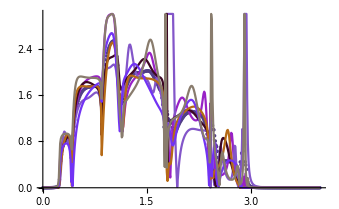

```mathematica
Show[ListPlot[final,Joined->False,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[r1,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[o3,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[p4,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[q5,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[r6,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[n7,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],PlotRange->All]
```

```mathematica
ListPlot[m2,Joined->True]
```

$Aborted

```mathematica
m:=(m1+m2+m3+m4+m5+m6+m7+m8)/8
```

```mathematica
n:=(n1+n2+n3+n4+n5+n6+n7+n8)/8
```

```mathematica
o:=(o1+o2+o3+o4+o5+o6+o7+o8)/8
```

```mathematica
p:=(p1+p2+p3+p4+p5+p6+p7+p8)/8
```

```mathematica
q:=(q1+q2+q3+q4+q5+q6+q7+q8)/8
```

```mathematica
r:=(r1+r2+r3+r4+r5+r6+r7+r8)/8
```

```mathematica
final=(m+n+o+p+q+r)/6
```

{{0.,0.0000364647},{0.01,0.0000295912},{0.02,0.0000259164},{0.03,0.0000398192},{0.04,0.0000708353},{0.05,0.000113877},{0.06,0.000171383},{0.07,0.000243747},{0.08,0.00033335},{0.09,0.000443484},{0.1,0.000579132},{0.11,0.000745077},{0.12,0.000949572},{0.13,0.00120383},{0.14,0.00152328},{0.15,0.00192979},{0.16,0.00245755},{0.17,0.00316003},{0.18,0.00412605},{0.19,0.00551303},{0.2,0.00763085},{0.21,0.011181},{0.22,0.0181991},{0.23,0.0390624},{0.24,0.238596},{0.25,0.473521},{0.26,0.614472},{0.27,0.702576},{0.28,0.760997},{0.29,0.800962},{0.3,0.828792},{0.31,0.848309},{0.32,0.861913},{0.33,0.871122},{0.34,0.876852},{0.35,0.879554},{0.36,0.879225},{0.37,0.875258},{0.38,0.865909},{0.39,0.846592},{0.4,0.802659},{0.41,0.684312},{0.42,0.786785},{0.43,1.12274},{0.44,1.32501},{0.45,1.45448},{0.46,1.54523},{0.47,1.6119},{0.48,1.66213},{0.49,1.70052},{0.5,1.73011},{0.51,1.75306},{0.52,1.77095},{0.53,1.78497},{0.54,1.79602},{0.55,1.80476},{0.56,1.81172},{0.57,1.81731},{0.58,1.82186},{0.59,1.82562},{0.6,1.82878},{0.61,1.8315},{0.62,1.83391},{0.63,1.8361},{0.64,1.83812},{0.65,1.84002},{0.66,1.84183},{0.67,1.84355},{0.68,1.8452},{0.69,1.84675},{0.7,1.84818},{0.71,1.84948},{0.72,1.85058},{0.73,1.85145},{0.74,1.85198},{0.75,1.85207},{0.76,1.85154},{0.77,1.85016},{0.78,1.84752},{0.79,1.84297},{0.8,1.83535},{0.81,1.82238},{0.82,1.79902},{0.83,1.75128},{0.84,1.61996},{0.85,1.15132},{0.86,1.65744},{0.87,1.92518},{0.88,2.10218},{0.89,2.23098},{0.9,2.32905},{0.91,2.40571},{0.92,2.46678},{0.93,2.51627},{0.94,2.55703},{0.95,2.59111},{0.96,2.62},{0.97,2.64473},{0.98,2.66589},{0.99,2.68365},{1.,2.69753},{1.01,2.70602},{1.02,2.70579},{1.03,2.68984},{1.04,2.64391},{1.05,2.54192},{1.06,2.35188},{1.07,2.08764},{1.08,1.84067},{1.09,1.69946},{1.1,1.70852},{1.11,1.80633},{1.12,1.92869},{1.13,2.03231},{1.14,2.10731},{1.15,2.15962},{1.16,2.1955},{1.17,2.22094},{1.18,2.2423},{1.19,2.26495},{1.2,2.29052},{1.21,2.31706},{1.22,2.34196},{1.23,2.36372},{1.24,2.38196},{1.25,2.39697},{1.26,2.40931},{1.27,2.41951},{1.28,2.42795},{1.29,2.43489},{1.3,2.4405},{1.31,2.44489},{1.32,2.4482},{1.33,2.45056},{1.34,2.45213},{1.35,2.45306},{1.36,2.45349},{1.37,2.45353},{1.38,2.45327},{1.39,2.45277},{1.4,2.45206},{1.41,2.45115},{1.42,2.45007},{1.43,2.44881},{1.44,2.44738},{1.45,2.44578},{1.46,2.44399},{1.47,2.44197},{1.48,2.43966},{1.49,2.43692},{1.5,2.43351},{1.51,2.42907},{1.52,2.42314},{1.53,2.41523},{1.54,2.40498},{1.55,2.39228},{1.56,2.3772},{1.57,2.35994},{1.58,2.34062},{1.59,2.31935},{1.6,2.29631},{1.61,2.27177},{1.62,2.24608},{1.63,2.21953},{1.64,2.1924},{1.65,2.16494},{1.66,2.13742},{1.67,2.10999},{1.68,2.08246},{1.69,2.05329},{1.7,2.01486},{1.71,1.94823},{1.72,1.84658},{1.73,1.71427},{1.74,1.53534},{1.75,1.24982},{1.76,0.891397},{1.77,1.2971},{1.78,1.49112},{1.79,1.44223},{1.8,1.56076},{1.81,1.45389},{1.82,1.36848},{1.83,1.29541},{1.84,1.25704},{1.85,1.26816},{1.86,1.27871},{1.87,1.36555},{1.88,1.44523},{1.89,1.4972},{1.9,1.53282},{1.91,1.55839},{1.92,1.5773},{1.93,1.59161},{1.94,1.60263},{1.95,1.61127},{1.96,1.61818},{1.97,1.62382},{1.98,1.62853},{1.99,1.63258},{2.,1.63616},{2.01,1.63941},{2.02,1.64243},{2.03,1.64524},{2.04,1.64785},{2.05,1.6502},{2.06,1.65218},{2.07,1.65366},{2.08,1.65448},{2.09,1.65445},{2.1,1.65342},{2.11,1.6513},{2.12,1.64804},{2.13,1.64372},{2.14,1.63849},{2.15,1.63259},{2.16,1.62629},{2.17,1.61984},{2.18,1.6135},{2.19,1.60742},{2.2,1.60172},{2.21,1.59648},{2.22,1.59171},{2.23,1.58743},{2.24,1.58361},{2.25,1.58018},{2.26,1.57695},{2.27,1.57354},{2.28,1.56934},{2.29,1.56349},{2.3,1.55492},{2.31,1.54225},{2.32,1.52339},{2.33,1.49576},{2.34,1.45928},{2.35,1.41738},{2.36,1.37197},{2.37,1.32115},{2.38,1.25873},{2.39,1.17},{2.4,1.01741},{2.41,0.728368},{2.42,1.27917},{2.43,1.13772},{2.44,0.71818},{2.45,0.666287},{2.46,0.641687},{2.47,0.64996},{2.48,0.617578},{2.49,0.633912},{2.5,0.648427},{2.51,0.691327},{2.52,0.703947},{2.53,0.728354},{2.54,0.751037},{2.55,0.764082},{2.56,0.771634},{2.57,0.775465},{2.58,0.776718},{2.59,0.776247},{2.6,0.774723},{2.61,0.772663},{2.62,0.770457},{2.63,0.768376},{2.64,0.766593},{2.65,0.765219},{2.66,0.76433},{2.67,0.764007},{2.68,0.76435},{2.69,0.765433},{2.7,0.767167},{2.71,0.769013},{2.72,0.76962},{2.73,0.766797},{2.74,0.758498},{2.75,0.744351},{2.76,0.72559},{2.77,0.703249},{2.78,0.677017},{2.79,0.6458},{2.8,0.608959},{2.81,0.566039},{2.82,0.523311},{2.83,0.488444},{2.84,0.424028},{2.85,0.386935},{2.86,0.525847},{2.87,0.497035},{2.88,0.237046},{2.89,0.344185},{2.9,0.195743},{2.91,0.0568291},{2.92,0.0334883},{2.93,0.0198848},{2.94,0.0135003},{2.95,0.00976231},{2.96,0.00735568},{2.97,0.0057112},{2.98,0.00453821},{2.99,0.00367346},{3.,0.00301899},{3.01,0.00251293},{3.02,0.00211452},{3.03,0.00179605},{3.04,0.00153814},{3.05,0.00132684},{3.06,0.00115196},{3.07,0.00100593},{3.08,0.000883009},{3.09,0.000778787},{3.1,0.000689842},{3.11,0.000613483},{3.12,0.000547571},{3.13,0.000490393},{3.14,0.000440561},{3.15,0.000396947},{3.16,0.000358624},{3.17,0.000324825},{3.18,0.000294915},{3.19,0.000268359},{3.2,0.000244712},{3.21,0.000223594},{3.22,0.000204689},{3.23,0.00018772},{3.24,0.000172449},{3.25,0.000158677},{3.26,0.000146229},{3.27,0.000134956},{3.28,0.000124726},{3.29,0.000115425},{3.3,0.000106955},{3.31,0.0000992287},{3.32,0.0000921686},{3.33,0.0000857077},{3.34,0.0000797863},{3.35,0.0000743517},{3.36,0.000069357},{3.37,0.0000647607},{3.38,0.0000605256},{3.39,0.0000566187},{3.4,0.0000530101},{3.41,0.0000496735},{3.42,0.0000465848},{3.43,0.0000437228},{3.44,0.0000410681},{3.45,0.0000386031},{3.46,0.0000363123},{3.47,0.0000341813},{3.48,0.0000321971},{3.49,0.0000303482},{3.5,0.0000286237},{3.51,0.0000270141},{3.52,0.0000255104},{3.53,0.0000241046},{3.54,0.0000227894},{3.55,0.0000215581},{3.56,0.0000204043},{3.57,0.0000193227},{3.58,0.0000183078},{3.59,0.0000173551},{3.6,0.00001646},{3.61,0.0000156187},{3.62,0.0000148273},{3.63,0.0000140826},{3.64,0.0000133824},{3.65,0.0000127254},{3.66,0.0000121059},{3.67,0.0000115215},{3.68,0.0000109698},{3.69,0.0000104487},{3.7,9.95641×10^-6},{3.71,9.49099×10^-6},{3.72,9.05079×10^-6},{3.73,8.63425×10^-6},{3.74,8.23991×10^-6},{3.75,7.86641×10^-6},{3.76,7.51251×10^-6},{3.77,7.17702×10^-6},{3.78,6.85885×10^-6},{3.79,6.55699×10^-6},{3.8,6.27048×10^-6},{3.81,5.99842×10^-6},{3.82,5.73999×10^-6},{3.83,5.49442×10^-6},{3.84,5.26096×10^-6},{3.85,5.03895×10^-6},{3.86,4.82774×10^-6},{3.87,4.62673×10^-6},{3.88,4.43537×10^-6},{3.89,4.25312×10^-6},{3.9,4.0795×10^-6},{3.91,3.91405×10^-6},{3.92,3.75631×10^-6},{3.93,3.60589×10^-6},{3.94,3.46366×10^-6},{3.95,3.32831×10^-6},{3.96,3.19906×10^-6},{3.97,3.0756×10^-6},{3.98,2.95764×10^-6},{3.99,2.84489×10^-6},{4.,2.7371×10^-6}}

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv",final10]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv

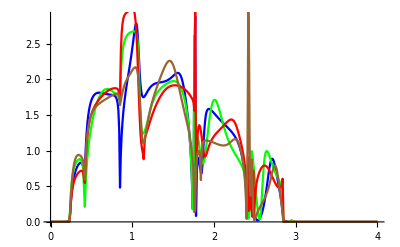

```mathematica
Show[ListPlot[r8,Joined->True,PlotStyle->Blue],ListPlot[r5,Joined->True,PlotStyle->Green],ListPlot[r7,Joined->True,PlotStyle->Red],ListPlot[r6,Joined->True,PlotStyle->Brown]]
```

```mathematica
final=(m+n+o+p+q+r)/6
```

{{0.,0.0000599302},{0.01,0.0000468427},{0.02,0.0000485654},{0.03,0.0000824322},{0.04,0.00014097},{0.05,0.000224386},{0.06,0.000330346},{0.07,0.00046068},{0.08,0.000619475},{0.09,0.000811378},{0.1,0.00104212},{0.11,0.00132092},{0.12,0.00165848},{0.13,0.00206915},{0.14,0.0025741},{0.15,0.00320387},{0.16,0.00400339},{0.17,0.00504208},{0.18,0.00643388},{0.19,0.00837553},{0.2,0.0112447},{0.21,0.0158762},{0.22,0.0246165},{0.23,0.0489085},{0.24,0.142109},{0.25,0.314356},{0.26,0.461694},{0.27,0.571713},{0.28,0.655294},{0.29,0.716673},{0.3,0.759359},{0.31,0.787332},{0.32,0.804419},{0.33,0.813636},{0.34,0.816987},{0.35,0.815525},{0.36,0.809405},{0.37,0.797721},{0.38,0.777806},{0.39,0.742926},{0.4,0.673057},{0.41,0.51618},{0.42,0.572055},{0.43,0.70563},{0.44,0.902874},{0.45,1.05451},{0.46,1.16944},{0.47,1.26048},{0.48,1.33488},{0.49,1.39706},{0.5,1.44987},{0.51,1.4952},{0.52,1.53436},{0.53,1.56825},{0.54,1.59753},{0.55,1.62274},{0.56,1.64433},{0.57,1.66269},{0.58,1.6782},{0.59,1.69122},{0.6,1.70209},{0.61,1.71111},{0.62,1.71856},{0.63,1.72468},{0.64,1.72969},{0.65,1.7338},{0.66,1.73715},{0.67,1.73989},{0.68,1.74216},{0.69,1.74404},{0.7,1.74562},{0.71,1.74697},{0.72,1.74812},{0.73,1.74909},{0.74,1.74984},{0.75,1.7503},{0.76,1.75032},{0.77,1.74963},{0.78,1.74782},{0.79,1.74415},{0.8,1.73734},{0.81,1.72494},{0.82,1.70157},{0.83,1.65289},{0.84,1.52184},{0.85,1.09664},{0.86,1.49334},{0.87,1.7304},{0.88,1.89752},{0.89,2.02539},{0.9,2.12661},{0.91,2.20793},{0.92,2.27374},{0.93,2.32734},{0.94,2.37141},{0.95,2.40811},{0.96,2.4391},{0.97,2.46555},{0.98,2.48806},{0.99,2.5067},{1.,2.52094},{1.01,2.52959},{1.02,2.53062},{1.03,2.52097},{1.04,2.49623},{1.05,2.45051},{1.06,2.37654},{1.07,2.26618},{1.08,2.1142},{1.09,1.93204},{1.1,1.75129},{1.11,1.60478},{1.12,1.51544},{1.13,1.46232},{1.14,1.45428},{1.15,1.47885},{1.16,1.53196},{1.17,1.58538},{1.18,1.633},{1.19,1.67524},{1.2,1.71361},{1.21,1.74933},{1.22,1.7829},{1.23,1.81406},{1.24,1.84224},{1.25,1.86713},{1.26,1.88884},{1.27,1.90773},{1.28,1.92432},{1.29,1.93912},{1.3,1.95235},{1.31,1.9639},{1.32,1.97337},{1.33,1.98031},{1.34,1.98452},{1.35,1.98628},{1.36,1.98629},{1.37,1.98546},{1.38,1.98459},{1.39,1.98421},{1.4,1.9846},{1.41,1.98584},{1.42,1.98788},{1.43,1.99066},{1.44,1.99408},{1.45,1.99804},{1.46,2.00233},{1.47,2.00666},{1.48,2.01058},{1.49,2.01371},{1.5,2.0159},{1.51,2.01713},{1.52,2.01724},{1.53,2.01557},{1.54,2.01107},{1.55,2.00287},{1.56,1.99075},{1.57,1.97516},{1.58,1.95692},{1.59,1.93701},{1.6,1.91627},{1.61,1.89509},{1.62,1.8732},{1.63,1.85},{1.64,1.82513},{1.65,1.79861},{1.66,1.7706},{1.67,1.74165},{1.68,1.71361},{1.69,1.69146},{1.7,1.6782},{1.71,1.63242},{1.72,1.55054},{1.73,1.43525},{1.74,1.27288},{1.75,1.04789},{1.76,0.996966},{1.77,1.41872},{1.78,1.3023},{1.79,1.32144},{1.8,1.26467},{1.81,1.19187},{1.82,1.16671},{1.83,1.16454},{1.84,1.15655},{1.85,1.13584},{1.86,1.11632},{1.87,1.04177},{1.88,0.994296},{1.89,0.950403},{1.9,0.943131},{1.91,0.950538},{1.92,0.963924},{1.93,0.991397},{1.94,1.01948},{1.95,1.04991},{1.96,1.07815},{1.97,1.10387},{1.98,1.12671},{1.99,1.14778},{2.,1.16785},{2.01,1.18733},{2.02,1.20617},{2.03,1.22394},{2.04,1.24006},{2.05,1.25412},{2.06,1.26605},{2.07,1.27598},{2.08,1.28426},{2.09,1.29132},{2.1,1.29757},{2.11,1.30333},{2.12,1.30862},{2.13,1.31313},{2.14,1.31618},{2.15,1.31705},{2.16,1.31563},{2.17,1.31269},{2.18,1.30938},{2.19,1.30631},{2.2,1.30298},{2.21,1.29813},{2.22,1.29099},{2.23,1.2822},{2.24,1.27318},{2.25,1.26498},{2.26,1.25794},{2.27,1.25182},{2.28,1.24598},{2.29,1.23917},{2.3,1.22889},{2.31,1.21062},{2.32,1.18123},{2.33,1.14274},{2.34,1.09777},{2.35,1.0472},{2.36,0.990566},{2.37,0.925673},{2.38,0.847919},{2.39,0.753694},{2.4,0.619776},{2.41,0.473901},{2.42,0.827857},{2.43,1.07516},{2.44,1.21253},{2.45,1.07563},{2.46,1.0053},{2.47,0.999064},{2.48,0.897594},{2.49,0.807237},{2.5,0.733551},{2.51,0.708927},{2.52,0.628653},{2.53,0.522176},{2.54,0.43713},{2.55,0.41583},{2.56,0.407516},{2.57,0.447222},{2.58,0.468063},{2.59,0.474081},{2.6,0.470375},{2.61,0.461424},{2.62,0.464356},{2.63,0.459552},{2.64,0.45953},{2.65,0.462294},{2.66,0.461346},{2.67,0.456689},{2.68,0.452492},{2.69,0.45018},{2.7,0.449606},{2.71,0.453282},{2.72,0.455807},{2.73,0.451793},{2.74,0.451837},{2.75,0.444585},{2.76,0.424843},{2.77,0.401808},{2.78,0.36904},{2.79,0.326559},{2.8,0.299259},{2.81,0.288244},{2.82,0.287373},{2.83,0.284135},{2.84,0.284732},{2.85,0.445979},{2.86,0.400264},{2.87,0.598151},{2.88,0.580904},{2.89,0.630537},{2.9,0.780958},{2.91,0.749483},{2.92,0.44806},{2.93,0.39198},{2.94,0.316248},{2.95,0.15673},{2.96,0.10039},{2.97,0.0629124},{2.98,0.0414338},{2.99,0.0295701},{3.,0.0221656},{3.01,0.017177},{3.02,0.0136008},{3.03,0.0109853},{3.04,0.00900893},{3.05,0.00748266},{3.06,0.0062825},{3.07,0.0053243},{3.08,0.0045492},{3.09,0.00391505},{3.1,0.003391},{3.11,0.00295408},{3.12,0.00258691},{3.13,0.00227613},{3.14,0.00201139},{3.15,0.00178452},{3.16,0.00158906},{3.17,0.00141983},{3.18,0.00127263},{3.19,0.00114405},{3.2,0.00103129},{3.21,0.000932032},{3.22,0.000844369},{3.23,0.000766693},{3.24,0.000697658},{3.25,0.000636129},{3.26,0.000581141},{3.27,0.000531875},{3.28,0.00048763},{3.29,0.000447802},{3.3,0.000411874},{3.31,0.000379396},{3.32,0.000349981},{3.33,0.000323289},{3.34,0.000299025},{3.35,0.00027693},{3.36,0.000256779},{3.37,0.000238373},{3.38,0.000221533},{3.39,0.000206104},{3.4,0.000191948},{3.41,0.000178943},{3.42,0.00016698},{3.43,0.000155961},{3.44,0.000145801},{3.45,0.000136421},{3.46,0.000127752},{3.47,0.000119731},{3.48,0.000112303},{3.49,0.000105416},{3.5,0.0000990249},{3.51,0.0000930883},{3.52,0.0000875689},{3.53,0.0000824328},{3.54,0.0000776493},{3.55,0.0000731904},{3.56,0.0000690307},{3.57,0.0000651472},{3.58,0.0000615186},{3.59,0.0000581257},{3.6,0.0000549509},{3.61,0.000051978},{3.62,0.0000491924},{3.63,0.0000465804},{3.64,0.0000441296},{3.65,0.0000418287},{3.66,0.000039667},{3.67,0.000037635},{3.68,0.0000357237},{3.69,0.0000339249},{3.7,0.0000322311},{3.71,0.0000306351},{3.72,0.0000291307},{3.73,0.0000277116},{3.74,0.0000263725},{3.75,0.0000251082},{3.76,0.0000239138},{3.77,0.0000227851},{3.78,0.0000217178},{3.79,0.0000207081},{3.8,0.0000197526},{3.81,0.0000188479},{3.82,0.0000179909},{3.83,0.0000171787},{3.84,0.0000164087},{3.85,0.0000156785},{3.86,0.0000149856},{3.87,0.0000143279},{3.88,0.0000137033},{3.89,0.00001311},{3.9,0.0000125462},{3.91,0.0000120109},{3.92,0.0000115025},{3.93,0.0000110188},{3.94,0.0000105584},{3.95,0.0000101201},{3.96,9.70268×10^-6},{3.97,9.30498×10^-6},{3.98,8.92597×10^-6},{3.99,8.56463×10^-6},{4.,8.22005×10^-6}}

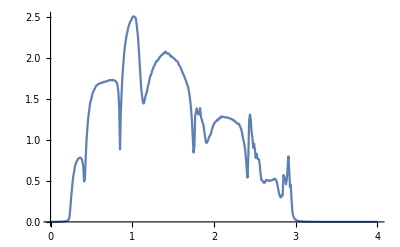

```mathematica
ListPlot[final10,Joined->True]
```

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis36.csv",final6]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis36.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis37.csv",final7]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis37.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis38.csv",final8]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis38.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis39.csv",final9]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis39.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis34.csv",final4]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis34.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv",final5]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis33.csv",final3]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis33.csv

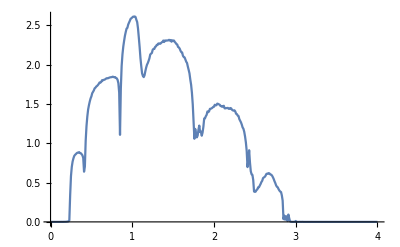

```mathematica
ListPlot[final10,Joined->True]
```

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis210.csv",final10]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis210.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis29.csv",final9]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis29.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis28.csv",final8]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis28.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis24.csv",final4]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis24.csv

```mathematica
Clear[Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,Il1,Ir1,gdd1,grr1,Gnonlocal1,GNON1,Λ];X[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[{{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ2+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ3+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ2+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}];
```

```mathematica
Λ[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-g.T1[1].SL[ω,δ,t,ϵ].T1[1]].g;
Sl12:=Inverse[IdentityMatrix[7]-X[ω,δ,t,ϵ,ϵ2,ϵ3].T2[1].Sl11.T2[1]].X[ω,δ,t,ϵ,ϵ2,ϵ3];
Sl13:=Inverse[IdentityMatrix[7]-g.T1[1].Sl12.T1[1]].g;
Sl14:=Inverse[IdentityMatrix[7]-g.T2[1].Sl13.T2[1]].g;
Sl15:=Inverse[IdentityMatrix[7]-g.T1[1].Sl14.T1[1]].g;
Sl16:=Inverse[IdentityMatrix[7]-g.T2[1].Sl15.T2[1]].g;
Sl17:=Inverse[IdentityMatrix[7]-g.T1[1].Sl16.T1[1]].g;
Sl18:=Inverse[IdentityMatrix[7]-g.T2[1].Sl17.T2[1]].g;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
f7[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis37.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis37.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ7=Table[{b,a,f7[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.109651},{0.05,-1.,0.136644},{0.1,-1.,0.138634},{0.15,-1.,0.131309},{0.2,-1.,0.123079},{0.25,-1.,0.119628},{0.3,-1.,0.116302},{0.35,-1.,0.1202},{0.4,-1.,0.128521},{0.45,-1.,0.135735},22,{1.6,-1.,0.498924},{1.65,-1.,0.513999},{1.7,-1.,0.528769},{1.75,-1.,0.54323},{1.8,-1.,0.55738},{1.85,-1.,0.570955},{1.9,-1.,0.583426},{1.95,-1.,0.59563},{2.,-1.,0.607606}},39,{1}}
 |  |  |  |

```mathematica
A:=A=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis36.csv"]
```

```mathematica
f3[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
Timing[f3[0.1,0.2]]
```

{1.38935,0.000790288}

```mathematica
ρ6=Table[{b,a,f3[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00111905},{0.05,-1.,0.00139715},{0.1,-1.,0.00143353},{0.15,-1.,0.001381},{0.2,-1.,0.00132225},{0.25,-1.,0.00131296},{0.3,-1.,0.00130444},{0.35,-1.,0.00136836},{0.4,-1.,0.00147653},23,{1.6,-1.,0.00559744},{1.65,-1.,0.00576002},{1.7,-1.,0.00591917},{1.75,-1.,0.00607489},{1.8,-1.,0.00622715},{1.85,-1.,0.00637325},{1.9,-1.,0.00650748},{1.95,-1.,0.00663874},{2.,-1.,0.00676745}},39,{1}}
 |  |  |  |

```mathematica
f4[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis34.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis24.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ4:=ρ4=Table[{b,a,f4[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

```mathematica
ρ4
```

Import::nffil: File /home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis34.csv not found during Import.

Part::take: Cannot take positions 1 through 150 in $Failed.

Part::partd: Part specification $Failed⟦1;;150,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

Import::nffil: File /home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis34.csv not found during Import.

Part::take: Cannot take positions 1 through 150 in $Failed.

Part::partd: Part specification $Failed⟦1;;150,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

Import::nffil: File /home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis34.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 150 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1;;150,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
f5[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ5=Table[{b,a,f5[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.122216},{0.05,-1.,0.151272},{0.1,-1.,0.155598},{0.15,-1.,0.15149},{0.2,-1.,0.147098},{0.25,-1.,0.147901},{0.3,-1.,0.148866},{0.35,-1.,0.157231},{0.4,-1.,0.170109},{0.45,-1.,0.181844},{0.5,-1.,0.197558},{0.55,-1.,0.216482},{0.6,-1.,0.236979},{0.65,-1.,0.254573},{0.7,-1.,0.271889},{0.75,-1.,0.290123},{0.8,-1.,0.309095},{0.85,-1.,0.328656},{0.9,-1.,0.348677},{0.95,-1.,0.369034},{1.,-1.,0.389614},{1.05,-1.,0.410311},{1.1,-1.,0.431031},{1.15,-1.,0.451686},{1.2,-1.,0.472204},{1.25,-1.,0.492524},{1.3,-1.,0.512596},{1.35,-1.,0.532382},{1.4,-1.,0.551851},{1.45,-1.,0.570982},{1.5,-1.,0.589761},{1.55,-1.,0.608176},{1.6,-1.,0.62622},{1.65,-1.,0.643888},{1.7,-1.,0.661178},{1.75,-1.,0.678087},{1.8,-1.,0.694615},{1.85,-1.,0.710486},{1.9,-1.,0.725085},{1.95,-1.,0.739353},{2.,-1.,0.753337}},{{0.,-0.95,0.15065},{0.05,-0.95,0.18159},{0.1,-0.95,0.176142},{0.15,-0.95,0.160958},{0.2,-0.95,0.14892},{0.25,-0.95,0.136544},{0.3,-0.95,0.136837},{0.35,-0.95,0.141978},{0.4,-0.95,0.150007},{0.45,-0.95,0.164169},{0.5,-0.95,0.182007},{0.55,-0.95,0.201756},{0.6,-0.95,0.222552},{0.65,-0.95,0.241926},{0.7,-0.95,0.25898},{0.75,-0.95,0.276886},{0.8,-0.95,0.295488},{0.85,-0.95,0.314656},{0.9,-0.95,0.334269},{0.95,-0.95,0.354212},{1.,-0.95,0.374377},{1.05,-0.95,0.394664},{1.1,-0.95,0.414984},{1.15,-0.95,0.435258},{1.2,-0.95,0.455418},{1.25,-0.95,0.475411},{1.3,-0.95,0.49519},{1.35,-0.95,0.514722},{1.4,-0.95,0.533979},{1.45,-0.95,0.552939},{1.5,-0.95,0.571586},{1.55,-0.95,0.589906},{1.6,-0.95,0.607889},{1.65,-0.95,0.625527},{1.7,-0.95,0.642452},{1.75,-0.95,0.658894},{1.8,-0.95,0.67504},{1.85,-0.95,0.69088},{1.9,-0.95,0.706205},{1.95,-0.95,0.720547},{2.,-0.95,0.734614}},{{0.,-0.9,0.204198},{0.05,-0.9,0.225909},{0.1,-0.9,0.200794},{0.15,-0.9,0.166104},{0.2,-0.9,0.136602},{0.25,-0.9,0.123876},{0.3,-0.9,0.118554},{0.35,-0.9,0.121671},{0.4,-0.9,0.13308},{0.45,-0.9,0.149211},{0.5,-0.9,0.167932},{0.55,-0.9,0.188075},{0.6,-0.9,0.208991},{0.65,-0.9,0.230325},{0.7,-0.9,0.247157},{0.75,-0.9,0.264616},{0.8,-0.9,0.282734},{0.85,-0.9,0.301399},{0.9,-0.9,0.320503},{0.95,-0.9,0.339941},{1.,-0.9,0.359614},{1.05,-0.9,0.37943},{1.1,-0.9,0.399306},{1.15,-0.9,0.419171},{1.2,-0.9,0.438963},{1.25,-0.9,0.458632},{1.3,-0.9,0.478136},{1.35,-0.9,0.497439},{1.4,-0.9,0.516514},{1.45,-0.9,0.535336},{1.5,-0.9,0.553885},{1.55,-0.9,0.57159},{1.6,-0.9,0.588878},{1.65,-0.9,0.60594},{1.7,-0.9,0.622753},{1.75,-0.9,0.639299},{1.8,-0.9,0.655564},{1.85,-0.9,0.671535},{1.9,-0.9,0.687203},{1.95,-0.9,0.702284},{2.,-0.9,0.716463}},{{0.,-0.85,0.28461},{0.05,-0.85,0.276263},{0.1,-0.85,0.209175},{0.15,-0.85,0.154159},{0.2,-0.85,0.121181},{0.25,-0.85,0.101923},{0.3,-0.85,0.0977968},{0.35,-0.85,0.104896},{0.4,-0.85,0.118511},{0.45,-0.85,0.135822},{0.5,-0.85,0.155156},{0.55,-0.85,0.175537},{0.6,-0.85,0.196429},{0.65,-0.85,0.217561},{0.7,-0.85,0.236567},{0.75,-0.85,0.253433},{0.8,-0.85,0.270931},{0.85,-0.85,0.28897},{0.9,-0.85,0.307457},{0.95,-0.85,0.326301},{1.,-0.85,0.345411},{1.05,-0.85,0.364704},{1.1,-0.85,0.384105},{1.15,-0.85,0.403547},{1.2,-0.85,0.422972},{1.25,-0.85,0.442329},{1.3,-0.85,0.461577},{1.35,-0.85,0.480676},{1.4,-0.85,0.498682},{1.45,-0.85,0.516497},{1.5,-0.85,0.534202},{1.55,-0.85,0.551761},{1.6,-0.85,0.569139},{1.65,-0.85,0.586311},{1.7,-0.85,0.60325},{1.75,-0.85,0.619938},{1.8,-0.85,0.636356},{1.85,-0.85,0.652492},{1.9,-0.85,0.668333},{1.95,-0.85,0.68387},{2.,-0.85,0.69894}},{{0.,-0.8,0.36578},{0.05,-0.8,0.289088},{0.1,-0.8,0.195462},{0.15,-0.8,0.131889},{0.2,-0.8,0.0938425},{0.25,-0.8,0.0793792},{0.3,-0.8,0.0803701},{0.35,-0.8,0.0904863},{0.4,-0.8,0.105882},{0.45,-0.8,0.124178},{0.5,-0.8,0.143941},{0.55,-0.8,0.164359},{0.6,-0.8,0.185022},{0.65,-0.8,0.205755},{0.7,-0.8,0.226499},{0.75,-0.8,0.243444},{0.8,-0.8,0.26017},{0.85,-0.8,0.277453},{0.9,-0.8,0.295219},{0.95,-0.8,0.313386},{1.,-0.8,0.331874},{1.05,-0.8,0.350608},{1.1,-0.8,0.369514},{1.15,-0.8,0.388528},{1.2,-0.8,0.407436},{1.25,-0.8,0.425114},{1.3,-0.8,0.442936},{1.35,-0.8,0.460832},{1.4,-0.8,0.478744},{1.45,-0.8,0.496618},{1.5,-0.8,0.514409},{1.55,-0.8,0.532076},{1.6,-0.8,0.549583},{1.65,-0.8,0.5669},{1.7,-0.8,0.584},{1.75,-0.8,0.600861},{1.8,-0.8,0.617464},{1.85,-0.8,0.633793},{1.9,-0.8,0.649837},{1.95,-0.8,0.665585},{2.,-0.8,0.68103}},{{0.,-0.75,0.39723},{0.05,-0.75,0.264255},{0.1,-0.75,0.157903},{0.15,-0.75,0.0948872},{0.2,-0.75,0.0670473},{0.25,-0.75,0.0603414},{0.3,-0.75,0.0659879},{0.35,-0.75,0.0788523},{0.4,-0.75,0.095759},{0.45,-0.75,0.114729},{0.5,-0.75,0.134592},{0.55,-0.75,0.154733},{0.6,-0.75,0.174881},{0.65,-0.75,0.194963},{0.7,-0.75,0.214992},{0.75,-0.75,0.234729},{0.8,-0.75,0.250527},{0.85,-0.75,0.266931},{0.9,-0.75,0.28388},{0.95,-0.75,0.301304},{1.,-0.75,0.319127},{1.05,-0.75,0.33652},{1.1,-0.75,0.35311},{1.15,-0.75,0.370148},{1.2,-0.75,0.387535},{1.25,-0.75,0.405182},{1.3,-0.75,0.423009},{1.35,-0.75,0.440946},{1.4,-0.75,0.458929},{1.45,-0.75,0.476901},{1.5,-0.75,0.494814},{1.55,-0.75,0.512622},{1.6,-0.75,0.530289},{1.65,-0.75,0.547781},{1.7,-0.75,0.565069},{1.75,-0.75,0.582131},{1.8,-0.75,0.598946},{1.85,-0.75,0.615496},{1.9,-0.75,0.631769},{1.95,-0.75,0.647754},{2.,-0.75,0.663443}},{{0.,-0.7,0.343933},{0.05,-0.7,0.191462},{0.1,-0.7,0.103028},{0.15,-0.7,0.0605332},{0.2,-0.7,0.0457116},{0.25,-0.7,0.0463423},{0.3,-0.7,0.0560296},{0.35,-0.7,0.0709833},{0.4,-0.7,0.0887668},{0.45,-0.7,0.107834},{0.5,-0.7,0.127297},{0.55,-0.7,0.146735},{0.6,-0.7,0.166016},{0.65,-0.7,0.185161},{0.7,-0.7,0.204249},{0.75,-0.7,0.223361},{0.8,-0.7,0.242057},{0.85,-0.7,0.257475},{0.9,-0.7,0.271643},{0.95,-0.7,0.285939},{1.,-0.7,0.301086},{1.05,-0.7,0.316956},{1.1,-0.7,0.333428},{1.15,-0.7,0.350392},{1.2,-0.7,0.367748},{1.25,-0.7,0.385402},{1.3,-0.7,0.403272},{1.35,-0.7,0.421283},{1.4,-0.7,0.439367},{1.45,-0.7,0.457466},{1.5,-0.7,0.475526},{1.55,-0.7,0.493501},{1.6,-0.7,0.511351},{1.65,-0.7,0.529042},{1.7,-0.7,0.546542},{1.75,-0.7,0.563828},{1.8,-0.7,0.580877},{1.85,-0.7,0.597672},{1.9,-0.7,0.614198},{1.95,-0.7,0.630443},{2.,-0.7,0.646398}},{{0.,-0.65,0.206064},{0.05,-0.65,0.103543},{0.1,-0.65,0.0586058},{0.15,-0.65,0.0376921},{0.2,-0.65,0.0336958},{0.25,-0.65,0.0396256},{0.3,-0.65,0.0517326},{0.35,-0.65,0.0675147},{0.4,-0.65,0.0851856},{0.45,-0.65,0.103568},{0.5,-0.65,0.122011},{0.55,-0.65,0.14026},{0.6,-0.65,0.158301},{0.65,-0.65,0.176229},{0.7,-0.65,0.193764},{0.75,-0.65,0.20832},{0.8,-0.65,0.223631},{0.85,-0.65,0.239648},{0.9,-0.65,0.252859},{0.95,-0.65,0.266928},{1.,-0.65,0.281894},{1.05,-0.65,0.297629},{1.1,-0.65,0.314013},{1.15,-0.65,0.330932},{1.2,-0.65,0.348283},{1.25,-0.65,0.36597},{1.3,-0.65,0.383905},{1.35,-0.65,0.402009},{1.4,-0.65,0.420214},{1.45,-0.65,0.438456},{1.5,-0.65,0.456681},{1.55,-0.65,0.474839},{1.6,-0.65,0.49289},{1.65,-0.65,0.510796},{1.7,-0.65,0.528526},{1.75,-0.65,0.546053},{1.8,-0.65,0.563355},{1.85,-0.65,0.580412},{1.9,-0.65,0.597209},{1.95,-0.65,0.613733},{2.,-0.65,0.629974}},{{0.,-0.6,0.0787893},{0.05,-0.6,0.0469891},{0.1,-0.6,0.0385093},{0.15,-0.6,0.0313503},{0.2,-0.6,0.0330215},{0.25,-0.6,0.0409389},{0.3,-0.6,0.0532634},{0.35,-0.6,0.0683319},{0.4,-0.6,0.0847631},{0.45,-0.6,0.101618},{0.5,-0.6,0.118413},{0.55,-0.6,0.132},{0.6,-0.6,0.144125},{0.65,-0.6,0.157008},{0.7,-0.6,0.170662},{0.75,-0.6,0.185096},{0.8,-0.6,0.200302},{0.85,-0.6,0.216244},{0.9,-0.6,0.232871},{0.95,-0.6,0.248423},{1.,-0.6,0.263218},{1.05,-0.6,0.278831},{1.1,-0.6,0.29514},{1.15,-0.6,0.312027},{1.2,-0.6,0.329384},{1.25,-0.6,0.347111},{1.3,-0.6,0.365118},{1.35,-0.6,0.383324},{1.4,-0.6,0.401655},{1.45,-0.6,0.420047},{1.5,-0.6,0.438443},{1.55,-0.6,0.456793},{1.6,-0.6,0.475052},{1.65,-0.6,0.493183},{1.7,-0.6,0.511152},{1.75,-0.6,0.528932},{1.8,-0.6,0.546498},{1.85,-0.6,0.56383},{1.9,-0.6,0.580911},{1.95,-0.6,0.597728},{2.,-0.6,0.614269}},{{0.,-0.55,0.0261166},{0.05,-0.55,0.0326861},{0.1,-0.55,0.0435387},{0.15,-0.55,0.0404287},{0.2,-0.55,0.0424175},{0.25,-0.55,0.0491484},{0.3,-0.55,0.0596467},{0.35,-0.55,0.071078},{0.4,-0.55,0.0788439},{0.45,-0.55,0.0882635},{0.5,-0.55,0.0986858},{0.55,-0.55,0.10985},{0.6,-0.55,0.121714},{0.65,-0.55,0.134322},{0.7,-0.55,0.147727},{0.75,-0.55,0.16196},{0.8,-0.55,0.17702},{0.85,-0.55,0.192874},{0.9,-0.55,0.209468},{0.95,-0.55,0.226732},{1.,-0.55,0.244588},{1.05,-0.55,0.260899},{1.1,-0.55,0.277126},{1.15,-0.55,0.293974},{1.2,-0.55,0.311329},{1.25,-0.55,0.329089},{1.3,-0.55,0.34716},{1.35,-0.55,0.365459},{1.4,-0.55,0.383911},{1.45,-0.55,0.402448},{1.5,-0.55,0.421012},{1.55,-0.55,0.43955},{1.6,-0.55,0.458017},{1.65,-0.55,0.476373},{1.7,-0.55,0.494583},{1.75,-0.55,0.512619},{1.8,-0.55,0.530454},{1.85,-0.55,0.548066},{1.9,-0.55,0.565439},{1.95,-0.55,0.582555},{2.,-0.55,0.599404}},{{0.,-0.5,0.0322044},{0.05,-0.5,0.04699},{0.1,-0.5,0.0652747},{0.15,-0.5,0.0599003},{0.2,-0.5,0.0492858},{0.25,-0.5,0.0453382},{0.3,-0.5,0.0468254},{0.35,-0.5,0.0520682},{0.4,-0.5,0.0596222},{0.45,-0.5,0.0685362},{0.5,-0.5,0.0783383},{0.55,-0.5,0.0888846},{0.6,-0.5,0.100196},{0.65,-0.5,0.112344},{0.7,-0.5,0.125389},{0.75,-0.5,0.139354},{0.8,-0.5,0.15423},{0.85,-0.5,0.169973},{0.9,-0.5,0.186519},{0.95,-0.5,0.20379},{1.,-0.5,0.221702},{1.05,-0.5,0.240165},{1.1,-0.5,0.259092},{1.15,-0.5,0.277112},{1.2,-0.5,0.294438},{1.25,-0.5,0.312205},{1.3,-0.5,0.330316},{1.35,-0.5,0.348686},{1.4,-0.5,0.367237},{1.45,-0.5,0.385902},{1.5,-0.5,0.404617},{1.55,-0.5,0.42333},{1.6,-0.5,0.441994},{1.65,-0.5,0.460566},{1.7,-0.5,0.47901},{1.75,-0.5,0.497296},{1.8,-0.5,0.515396},{1.85,-0.5,0.533286},{1.9,-0.5,0.550948},{1.95,-0.5,0.568365},{2.,-0.5,0.585522}},{{0.,-0.45,0.0471731},{0.05,-0.45,0.0476288},{0.1,-0.45,0.0537438},{0.15,-0.45,0.0469663},{0.2,-0.45,0.0367944},{0.25,-0.45,0.0325691},{0.3,-0.45,0.0332291},{0.35,-0.45,0.0373218},{0.4,-0.45,0.0435949},{0.45,-0.45,0.0512535},{0.5,-0.45,0.0599292},{0.55,-0.45,0.0695262},{0.6,-0.45,0.080073},{0.65,-0.45,0.0916251},{0.7,-0.45,0.104218},{0.75,-0.45,0.117851},{0.8,-0.45,0.132492},{0.85,-0.45,0.14808},{0.9,-0.45,0.164538},{0.95,-0.45,0.181777},{1.,-0.45,0.199704},{1.05,-0.45,0.218226},{1.1,-0.45,0.23725},{1.15,-0.45,0.256688},{1.2,-0.45,0.276459},{1.25,-0.45,0.296484},{1.3,-0.45,0.314907},{1.35,-0.45,0.33331},{1.4,-0.45,0.351925},{1.45,-0.45,0.370684},{1.5,-0.45,0.389523},{1.55,-0.45,0.408385},{1.6,-0.45,0.427222},{1.65,-0.45,0.44599},{1.7,-0.45,0.464651},{1.75,-0.45,0.483171},{1.8,-0.45,0.501522},{1.85,-0.45,0.519678},{1.9,-0.45,0.53762},{1.95,-0.45,0.555328},{2.,-0.45,0.572788}},{{0.,-0.4,0.0325751},{0.05,-0.4,0.0345762},{0.1,-0.4,0.0404986},{0.15,-0.4,0.0445101},{0.2,-0.4,0.0326069},{0.25,-0.4,0.0263279},{0.3,-0.4,0.0247883},{0.35,-0.4,0.0266947},{0.4,-0.4,0.0309401},{0.45,-0.4,0.0368304},{0.5,-0.4,0.0440377},{0.55,-0.4,0.0524573},{0.6,-0.4,0.0620805},{0.65,-0.4,0.0729167},{0.7,-0.4,0.0849581},{0.75,-0.4,0.0981692},{0.8,-0.4,0.112489},{0.85,-0.4,0.127839},{0.9,-0.4,0.144127},{0.95,-0.4,0.161254},{1.,-0.4,0.179121},{1.05,-0.4,0.197629},{1.1,-0.4,0.216683},{1.15,-0.4,0.23619},{1.2,-0.4,0.256066},{1.25,-0.4,0.276232},{1.3,-0.4,0.296614},{1.35,-0.4,0.317144},{1.4,-0.4,0.337762},{1.45,-0.4,0.357095},{1.5,-0.4,0.376014},{1.55,-0.4,0.394987},{1.6,-0.4,0.413962},{1.65,-0.4,0.432894},{1.7,-0.4,0.451742},{1.75,-0.4,0.47047},{1.8,-0.4,0.489049},{1.85,-0.4,0.507451},{1.9,-0.4,0.525653},{1.95,-0.4,0.543636},{2.,-0.4,0.561382}},{{0.,-0.35,0.029996},{0.05,-0.35,0.030312},{0.1,-0.35,0.0336757},{0.15,-0.35,0.0411874},{0.2,-0.35,0.0353855},{0.25,-0.35,0.0260392},{0.3,-0.35,0.021466},{0.35,-0.35,0.0205448},{0.4,-0.35,0.0222985},{0.45,-0.35,0.026093},{0.5,-0.35,0.0315935},{0.55,-0.35,0.0386475},{0.6,-0.35,0.0471832},{0.65,-0.35,0.0571501},{0.7,-0.35,0.068491},{0.75,-0.35,0.0811333},{0.8,-0.35,0.0949897},{0.85,-0.35,0.109962},{0.9,-0.35,0.125947},{0.95,-0.35,0.142836},{1.,-0.35,0.160525},{1.05,-0.35,0.178909},{1.1,-0.35,0.197889},{1.15,-0.35,0.217372},{1.2,-0.35,0.237269},{1.25,-0.35,0.257498},{1.3,-0.35,0.277983},{1.35,-0.35,0.298653},{1.4,-0.35,0.319445},{1.45,-0.35,0.340301},{1.5,-0.35,0.361168},{1.55,-0.35,0.381998},{1.6,-0.35,0.402481},{1.65,-0.35,0.421534},{1.7,-0.35,0.44053},{1.75,-0.35,0.459431},{1.8,-0.35,0.478205},{1.85,-0.35,0.496821},{1.9,-0.35,0.515256},{1.95,-0.35,0.533488},{2.,-0.35,0.551497}},{{0.,-0.3,0.0332002},{0.05,-0.3,0.03102},{0.1,-0.3,0.0309708},{0.15,-0.3,0.0343412},{0.2,-0.3,0.0411126},{0.25,-0.3,0.0318197},{0.3,-0.3,0.0237965},{0.35,-0.3,0.019704},{0.4,-0.3,0.018688},{0.45,-0.3,0.0201485},{0.5,-0.3,0.02372},{0.55,-0.3,0.0291876},{0.6,-0.3,0.0364122},{0.65,-0.3,0.0452846},{0.7,-0.3,0.0557018},{0.75,-0.3,0.0675577},{0.8,-0.3,0.080742},{0.85,-0.3,0.0951403},{0.9,-0.3,0.110637},{0.95,-0.3,0.127118},{1.,-0.3,0.144471},{1.05,-0.3,0.162587},{1.1,-0.3,0.181363},{1.15,-0.3,0.200702},{1.2,-0.3,0.22051},{1.25,-0.3,0.240703},{1.3,-0.3,0.261201},{1.35,-0.3,0.281929},{1.4,-0.3,0.302822},{1.45,-0.3,0.323817},{1.5,-0.3,0.344857},{1.55,-0.3,0.365893},{1.6,-0.3,0.386879},{1.65,-0.3,0.407773},{1.7,-0.3,0.428539},{1.75,-0.3,0.449145},{1.8,-0.3,0.469209},{1.85,-0.3,0.488002},{1.9,-0.3,0.506634},{1.95,-0.3,0.52508},{2.,-0.3,0.543321}},{{0.,-0.25,0.0397191},{0.05,-0.25,0.0351836},{0.1,-0.25,0.0316624},{0.15,-0.25,0.0306939},{0.2,-0.25,0.0326394},{0.25,-0.25,0.0368195},{0.3,-0.25,0.0324205},{0.35,-0.25,0.0250126},{0.4,-0.25,0.0210466},{0.45,-0.25,0.0199551},{0.5,-0.25,0.0213455},{0.55,-0.25,0.0249504},{0.6,-0.25,0.0305754},{0.65,-0.25,0.0380634},{0.7,-0.25,0.0472741},{0.75,-0.25,0.058074},{0.8,-0.25,0.0703327},{0.85,-0.25,0.0839217},{0.9,-0.25,0.0987146},{0.95,-0.25,0.114589},{1.,-0.25,0.131424},{1.05,-0.25,0.149107},{1.1,-0.25,0.167529},{1.15,-0.25,0.186586},{1.2,-0.25,0.206182},{1.25,-0.25,0.226226},{1.3,-0.25,0.246633},{1.35,-0.25,0.267326},{1.4,-0.25,0.288233},{1.45,-0.25,0.309287},{1.5,-0.25,0.33043},{1.55,-0.25,0.351605},{1.6,-0.25,0.372765},{1.65,-0.25,0.393865},{1.7,-0.25,0.414864},{1.75,-0.25,0.435728},{1.8,-0.25,0.456425},{1.85,-0.25,0.476928},{1.9,-0.25,0.497212},{1.95,-0.25,0.517258},{2.,-0.25,0.537028}},{{0.,-0.2,0.0483624},{0.05,-0.2,0.0420967},{0.1,-0.2,0.0355929},{0.15,-0.2,0.0306699},{0.2,-0.2,0.028124},{0.25,-0.2,0.0277754},{0.3,-0.2,0.029025},{0.35,-0.2,0.0313466},{0.4,-0.2,0.0296026},{0.45,-0.2,0.0257844},{0.5,-0.2,0.0247569},{0.55,-0.2,0.0262248},{0.6,-0.2,0.0299591},{0.65,-0.2,0.03577},{0.7,-0.2,0.0434899},{0.75,-0.2,0.0529641},{0.8,-0.2,0.0640453},{0.85,-0.2,0.0765917},{0.9,-0.2,0.0904662},{0.95,-0.2,0.105537},{1.,-0.2,0.121676},{1.05,-0.2,0.138762},{1.1,-0.2,0.156679},{1.15,-0.2,0.175318},{1.2,-0.2,0.194576},{1.25,-0.2,0.214355},{1.3,-0.2,0.234566},{1.35,-0.2,0.255126},{1.4,-0.2,0.275957},{1.45,-0.2,0.296989},{1.5,-0.2,0.318156},{1.55,-0.2,0.3394},{1.6,-0.2,0.360668},{1.65,-0.2,0.38191},{1.7,-0.2,0.403085},{1.75,-0.2,0.424152},{1.8,-0.2,0.445079},{1.85,-0.2,0.465833},{1.9,-0.2,0.48639},{1.95,-0.2,0.506724},{2.,-0.2,0.526817}},{{0.,-0.15,0.0578769},{0.05,-0.15,0.0507836},{0.1,-0.15,0.0421925},{0.15,-0.15,0.0341657},{0.2,-0.15,0.0279036},{0.25,-0.15,0.0236877},{0.3,-0.15,0.0213074},{0.35,-0.15,0.0204702},{0.4,-0.15,0.0209924},{0.45,-0.15,0.0228191},{0.5,-0.15,0.0259777},{0.55,-0.15,0.0305258},{0.6,-0.15,0.0341747},{0.65,-0.15,0.0381039},{0.7,-0.15,0.0441263},{0.75,-0.15,0.0520727},{0.8,-0.15,0.061783},{0.85,-0.15,0.0731043},{0.9,-0.15,0.0858896},{0.95,-0.15,0.0999974},{1.,-0.15,0.115292},{1.05,-0.15,0.131644},{1.1,-0.15,0.148929},{1.15,-0.15,0.167032},{1.2,-0.15,0.185841},{1.25,-0.15,0.205253},{1.3,-0.15,0.225173},{1.35,-0.15,0.24551},{1.4,-0.15,0.266181},{1.45,-0.15,0.287111},{1.5,-0.15,0.308229},{1.55,-0.15,0.329473},{1.6,-0.15,0.350782},{1.65,-0.15,0.372107},{1.7,-0.15,0.393398},{1.75,-0.15,0.414614},{1.8,-0.15,0.435717},{1.85,-0.15,0.456673},{1.9,-0.15,0.477453},{1.95,-0.15,0.498032},{2.,-0.15,0.518385}},{{0.,-0.1,0.0664125},{0.05,-0.1,0.0594876},{0.1,-0.1,0.0499462},{0.15,-0.1,0.03998},{0.2,-0.1,0.0310844},{0.25,-0.1,0.0239138},{0.3,-0.1,0.0185911},{0.35,-0.1,0.0150433},{0.4,-0.1,0.0131874},{0.45,-0.1,0.0129846},{0.5,-0.1,0.0144331},{0.55,-0.1,0.0175454},{0.6,-0.1,0.0223282},{0.65,-0.1,0.028772},{0.7,-0.1,0.0368462},{0.75,-0.1,0.0465002},{0.8,-0.1,0.0576653},{0.85,-0.1,0.0702582},{0.9,-0.1,0.0841853},{0.95,-0.1,0.0977467},{1.,-0.1,0.112106},{1.05,-0.1,0.127635},{1.1,-0.1,0.144203},{1.15,-0.1,0.161686},{1.2,-0.1,0.179967},{1.25,-0.1,0.198936},{1.3,-0.1,0.21849},{1.35,-0.1,0.238533},{1.4,-0.1,0.258977},{1.45,-0.1,0.27974},{1.5,-0.1,0.300747},{1.55,-0.1,0.321929},{1.6,-0.1,0.343223},{1.65,-0.1,0.364573},{1.7,-0.1,0.385927},{1.75,-0.1,0.40724},{1.8,-0.1,0.42847},{1.85,-0.1,0.44958},{1.9,-0.1,0.470538},{1.95,-0.1,0.491315},{2.,-0.1,0.511886}},{{0.,-0.05,0.071875},{0.05,-0.05,0.0660353},{0.1,-0.05,0.0567319},{0.15,-0.05,0.0461162},{0.2,-0.05,0.0358252},{0.25,-0.05,0.0267746},{0.3,-0.05,0.0193598},{0.35,-0.05,0.0137147},{0.4,-0.05,0.00987903},{0.45,-0.05,0.00786987},{0.5,-0.05,0.00769967},{0.55,-0.05,0.0093738},{0.6,-0.05,0.012884},{0.65,-0.05,0.0182042},{0.7,-0.05,0.0252889},{0.75,-0.05,0.0340748},{0.8,-0.05,0.0444826},{0.85,-0.05,0.0564206},{0.9,-0.05,0.0697875},{0.95,-0.05,0.0844757},{1.,-0.05,0.100374},{1.05,-0.05,0.117369},{1.1,-0.05,0.13535},{1.15,-0.05,0.154205},{1.2,-0.05,0.173828},{1.25,-0.05,0.194116},{1.3,-0.05,0.214424},{1.35,-0.05,0.23413},{1.4,-0.05,0.254302},{1.45,-0.05,0.274853},{1.5,-0.05,0.295702},{1.55,-0.05,0.316778},{1.6,-0.05,0.338012},{1.65,-0.05,0.359343},{1.7,-0.05,0.380716},{1.75,-0.05,0.402082},{1.8,-0.05,0.423396},{1.85,-0.05,0.444618},{1.9,-0.05,0.465712},{1.95,-0.05,0.486648},{2.,-0.05,0.507397}},{{0.,0.,0.0729138},{0.05,0.,0.0688358},{0.1,0.,0.0607852},{0.15,0.,0.0506988},{0.2,0.,0.0402024},{0.25,0.,0.0303606},{0.3,0.,0.0217738},{0.35,0.,0.0147594},{0.4,0.,0.00948834},{0.45,0.,0.00605921},{0.5,0.,0.00452966},{0.55,0.,0.00492763},{0.6,0.,0.00725474},{0.65,0.,0.011488},{0.7,0.,0.0175821},{0.75,0.,0.0254717},{0.8,0.,0.0350754},{0.85,0.,0.0462983},{0.9,0.,0.0590363},{0.95,0.,0.073178},{1.,0.,0.0886087},{1.05,0.,0.105212},{1.1,0.,0.12287},{1.15,0.,0.141471},{1.2,0.,0.160902},{1.25,0.,0.181057},{1.3,0.,0.201835},{1.35,0.,0.223138},{1.4,0.,0.244876},{1.45,0.,0.266966},{1.5,0.,0.289329},{1.55,0.,0.311892},{1.6,0.,0.33459},{1.65,0.,0.356366},{1.7,0.,0.377728},{1.75,0.,0.399115},{1.8,0.,0.420481},{1.85,0.,0.441781},{1.9,0.,0.462979},{1.95,0.,0.484039},{2.,0.,0.504932}},{{0.,0.05,0.0696272},{0.05,0.05,0.0675938},{0.1,0.05,0.0614187},{0.15,0.05,0.0526987},{0.2,0.05,0.0429298},{0.25,0.05,0.033223},{0.3,0.05,0.0243109},{0.35,0.05,0.0166555},{0.4,0.05,0.0105482},{0.45,0.05,0.00617625},{0.5,0.05,0.00365813},{0.55,0.05,0.00306239},{0.6,0.05,0.00441749},{0.65,0.05,0.00771832},{0.7,0.05,0.0129313},{0.75,0.05,0.0199992},{0.8,0.05,0.0288455},{0.85,0.05,0.0393784},{0.9,0.05,0.0514949},{0.95,0.05,0.065084},{1.,0.05,0.0800299},{1.05,0.05,0.0962143},{1.1,0.05,0.113519},{1.15,0.05,0.131826},{1.2,0.05,0.151023},{1.25,0.05,0.170999},{1.3,0.05,0.191648},{1.35,0.05,0.212872},{1.4,0.05,0.234577},{1.45,0.05,0.256673},{1.5,0.05,0.279081},{1.55,0.05,0.301725},{1.6,0.05,0.324534},{1.65,0.05,0.347446},{1.7,0.05,0.370404},{1.75,0.05,0.393353},{1.8,0.05,0.416249},{1.85,0.05,0.439047},{1.9,0.05,0.46171},{1.95,0.05,0.483436},{2.,0.05,0.504448}},{{0.,0.1,0.0633022},{0.05,0.1,0.0631471},{0.1,0.1,0.0589867},{0.15,0.1,0.0520225},{0.2,0.1,0.0435424},{0.25,0.1,0.0346175},{0.3,0.1,0.0260392},{0.35,0.1,0.0183631},{0.4,0.1,0.0119746},{0.45,0.1,0.00713957},{0.5,0.1,0.00403857},{0.55,0.1,0.00278697},{0.6,0.1,0.00344838},{0.65,0.1,0.00604398},{0.7,0.1,0.0105599},{0.75,0.1,0.0169536},{0.8,0.1,0.0251593},{0.85,0.1,0.0350931},{0.9,0.1,0.0466575},{0.95,0.1,0.0597449},{1.,0.1,0.0742416},{1.05,0.1,0.0900299},{1.1,0.1,0.106991},{1.15,0.1,0.125008},{1.2,0.1,0.143964},{1.25,0.1,0.163747},{1.3,0.1,0.18425},{1.35,0.1,0.205371},{1.4,0.1,0.227013},{1.45,0.1,0.249086},{1.5,0.1,0.271505},{1.55,0.1,0.294192},{1.6,0.1,0.317075},{1.65,0.1,0.340088},{1.7,0.1,0.363171},{1.75,0.1,0.386268},{1.8,0.1,0.409331},{1.85,0.1,0.432315},{1.9,0.1,0.455181},{1.95,0.1,0.477892},{2.,0.1,0.500417}},{{0.,0.15,0.0555568},{0.05,0.15,0.0567777},{0.1,0.15,0.0543793},{0.15,0.15,0.0491683},{0.2,0.15,0.0421839},{0.25,0.15,0.0343928},{0.3,0.15,0.0265784},{0.35,0.15,0.019338},{0.4,0.15,0.0131152},{0.45,0.15,0.00823476},{0.5,0.15,0.00492913},{0.55,0.15,0.0033575},{0.6,0.15,0.00361929},{0.65,0.15,0.00576458},{0.7,0.15,0.00980262},{0.75,0.15,0.0157091},{0.8,0.15,0.0234328},{0.85,0.15,0.0329009},{0.9,0.15,0.0440242},{0.95,0.15,0.0567014},{1.,0.15,0.0708231},{1.05,0.15,0.0862746},{1.1,0.15,0.102939},{1.15,0.15,0.120698},{1.2,0.15,0.139438},{1.25,0.15,0.159044},{1.3,0.15,0.179408},{1.35,0.15,0.200427},{1.4,0.15,0.222002},{1.45,0.15,0.24404},{1.5,0.15,0.266456},{1.55,0.15,0.289168},{1.6,0.15,0.312102},{1.65,0.15,0.335191},{1.7,0.15,0.358372},{1.75,0.15,0.381588},{1.8,0.15,0.404787},{1.85,0.15,0.427924},{1.9,0.15,0.450958},{1.95,0.15,0.47385},{2.,0.15,0.496568}},{{0.,0.2,0.0476724},{0.05,0.2,0.0496398},{0.1,0.2,0.048545},{0.15,0.2,0.0448382},{0.2,0.2,0.0393014},{0.25,0.2,0.0327567},{0.3,0.2,0.0259297},{0.35,0.2,0.0194135},{0.4,0.2,0.013675},{0.45,0.2,0.00907349},{0.5,0.2,0.00587809},{0.55,0.2,0.00428281},{0.6,0.2,0.00441817},{0.65,0.2,0.00636122},{0.7,0.2,0.0101441},{0.75,0.2,0.0157615},{0.8,0.2,0.023178},{0.85,0.2,0.0323333},{0.9,0.2,0.0431486},{0.95,0.2,0.0555304},{1.,0.2,0.0693753},{1.05,0.2,0.084573},{1.1,0.2,0.10101},{1.15,0.2,0.11857},{1.2,0.2,0.137139},{1.25,0.2,0.156605},{1.3,0.2,0.176858},{1.35,0.2,0.197795},{1.4,0.2,0.219315},{1.45,0.2,0.241326},{1.5,0.2,0.263739},{1.55,0.2,0.286473},{1.6,0.2,0.309451},{1.65,0.2,0.332605},{1.7,0.2,0.355869},{1.75,0.2,0.379185},{1.8,0.2,0.402502},{1.85,0.2,0.42577},{1.9,0.2,0.448947},{1.95,0.2,0.471994},{2.,0.2,0.494878}},{{0.,0.25,0.0404112},{0.05,0.25,0.0425433},{0.1,0.25,0.0422554},{0.15,0.25,0.0397006},{0.2,0.25,0.03542},{0.25,0.25,0.0300752},{0.3,0.25,0.0243032},{0.35,0.25,0.0186593},{0.4,0.25,0.0136044},{0.45,0.25,0.00950932},{0.5,0.25,0.00666334},{0.55,0.25,0.0052838},{0.6,0.25,0.0055248},{0.65,0.25,0.00748555},{0.7,0.25,0.0112182},{0.75,0.25,0.0167353},{0.8,0.25,0.0240164},{0.85,0.25,0.0330142},{0.9,0.25,0.0436602},{0.95,0.25,0.0558699},{1.,0.25,0.0695467},{1.05,0.25,0.0845858},{1.1,0.25,0.100877},{1.15,0.25,0.118309},{1.2,0.25,0.136768},{1.25,0.25,0.156144},{1.3,0.25,0.176328},{1.35,0.25,0.197216},{1.4,0.25,0.218709},{1.45,0.25,0.240712},{1.5,0.25,0.263137},{1.55,0.25,0.285901},{1.6,0.25,0.308927},{1.65,0.25,0.332144},{1.7,0.25,0.355487},{1.75,0.25,0.378897},{1.8,0.25,0.402319},{1.85,0.25,0.425705},{1.9,0.25,0.44901},{1.95,0.25,0.472195},{2.,0.25,0.495224}},{{0.,0.3,0.0341325},{0.05,0.3,0.0359797},{0.1,0.3,0.0360608},{0.15,0.3,0.0342984},{0.2,0.3,0.0310252},{0.25,0.3,0.0267459},{0.3,0.3,0.0219945},{0.35,0.3,0.0172679},{0.4,0.3,0.0129995},{0.45,0.3,0.00955303},{0.5,0.3,0.00722299},{0.55,0.3,0.0062385},{0.6,0.3,0.00676875},{0.65,0.3,0.00892908},{0.7,0.3,0.0127875},{0.75,0.3,0.0183714},{0.8,0.3,0.0256737},{0.85,0.3,0.0346589},{0.9,0.3,0.0452688},{0.95,0.3,0.0574273},{1.,0.3,0.071045},{1.05,0.3,0.086023},{1.1,0.3,0.102256},{1.15,0.3,0.119635},{1.2,0.3,0.138051},{1.25,0.3,0.157395},{1.3,0.3,0.177559},{1.35,0.3,0.19844},{1.4,0.3,0.21994},{1.45,0.3,0.241963},{1.5,0.3,0.264422},{1.55,0.3,0.287233},{1.6,0.3,0.310319},{1.65,0.3,0.333608},{1.7,0.3,0.357034},{1.75,0.3,0.380537},{1.8,0.3,0.404062},{1.85,0.3,0.427559},{1.9,0.3,0.450983},{1.95,0.3,0.474295},{2.,0.3,0.497457}},{{0.,0.35,0.0289664},{0.05,0.35,0.0302223},{0.1,0.35,0.0303274},{0.15,0.35,0.0290389},{0.2,0.35,0.0265201},{0.25,0.35,0.023134},{0.3,0.35,0.0193106},{0.35,0.35,0.0154777},{0.4,0.35,0.0120281},{0.45,0.35,0.00930474},{0.5,0.35,0.00759509},{0.55,0.35,0.00713003},{0.6,0.35,0.00808573},{0.65,0.35,0.0105874},{0.7,0.35,0.0147142},{0.75,0.35,0.0205048},{0.8,0.35,0.027963},{0.85,0.35,0.0370635},{0.9,0.35,0.0477571},{0.95,0.35,0.0599757},{1.,0.35,0.0736367},{1.05,0.35,0.0886468},{1.1,0.35,0.104906},{1.15,0.35,0.122308},{1.2,0.35,0.140748},{1.25,0.35,0.160119},{1.3,0.35,0.180315},{1.35,0.35,0.201235},{1.4,0.35,0.22278},{1.45,0.35,0.244856},{1.5,0.35,0.267376},{1.55,0.35,0.290256},{1.6,0.35,0.313419},{1.65,0.35,0.336792},{1.7,0.35,0.36031},{1.75,0.35,0.383911},{1.8,0.35,0.407541},{1.85,0.35,0.431149},{1.9,0.35,0.45469},{1.95,0.35,0.478122},{2.,0.35,0.50141}},{{0.,0.4,0.0249362},{0.05,0.4,0.0254133},{0.1,0.4,0.0252897},{0.15,0.4,0.0242139},{0.2,0.4,0.0222191},{0.25,0.4,0.0195474},{0.3,0.4,0.0165315},{0.35,0.4,0.013528},{0.4,0.4,0.0108816},{0.45,0.4,0.00890578},{0.5,0.4,0.00787194},{0.55,0.4,0.00800458},{0.6,0.4,0.00947986},{0.65,0.4,0.0124271},{0.7,0.4,0.016932},{0.75,0.4,0.0230408},{0.8,0.4,0.0307656},{0.85,0.4,0.040089},{0.9,0.4,0.0509693},{0.95,0.4,0.0633454},{1.,0.4,0.0771407},{1.05,0.4,0.0922673},{1.1,0.4,0.108629},{1.15,0.4,0.126126},{1.2,0.4,0.144654},{1.25,0.4,0.164109},{1.3,0.4,0.184388},{1.35,0.4,0.205391},{1.4,0.4,0.22702},{1.45,0.4,0.249184},{1.5,0.4,0.271793},{1.55,0.4,0.294766},{1.6,0.4,0.318025},{1.65,0.4,0.341499},{1.7,0.4,0.365121},{1.75,0.4,0.38883},{1.8,0.4,0.41257},{1.85,0.4,0.436292},{1.9,0.4,0.459949},{1.95,0.4,0.4835},{2.,0.4,0.506909}},{{0.,0.45,0.0220219},{0.05,0.45,0.021619},{0.1,0.45,0.0210914},{0.15,0.45,0.0200243},{0.2,0.45,0.0183563},{0.25,0.45,0.0162309},{0.3,0.45,0.0138944},{0.35,0.45,0.0116346},{0.4,0.45,0.00974602},{0.45,0.45,0.00850738},{0.5,0.45,0.00816817},{0.55,0.45,0.00894035},{0.6,0.45,0.0109945},{0.65,0.45,0.014459},{0.7,0.45,0.0194219},{0.75,0.45,0.0259338},{0.8,0.45,0.034012},{0.85,0.45,0.043645},{0.9,0.45,0.054797},{0.95,0.45,0.0674123},{1.,0.45,0.0814198},{1.05,0.45,0.0967362},{1.1,0.45,0.11327},{1.15,0.45,0.130924},{1.2,0.45,0.149597},{1.25,0.45,0.169188},{1.3,0.45,0.189597},{1.35,0.45,0.210725},{1.4,0.45,0.232476},{1.45,0.45,0.254759},{1.5,0.45,0.277487},{1.55,0.45,0.300577},{1.6,0.45,0.323953},{1.65,0.45,0.347543},{1.7,0.45,0.371282},{1.75,0.45,0.395109},{1.8,0.45,0.418967},{1.85,0.45,0.442808},{1.9,0.45,0.466583},{1.95,0.45,0.490254},{2.,0.45,0.513781}},{{0.,0.5,0.0201851},{0.05,0.5,0.0188597},{0.1,0.5,0.0178127},{0.15,0.5,0.0166008},{0.2,0.5,0.0150976},{0.25,0.5,0.0133694},{0.3,0.5,0.0115881},{0.35,0.5,0.00997864},{0.4,0.5,0.00878581},{0.45,0.5,0.00825168},{0.5,0.5,0.00860009},{0.55,0.5,0.0100263},{0.6,0.5,0.0126909},{0.65,0.5,0.0167176},{0.7,0.5,0.022193},{0.75,0.5,0.0291691},{0.8,0.5,0.0376658},{0.85,0.5,0.0476754},{0.9,0.5,0.0591662},{0.95,0.5,0.072087},{1.,0.5,0.0863707},{1.05,0.5,0.101938},{1.1,0.5,0.118701},{1.15,0.5,0.136566},{1.2,0.5,0.155434},{1.25,0.5,0.175208},{1.3,0.5,0.195789},{1.35,0.5,0.217079},{1.4,0.5,0.238986},{1.45,0.5,0.261417},{1.5,0.5,0.284289},{1.55,0.5,0.307519},{1.6,0.5,0.331031},{1.65,0.5,0.354754},{1.7,0.5,0.378624},{1.75,0.5,0.402578},{1.8,0.5,0.426563},{1.85,0.5,0.450527},{1.9,0.5,0.474425},{1.95,0.5,0.498216},{2.,0.5,0.521862}},{{0.,0.55,0.0193776},{0.05,0.55,0.0171254},{0.1,0.55,0.0154884},{0.15,0.55,0.0140202},{0.2,0.55,0.0125532},{0.25,0.55,0.0110947},{0.3,0.55,0.00975516},{0.35,0.55,0.00870329},{0.4,0.55,0.00813696},{0.45,0.55,0.00826148},{0.5,0.55,0.00927331},{0.55,0.55,0.0113483},{0.6,0.55,0.0146341},{0.65,0.55,0.0192466},{0.7,0.55,0.0252681},{0.75,0.55,0.0327493},{0.8,0.55,0.0417108},{0.85,0.55,0.0521464},{0.9,0.55,0.0640271},{0.95,0.55,0.0773047},{1.,0.55,0.0919152},{1.05,0.55,0.107783},{1.1,0.55,0.124822},{1.15,0.55,0.142942},{1.2,0.55,0.162048},{1.25,0.55,0.182043},{1.3,0.55,0.20283},{1.35,0.55,0.224315},{1.4,0.55,0.246406},{1.45,0.55,0.269013},{1.5,0.55,0.292051},{1.55,0.55,0.31544},{1.6,0.55,0.339105},{1.65,0.55,0.362977},{1.7,0.55,0.386988},{1.75,0.55,0.411081},{1.8,0.55,0.435199},{1.85,0.55,0.459292},{1.9,0.55,0.483316},{1.95,0.55,0.507229},{2.,0.55,0.530995}},{{0.,0.6,0.0195426},{0.05,0.6,0.0163843},{0.1,0.6,0.0141198},{0.15,0.6,0.0123177},{0.2,0.6,0.0107876},{0.25,0.6,0.00949366},{0.3,0.6,0.00849611},{0.35,0.6,0.00791485},{0.4,0.6,0.00790472},{0.45,0.6,0.00863558},{0.5,0.6,0.0102761},{0.55,0.6,0.0129812},{0.6,0.6,0.0168838},{0.65,0.6,0.0220893},{0.7,0.6,0.0286741},{0.75,0.6,0.0366851},{0.8,0.6,0.0461414},{0.85,0.6,0.0570372},{0.9,0.6,0.0693446},{0.95,0.6,0.083017},{1.,0.6,0.0979928},{1.05,0.6,0.114198},{1.1,0.6,0.131551},{1.15,0.6,0.149961},{1.2,0.6,0.169338},{1.25,0.6,0.189585},{1.3,0.6,0.210608},{1.35,0.6,0.232315},{1.4,0.6,0.254614},{1.45,0.6,0.277417},{1.5,0.6,0.300641},{1.55,0.6,0.324207},{1.6,0.6,0.34804},{1.65,0.6,0.37207},{1.7,0.6,0.396235},{1.75,0.6,0.420473},{1.8,0.6,0.444731},{1.85,0.6,0.468959},{1.9,0.6,0.493112},{1.95,0.6,0.517149},{2.,0.6,0.541035}},{{0.,0.65,0.0206162},{0.05,0.65,0.016588},{0.1,0.65,0.0136831},{0.15,0.65,0.0114967},{0.2,0.65,0.00982945},{0.25,0.65,0.00861552},{0.3,0.65,0.00787496},{0.35,0.65,0.00768597},{0.4,0.65,0.00816475},{0.45,0.65,0.00944784},{0.5,0.65,0.0116766},{0.55,0.65,0.0149848},{0.6,0.65,0.0194889},{0.65,0.65,0.025283},{0.7,0.65,0.0324353},{0.75,0.65,0.0409876},{0.8,0.65,0.0509561},{0.85,0.65,0.0623337},{0.9,0.65,0.0750922},{0.95,0.65,0.0891861},{1.,0.65,0.104555},{1.05,0.65,0.121126},{1.1,0.65,0.138819},{1.15,0.65,0.157548},{1.2,0.65,0.17722},{1.25,0.65,0.197744},{1.3,0.65,0.219026},{1.35,0.65,0.240975},{1.4,0.65,0.263501},{1.45,0.65,0.286517},{1.5,0.65,0.309942},{1.55,0.65,0.333698},{1.6,0.65,0.35771},{1.65,0.65,0.381911},{1.7,0.65,0.406236},{1.75,0.65,0.430627},{1.8,0.65,0.45503},{1.85,0.65,0.479396},{1.9,0.65,0.50368},{1.95,0.65,0.527842},{2.,0.65,0.551847}},{{0.,0.7,0.0225281},{0.05,0.7,0.0176764},{0.1,0.7,0.0141361},{0.15,0.7,0.0115363},{0.2,0.7,0.00967935},{0.25,0.7,0.00847941},{0.3,0.7,0.0079253},{0.35,0.7,0.00806013},{0.4,0.7,0.00896587},{0.45,0.7,0.0107484},{0.5,0.7,0.013523},{0.55,0.7,0.0174021},{0.6,0.7,0.0224858},{0.65,0.7,0.0288555},{0.7,0.7,0.0365702},{0.75,0.7,0.0456653},{0.8,0.7,0.0561529},{0.85,0.7,0.0680234},{0.9,0.7,0.0812477},{0.95,0.7,0.0957797},{1.,0.7,0.11156},{1.05,0.7,0.128516},{1.1,0.7,0.14657},{1.15,0.7,0.165635},{1.2,0.7,0.185622},{1.25,0.7,0.20644},{1.3,0.7,0.227997},{1.35,0.7,0.250204},{1.4,0.7,0.272971},{1.45,0.7,0.296214},{1.5,0.7,0.319852},{1.55,0.7,0.343807},{1.6,0.7,0.368008},{1.65,0.7,0.392385},{1.7,0.7,0.416877},{1.75,0.7,0.441425},{1.8,0.7,0.465976},{1.85,0.7,0.490483},{1.9,0.7,0.514899},{1.95,0.7,0.539187},{2.,0.7,0.563311}},{{0.,0.75,0.0252038},{0.05,0.75,0.0195811},{0.1,0.75,0.0154234},{0.15,0.75,0.0123981},{0.2,0.75,0.0103164},{0.25,0.75,0.00908071},{0.3,0.75,0.00865604},{0.35,0.75,0.00905634},{0.4,0.75,0.0103337},{0.45,0.75,0.012566},{0.5,0.75,0.0158442},{0.55,0.75,0.0202602},{0.6,0.75,0.0258973},{0.65,0.75,0.0328238},{0.7,0.75,0.041089},{0.75,0.75,0.050721},{0.8,0.75,0.0617268},{0.85,0.75,0.0740934},{0.9,0.75,0.0877897},{0.95,0.75,0.102769},{1.,0.75,0.11897},{1.05,0.75,0.136323},{1.1,0.75,0.154749},{1.15,0.75,0.174164},{1.2,0.75,0.194478},{1.25,0.75,0.215603},{1.3,0.75,0.237447},{1.35,0.75,0.259922},{1.4,0.75,0.282941},{1.45,0.75,0.30642},{1.5,0.75,0.330278},{1.55,0.75,0.35444},{1.6,0.75,0.378834},{1.65,0.75,0.403393},{1.7,0.75,0.428055},{1.75,0.75,0.452763},{1.8,0.75,0.477465},{1.85,0.75,0.502112},{1.9,0.75,0.526662},{1.95,0.75,0.551074},{2.,0.75,0.575315}},{{0.,0.8,0.0285661},{0.05,0.8,0.0222287},{0.1,0.8,0.0174811},{0.15,0.8,0.0140311},{0.2,0.8,0.011704},{0.25,0.8,0.0103967},{0.3,0.8,0.0100567},{0.35,0.8,0.0106738},{0.4,0.8,0.0122745},{0.45,0.8,0.0149114},{0.5,0.8,0.0186529},{0.55,0.8,0.0235712},{0.6,0.8,0.0297334},{0.65,0.8,0.0371947},{0.7,0.8,0.0459939},{0.75,0.8,0.0561513},{0.8,0.8,0.0676683},{0.85,0.8,0.0805278},{0.9,0.8,0.094696},{0.95,0.8,0.110124},{1.,0.8,0.126752},{1.05,0.8,0.144507},{1.1,0.8,0.163312},{1.15,0.8,0.183083},{1.2,0.8,0.203732},{1.25,0.8,0.22517},{1.3,0.8,0.247308},{1.35,0.8,0.270058},{1.4,0.8,0.293335},{1.45,0.8,0.317054},{1.5,0.8,0.341137},{1.55,0.8,0.36551},{1.6,0.8,0.390101},{1.65,0.8,0.414844},{1.7,0.8,0.439678},{1.75,0.8,0.464548},{1.8,0.8,0.4894},{1.85,0.8,0.514188},{1.9,0.8,0.538869},{1.95,0.8,0.563405},{2.,0.8,0.58776}},{{0.,0.85,0.0325373},{0.05,0.85,0.0255434},{0.1,0.85,0.02024},{0.15,0.85,0.0163761},{0.2,0.85,0.0137945},{0.25,0.85,0.0123915},{0.3,0.85,0.0121019},{0.35,0.85,0.0128964},{0.4,0.85,0.014779},{0.45,0.85,0.0177803},{0.5,0.85,0.0219476},{0.55,0.85,0.0273348},{0.6,0.85,0.0339933},{0.65,0.85,0.0419652},{0.7,0.85,0.0512789},{0.75,0.85,0.0619467},{0.8,0.85,0.0739636},{0.85,0.85,0.087308},{0.9,0.85,0.101943},{0.95,0.85,0.117818},{1.,0.85,0.13487},{1.05,0.85,0.153028},{1.1,0.85,0.172214},{1.15,0.85,0.192344},{1.2,0.85,0.21333},{1.25,0.85,0.235085},{1.3,0.85,0.25752},{1.35,0.85,0.280548},{1.4,0.85,0.304084},{1.45,0.85,0.328046},{1.5,0.85,0.352357},{1.55,0.85,0.376941},{1.6,0.85,0.40173},{1.65,0.85,0.426658},{1.7,0.85,0.451664},{1.75,0.85,0.476694},{1.8,0.85,0.501696},{1.85,0.85,0.526623},{1.9,0.85,0.551434},{1.95,0.85,0.57609},{2.,0.85,0.600557}},{{0.,0.9,0.0370412},{0.05,0.9,0.0294493},{0.1,0.9,0.0236288},{0.15,0.9,0.0193693},{0.2,0.9,0.0165332},{0.25,0.9,0.0150199},{0.3,0.9,0.0147558},{0.35,0.9,0.0156961},{0.4,0.9,0.017826},{0.45,0.9,0.0211562},{0.5,0.9,0.0257153},{0.55,0.9,0.0315398},{0.6,0.9,0.0386662},{0.65,0.9,0.047124},{0.7,0.9,0.0569311},{0.75,0.9,0.0680916},{0.8,0.9,0.0805941},{0.85,0.9,0.094412},{0.9,0.9,0.109505},{0.95,0.9,0.125819},{1.,0.9,0.143292},{1.05,0.9,0.161849},{1.1,0.9,0.181413},{1.15,0.9,0.2019},{1.2,0.9,0.223223},{1.25,0.9,0.245294},{1.3,0.9,0.268025},{1.35,0.9,0.291331},{1.4,0.9,0.315127},{1.45,0.9,0.339332},{1.5,0.9,0.363869},{1.55,0.9,0.388665},{1.6,0.9,0.41365},{1.65,0.9,0.438761},{1.7,0.9,0.463938},{1.75,0.9,0.489126},{1.8,0.9,0.514275},{1.85,0.9,0.539339},{1.9,0.9,0.564276},{1.95,0.9,0.589049},{2.,0.9,0.613625}},{{0.,0.95,0.0420042},{0.05,0.95,0.0338721},{0.1,0.95,0.0275761},{0.15,0.95,0.0229446},{0.2,0.95,0.0198611},{0.25,0.95,0.0182309},{0.3,0.95,0.0179752},{0.35,0.95,0.019037},{0.4,0.95,0.0213854},{0.45,0.95,0.0250142},{0.5,0.95,0.0299344},{0.55,0.95,0.0361669},{0.6,0.95,0.043734},{0.65,0.95,0.0526529},{0.7,0.95,0.0629317},{0.75,0.95,0.0745659},{0.8,0.95,0.0875375},{0.85,0.95,0.101815},{0.9,0.95,0.117354},{0.95,0.95,0.134099},{1.,0.95,0.151983},{1.05,0.95,0.170934},{1.1,0.95,0.190871},{1.15,0.95,0.21171},{1.2,0.95,0.233365},{1.25,0.95,0.255749},{1.3,0.95,0.278774},{1.35,0.95,0.302355},{1.4,0.95,0.326408},{1.45,0.95,0.350854},{1.5,0.95,0.375615},{1.55,0.95,0.400619},{1.6,0.95,0.425799},{1.65,0.95,0.45109},{1.7,0.95,0.476434},{1.75,0.95,0.501778},{1.8,0.95,0.52707},{1.85,0.95,0.552267},{1.9,0.95,0.577327},{1.95,0.95,0.602213},{2.,0.95,0.626893}},{{0.,1.,0.0473566},{0.05,1.,0.038741},{0.1,1.,0.0320123},{0.15,1.,0.0270362},{0.2,1.,0.0237179},{0.25,1.,0.0219704},{0.3,1.,0.0217122},{0.35,1.,0.0228772},{0.4,1.,0.0254211},{0.45,1.,0.0293223},{0.5,1.,0.0345767},{0.55,1.,0.0411904},{0.6,1.,0.0491725},{0.65,1.,0.0585287},{0.7,1.,0.0692572},{0.75,1.,0.0813454},{0.8,1.,0.0947688},{0.85,1.,0.109491},{0.9,1.,0.125463},{0.95,1.,0.142626},{1.,1.,0.160912},{1.05,1.,0.180246},{1.1,1.,0.200548},{1.15,1.,0.221733},{1.2,1.,0.243715},{1.25,1.,0.266406},{1.3,1.,0.28972},{1.35,1.,0.313571},{1.4,1.,0.337877},{1.45,1.,0.362559},{1.5,1.,0.387539},{1.55,1.,0.412748},{1.6,1.,0.438118},{1.65,1.,0.463585},{1.7,1.,0.489093},{1.75,1.,0.514587},{1.8,1.,0.540019},{1.85,1.,0.565344},{1.9,1.,0.590522},{1.95,1.,0.615518},{2.,1.,0.640298}}}

```mathematica
Import["home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv"]
```

Import::nffil: File home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv not found during Import.

$Failed

```mathematica
final=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv"]
```

{{0.,0.0000785423},{0.01,0.0000563178},{0.02,0.0000581984},{0.03,0.0000926024},{0.04,0.000151375},{0.05,0.000235299},{0.06,0.000359412},{0.07,0.000522002},{0.08,0.000685811},{0.09,0.00088733},{0.1,0.00112794},{0.11,0.00147916},{0.12,0.00180434},{0.13,0.00236111},{0.14,0.00291633},{0.15,0.00356057},{0.16,0.00446829},{0.17,0.00564524},{0.18,0.00737292},{0.19,0.00944421},{0.2,0.0125519},{0.21,0.0180039},{0.22,0.0277782},{0.23,0.0570865},{0.24,0.136666},{0.25,0.305206},{0.26,0.431298},{0.27,0.5448},{0.28,0.620741},{0.29,0.682188},{0.3,0.732131},{0.31,0.76631},{0.32,0.770264},{0.33,0.798146},{0.34,0.801062},{0.35,0.804189},{0.36,0.805365},{0.37,0.797798},{0.38,0.78346},{0.39,0.757732},{0.4,0.696573},{0.41,0.563849},{0.42,0.583321},{0.43,0.783299},{0.44,0.977039},{0.45,1.12343},{0.46,1.21875},{0.47,1.30904},{0.48,1.36816},{0.49,1.42923},{0.5,1.47388},{0.51,1.51576},{0.52,1.54125},{0.53,1.57543},{0.54,1.58786},{0.55,1.61089},{0.56,1.63},{0.57,1.65244},{0.58,1.66493},{0.59,1.67702},{0.6,1.69209},{0.61,1.69811},{0.62,1.71044},{0.63,1.71752},{0.64,1.71898},{0.65,1.72907},{0.66,1.73395},{0.67,1.74416},{0.68,1.74852},{0.69,1.75114},{0.7,1.7564},{0.71,1.75339},{0.72,1.76225},{0.73,1.76119},{0.74,1.75843},{0.75,1.76443},{0.76,1.76},{0.77,1.758},{0.78,1.75497},{0.79,1.75716},{0.8,1.74553},{0.81,1.73387},{0.82,1.70403},{0.83,1.64819},{0.84,1.51344},{0.85,1.0913},{0.86,1.48558},{0.87,1.70447},{0.88,1.84545},{0.89,1.97458},{0.9,2.09527},{0.91,2.16731},{0.92,2.20648},{0.93,2.27344},{0.94,2.30362},{0.95,2.34145},{0.96,2.38009},{0.97,2.41992},{0.98,2.44319},{0.99,2.46595},{1.,2.48875},{1.01,2.51214},{1.02,2.51957},{1.03,2.51804},{1.04,2.49218},{1.05,2.45488},{1.06,2.38658},{1.07,2.26929},{1.08,2.11894},{1.09,1.9267},{1.1,1.73209},{1.11,1.58784},{1.12,1.46973},{1.13,1.44014},{1.14,1.41093},{1.15,1.44224},{1.16,1.49633},{1.17,1.58431},{1.18,1.63253},{1.19,1.68753},{1.2,1.736},{1.21,1.78202},{1.22,1.80923},{1.23,1.83474},{1.24,1.85545},{1.25,1.87173},{1.26,1.8822},{1.27,1.90492},{1.28,1.91157},{1.29,1.94507},{1.3,1.94445},{1.31,1.97102},{1.32,1.98562},{1.33,2.00172},{1.34,2.00727},{1.35,2.02276},{1.36,2.02937},{1.37,2.03776},{1.38,2.03517},{1.39,2.03372},{1.4,2.03811},{1.41,2.02115},{1.42,2.01107},{1.43,2.01097},{1.44,1.99976},{1.45,1.98715},{1.46,1.98209},{1.47,1.99573},{1.48,1.97645},{1.49,1.97619},{1.5,1.96901},{1.51,1.96349},{1.52,1.95728},{1.53,1.95742},{1.54,1.95294},{1.55,1.94641},{1.56,1.94977},{1.57,1.94278},{1.58,1.93672},{1.59,1.92809},{1.6,1.92054},{1.61,1.89675},{1.62,1.88627},{1.63,1.85773},{1.64,1.84194},{1.65,1.81453},{1.66,1.78863},{1.67,1.74447},{1.68,1.70298},{1.69,1.63803},{1.7,1.59193},{1.71,1.53857},{1.72,1.43552},{1.73,1.31206},{1.74,1.12933},{1.75,0.917682},{1.76,1.06891},{1.77,1.53559},{1.78,1.22657},{1.79,1.37117},{1.8,1.34382},{1.81,1.19241},{1.82,1.19955},{1.83,1.1447},{1.84,1.11211},{1.85,1.20683},{1.86,1.127},{1.87,1.01843},{1.88,0.923955},{1.89,0.881881},{1.9,0.876388},{1.91,0.923554},{1.92,0.969831},{1.93,1.01451},{1.94,1.05182},{1.95,1.07486},{1.96,1.10836},{1.97,1.1299},{1.98,1.15324},{1.99,1.16208},{2.,1.17777},{2.01,1.18809},{2.02,1.19748},{2.03,1.22556},{2.04,1.23492},{2.05,1.24102},{2.06,1.25607},{2.07,1.26276},{2.08,1.28249},{2.09,1.29276},{2.1,1.2854},{2.11,1.30065},{2.12,1.29063},{2.13,1.29202},{2.14,1.29397},{2.15,1.29263},{2.16,1.27558},{2.17,1.27424},{2.18,1.25308},{2.19,1.24523},{2.2,1.227},{2.21,1.21569},{2.22,1.20781},{2.23,1.20045},{2.24,1.19744},{2.25,1.19582},{2.26,1.19293},{2.27,1.19029},{2.28,1.17037},{2.29,1.15528},{2.3,1.16031},{2.31,1.11552},{2.32,1.10288},{2.33,1.05735},{2.34,1.01575},{2.35,0.954442},{2.36,0.889945},{2.37,0.823744},{2.38,0.753475},{2.39,0.686541},{2.4,0.575519},{2.41,0.555886},{2.42,0.965822},{2.43,1.29179},{2.44,1.21461},{2.45,1.10696},{2.46,0.893143},{2.47,0.828781},{2.48,0.779472},{2.49,0.786666},{2.5,0.783318},{2.51,0.654955},{2.52,0.618084},{2.53,0.639575},{2.54,0.649882},{2.55,0.598836},{2.56,0.609293},{2.57,0.511517},{2.58,0.440164},{2.59,0.454871},{2.6,0.469215},{2.61,0.467673},{2.62,0.464217},{2.63,0.49082},{2.64,0.490979},{2.65,0.51297},{2.66,0.521721},{2.67,0.535947},{2.68,0.526865},{2.69,0.546179},{2.7,0.550198},{2.71,0.548943},{2.72,0.555418},{2.73,0.548537},{2.74,0.540405},{2.75,0.523481},{2.76,0.489646},{2.77,0.466783},{2.78,0.432697},{2.79,0.400953},{2.8,0.380332},{2.81,0.362777},{2.82,0.34106},{2.83,0.317162},{2.84,0.302687},{2.85,0.43987},{2.86,0.381896},{2.87,0.562089},{2.88,0.604143},{2.89,0.645165},{2.9,0.824214},{2.91,0.710091},{2.92,0.449603},{2.93,0.442017},{2.94,0.344131},{2.95,0.153637},{2.96,0.094992},{2.97,0.0465752},{2.98,0.0434158},{2.99,0.0256847},{3.,0.0189701},{3.01,0.0144779},{3.02,0.0121714},{3.03,0.0092458},{3.04,0.00807393},{3.05,0.00670984},{3.06,0.00563596},{3.07,0.00450126},{3.08,0.00384262},{3.09,0.00351378},{3.1,0.00304336},{3.11,0.00265099},{3.12,0.00216552},{3.13,0.00190426},{3.14,0.00192024},{3.15,0.00170232},{3.16,0.00133371},{3.17,0.0012724},{3.18,0.00114014},{3.19,0.000958193},{3.2,0.00085949},{3.21,0.000779592},{3.22,0.000702993},{3.23,0.000685714},{3.24,0.000623752},{3.25,0.000530787},{3.26,0.000484628},{3.27,0.000441771},{3.28,0.000435363},{3.29,0.000371612},{3.3,0.000367474},{3.31,0.00031458},{3.32,0.00029094},{3.33,0.000267841},{3.34,0.000248344},{3.35,0.000261856},{3.36,0.000212493},{3.37,0.000212189},{3.38,0.000183662},{3.39,0.000170375},{3.4,0.000159005},{3.41,0.000147823},{3.42,0.000137895},{3.43,0.000129045},{3.44,0.000129517},{3.45,0.000112794},{3.46,0.000105589},{3.47,0.000098926},{3.48,0.0000927569},{3.49,0.0000870398},{3.5,0.0000817363},{3.51,0.0000825379},{3.52,0.0000721033},{3.53,0.0000678563},{3.54,0.000063902},{3.55,0.0000602171},{3.56,0.0000567805},{3.57,0.0000576803},{3.58,0.0000505767},{3.59,0.0000514403},{3.6,0.0000486199},{3.61,0.0000459795},{3.62,0.000043506},{3.63,0.0000411872},{3.64,0.0000415178},{3.65,0.0000369703},{3.66,0.0000350526},{3.67,0.0000309197},{3.68,0.0000293045},{3.69,0.0000299606},{3.7,0.0000264287},{3.71,0.0000251151},{3.72,0.0000239056},{3.73,0.0000227095},{3.74,0.0000216328},{3.75,0.0000235931},{3.76,0.000019586},{3.77,0.0000214057},{3.78,0.000020401},{3.79,0.0000182546},{3.8,0.0000174093},{3.81,0.000016609},{3.82,0.0000158511},{3.83,0.000015133},{3.84,0.00001342},{3.85,0.0000128326},{3.86,0.0000122631},{3.87,0.0000117228},{3.88,0.0000112097},{3.89,0.0000115375},{3.9,0.0000102595},{3.91,9.81208×10^-6},{3.92,0.0000101186},{3.93,9.00024×10^-6},{3.94,8.62956×10^-6},{3.95,8.27038×10^-6},{3.96,8.53151×10^-6},{3.97,8.18093×10^-6},{3.98,7.84685×10^-6},{3.99,7.5284×10^-6},{4.,6.71096×10^-6}}

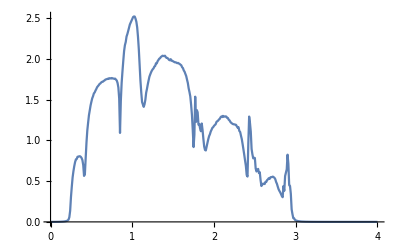

```mathematica
ListPlot[final,Joined->True]
```

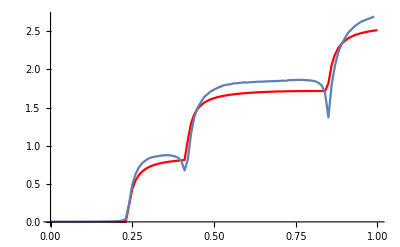

```mathematica
Show[ListLinePlot[Table[{ω,Λ[ω,0.001,1,0,0.7,0.7]},{ω,Range[0,1,0.01]}],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis37.csv"][[;;100]]],PlotRange->All]
```

```mathematica
2η[0,1.18,2]+η[0,0.7,4]-AvgE[0.7,3]
```

0.337029

```mathematica
f[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{final10[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- final10[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ3[b_]:=Table[{b,a,f[b,a]},{a,Range[0.5,1.5,0.05]}]
```

```mathematica
ρ3[0.7]
```

{{0.7,0.5,0.000525175},{0.7,0.55,0.000493675},{0.7,0.6,0.000460387},{0.7,0.65,0.000426579},{0.7,0.7,0.000393352},{0.7,0.75,0.000361626},{0.7,0.8,0.000332138},{0.7,0.85,0.000305452},{0.7,0.9,0.000281974},{0.7,0.95,0.000261971},{0.7,1.,0.000245595},{0.7,1.05,0.000232897},{0.7,1.1,0.000223853},{0.7,1.15,0.000218375},{0.7,1.2,0.00021633},{0.7,1.25,0.000217548},{0.7,1.3,0.000221838},{0.7,1.35,0.000228996},{0.7,1.4,0.000238807},{0.7,1.45,0.000251056},{0.7,1.5,0.000265531}}

```mathematica
Min/@Transpose[ρ3[0.7]]
```

{0.7,0.5,0.00021633}

```mathematica
rr3=Join[ρ3[-1],ρ3[-9/10],ρ3[-4/5],ρ3[-7/10],ρ3[-3/5],ρ3[-1/2],ρ3[-2/5],ρ3[-3/10],ρ3[-1/5],ρ3[-1/10],ρ3[0],ρ3[1/10],ρ3[1/5],ρ3[3/10],ρ3[2/5],ρ3[1/2],ρ3[3/5],ρ3[7/10],ρ3[4/5],ρ3[9/10],ρ3[1]]
```

{{-1,-1.,0.00520468},{-1,-0.95,0.0141548},{-1,-0.9,0.0935865},{-1,-0.85,0.416149},{-1,-0.8,1.30833},{-1,-0.75,3.28967},{-1,-0.7,7.11731},{-1,-0.65,13.8427},{-1,-0.6,24.8819},{-1,-0.55,42.1025},{-1,-0.5,67.9318},{-1,-0.45,105.491},{-1,-0.4,158.765},{-1,-0.35,232.813},{-1,-0.3,334.034},{-1,-0.25,470.511},{-1,-0.2,652.443},{-1,-0.15,892.699},{-1,-0.1,1207.54},{-1,-0.05,1617.55},{-1,0.,2148.85},{-1,0.05,2834.69},{-1,0.1,3717.57},{-1,0.15,4851.96},{-1,0.2,6308.01},{-1,0.25,8176.42},{-1,0.3,10575.},{-1,0.35,13657.2},{-1,0.4,17624.4},{-1,0.45,22741.9},{-1,0.5,29363.1},{-1,0.55,37964.4},{-1,0.6,49202.7},{-1,0.65,64010.9},{-1,0.7,83771.2},{-1,0.75,110635.},{-1,0.8,148135.},{-1,0.85,202391.},{-1,0.9,284560.},{-1,0.95,416098.},{-1,1.,640805.},{-9/10,-1.,0.0934501},{-9/10,-0.95,0.0135301},{-9/10,-0.9,0.00395066},{-9/10,-0.85,0.0131731},{-9/10,-0.8,0.10448},{-9/10,-0.75,0.491229},{-9/10,-0.7,1.57961},{-9/10,-0.65,4.02187},{-9/10,-0.6,8.77777},{-9/10,-0.55,17.1941},{-9/10,-0.5,31.1049},{-9/10,-0.45,52.9577},{-9/10,-0.4,85.9741},{-9/10,-0.35,134.353},{-9/10,-0.3,203.529},{-9/10,-0.25,300.509},{-9/10,-0.2,434.301},{-9/10,-0.15,616.475},{-9/10,-0.1,861.89},{-9/10,-0.05,1189.65},{-9/10,0.,1624.39},{-9/10,0.05,2197.87},{-9/10,0.1,2951.3},{-9/10,0.15,3938.18},{-9/10,0.2,5228.3},{-9/10,0.25,6913.01},{-9/10,0.3,9112.37},{-9/10,0.35,11984.9},{-9/10,0.4,15741.6},{-9/10,0.45,20665.6},{-9/10,0.5,27143.1},{-9/10,0.55,35713.6},{-9/10,0.6,47155.3},{-9/10,0.65,62640.8},{-9/10,0.7,84027.2},{-9/10,0.75,114415.},{-9/10,0.8,159254.},{-9/10,0.85,228637.},{-9/10,0.9,342292.},{-9/10,0.95,541285.},{-9/10,1.,917851.},{-4/5,-1.,1.30798},{-4/5,-0.95,0.450659},{-4/5,-0.9,0.104374},{-4/5,-0.85,0.0129117},{-4/5,-0.8,0.00310593},{-4/5,-0.75,0.0128731},{-4/5,-0.7,0.120611},{-4/5,-0.65,0.594622},{-4/5,-0.6,1.95005},{-4/5,-0.55,5.0231},{-4/5,-0.5,11.0588},{-4/5,-0.45,21.8268},{-4/5,-0.4,39.7701},{-4/5,-0.35,68.1971},{-4/5,-0.3,111.53},{-4/5,-0.25,175.628},{-4/5,-0.2,268.21},{-4/5,-0.15,399.41},{-4/5,-0.1,582.509},{-4/5,-0.05,834.909},{-4/5,0.,1179.43},{-4/5,0.05,1646.03},{-4/5,0.1,2274.14},{-4/5,0.15,3115.76},{-4/5,0.2,4239.7},{-4/5,0.25,5737.32},{-4/5,0.3,7730.54},{-4/5,0.35,10383.2},{-4/5,0.4,13918.},{-4/5,0.45,18642.6},{-4/5,0.5,24993.7},{-4/5,0.55,33612.7},{-4/5,0.6,45485.1},{-4/5,0.65,62201.9},{-4/5,0.7,86468.6},{-4/5,0.75,123128.},{-4/5,0.8,181311.},{-4/5,0.85,279243.},{-4/5,0.9,455785.},{-4/5,0.95,800793.},{-4/5,1.,1.54405×10^6},{-7/10,-1.,7.11517},{-7/10,-0.95,3.62744},{-7/10,-0.9,1.57928},{-7/10,-0.85,0.538616},{-7/10,-0.8,0.120553},{-7/10,-0.75,0.0129968},{-7/10,-0.7,0.00263452},{-7/10,-0.65,0.0133151},{-7/10,-0.6,0.144345},{-7/10,-0.55,0.74028},{-7/10,-0.5,2.47014},{-7/10,-0.45,6.43431},{-7/10,-0.4,14.2955},{-7/10,-0.35,28.4548},{-7/10,-0.3,52.2838},{-7/10,-0.25,90.4313},{-7/10,-0.2,149.23},{-7/10,-0.15,237.24},{-7/10,-0.1,365.971},{-7/10,-0.05,550.862},{-7/10,0.,812.59},{-7/10,0.05,1178.85},{-7/10,0.1,1686.76},{-7/10,0.15,2386.15},{-7/10,0.2,3344.13},{-7/10,0.25,4651.45},{-7/10,0.3,6431.76},{-7/10,0.35,8855.64},{-7/10,0.4,12162.9},{-7/10,0.45,16700.},{-7/10,0.5,22987.2},{-7/10,0.55,31840.8},{-7/10,0.6,44608.3},{-7/10,0.65,63629.9},{-7/10,0.7,93183.8},{-7/10,0.75,141521.},{-7/10,0.8,225534.},{-7/10,0.85,382340.},{-7/10,0.9,700880.},{-7/10,0.95,1.41863×10^6},{-7/10,1.,3.26329×10^6},{-3/5,-1.,24.8751},{-3/5,-0.95,15.3852},{-3/5,-0.9,8.77539},{-3/5,-0.85,4.48068},{-3/5,-0.8,1.94974},{-3/5,-0.75,0.660987},{-3/5,-0.7,0.144312},{-3/5,-0.65,0.0138761},{-3/5,-0.6,0.00253055},{-3/5,-0.55,0.0146425},{-3/5,-0.5,0.179647},{-3/5,-0.45,0.951827},{-3/5,-0.4,3.22623},{-3/5,-0.35,8.49951},{-3/5,-0.3,19.0751},{-3/5,-0.25,38.3457},{-3/5,-0.2,71.1748},{-3/5,-0.15,124.414},{-3/5,-0.1,207.609},{-3/5,-0.05,333.953},{-3/5,0.,521.607},{-3/5,0.05,795.495},{-3/5,0.1,1189.8},{-3/5,0.15,1751.45},{-3/5,0.2,2545.09},{-3/5,0.25,3660.48},{-3/5,0.3,5223.8},{-3/5,0.35,7416.15},{-3/5,0.4,10505.3},{-3/5,0.45,14903.1},{-3/5,0.5,21272.2},{-3/5,0.55,30734.},{-3/5,0.6,45284.8},{-3/5,0.65,68668.4},{-3/5,0.7,108308.},{-3/5,0.75,179888.},{-3/5,0.8,319174.},{-3/5,0.85,615709.},{-3/5,0.9,1.32164×10^6},{-3/5,0.95,3.26204×10^6},{-3/5,1.,9.71423×10^6},{-1/2,-1.,67.9162},{-1/2,-0.95,47.0833},{-1/2,-0.9,31.0972},{-1/2,-0.85,19.3099},{-1/2,-0.8,11.0561},{-1/2,-0.75,5.66423},{-1/2,-0.7,2.46981},{-1/2,-0.65,0.835796},{-1/2,-0.6,0.179634},{-1/2,-0.55,0.015757},{-1/2,-0.5,0.00275006},{-1/2,-0.45,0.0171459},{-1/2,-0.4,0.233551},{-1/2,-0.35,1.27126},{-1/2,-0.3,4.37358},{-1/2,-0.25,11.6625},{-1/2,-0.2,26.4785},{-1/2,-0.15,53.8582},{-1/2,-0.1,101.198},{-1/2,-0.05,179.175},{-1/2,0.,303.037},{-1/2,0.05,494.405},{-1/2,0.1,783.852},{-1/2,0.15,1214.64},{-1/2,0.2,1848.39},{-1/2,0.25,2773.94},{-1/2,0.3,4122.24},{-1/2,0.35,6092.32},{-1/2,0.4,8999.09},{-1/2,0.45,13364.5},{-1/2,0.5,20097.7},{-1/2,0.55,30866.2},{-1/2,0.6,48896.},{-1/2,0.65,80807.8},{-1/2,0.7,141152.},{-1/2,0.75,264656.},{-1/2,0.8,543117.},{-1/2,0.85,1.25261×10^6},{-1/2,0.9,3.37299×10^6},{-1/2,0.95,1.11979×10^7},{-1/2,1.,4.82671×10^7},{-2/5,-1.,158.735},{-2/5,-0.95,118.682},{-2/5,-0.9,85.9568},{-2/5,-0.85,59.8883},{-2/5,-0.8,39.7617},{-2/5,-0.75,24.8242},{-2/5,-0.7,14.2925},{-2/5,-0.65,7.36241},{-2/5,-0.6,3.22585},{-2/5,-0.55,1.09435},{-2/5,-0.5,0.233562},{-2/5,-0.45,0.0190511},{-2/5,-0.4,0.00319127},{-2/5,-0.35,0.0214159},{-2/5,-0.3,0.319121},{-2/5,-0.25,1.77685},{-2/5,-0.2,6.20402},{-2/5,-0.15,16.7656},{-2/5,-0.1,38.5763},{-2/5,-0.05,79.5584},{-2/5,0.,151.674},{-2/5,0.05,272.714},{-2/5,0.1,468.967},{-2/5,0.15,779.321},{-2/5,0.2,1261.9},{-2/5,0.25,2005.4},{-2/5,0.3,3149.4},{-2/5,0.35,4922.65},{-2/5,0.4,7717.88},{-2/5,0.45,12244.},{-2/5,0.5,19849.6},{-2/5,0.55,33248.},{-2/5,0.6,58253.8},{-2/5,0.65,108288.},{-2/5,0.7,217260.},{-2/5,0.75,481072.},{-2/5,0.8,1.2128×10^6},{-2/5,0.85,3.64114×10^6},{-2/5,0.9,1.37935×10^7},{-2/5,0.95,6.57601×10^7},{-2/5,1.,2.21224×10^8},{-3/10,-1.,333.983},{-3/10,-0.95,263.605},{-3/10,-0.9,203.496},{-3/10,-0.85,153.027},{-3/10,-0.8,111.511},{-3/10,-0.75,78.1972},{-3/10,-0.7,52.2747},{-3/10,-0.65,32.8739},{-3/10,-0.6,19.0719},{-3/10,-0.55,9.9024},{-3/10,-0.5,4.37315},{-3/10,-0.45,1.4937},{-3/10,-0.4,0.319147},{-3/10,-0.35,0.0246065},{-3/10,-0.3,0.00375166},{-3/10,-0.25,0.0286736},{-3/10,-0.2,0.461529},{-3/10,-0.15,2.62033},{-3/10,-0.1,9.2894},{-3/10,-0.05,25.4845},{-3/10,0.,59.5832},{-3/10,0.05,125.062},{-3/10,0.1,243.245},{-3/10,0.15,447.869},{-3/10,0.2,793.083},{-3/10,0.25,1368.26},{-3/10,0.3,2326.7},{-3/10,0.35,3943.84},{-3/10,0.4,6739.98},{-3/10,0.45,11752.6},{-3/10,0.5,21177.},{-3/10,0.55,39984.1},{-3/10,0.6,80384.4},{-3/10,0.65,175526.},{-3/10,0.7,427496.},{-3/10,0.75,1.20579×10^6},{-3/10,0.8,4.14945×10^6},{-3/10,0.85,1.82171×10^7},{-3/10,0.9,8.41357×10^7},{-3/10,0.95,1.29426×10^8},{-3/10,1.,4.54542×10^7},{-1/5,-1.,652.363},{-1/5,-0.95,536.535},{-1/5,-0.9,434.246},{-1/5,-0.85,344.986},{-1/5,-0.8,268.175},{-1/5,-0.75,203.16},{-1/5,-0.7,149.211},{-1/5,-0.65,105.512},{-1/5,-0.6,71.1653},{-1/5,-0.55,45.179},{-1/5,-0.5,26.4751},{-1/5,-0.45,13.8927},{-1/5,-0.4,6.20354},{-1/5,-0.35,2.14224},{-1/5,-0.3,0.46155},{-1/5,-0.25,0.0341784},{-1/5,-0.2,0.00430077},{-1/5,-0.15,0.0414955},{-1/5,-0.1,0.712292},{-1/5,-0.05,4.12075},{-1/5,0.,14.889},{-1/5,0.05,41.7661},{-1/5,0.1,100.369},{-1/5,0.15,218.172},{-1/5,0.2,444.114},{-1/5,0.25,868.059},{-1/5,0.3,1662.11},{-1/5,0.35,3172.5},{-1/5,0.4,6135.2},{-1/5,0.45,12215.3},{-1/5,0.5,25467.3},{-1/5,0.55,56686.8},{-1/5,0.6,138024.},{-1/5,0.65,379921.},{-1/5,0.7,1.23765×10^6},{-1/5,0.75,5.03355×10^6},{-1/5,0.8,2.46303×10^7},{-1/5,0.85,7.33761×10^7},{-1/5,0.9,4.30121×10^7},{-1/5,0.95,1.3033×10^7},{-1/5,1.,4.87538×10^6},{-1/10,-1.,1207.42},{-1/10,-0.95,1026.16},{-1/10,-0.9,861.807},{-1/10,-0.85,714.035},{-1/10,-0.8,582.452},{-1/10,-0.75,466.599},{-1/10,-0.7,365.936},{-1/10,-0.65,279.84},{-1/10,-0.6,207.589},{-1/10,-0.55,148.355},{-1/10,-0.5,101.189},{-1/10,-0.45,65.0046},{-1/10,-0.4,38.5731},{-1/10,-0.35,20.5114},{-1/10,-0.3,9.28892},{-1/10,-0.25,3.25601},{-1/10,-0.2,0.712312},{-1/10,-0.15,0.0516841},{-1/10,-0.1,0.00470975},{-1/10,-0.05,0.0662324},{-1/10,0.,1.20378},{-1/10,0.05,7.19007},{-1/10,0.1,27.0945},{-1/10,0.15,80.3603},{-1/10,0.2,207.78},{-1/10,0.25,496.545},{-1/10,0.3,1140.36},{-1/10,0.35,2592.11},{-1/10,0.4,5979.42},{-1/10,0.45,14337.4},{-1/10,0.5,36678.4},{-1/10,0.55,103357.},{-1/10,0.6,334661.},{-1/10,0.65,1.31299×10^6},{-1/10,0.7,6.36585×10^6},{-1/10,0.75,2.69786×10^7},{-1/10,0.8,2.97902×10^7},{-1/10,0.85,1.03304×10^7},{-1/10,0.9,3.60861×10^6},{-1/10,0.95,1.77661×10^6},{-1/10,1.,1.44514×10^6},{0,-1.,2148.69},{0,-0.95,1876.49},{0,-0.9,1624.27},{0,-0.85,1391.94},{0,-0.8,1179.35},{0,-0.75,986.297},{0,-0.7,812.537},{0,-0.65,657.757},{0,-0.6,521.575},{0,-0.55,403.521},{0,-0.5,303.02},{0,-0.45,219.36},{0,-0.4,151.666},{0,-0.35,98.8512},{0,-0.3,59.5808},{0,-0.25,32.2341},{0,-0.2,14.8887},{0,-0.15,5.343},{0,-0.1,1.20379},{0,-0.05,0.0885788},{0,0.,0.00486878},{0,0.05,0.126411},{0,0.1,2.4975},{0,0.15,16.2718},{0,0.2,68.6734},{0,0.25,234.957},{0,0.3,724.859},{0,0.35,2150.03},{0,0.4,6429.74},{0,0.45,20241.7},{0,0.5,70307.1},{0,0.55,284713.},{0,0.6,1.40245×10^6},{0,0.65,7.10487×10^6},{0,0.7,1.37532×10^7},{0,0.75,6.26148×10^6},{0,0.8,2.19728×10^6},{0,0.85,1.00556×10^6},{0,0.9,704589.},{0,0.95,861637.},{0,1.,1.73853×10^6},{1/10,-1.,3717.38},{1/10,-0.95,3323.17},{1/10,-0.9,2951.15},{1/10,-0.85,2601.41},{1/10,-0.8,2274.03},{1/10,-0.75,1969.1},{1/10,-0.7,1686.69},{1/10,-0.65,1426.88},{1/10,-0.6,1189.75},{1/10,-0.55,975.388},{1/10,-0.5,783.826},{1/10,-0.45,615.057},{1/10,-0.4,468.955},{1/10,-0.35,345.211},{1/10,-0.3,243.241},{1/10,-0.25,162.093},{1/10,-0.2,100.368},{1/10,-0.15,56.1676},{1/10,-0.1,27.0945},{1/10,-0.05,10.2889},{1/10,0.,2.49751},{1/10,0.05,0.199749},{1/10,0.1,0.00470947},{1/10,0.15,0.367828},{1/10,0.2,8.64097},{1/10,0.25,69.0462},{1/10,0.3,374.744},{1/10,0.35,1747.9},{1/10,0.4,7943.15},{1/10,0.45,38578.5},{1/10,0.5,214908.},{1/10,0.55,1.2796×10^6},{1/10,0.6,3.85724×10^6},{1/10,0.65,2.52761×10^6},{1/10,0.7,970653.},{1/10,0.75,445242.},{1/10,0.8,292729.},{1/10,0.85,318606.},{1/10,0.9,581900.},{1/10,0.95,1.54936×10^6},{1/10,1.,5.62145×10^6},{1/5,-1.,6307.78},{1/5,-0.95,5756.66},{1/5,-0.9,5228.13},{1/5,-0.85,4722.37},{1/5,-0.8,4239.57},{1/5,-0.75,3780.01},{1/5,-0.7,3344.05},{1/5,-0.65,2932.18},{1/5,-0.6,2545.04},{1/5,-0.55,2183.45},{1/5,-0.5,1848.36},{1/5,-0.45,1540.82},{1/5,-0.4,1261.89},{1/5,-0.35,1012.45},{1/5,-0.3,793.079},{1/5,-0.25,603.826},{1/5,-0.2,444.114},{1/5,-0.15,312.702},{1/5,-0.1,207.781},{1/5,-0.05,127.192},{1/5,0.,68.674},{1/5,0.05,29.9877},{1/5,0.1,8.64098},{1/5,0.15,0.844922},{1/5,0.2,0.00428689},{1/5,0.25,2.68444},{1/5,0.3,91.6942},{1/5,0.35,1173.97},{1/5,0.4,11568.1},{1/5,0.45,102911.},{1/5,0.5,497621.},{1/5,0.55,515310.},{1/5,0.6,246198.},{1/5,0.65,126205.},{1/5,0.7,86635.1},{1/5,0.75,92179.5},{1/5,0.8,162054.},{1/5,0.85,420278.},{1/5,0.9,1.46086×10^6},{1/5,0.95,7.07422×10^6},{1/5,1.,5.58508×10^7},{3/10,-1.,10574.7},{3/10,-0.95,9833.36},{3/10,-0.9,9112.18},{3/10,-0.85,8411.16},{3/10,-0.8,7730.41},{3/10,-0.75,7070.35},{3/10,-0.7,6431.68},{3/10,-0.65,5815.58},{3/10,-0.6,5223.74},{3/10,-0.55,4658.39},{3/10,-0.5,4122.22},{3/10,-0.45,3618.22},{3/10,-0.4,3149.39},{3/10,-0.35,2718.32},{3/10,-0.3,2326.71},{3/10,-0.25,1975.01},{3/10,-0.2,1662.12},{3/10,-0.15,1385.3},{3/10,-0.1,1140.37},{3/10,-0.05,922.107},{3/10,0.,724.864},{3/10,0.05,543.468},{3/10,0.1,374.745},{3/10,0.15,220.334},{3/10,0.2,91.6943},{3/10,0.25,14.201},{3/10,0.3,0.00374598},{3/10,0.35,152.721},{3/10,0.4,6028.97},{3/10,0.45,19464.9},{3/10,0.5,17946.5},{3/10,0.55,13861.3},{3/10,0.6,12415.2},{3/10,0.65,15433.5},{3/10,0.7,29744.7},{3/10,0.75,82714.3},{3/10,0.8,300049.},{3/10,0.85,1.44036×10^6},{3/10,0.9,1.04689×10^7},{3/10,0.95,1.15639×10^8},{3/10,1.,1.72807×10^8},{2/5,-1.,17624.1},{2/5,-0.95,16675.5},{2/5,-0.9,15741.4},{2/5,-0.85,14822.},{2/5,-0.8,13917.8},{2/5,-0.75,13030.5},{2/5,-0.7,12162.8},{2/5,-0.65,11319.1},{2/5,-0.6,10505.3},{2/5,-0.55,9729.},{2/5,-0.5,8999.09},{2/5,-0.45,8325.36},{2/5,-0.4,7717.89},{2/5,-0.35,7186.44},{2/5,-0.3,6740.},{2/5,-0.25,6386.86},{2/5,-0.2,6135.23},{2/5,-0.15,5994.8},{2/5,-0.1,5979.44},{2/5,-0.05,6111.6},{2/5,0.,6429.76},{2/5,0.05,7001.26},{2/5,0.1,7943.16},{2/5,0.15,9437.66},{2/5,0.2,11568.1},{2/5,0.25,12689.1},{2/5,0.3,6028.97},{2/5,0.35,245.524},{2/5,0.4,0.0034987},{2/5,0.45,23.6367},{2/5,0.5,161.928},{2/5,0.55,530.724},{2/5,0.6,1792.99},{2/5,0.65,7191.73},{2/5,0.7,33505.8},{2/5,0.75,188174.},{2/5,0.8,1.45793×10^6},{2/5,0.85,1.75232×10^7},{2/5,0.9,6.29997×10^7},{2/5,0.95,1.36317×10^7},{2/5,1.,3.38252×10^6},{1/2,-1.,29362.9},{1/2,-0.95,28246.4},{1/2,-0.9,27143.},{1/2,-0.85,26056.4},{1/2,-0.8,24993.6},{1/2,-0.75,23965.3},{1/2,-0.7,22987.1},{1/2,-0.65,22080.3},{1/2,-0.6,21272.2},{1/2,-0.55,20597.2},{1/2,-0.5,20097.8},{1/2,-0.45,19826.3},{1/2,-0.4,19849.6},{1/2,-0.35,20257.2},{1/2,-0.3,21177.1},{1/2,-0.25,22805.9},{1/2,-0.2,25467.4},{1/2,-0.15,29731.7},{1/2,-0.1,36678.4},{1/2,-0.05,48527.2},{1/2,0.,70307.1},{1/2,0.05,114654.},{1/2,0.1,214908.},{1/2,0.15,425541.},{1/2,0.2,497621.},{1/2,0.25,143671.},{1/2,0.3,17946.5},{1/2,0.35,1873.25},{1/2,0.4,161.929},{1/2,0.45,6.60473},{1/2,0.5,0.00297119},{1/2,0.55,11.1214},{1/2,0.6,385.403},{1/2,0.65,5626.98},{1/2,0.7,74623.3},{1/2,0.75,1.25814×10^6},{1/2,0.8,9.22367×10^6},{1/2,0.85,3.21055×10^6},{1/2,0.9,889758.},{1/2,0.95,432490.},{1/2,1.,449179.},{3/5,-1.,49202.6},{3/5,-0.95,48148.3},{3/5,-0.9,47155.3},{3/5,-0.85,46253.3},{3/5,-0.8,45485.2},{3/5,-0.75,44910.2},{3/5,-0.7,44608.4},{3/5,-0.65,44686.},{3/5,-0.6,45285.},{3/5,-0.55,46598.2},{3/5,-0.5,48896.1},{3/5,-0.45,52576.3},{3/5,-0.4,58254.},{3/5,-0.35,66937.4},{3/5,-0.3,80384.5},{3/5,-0.25,101874.},{3/5,-0.2,138024.},{3/5,-0.15,203502.},{3/5,-0.1,334661.},{3/5,-0.05,633202.},{3/5,0.,1.40245×10^6},{3/5,0.05,3.20256×10^6},{3/5,0.1,3.85724×10^6},{3/5,0.15,1.28074×10^6},{3/5,0.2,246198.},{3/5,0.25,50058.5},{3/5,0.3,12415.2},{3/5,0.35,4060.87},{3/5,0.4,1793.},{3/5,0.45,909.18},{3/5,0.5,385.405},{3/5,0.55,67.9984},{3/5,0.6,0.0029381},{3/5,0.65,1781.34},{3/5,0.7,116493.},{3/5,0.75,133055.},{3/5,0.8,66807.8},{3/5,0.85,46646.3},{3/5,0.9,58293.6},{3/5,0.95,159301.},{3/5,1.,777383.},{7/10,-1.,83771.3},{7/10,-0.95,83711.2},{7/10,-0.9,84027.3},{7/10,-0.85,84875.2},{7/10,-0.8,86468.8},{7/10,-0.75,89102.},{7/10,-0.7,93184.1},{7/10,-0.65,99298.6},{7/10,-0.6,108308.},{7/10,-0.55,121541.},{7/10,-0.5,141152.},{7/10,-0.45,170825.},{7/10,-0.4,217261.},{7/10,-0.35,293549.},{7/10,-0.3,427497.},{7/10,-0.25,684482.},{7/10,-0.2,1.23765×10^6},{7/10,-0.15,2.60486×10^6},{7/10,-0.1,6.36585×10^6},{7/10,-0.05,1.44021×10^7},{7/10,0.,1.37532×10^7},{7/10,0.05,4.2352×10^6},{7/10,0.1,970653.},{7/10,0.15,255434.},{7/10,0.2,86635.3},{7/10,0.25,41699.},{7/10,0.3,29744.8},{7/10,0.35,28710.},{7/10,0.4,33505.8},{7/10,0.45,45535.6},{7/10,0.5,74623.4},{7/10,0.55,150271.},{7/10,0.6,116493.},{7/10,0.65,1712.6},{7/10,0.7,0.0351845},{7/10,0.75,79.7094},{7/10,0.8,726.913},{7/10,0.85,5025.48},{7/10,0.9,42131.9},{7/10,0.95,463450.},{7/10,1.,8.42328×10^6},{4/5,-1.,148136.},{4/5,-0.95,152745.},{4/5,-0.9,159255.},{4/5,-0.85,168417.},{4/5,-0.8,181312.},{4/5,-0.75,199536.},{4/5,-0.7,225534.},{4/5,-0.65,263221.},{4/5,-0.6,319174.},{4/5,-0.55,405087.},{4/5,-0.5,543118.},{4/5,-0.45,778564.},{4/5,-0.4,1.2128×10^6},{4/5,-0.35,2.0987×10^6},{4/5,-0.3,4.14945×10^6},{4/5,-0.25,9.59678×10^6},{4/5,-0.2,2.46303×10^7},{4/5,-0.15,4.66051×10^7},{4/5,-0.1,2.97902×10^7},{4/5,-0.05,8.37677×10^6},{4/5,0.,2.19729×10^6},{4/5,0.05,696626.},{4/5,0.1,292729.},{4/5,0.15,179021.},{4/5,0.2,162054.},{4/5,0.25,197695.},{4/5,0.3,300050.},{4/5,0.35,568014.},{4/5,0.4,1.45793×10^6},{4/5,0.45,5.46034×10^6},{4/5,0.5,9.22367×10^6},{4/5,0.55,945279.},{4/5,0.6,66807.9},{4/5,0.65,6286.74},{4/5,0.7,726.916},{4/5,0.75,61.4426},{4/5,0.8,0.006071},{4/5,0.85,671.091},{4/5,0.9,86504.3},{4/5,0.95,2.18923×10^6},{4/5,1.,976463.},{9/10,-1.,284561.},{9/10,-0.95,308843.},{9/10,-0.9,342293.},{9/10,-0.85,389075.},{9/10,-0.8,455786.},{9/10,-0.75,553362.},{9/10,-0.7,700881.},{9/10,-0.65,933643.},{9/10,-0.6,1.32164×10^6},{9/10,-0.55,2.01551×10^6},{9/10,-0.5,3.37299×10^6},{9/10,-0.45,6.34695×10^6},{9/10,-0.4,1.37935×10^7},{9/10,-0.35,3.46068×10^7},{9/10,-0.3,8.41357×10^7},{9/10,-0.25,1.03588×10^8},{9/10,-0.2,4.30121×10^7},{9/10,-0.15,1.19195×10^7},{9/10,-0.1,3.60861×10^6},{9/10,-0.05,1.36641×10^6},{9/10,0.,704590.},{9/10,0.05,534351.},{9/10,0.1,581900.},{9/10,0.15,827557.},{9/10,0.2,1.46086×10^6},{9/10,0.25,3.29253×10^6},{9/10,0.3,1.04689×10^7},{9/10,0.35,4.75411×10^7},{9/10,0.4,6.29997×10^7},{9/10,0.45,7.4575×10^6},{9/10,0.5,889759.},{9/10,0.55,169571.},{9/10,0.6,58293.7},{9/10,0.65,39798.7},{9/10,0.7,42131.9},{9/10,0.75,56139.},{9/10,0.8,86504.4},{9/10,0.85,27247.4},{9/10,0.9,0.00780322},{9/10,0.95,588.405},{9/10,1.,2796.26},{1,-1.,640807.},{1,-0.95,754036.},{1,-0.9,917853.},{1,-0.85,1.16272×10^6},{1,-0.8,1.54405×10^6},{1,-0.75,2.1693×10^6},{1,-0.7,3.26329×10^6},{1,-0.65,5.34095×10^6},{1,-0.6,9.71423×10^6},{1,-0.55,2.01373×10^7},{1,-0.5,4.82671×10^7},{1,-0.45,1.23764×10^8},{1,-0.4,2.21224×10^8},{1,-0.35,1.42835×10^8},{1,-0.3,4.54542×10^7},{1,-0.25,1.36583×10^7},{1,-0.2,4.87539×10^6},{1,-0.15,2.2421×10^6},{1,-0.1,1.44515×10^6},{1,-0.05,1.35624×10^6},{1,0.,1.73853×10^6},{1,0.05,2.8094×10^6},{1,0.1,5.62146×10^6},{1,0.15,1.46924×10^7},{1,0.2,5.58508×10^7},{1,0.25,2.57207×10^8},{1,0.3,1.72807×10^8},{1,0.35,2.10631×10^7},{1,0.4,3.38252×10^6},{1,0.45,891529.},{1,0.5,449179.},{1,0.55,461314.},{1,0.6,777384.},{1,0.65,1.97423×10^6},{1,0.7,8.42328×10^6},{1,0.75,1.65233×10^7},{1,0.8,976463.},{1,0.85,46128.6},{1,0.9,2796.27},{1,0.95,132.387},{1,1.,0.0286832}}

```mathematica
Extract[Transpose[rr3],{{1,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]},{2,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]}}]
```

{-3/5,-0.6}

```mathematica
{Min/@Transpose[rr3]}[[1,3]]
```

0.00253055

0.0000279995

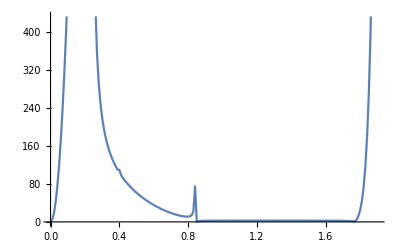

```mathematica
Λ[0,0.001,1,0,-0,0]
```

```mathematica
VLD[a_,b_]:= ({{0, 0, 0, 0, 0, 0, 0}, {a, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {b, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {a, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})
```

```mathematica
VDL[a_,b_]:= ConjugateTranspose[VLD[a,b]]
```

```mathematica
J1[ω_,δ_,t_,ϵ_,ϵ2_]:=Inverse[(ω+ⅈ*0.001-02)IdentityMatrix[7]]
```

```mathematica
GS[ω_,δ_,t_,ϵ_,ϵ2_,a_,b_]:= Inverse[IdentityMatrix[7]-J1[ω,δ,t,ϵ,ϵ2].VDL[a,b].SR[ω,δ,1,0].VLD[a,b]].J1[ω,δ,t,ϵ,ϵ2]
```

```mathematica
I2l[ω_,δ_,t_,ϵ_,ϵ2_,a_,b_]:= Inverse[IdentityMatrix[7]-GS[ω,δ,t,ϵ,ϵ2,a,b].VDL[a,b].SR[ω,δ,1,0].VLD[a,b]].GS[ω,δ,t,ϵ,ϵ2,a,b]
```

```mathematica
SELFENERGY[ω_,δ_,a_,b_]:= VDL[a,b].SR[ω,δ,1,0].VLD[a,b]
```

```mathematica
ΓL[ω_,δ_,a_,b_]:= ⅈ*(SELFENERGY[ω,δ,a,b]-ConjugateTranspose[SELFENERGY[ω,δ,a,b]])
```

```mathematica
Transmission[ω_,δ_,t_,ϵ_,ϵ2_,a_,b_]:= Abs[Tr[ΓL[ω,δ,a,b]*Conjugate[I2l[ω,δ,t,ϵ,ϵ2,a,b]]*ΓL[ω,δ,a,b]*I2l[ω,δ,t,ϵ,ϵ2,a,b]]]
```

```mathematica
Trans[a_,b_]:=Join[Table[{ω,Transmission[ω,0.001,1,0,0,a,b]},{ω,Range[0,0.41,0.01]}],Table[{ω,2Transmission[ω,0.001,1,0,0,a,b]},{ω,Range[0.42,0.84,0.01]}],Table[{ω,3Transmission[ω,0.001,1,0,0,a,b]},{ω,Range[.85,1.76,0.01]}]]
```

```mathematica
f2[a_,b_]:=Module[{B1=Transpose[{final[[1;;150]][[;;,1]],(Trans[a,b][[1;;150,2]]- final[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.49}]/150]
```

```mathematica
σ3[b_]:=Table[{b,a,f2[b,a]},{a,Range[-1,1,0.05]}]
```

```mathematica
σσ=Join[σ3[-1],σ3[-9/10],σ3[-4/5],σ3[-7/10],σ3[-3/5],σ3[-1/2],σ3[-2/5],σ3[-3/10],σ3[-1/5],σ3[-1/10],σ3[0],σ3[1/10],σ3[1/5],σ3[3/10],σ3[2/5],σ3[1/2],σ3[3/5],σ3[7/10],σ3[4/5],σ3[9/10],σ3[1]]
```

{{-1,-1.,0.0127416},{-1,-0.95,0.01264},{-1,-0.9,0.0125041},{-1,-0.85,0.0123058},{-1,-0.8,0.0120345},{-1,-0.75,0.0116527},{-1,-0.7,0.0111371},{-1,-0.65,0.0104848},{-1,-0.6,0.00975195},{-1,-0.55,0.00889502},{-1,-0.5,0.00798348},{-1,-0.45,0.0070697},{-1,-0.4,0.00621143},{-1,-0.35,0.00545799},{-1,-0.3,0.00483944},{-1,-0.25,0.00436896},{-1,-0.2,0.00404851},{-1,-0.15,0.00387167},{-1,-0.1,0.00382487},{-1,-0.05,0.00388758},{-1,0.,0.0040305},{-1,0.05,0.00421212},{-1,0.1,0.00437813},{-1,0.15,0.00446867},{-1,0.2,0.00443355},{-1,0.25,0.00424847},{-1,0.3,0.00392309},{-1,0.35,0.00349657},{-1,0.4,0.00302396},{-1,0.45,0.00256069},{-1,0.5,0.00215119},{-1,0.55,0.00182374},{-1,0.6,0.00159053},{-1,0.65,0.00145087},{-1,0.7,0.00139547},{-1,0.75,0.0014104},{-1,0.8,0.0014802},{-1,0.85,0.00158988},{-1,0.9,0.00172614},{-1,0.95,0.0018778},{-1,1.,0.00203594},{-9/10,-1.,0.0128824},{-9/10,-0.95,0.0128353},{-9/10,-0.9,0.0127644},{-9/10,-0.85,0.0126612},{-9/10,-0.8,0.0125448},{-9/10,-0.75,0.0122943},{-9/10,-0.7,0.011985},{-9/10,-0.65,0.0115456},{-9/10,-0.6,0.0109425},{-9/10,-0.55,0.0101872},{-9/10,-0.5,0.00932701},{-9/10,-0.45,0.00833714},{-9/10,-0.4,0.0073076},{-9/10,-0.35,0.00630584},{-9/10,-0.3,0.00540256},{-9/10,-0.25,0.00464886},{-9/10,-0.2,0.00407284},{-9/10,-0.15,0.0036868},{-9/10,-0.1,0.00349188},{-9/10,-0.05,0.00347833},{-9/10,0.,0.00362303},{-9/10,0.05,0.00388376},{-9/10,0.1,0.00419355},{-9/10,0.15,0.00446428},{-9/10,0.2,0.00460596},{-9/10,0.25,0.0045557},{-9/10,0.3,0.00429993},{-9/10,0.35,0.00387613},{-9/10,0.4,0.00335504},{-9/10,0.45,0.00281541},{-9/10,0.5,0.00232332},{-9/10,0.55,0.00192189},{-9/10,0.6,0.00163042},{-9/10,0.65,0.00144924},{-9/10,0.7,0.00136647},{-9/10,0.75,0.00136413},{-9/10,0.8,0.00142268},{-9/10,0.85,0.00152381},{-9/10,0.9,0.0016518},{-9/10,0.95,0.00179399},{-9/10,1.,0.00194069},{-4/5,-1.,0.0130197},{-4/5,-0.95,0.0130004},{-4/5,-0.9,0.0129716},{-4/5,-0.85,0.0129354},{-4/5,-0.8,0.0128766},{-4/5,-0.75,0.0127732},{-4/5,-0.7,0.0126157},{-4/5,-0.65,0.0123818},{-4/5,-0.6,0.0120357},{-4/5,-0.55,0.0115309},{-4/5,-0.5,0.0108286},{-4/5,-0.45,0.00994771},{-4/5,-0.4,0.00892215},{-4/5,-0.35,0.00777084},{-4/5,-0.3,0.0065929},{-4/5,-0.25,0.00547888},{-4/5,-0.2,0.00451072},{-4/5,-0.15,0.0037432},{-4/5,-0.1,0.00320974},{-4/5,-0.05,0.00293044},{-4/5,0.,0.00291132},{-4/5,0.05,0.00313545},{-4/5,0.1,0.00354809},{-4/5,0.15,0.00404574},{-4/5,0.2,0.00448727},{-4/5,0.25,0.00473497},{-4/5,0.3,0.00470578},{-4/5,0.35,0.00439976},{-4/5,0.4,0.00388962},{-4/5,0.45,0.00328357},{-4/5,0.5,0.00268569},{-4/5,0.55,0.00217089},{-4/5,0.6,0.00177787},{-4/5,0.65,0.00151478},{-4/5,0.7,0.00136974},{-4/5,0.75,0.001321},{-4/5,0.8,0.00134426},{-4/5,0.85,0.00141698},{-4/5,0.9,0.00152026},{-4/5,0.95,0.00163941},{-4/5,1.,0.00176356},{-7/10,-1.,0.0130986},{-7/10,-0.95,0.0131373},{-7/10,-0.9,0.0131705},{-7/10,-0.85,0.0131977},{-7/10,-0.8,0.0132159},{-7/10,-0.75,0.013212},{-7/10,-0.7,0.0131818},{-7/10,-0.65,0.0131102},{-7/10,-0.6,0.0129761},{-7/10,-0.55,0.0127485},{-7/10,-0.5,0.0123838},{-7/10,-0.45,0.0118231},{-7/10,-0.4,0.011038},{-7/10,-0.35,0.00999478},{-7/10,-0.3,0.00877341},{-7/10,-0.25,0.00741808},{-7/10,-0.2,0.00604097},{-7/10,-0.15,0.00475567},{-7/10,-0.1,0.00365616},{-7/10,-0.05,0.00281072},{-7/10,0.,0.00227536},{-7/10,0.05,0.00209598},{-7/10,0.1,0.00229053},{-7/10,0.15,0.00281552},{-7/10,0.2,0.0035378},{-7/10,0.25,0.00424829},{-7/10,0.3,0.00473078},{-7/10,0.35,0.00484826},{-7/10,0.4,0.0045898},{-7/10,0.45,0.00405397},{-7/10,0.5,0.00338983},{-7/10,0.55,0.0027354},{-7/10,0.6,0.00218217},{-7/10,0.65,0.0017699},{-7/10,0.7,0.00149957},{-7/10,0.75,0.00135065},{-7/10,0.8,0.00129489},{-7/10,0.85,0.00130454},{-7/10,0.9,0.00135616},{-7/10,0.95,0.00143166},{-7/10,1.,0.0015179},{-3/5,-1.,0.0131786},{-3/5,-0.95,0.0132789},{-3/5,-0.9,0.0133851},{-3/5,-0.85,0.0134768},{-3/5,-0.8,0.0136105},{-3/5,-0.75,0.0137213},{-3/5,-0.7,0.0138292},{-3/5,-0.65,0.0139287},{-3/5,-0.6,0.0139912},{-3/5,-0.55,0.0140167},{-3/5,-0.5,0.0139905},{-3/5,-0.45,0.0138199},{-3/5,-0.4,0.0135041},{-3/5,-0.35,0.0129378},{-3/5,-0.3,0.0121028},{-3/5,-0.25,0.0109255},{-3/5,-0.2,0.00950987},{-3/5,-0.15,0.007919},{-3/5,-0.1,0.00628003},{-3/5,-0.05,0.00472285},{-3/5,0.,0.00335473},{-3/5,0.05,0.00227165},{-3/5,0.1,0.00157629},{-3/5,0.15,0.00136368},{-3/5,0.2,0.0016692},{-3/5,0.25,0.00240655},{-3/5,0.3,0.00335282},{-3/5,0.35,0.00421315},{-3/5,0.4,0.0047318},{-3/5,0.45,0.00478768},{-3/5,0.5,0.00442552},{-3/5,0.55,0.00380733},{-3/5,0.6,0.00311966},{-3/5,0.65,0.00249996},{-3/5,0.7,0.0020146},{-3/5,0.75,0.00167438},{-3/5,0.8,0.00146013},{-3/5,0.85,0.00134251},{-3/5,0.9,0.00129289},{-3/5,0.95,0.00128774},{-3/5,1.,0.00130939},{-1/2,-1.,0.0131477},{-1/2,-0.95,0.013351},{-1/2,-0.9,0.0135699},{-1/2,-0.85,0.0138071},{-1/2,-0.8,0.0140634},{-1/2,-0.75,0.0143547},{-1/2,-0.7,0.0146288},{-1/2,-0.65,0.0149399},{-1/2,-0.6,0.0152533},{-1/2,-0.55,0.0155603},{-1/2,-0.5,0.015847},{-1/2,-0.45,0.0160918},{-1/2,-0.4,0.0162566},{-1/2,-0.35,0.0162968},{-1/2,-0.3,0.0161436},{-1/2,-0.25,0.0157013},{-1/2,-0.2,0.0148941},{-1/2,-0.15,0.0136925},{-1/2,-0.1,0.0121477},{-1/2,-0.05,0.010346},{-1/2,0.,0.00842248},{-1/2,0.05,0.00650992},{-1/2,0.1,0.00472114},{-1/2,0.15,0.00317788},{-1/2,0.2,0.00203013},{-1/2,0.25,0.00142214},{-1/2,0.3,0.00141913},{-1/2,0.35,0.00195242},{-1/2,0.4,0.00282348},{-1/2,0.45,0.00374929},{-1/2,0.5,0.00443377},{-1/2,0.55,0.0046756},{-1/2,0.6,0.00446145},{-1/2,0.65,0.00394543},{-1/2,0.7,0.0033281},{-1/2,0.75,0.00275478},{-1/2,0.8,0.00229165},{-1/2,0.85,0.00194915},{-1/2,0.9,0.00171118},{-1/2,0.95,0.00155409},{-1/2,1.,0.0014556},{-2/5,-1.,0.0127582},{-2/5,-0.95,0.0131488},{-2/5,-0.9,0.0135665},{-2/5,-0.85,0.014015},{-2/5,-0.8,0.0144829},{-2/5,-0.75,0.0149921},{-2/5,-0.7,0.0155472},{-2/5,-0.65,0.0161398},{-2/5,-0.6,0.0167617},{-2/5,-0.55,0.0174022},{-2/5,-0.5,0.0180475},{-2/5,-0.45,0.0186784},{-2/5,-0.4,0.0192698},{-2/5,-0.35,0.0197959},{-2/5,-0.3,0.0202179},{-2/5,-0.25,0.0204855},{-2/5,-0.2,0.0205236},{-2/5,-0.15,0.0202333},{-2/5,-0.1,0.0194983},{-2/5,-0.05,0.018314},{-2/5,0.,0.0167029},{-2/5,0.05,0.014744},{-2/5,0.1,0.0125776},{-2/5,0.15,0.0103283},{-2/5,0.2,0.00809765},{-2/5,0.25,0.00600172},{-2/5,0.3,0.00419488},{-2/5,0.35,0.00284006},{-2/5,0.4,0.00205557},{-2/5,0.45,0.00188301},{-2/5,0.5,0.00227029},{-2/5,0.55,0.00304135},{-2/5,0.6,0.00389069},{-2/5,0.65,0.00448878},{-2/5,0.7,0.0046619},{-2/5,0.75,0.00445884},{-2/5,0.8,0.00404603},{-2/5,0.85,0.00357763},{-2/5,0.9,0.00314442},{-2/5,0.95,0.00278242},{-2/5,1.,0.00249641},{-3/10,-1.,0.0112828},{-3/10,-0.95,0.0120558},{-3/10,-0.9,0.0128427},{-3/10,-0.85,0.0136537},{-3/10,-0.8,0.0144989},{-3/10,-0.75,0.0153894},{-3/10,-0.7,0.0163246},{-3/10,-0.65,0.0172981},{-3/10,-0.6,0.0182971},{-3/10,-0.55,0.0193042},{-3/10,-0.5,0.0202936},{-3/10,-0.45,0.0212409},{-3/10,-0.4,0.0221257},{-3/10,-0.35,0.0229262},{-3/10,-0.3,0.0236234},{-3/10,-0.25,0.0241954},{-3/10,-0.2,0.0246315},{-3/10,-0.15,0.0248763},{-3/10,-0.1,0.0248945},{-3/10,-0.05,0.0245973},{-3/10,0.,0.023873},{-3/10,0.05,0.0226572},{-3/10,0.1,0.0210254},{-3/10,0.15,0.0189867},{-3/10,0.2,0.0166822},{-3/10,0.25,0.0142167},{-3/10,0.3,0.0116682},{-3/10,0.35,0.00911874},{-3/10,0.4,0.00669768},{-3/10,0.45,0.00458388},{-3/10,0.5,0.00297404},{-3/10,0.55,0.00203602},{-3/10,0.6,0.00184571},{-3/10,0.65,0.00231296},{-3/10,0.7,0.00315643},{-3/10,0.75,0.00400553},{-3/10,0.8,0.00458586},{-3/10,0.85,0.00482004},{-3/10,0.9,0.00477766},{-3/10,0.95,0.00457236},{-3/10,1.,0.00429828},{-1/5,-1.,0.00812466},{-1/5,-0.95,0.00915168},{-1/5,-0.9,0.0103391},{-1/5,-0.85,0.0116548},{-1/5,-0.8,0.0131285},{-1/5,-0.75,0.01468},{-1/5,-0.7,0.0162534},{-1/5,-0.65,0.0178143},{-1/5,-0.6,0.0193318},{-1/5,-0.55,0.0207708},{-1/5,-0.5,0.0220994},{-1/5,-0.45,0.0232842},{-1/5,-0.4,0.0243142},{-1/5,-0.35,0.025184},{-1/5,-0.3,0.0258849},{-1/5,-0.25,0.026431},{-1/5,-0.2,0.0268395},{-1/5,-0.15,0.0271211},{-1/5,-0.1,0.0272876},{-1/5,-0.05,0.0273308},{-1/5,0.,0.0272098},{-1/5,0.05,0.0268709},{-1/5,0.1,0.0262103},{-1/5,0.15,0.0251143},{-1/5,0.2,0.0235879},{-1/5,0.25,0.0216375},{-1/5,0.3,0.0193255},{-1/5,0.35,0.016738},{-1/5,0.4,0.0139498},{-1/5,0.45,0.0110442},{-1/5,0.5,0.00815965},{-1/5,0.55,0.00551188},{-1/5,0.6,0.00336355},{-1/5,0.65,0.00194724},{-1/5,0.7,0.00136971},{-1/5,0.75,0.00154487},{-1/5,0.8,0.00221178},{-1/5,0.85,0.00304689},{-1/5,0.9,0.00379572},{-1/5,0.95,0.00433438},{-1/5,1.,0.00464868},{-1/10,-1.,0.00443073},{-1/10,-0.95,0.00514759},{-1/10,-0.9,0.00618716},{-1/10,-0.85,0.00759048},{-1/10,-0.8,0.00936248},{-1/10,-0.75,0.0114616},{-1/10,-0.7,0.0137933},{-1/10,-0.65,0.016204},{-1/10,-0.6,0.0186045},{-1/10,-0.55,0.0208087},{-1/10,-0.5,0.0226871},{-1/10,-0.45,0.0242339},{-1/10,-0.4,0.0254531},{-1/10,-0.35,0.0263489},{-1/10,-0.3,0.0269897},{-1/10,-0.25,0.0274204},{-1/10,-0.2,0.0276912},{-1/10,-0.15,0.0278474},{-1/10,-0.1,0.0279352},{-1/10,-0.05,0.027973},{-1/10,0.,0.0279721},{-1/10,0.05,0.0279319},{-1/10,0.1,0.027805},{-1/10,0.15,0.0275408},{-1/10,0.2,0.0270395},{-1/10,0.25,0.0261694},{-1/10,0.3,0.0248376},{-1/10,0.35,0.0229778},{-1/10,0.4,0.0206459},{-1/10,0.45,0.0179001},{-1/10,0.5,0.0148634},{-1/10,0.55,0.0117013},{-1/10,0.6,0.00862273},{-1/10,0.65,0.00586922},{-1/10,0.7,0.00367482},{-1/10,0.75,0.00219845},{-1/10,0.8,0.00146696},{-1/10,0.85,0.00136736},{-1/10,0.9,0.00169666},{-1/10,0.95,0.00223815},{-1/10,1.,0.00282111},{0,-1.,0.00229245},{0,-0.95,0.00229683},{0,-0.9,0.00259929},{0,-0.85,0.00332574},{0,-0.8,0.00458076},{0,-0.75,0.00641316},{0,-0.7,0.00878975},{0,-0.65,0.0115883},{0,-0.6,0.0146139},{0,-0.55,0.017638},{0,-0.5,0.0204231},{0,-0.45,0.0228226},{0,-0.4,0.0247305},{0,-0.35,0.0260949},{0,-0.3,0.0269899},{0,-0.25,0.0275308},{0,-0.2,0.027823},{0,-0.15,0.0279596},{0,-0.1,0.0280102},{0,-0.05,0.0280218},{0,0.,0.0280002},{0,0.05,0.0280218},{0,0.1,0.0280102},{0,0.15,0.0279596},{0,0.2,0.027823},{0,0.25,0.0275308},{0,0.3,0.0269899},{0,0.35,0.0260949},{0,0.4,0.0247305},{0,0.45,0.0228226},{0,0.5,0.0204231},{0,0.55,0.017638},{0,0.6,0.0146139},{0,0.65,0.0115883},{0,0.7,0.00878975},{0,0.75,0.00641316},{0,0.8,0.00458076},{0,0.85,0.00332574},{0,0.9,0.00259929},{0,0.95,0.00229683},{0,1.,0.00229245},{1/10,-1.,0.00282111},{1/10,-0.95,0.00223815},{1/10,-0.9,0.00169666},{1/10,-0.85,0.00136736},{1/10,-0.8,0.00146696},{1/10,-0.75,0.00219845},{1/10,-0.7,0.00367482},{1/10,-0.65,0.00586922},{1/10,-0.6,0.00862273},{1/10,-0.55,0.0117013},{1/10,-0.5,0.0148634},{1/10,-0.45,0.0179001},{1/10,-0.4,0.0206459},{1/10,-0.35,0.0229778},{1/10,-0.3,0.0248376},{1/10,-0.25,0.0261694},{1/10,-0.2,0.0270395},{1/10,-0.15,0.0275408},{1/10,-0.1,0.027805},{1/10,-0.05,0.0279319},{1/10,0.,0.0279721},{1/10,0.05,0.027973},{1/10,0.1,0.0279352},{1/10,0.15,0.0278474},{1/10,0.2,0.0276912},{1/10,0.25,0.0274204},{1/10,0.3,0.0269897},{1/10,0.35,0.0263489},{1/10,0.4,0.0254531},{1/10,0.45,0.0242339},{1/10,0.5,0.0226871},{1/10,0.55,0.0208087},{1/10,0.6,0.0186045},{1/10,0.65,0.016204},{1/10,0.7,0.0137933},{1/10,0.75,0.0114616},{1/10,0.8,0.00936248},{1/10,0.85,0.00759048},{1/10,0.9,0.00618716},{1/10,0.95,0.00514759},{1/10,1.,0.00443073},{1/5,-1.,0.00464868},{1/5,-0.95,0.00433438},{1/5,-0.9,0.00379572},{1/5,-0.85,0.00304689},{1/5,-0.8,0.00221178},{1/5,-0.75,0.00154487},{1/5,-0.7,0.00136971},{1/5,-0.65,0.00194724},{1/5,-0.6,0.00336355},{1/5,-0.55,0.00551188},{1/5,-0.5,0.00815965},{1/5,-0.45,0.0110442},{1/5,-0.4,0.0139498},{1/5,-0.35,0.016738},{1/5,-0.3,0.0193255},{1/5,-0.25,0.0216375},{1/5,-0.2,0.0235879},{1/5,-0.15,0.0251143},{1/5,-0.1,0.0262103},{1/5,-0.05,0.0268709},{1/5,0.,0.0272098},{1/5,0.05,0.0273308},{1/5,0.1,0.0272876},{1/5,0.15,0.0271211},{1/5,0.2,0.0268395},{1/5,0.25,0.026431},{1/5,0.3,0.0258849},{1/5,0.35,0.025184},{1/5,0.4,0.0243142},{1/5,0.45,0.0232842},{1/5,0.5,0.0220994},{1/5,0.55,0.0207708},{1/5,0.6,0.0193318},{1/5,0.65,0.0178143},{1/5,0.7,0.0162534},{1/5,0.75,0.01468},{1/5,0.8,0.0131285},{1/5,0.85,0.0116548},{1/5,0.9,0.0103391},{1/5,0.95,0.00915168},{1/5,1.,0.00812466},{3/10,-1.,0.00429828},{3/10,-0.95,0.00457236},{3/10,-0.9,0.00477766},{3/10,-0.85,0.00482004},{3/10,-0.8,0.00458586},{3/10,-0.75,0.00400553},{3/10,-0.7,0.00315643},{3/10,-0.65,0.00231296},{3/10,-0.6,0.00184571},{3/10,-0.55,0.00203602},{3/10,-0.5,0.00297404},{3/10,-0.45,0.00458388},{3/10,-0.4,0.00669768},{3/10,-0.35,0.00911874},{3/10,-0.3,0.0116682},{3/10,-0.25,0.0142167},{3/10,-0.2,0.0166822},{3/10,-0.15,0.0189867},{3/10,-0.1,0.0210254},{3/10,-0.05,0.0226572},{3/10,0.,0.023873},{3/10,0.05,0.0245973},{3/10,0.1,0.0248945},{3/10,0.15,0.0248763},{3/10,0.2,0.0246315},{3/10,0.25,0.0241954},{3/10,0.3,0.0236234},{3/10,0.35,0.0229262},{3/10,0.4,0.0221257},{3/10,0.45,0.0212409},{3/10,0.5,0.0202936},{3/10,0.55,0.0193042},{3/10,0.6,0.0182971},{3/10,0.65,0.0172981},{3/10,0.7,0.0163246},{3/10,0.75,0.0153894},{3/10,0.8,0.0144989},{3/10,0.85,0.0136537},{3/10,0.9,0.0128427},{3/10,0.95,0.0120558},{3/10,1.,0.0112828},{2/5,-1.,0.00249641},{2/5,-0.95,0.00278242},{2/5,-0.9,0.00314442},{2/5,-0.85,0.00357763},{2/5,-0.8,0.00404603},{2/5,-0.75,0.00445884},{2/5,-0.7,0.0046619},{2/5,-0.65,0.00448878},{2/5,-0.6,0.00389069},{2/5,-0.55,0.00304135},{2/5,-0.5,0.00227029},{2/5,-0.45,0.00188301},{2/5,-0.4,0.00205557},{2/5,-0.35,0.00284006},{2/5,-0.3,0.00419488},{2/5,-0.25,0.00600172},{2/5,-0.2,0.00809765},{2/5,-0.15,0.0103283},{2/5,-0.1,0.0125776},{2/5,-0.05,0.014744},{2/5,0.,0.0167029},{2/5,0.05,0.018314},{2/5,0.1,0.0194983},{2/5,0.15,0.0202333},{2/5,0.2,0.0205236},{2/5,0.25,0.0204855},{2/5,0.3,0.0202179},{2/5,0.35,0.0197959},{2/5,0.4,0.0192698},{2/5,0.45,0.0186784},{2/5,0.5,0.0180475},{2/5,0.55,0.0174022},{2/5,0.6,0.0167617},{2/5,0.65,0.0161398},{2/5,0.7,0.0155472},{2/5,0.75,0.0149921},{2/5,0.8,0.0144829},{2/5,0.85,0.014015},{2/5,0.9,0.0135665},{2/5,0.95,0.0131488},{2/5,1.,0.0127582},{1/2,-1.,0.0014556},{1/2,-0.95,0.00155409},{1/2,-0.9,0.00171118},{1/2,-0.85,0.00194915},{1/2,-0.8,0.00229165},{1/2,-0.75,0.00275478},{1/2,-0.7,0.0033281},{1/2,-0.65,0.00394543},{1/2,-0.6,0.00446145},{1/2,-0.55,0.0046756},{1/2,-0.5,0.00443377},{1/2,-0.45,0.00374929},{1/2,-0.4,0.00282348},{1/2,-0.35,0.00195242},{1/2,-0.3,0.00141913},{1/2,-0.25,0.00142214},{1/2,-0.2,0.00203013},{1/2,-0.15,0.00317788},{1/2,-0.1,0.00472114},{1/2,-0.05,0.00650992},{1/2,0.,0.00842248},{1/2,0.05,0.010346},{1/2,0.1,0.0121477},{1/2,0.15,0.0136925},{1/2,0.2,0.0148941},{1/2,0.25,0.0157013},{1/2,0.3,0.0161436},{1/2,0.35,0.0162968},{1/2,0.4,0.0162566},{1/2,0.45,0.0160918},{1/2,0.5,0.015847},{1/2,0.55,0.0155603},{1/2,0.6,0.0152533},{1/2,0.65,0.0149399},{1/2,0.7,0.0146288},{1/2,0.75,0.0143547},{1/2,0.8,0.0140634},{1/2,0.85,0.0138071},{1/2,0.9,0.0135699},{1/2,0.95,0.013351},{1/2,1.,0.0131477},{3/5,-1.,0.00130939},{3/5,-0.95,0.00128774},{3/5,-0.9,0.00129289},{3/5,-0.85,0.00134251},{3/5,-0.8,0.00146013},{3/5,-0.75,0.00167438},{3/5,-0.7,0.0020146},{3/5,-0.65,0.00249996},{3/5,-0.6,0.00311966},{3/5,-0.55,0.00380733},{3/5,-0.5,0.00442552},{3/5,-0.45,0.00478768},{3/5,-0.4,0.0047318},{3/5,-0.35,0.00421315},{3/5,-0.3,0.00335282},{3/5,-0.25,0.00240655},{3/5,-0.2,0.0016692},{3/5,-0.15,0.00136368},{3/5,-0.1,0.00157629},{3/5,-0.05,0.00227165},{3/5,0.,0.00335473},{3/5,0.05,0.00472285},{3/5,0.1,0.00628003},{3/5,0.15,0.007919},{3/5,0.2,0.00950987},{3/5,0.25,0.0109255},{3/5,0.3,0.0121028},{3/5,0.35,0.0129378},{3/5,0.4,0.0135041},{3/5,0.45,0.0138199},{3/5,0.5,0.0139905},{3/5,0.55,0.0140167},{3/5,0.6,0.0139912},{3/5,0.65,0.0139287},{3/5,0.7,0.0138292},{3/5,0.75,0.0137213},{3/5,0.8,0.0136105},{3/5,0.85,0.0134768},{3/5,0.9,0.0133851},{3/5,0.95,0.0132789},{3/5,1.,0.0131786},{7/10,-1.,0.0015179},{7/10,-0.95,0.00143166},{7/10,-0.9,0.00135616},{7/10,-0.85,0.00130454},{7/10,-0.8,0.00129489},{7/10,-0.75,0.00135065},{7/10,-0.7,0.00149957},{7/10,-0.65,0.0017699},{7/10,-0.6,0.00218217},{7/10,-0.55,0.0027354},{7/10,-0.5,0.00338983},{7/10,-0.45,0.00405397},{7/10,-0.4,0.0045898},{7/10,-0.35,0.00484826},{7/10,-0.3,0.00473078},{7/10,-0.25,0.00424829},{7/10,-0.2,0.0035378},{7/10,-0.15,0.00281552},{7/10,-0.1,0.00229053},{7/10,-0.05,0.00209598},{7/10,0.,0.00227536},{7/10,0.05,0.00281072},{7/10,0.1,0.00365616},{7/10,0.15,0.00475567},{7/10,0.2,0.00604097},{7/10,0.25,0.00741808},{7/10,0.3,0.00877341},{7/10,0.35,0.00999478},{7/10,0.4,0.011038},{7/10,0.45,0.0118231},{7/10,0.5,0.0123838},{7/10,0.55,0.0127485},{7/10,0.6,0.0129761},{7/10,0.65,0.0131102},{7/10,0.7,0.0131818},{7/10,0.75,0.013212},{7/10,0.8,0.0132159},{7/10,0.85,0.0131977},{7/10,0.9,0.0131705},{7/10,0.95,0.0131373},{7/10,1.,0.0130986},{4/5,-1.,0.00176356},{4/5,-0.95,0.00163941},{4/5,-0.9,0.00152026},{4/5,-0.85,0.00141698},{4/5,-0.8,0.00134426},{4/5,-0.75,0.001321},{4/5,-0.7,0.00136974},{4/5,-0.65,0.00151478},{4/5,-0.6,0.00177787},{4/5,-0.55,0.00217089},{4/5,-0.5,0.00268569},{4/5,-0.45,0.00328357},{4/5,-0.4,0.00388962},{4/5,-0.35,0.00439976},{4/5,-0.3,0.00470578},{4/5,-0.25,0.00473497},{4/5,-0.2,0.00448727},{4/5,-0.15,0.00404574},{4/5,-0.1,0.00354809},{4/5,-0.05,0.00313545},{4/5,0.,0.00291132},{4/5,0.05,0.00293044},{4/5,0.1,0.00320974},{4/5,0.15,0.0037432},{4/5,0.2,0.00451072},{4/5,0.25,0.00547888},{4/5,0.3,0.0065929},{4/5,0.35,0.00777084},{4/5,0.4,0.00892215},{4/5,0.45,0.00994771},{4/5,0.5,0.0108286},{4/5,0.55,0.0115309},{4/5,0.6,0.0120357},{4/5,0.65,0.0123818},{4/5,0.7,0.0126157},{4/5,0.75,0.0127732},{4/5,0.8,0.0128766},{4/5,0.85,0.0129354},{4/5,0.9,0.0129716},{4/5,0.95,0.0130004},{4/5,1.,0.0130197},{9/10,-1.,0.00194069},{9/10,-0.95,0.00179399},{9/10,-0.9,0.0016518},{9/10,-0.85,0.00152381},{9/10,-0.8,0.00142268},{9/10,-0.75,0.00136413},{9/10,-0.7,0.00136647},{9/10,-0.65,0.00144924},{9/10,-0.6,0.00163042},{9/10,-0.55,0.00192189},{9/10,-0.5,0.00232332},{9/10,-0.45,0.00281541},{9/10,-0.4,0.00335504},{9/10,-0.35,0.00387613},{9/10,-0.3,0.00429993},{9/10,-0.25,0.0045557},{9/10,-0.2,0.00460596},{9/10,-0.15,0.00446428},{9/10,-0.1,0.00419355},{9/10,-0.05,0.00388376},{9/10,0.,0.00362303},{9/10,0.05,0.00347833},{9/10,0.1,0.00349188},{9/10,0.15,0.0036868},{9/10,0.2,0.00407284},{9/10,0.25,0.00464886},{9/10,0.3,0.00540256},{9/10,0.35,0.00630584},{9/10,0.4,0.0073076},{9/10,0.45,0.00833714},{9/10,0.5,0.00932701},{9/10,0.55,0.0101872},{9/10,0.6,0.0109425},{9/10,0.65,0.0115456},{9/10,0.7,0.011985},{9/10,0.75,0.0122943},{9/10,0.8,0.0125448},{9/10,0.85,0.0126612},{9/10,0.9,0.0127644},{9/10,0.95,0.0128353},{9/10,1.,0.0128824},{1,-1.,0.00203594},{1,-0.95,0.0018778},{1,-0.9,0.00172614},{1,-0.85,0.00158988},{1,-0.8,0.0014802},{1,-0.75,0.0014104},{1,-0.7,0.00139547},{1,-0.65,0.00145087},{1,-0.6,0.00159053},{1,-0.55,0.00182374},{1,-0.5,0.00215119},{1,-0.45,0.00256069},{1,-0.4,0.00302396},{1,-0.35,0.00349657},{1,-0.3,0.00392309},{1,-0.25,0.00424847},{1,-0.2,0.00443355},{1,-0.15,0.00446867},{1,-0.1,0.00437813},{1,-0.05,0.00421212},{1,0.,0.0040305},{1,0.05,0.00388758},{1,0.1,0.00382487},{1,0.15,0.00387167},{1,0.2,0.00404851},{1,0.25,0.00436896},{1,0.3,0.00483944},{1,0.35,0.00545799},{1,0.4,0.00621143},{1,0.45,0.0070697},{1,0.5,0.00798348},{1,0.55,0.00889502},{1,0.6,0.00975195},{1,0.65,0.0104848},{1,0.7,0.0111371},{1,0.75,0.0116527},{1,0.8,0.0120345},{1,0.85,0.0123058},{1,0.9,0.0125041},{1,0.95,0.01264},{1,1.,0.0127416}}

```mathematica
{Min/@Transpose[σσ]}[[1,3]]
```

0.00128774

```mathematica
Extract[Transpose[σσ],{{1,Position[Transpose[σσ],{Min/@Transpose[σσ]}[[1,3]]][[1,2]]},{2,Position[Transpose[σσ],{Min/@Transpose[σσ]}[[1,3]]][[1,2]]}}]
```

{3/5,-0.95}

```mathematica
Table[{i,η[0,1,i]},{i,Range[1,7,1]}]
```

{{1,0.394399},{2,0.409564},{3,0.411526},{4,0.408953},{5,0.411526},{6,0.409564},{7,0.394399}}

```mathematica
AvgE[ϵ1_,n_]:=AvgE[ϵ1,n]=n(2η[0,ϵ1,3]+2η[0,ϵ1,1]+2η[0,ϵ1,2]+η[0,ϵ1,4])/7
```

```mathematica
AvgE[1,3]
```

1.21711

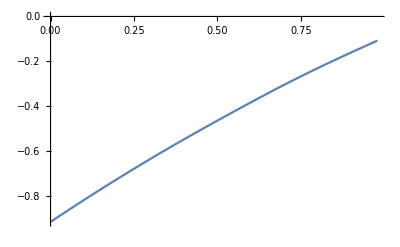

```mathematica
ListLinePlot[Table[{x,(2η[0,x,2]+η[0,.7,4]-AvgE[1,3])},{x,Range[0.0,0.985,0.01]}]]
```

```mathematica
Minimize[2η[0,x,2]+η[0,y,4]-AvgE[1,3],{x,y}]
```

{-9.09905,{x→-1.09873×10^17,y→-7.0964×10^16}}

```mathematica
Reduce[2η[0,x,2]+η[0,y,4]-AvgE[1,3]==0.002,{x,y}]
```

-Graphics3D-

```mathematica
μ
```

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];
```

```mathematica
imp1[ω_,ϵ1_,μ1_]:=imp1[ω,ϵ1,μ1]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2[ω_,ϵ1_,μ2_]:=imp2[ω,ϵ1,μ2]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3[ω_,ϵ1_,μ3_]:=imp3[ω,ϵ1,μ3]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4[ω_,ϵ1_,μ4_]:=imp4[ω,ϵ1,μ4]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5[ω_,ϵ1_,μ5_]:=imp5[ω,ϵ1,μ5]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp6[ω_,ϵ1_,μ6_]:=imp6[ω,ϵ1,μ6]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7[ω_,ϵ1_,μ7_]:=imp7[ω,ϵ1,μ7]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8[ω_,ϵ1_,μ8_]:=imp8[ω,ϵ1,μ8]= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-0]]];ψ[ω_,ϵ1_,μ1_,μ2_,μ3_,μ4_,μ5_,μ6_,μ7_,μ8_]:=ψ[ω,ϵ1,μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,ϵ1,μ1].T1[1].SL[ω,0.001,1,0].T1[1]].imp1[ω,ϵ1,μ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,ϵ1,μ2].T2[1].Sl11.T2[1]].imp2[ω,ϵ1,μ2];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,ϵ1,μ3].T1[1].Sl12.T1[1]].imp3[ω,ϵ1,μ3];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,ϵ1,μ4].T2[1].Sl13.T2[1]].imp4[ω,ϵ1,μ4];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,ϵ1,μ5].T1[1].Sl14.T1[1]].imp5[ω,ϵ1,μ5];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,ϵ1,μ6].T2[1].Sl15.T2[1]].imp6[ω,ϵ1,μ6];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,ϵ1,μ7].T1[1].Sl16.T1[1]].imp7[ω,ϵ1,μ7];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,ϵ1,μ8].T2[1].Sl17.T2[1]].imp8[ω,ϵ1,μ8];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ρ[μ1_,μ4_,μ7_]:=Show[ListLinePlot[Table[{ω,ψ[ω,1,μ1,1,1,μ4,1,1,μ7,1]},{ω,Range[0,4,0.01]}],PlotStyle->Red],%17]
```

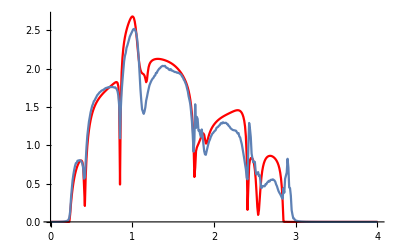

```mathematica
ρ[1,4,7]
```

```mathematica
ρ[1,2,3][[1;;400,2]]
```

{0.0000204215,0.0000247486,0.0000271408,0.0000279786,0.0000275098,0.0000258921,0.0000232184,0.0000195327,0.0000148395,9.10896×10^-6,2.27888×10^-6,5.7455×10^-6,0.0000150944,0.0000259382,0.0000384957,0.0000530442,0.0000699335,0.0000896005,0.000112573,0.000139414,0.000170383,0.000203618,0.000222507,0.0000168783,0.0400473,0.107766,0.175725,0.244216,0.312655,0.380204,0.445947,0.508974,0.568428,0.623517,0.67349,0.717549,0.754666,0.7832,0.799991,0.797863,0.756376,0.578609,0.332642,0.481038,0.584102,0.663009,0.72725,0.781806,0.829634,0.87263,0.912072,0.948855,0.98362,1.01684,1.04885,1.07992,1.11023,1.13994,1.16913,1.1979,1.22628,1.25432,1.28204,1.30945,1.33656,1.36336,1.38985,1.41601,1.44184,1.46731,1.49239,1.51706,1.54126,1.5649,1.58787,1.60999,1.63097,1.6504,1.66756,1.68132,1.68971,1.68906,1.67193,1.62046,1.47537,1.11976,1.35816,1.4978,1.60441,1.69663,1.78228,1.86534,1.94802,2.03142,2.11586,2.201,2.28589,2.369,2.44822,2.52069,2.58221,2.62574,2.63839,2.59853,2.4828,2.29853,2.10741,1.96988,1.89123,1.84723,1.81657,1.78713,1.75212,1.70574,1.63837,1.52725,1.31665,0.972781,0.947569,1.24774,1.43016,1.52696,1.59089,1.64033,1.68014,1.71153,1.73537,1.7528,1.76511,1.7735,1.779,1.78244,1.78444,1.78548,1.78593,1.78604,1.78603,1.78605,1.78621,1.78661,1.78731,1.78839,1.78988,1.79184,1.79429,1.79728,1.80083,1.80498,1.80975,1.81517,1.82124,1.82798,1.83536,1.84333,1.85181,1.86063,1.86956,1.87827,1.88624,1.89283,1.89714,1.89804,1.89412,1.8837,1.86482,1.83525,1.79251,1.73389,1.65629,1.55598,1.42796,1.26467,1.05315,0.768363,0.354136,0.348031,2.07949,3.96991,0.969186,0.155915,0.692106,1.00228,1.20771,1.35685,1.47169,1.56278,1.63434,1.68527,1.70714,1.67954,1.56794,1.3508,1.0969,0.945779,0.93208,0.990652,1.06666,1.13759,1.19775,1.24725,1.28769,1.32074,1.34773,1.36963,1.3871,1.40051,1.41007,1.41583,1.41776,1.41577,1.40978,1.39976,1.38573,1.36779,1.34614,1.32105,1.29282,1.26179,1.2283,1.19263,1.15499,1.11554,1.0743,1.03123,0.986162,0.938847,0.888922,0.835929,0.779304,0.718368,0.652315,0.58018,0.500797,0.412721,0.314098,0.20244,0.0741887,0.0761358,0.25783,0.488826,0.811425,1.37871,1.37903,1.05049,1.0001,1.21563,2.03025,2.31609,0.299125,0.0555372,0.100163,0.0931058,0.0703498,0.0351077,0.00988497,0.0304382,0.252398,0.293193,0.273655,0.255868,0.244348,0.237798,0.235019,0.235285,0.238216,0.243668,0.251662,0.262356,0.276026,0.293059,0.313943,0.339248,0.369555,0.405316,0.446531,0.492164,0.539155,0.581156,0.607738,0.60585,0.565059,0.484251,0.373002,0.24452,0.105598,0.0169036,0.026054,0.0469978,0.161025,2.47099,0.0348151,0.00340152,0.000648086,0.00248811,0.120423,0.0495007,0.00951166,0.00398991,0.00214362,0.00130002,0.000847575,0.000580062,0.000411149,0.000299306,0.000222531,0.000168308,0.000129119,0.000100246,0.0000786277,0.0000622138,0.0000496004,0.0000398043,0.0000321246,0.0000260538,0.0000212188,0.0000173421,0.0000142149,0.0000116782,9.61046×10^-6,7.9172×10^-6,6.52492×10^-6,5.37586×10^-6,4.42431×10^-6,3.63394×10^-6,2.97565×10^-6,2.42605×10^-6,1.96621×10^-6,1.58077×10^-6,1.2572×10^-6,9.85215×10^-7,7.5639×10^-7,5.63751×10^-7,4.01531×10^-7,2.64937×10^-7,1.49975×10^-7,5.33104×10^-8,2.78538×10^-8,9.58657×10^-8,1.52703×10^-7,2.00033×10^-7,2.39269×10^-7,2.71605×10^-7,2.98058×10^-7,3.19492×10^-7,3.36641×10^-7,3.50134×10^-7,3.60508×10^-7,3.68221×10^-7,3.73667×10^-7,3.77182×10^-7,3.79057×10^-7,3.79541×10^-7,3.78846×10^-7,3.77157×10^-7,3.74633×10^-7,3.71409×10^-7,3.67604×10^-7,3.63319×10^-7,3.5864×10^-7,3.53644×10^-7,3.48393×10^-7,3.42945×10^-7,3.37347×10^-7,3.31639×10^-7,3.25858×10^-7,3.20033×10^-7,3.14189×10^-7,3.08349×10^-7,3.02532×10^-7,2.96752×10^-7,2.91024×10^-7,2.85358×10^-7,2.79763×10^-7,2.74247×10^-7,2.68816×10^-7,2.63476×10^-7,2.58229×10^-7,2.53079×10^-7,2.48028×10^-7,2.43078×10^-7,2.38229×10^-7,2.33483×10^-7,2.28838×10^-7,2.24295×10^-7,2.19852×10^-7,2.1551×10^-7,2.11267×10^-7,2.07121×10^-7,2.03071×10^-7,1.99116×10^-7,1.95254×10^-7,1.91483×10^-7,1.87801×10^-7,1.84206×10^-7,1.80697×10^-7,1.77271×10^-7,1.73927×10^-7,1.70663×10^-7,1.67476×10^-7,1.64365×10^-7}

```mathematica
f2[μ1_,μ2_,μ3_]:=Module[{B1=Transpose[{final[[1;;400]][[;;,1]],(ρ[μ1,μ2,μ3][[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
```

```mathematica
f2[1,2,4]
```

0.0013656

```mathematica
FindMinimum
```

```mathematica
FindMinimum[{f2[μ1,2,3],μ1∈Integers},{μ1,Range[1,7,1]}]
```

FindMinimum::cvecv: Constrained optimization is only supported with scalar valued variables.

FindMinimum[{f2[μ1,2,3],μ1∈ℤ},{μ1,Range[1,7,1]}]

```mathematica
σ3[μ1_,μ2_]:=Table[{μ1,μ2,μ3,f2[μ1,μ2,μ3]},{μ3,Range[1,7,1]}]
```

```mathematica
σ[μ1_]:=Join[σ3[μ1,1],σ3[μ1,2],σ3[μ1,3],σ3[μ1,4],σ3[μ1,5],σ3[μ1,6],σ3[μ1,7]]
```

```mathematica
σ3[1,6]
```

{{1,6,1,0.000354063},{1,6,2,0.00201795},{1,6,3,0.00101826},{1,6,4,0.00109668},{1,6,5,0.000913359},{1,6,6,0.00119054},{1,6,7,0.000354063}}

```mathematica
Join[σ[1],σ[2],σ[3],σ[4],σ[5],σ[6],σ[7]]
```

{{1,1,1,0.000392846},{1,1,2,0.000815166},{1,1,3,0.00107447},{1,1,4,0.000772151},{1,1,5,0.000701818},{1,1,6,0.00122404},{1,1,7,0.000392846},{1,2,1,0.000850784},{1,2,2,0.00117172},{1,2,3,0.00107879},{1,2,4,0.0013656},{1,2,5,0.00283822},{1,2,6,0.00175676},{1,2,7,0.000850784},{1,3,1,0.000541433},{1,3,2,0.00162733},{1,3,3,0.00123266},{1,3,4,0.00145549},{1,3,5,0.000762419},{1,3,6,0.000872254},{1,3,7,0.000541433},{1,4,1,0.000392846},{1,4,2,0.000815166},{1,4,3,0.00107447},{1,4,4,0.000772151},{1,4,5,0.000701818},{1,4,6,0.00122404},{1,4,7,0.000392846},{1,5,1,0.000510987},{1,5,2,0.00137524},{1,5,3,0.00115689},{1,5,4,0.00120691},{1,5,5,0.000942103},{1,5,6,0.00182336},{1,5,7,0.000510987},{1,6,1,0.000354063},{1,6,2,0.00201795},{1,6,3,0.00101826},{1,6,4,0.00109668},{1,6,5,0.000913359},{1,6,6,0.00119054},{1,6,7,0.000354063},{1,7,1,0.000895484},{1,7,2,0.00283354},{1,7,3,0.00370112},{1,7,4,0.00147339},{1,7,5,0.00276567},{1,7,6,0.00152585},{1,7,7,0.000895484},{2,1,1,0.000910125},{2,1,2,0.00117467},{2,1,3,0.00108259},{2,1,4,0.000900327},{2,1,5,0.000948233},{2,1,6,0.00698755},{2,1,7,0.000910125},{2,2,1,0.00134788},{2,2,2,0.00141507},{2,2,3,0.00135991},{2,2,4,0.00142607},{2,2,5,0.00100001},{2,2,6,0.0069518},{2,2,7,0.00134788},{2,3,1,0.000619573},{2,3,2,0.00180236},{2,3,3,0.000859765},{2,3,4,0.00133986},{2,3,5,0.00109914},{2,3,6,0.0012001},{2,3,7,0.000619573},{2,4,1,0.000910125},{2,4,2,0.00117467},{2,4,3,0.00108259},{2,4,4,0.000900327},{2,4,5,0.000948233},{2,4,6,0.00698755},{2,4,7,0.000910125},{2,5,1,0.000803256},{2,5,2,0.00224454},{2,5,3,0.00110177},{2,5,4,0.00118949},{2,5,5,0.000888092},{2,5,6,0.00870452},{2,5,7,0.000803256},{2,6,1,0.000601335},{2,6,2,0.00194894},{2,6,3,0.00103666},{2,6,4,0.00133115},{2,6,5,0.00111669},{2,6,6,0.00164257},{2,6,7,0.000601335},{2,7,1,0.00100252},{2,7,2,0.00351087},{2,7,3,0.00136013},{2,7,4,0.00141935},{2,7,5,0.0010036},{2,7,6,0.00200327},{2,7,7,0.00100252},{3,1,1,0.000853612},{3,1,2,0.00213174},{3,1,3,0.00540629},{3,1,4,0.00107325},{3,1,5,0.00461065},{3,1,6,0.0020256},{3,1,7,0.000853612},{3,2,1,0.000666403},{3,2,2,0.00163673},{3,2,3,0.00231055},{3,2,4,0.00153761},{3,2,5,0.000811231},{3,2,6,0.00113333},{3,2,7,0.000666403},{3,3,1,0.00123749},{3,3,2,0.00181569},{3,3,3,0.00243254},{3,3,4,0.00156727},{3,3,5,0.00183912},{3,3,6,0.0009595},{3,3,7,0.00123749},{3,4,1,0.000853612},{3,4,2,0.00213174},{3,4,3,0.00540629},{3,4,4,0.00107325},{3,4,5,0.00461065},{3,4,6,0.0020256},{3,4,7,0.000853612},{3,5,1,0.000959641},{3,5,2,0.00144122},{3,5,3,0.00182338},{3,5,4,0.00156406},{3,5,5,0.00134725},{3,5,6,0.0014463},{3,5,7,0.000959641},{3,6,1,0.000517629},{3,6,2,0.0013799},{3,6,3,0.00154137},{3,6,4,0.00135588},{3,6,5,0.00112919},{3,6,6,0.00125155},{3,6,7,0.000517629},{3,7,1,0.000791579},{3,7,2,0.00447272},{3,7,3,0.00410979},{3,7,4,0.00140298},{3,7,5,0.00289394},{3,7,6,0.00245243},{3,7,7,0.000791579},{4,1,1,0.000712927},{4,1,2,0.00179087},{4,1,3,0.00146108},{4,1,4,0.00134999},{4,1,5,0.00127289},{4,1,6,0.00165106},{4,1,7,0.000712927},{4,2,1,0.000771713},{4,2,2,0.00161154},{4,2,3,0.00130281},{4,2,4,0.0018106},{4,2,5,0.00109148},{4,2,6,0.00157407},{4,2,7,0.000771713},{4,3,1,0.000753623},{4,3,2,0.00219691},{4,3,3,0.000911296},{4,3,4,0.00161198},{4,3,5,0.00113069},{4,3,6,0.000892112},{4,3,7,0.000753623},{4,4,1,0.000712927},{4,4,2,0.00179087},{4,4,3,0.00146108},{4,4,4,0.00134999},{4,4,5,0.00127289},{4,4,6,0.00165106},{4,4,7,0.000712927},{4,5,1,0.000907802},{4,5,2,0.00185254},{4,5,3,0.00208055},{4,5,4,0.00167012},{4,5,5,0.00140379},{4,5,6,0.00148133},{4,5,7,0.000907802},{4,6,1,0.000779355},{4,6,2,0.00190347},{4,6,3,0.00170243},{4,6,4,0.00189602},{4,6,5,0.00130123},{4,6,6,0.00137471},{4,6,7,0.000779355},{4,7,1,0.000848546},{4,7,2,0.00255057},{4,7,3,0.00214671},{4,7,4,0.0017742},{4,7,5,0.00132147},{4,7,6,0.00171423},{4,7,7,0.000848546},{5,1,1,0.00085362},{5,1,2,0.00150044},{5,1,3,0.00157304},{5,1,4,0.00123332},{5,1,5,0.0012615},{5,1,6,0.00144626},{5,1,7,0.00085362},{5,2,1,0.000851331},{5,2,2,0.00138694},{5,2,3,0.00165991},{5,2,4,0.00151626},{5,2,5,0.00102483},{5,2,6,0.00193257},{5,2,7,0.000851331},{5,3,1,0.000812256},{5,3,2,0.0023214},{5,3,3,0.00133079},{5,3,4,0.00148993},{5,3,5,0.00134664},{5,3,6,0.00104923},{5,3,7,0.000812256},{5,4,1,0.00085362},{5,4,2,0.00150044},{5,4,3,0.00157304},{5,4,4,0.00123332},{5,4,5,0.0012615},{5,4,6,0.00144626},{5,4,7,0.00085362},{5,5,1,0.00126324},{5,5,2,0.0021479},{5,5,3,0.00146874},{5,5,4,0.00158757},{5,5,5,0.00195975},{5,5,6,0.00242273},{5,5,7,0.00126324},{5,6,1,0.00081947},{5,6,2,0.00155092},{5,6,3,0.00188444},{5,6,4,0.00164369},{5,6,5,0.00242149},{5,6,6,0.00155828},{5,6,7,0.00081947},{5,7,1,0.00102565},{5,7,2,0.00284141},{5,7,3,0.00205109},{5,7,4,0.00184751},{5,7,5,0.00178337},{5,7,6,0.00347609},{5,7,7,0.00102565},{6,1,1,0.000538039},{6,1,2,0.00118894},{6,1,3,0.00123439},{6,1,4,0.00101423},{6,1,5,0.00107366},{6,1,6,0.000629623},{6,1,7,0.000538039},{6,2,1,0.000590263},{6,2,2,0.00153821},{6,2,3,0.00106679},{6,2,4,0.0015529},{6,2,5,0.000830652},{6,2,6,0.00292542},{6,2,7,0.000590263},{6,3,1,0.000393289},{6,3,2,0.00163047},{6,3,3,0.00133366},{6,3,4,0.00211806},{6,3,5,0.00212418},{6,3,6,0.000898221},{6,3,7,0.000393289},{6,4,1,0.000538039},{6,4,2,0.00118894},{6,4,3,0.00123439},{6,4,4,0.00101423},{6,4,5,0.00107366},{6,4,6,0.000629623},{6,4,7,0.000538039},{6,5,1,0.000687169},{6,5,2,0.00188995},{6,5,3,0.00106551},{6,5,4,0.00156086},{6,5,5,0.00108266},{6,5,6,0.00125806},{6,5,7,0.000687169},{6,6,1,0.000754284},{6,6,2,0.00163739},{6,6,3,0.00121869},{6,6,4,0.00169744},{6,6,5,0.00126648},{6,6,6,0.00147663},{6,6,7,0.000754284},{6,7,1,0.000866466},{6,7,2,0.00213755},{6,7,3,0.00156479},{6,7,4,0.00145513},{6,7,5,0.0012729},{6,7,6,0.00179484},{6,7,7,0.000866466},{7,1,1,0.0010952},{7,1,2,0.00156475},{7,1,3,0.00115696},{7,1,4,0.0015928},{7,1,5,0.00119173},{7,1,6,0.00135381},{7,1,7,0.0010952},{7,2,1,0.0011085},{7,2,2,0.00160438},{7,2,3,0.00139738},{7,2,4,0.00226937},{7,2,5,0.00289159},{7,2,6,0.00195514},{7,2,7,0.0011085},{7,3,1,0.000735412},{7,3,2,0.00193683},{7,3,3,0.0058247},{7,3,4,0.00225291},{7,3,5,0.00231128},{7,3,6,0.00129947},{7,3,7,0.000735412},{7,4,1,0.0010952},{7,4,2,0.00156475},{7,4,3,0.00115696},{7,4,4,0.0015928},{7,4,5,0.00119173},{7,4,6,0.00135381},{7,4,7,0.0010952},{7,5,1,0.00108466},{7,5,2,0.00268657},{7,5,3,0.0014986},{7,5,4,0.00210086},{7,5,5,0.00119805},{7,5,6,0.00279662},{7,5,7,0.00108466},{7,6,1,0.000929442},{7,6,2,0.00180882},{7,6,3,0.00149987},{7,6,4,0.00218129},{7,6,5,0.00164814},{7,6,6,0.001541},{7,6,7,0.000929442},{7,7,1,0.001437},{7,7,2,0.00277267},{7,7,3,0.00228505},{7,7,4,0.00196645},{7,7,5,0.00205307},{7,7,6,0.00218029},{7,7,7,0.001437}}

```mathematica
{Min/@Transpose[%74]}[[1,4]]
```

0.000354063

```mathematica
Position[Transpose[%74],{Min/@Transpose[%74]}[[1,4]]]
```

{{4,36},{4,42}}

```mathematica
Extract[Transpose[%74],{{1,Position[Transpose[%74],{Min/@Transpose[%74]}[[1,4]]][[1,2]]},{2,Position[Transpose[%74],{Min/@Transpose[%74]}[[1,4]]][[1,2]]}}]
```

{1,6}

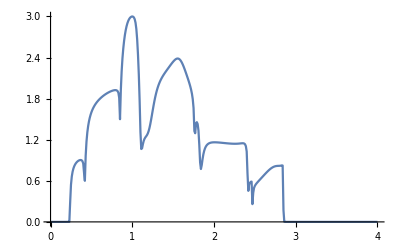

-Graphics-

```mathematica
Show[ListPlot[final,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[m1,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[o3,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}],0]],ListPlot[p4,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}],0]],ListPlot[q5,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}],0]],ListPlot[r6,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}],0]],ListPlot[n7,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}],0]],PlotRange->All]
```

```mathematica
{{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{2,1.69397},{3,1.79373},{4,1.83786},{5,1.81472},{6,1.57072},{7,1.68097},{8,1.82039},{9,1.63217},{10,1.84849},{11,1.66792},{12,1.86955},{13,1.62685},{14,1.87771},{15,1.79733},{16,1.87794},{17,1.93303},{18,1.74617},{19,1.80864},{20,1.78566},{21,1.3264},{22,1.50936},{23,1.90586},{24,1.73501},{25,1.83065},{26,1.69607},{27,1.77749},{28,1.51377},{29,1.60929},{30,1.70991},{31,1.62026},{32,1.47382},{33,1.77811},{34,1.72429},{35,1.77027},{36,1.75668},{37,1.7064},{38,1.59738},{39,1.71699},{40,1.80567},{41,1.78072},{42,1.81253},{43,1.74123},{44,1.72166},{45,1.70743},{46,1.60561},{47,1.75819},{48,1.79558}}

```mathematica
{Max[{Min/@%212}],Min[{Min/@%212}],final[[51,2]]}
```

{1.93303,1.3264,1.73011}

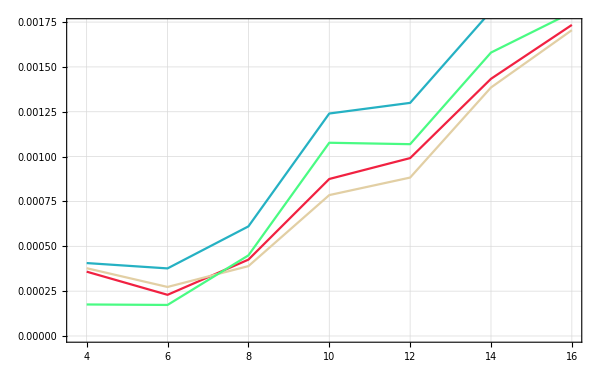

```mathematica
Show[ListLinePlot[{{4,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]]
```

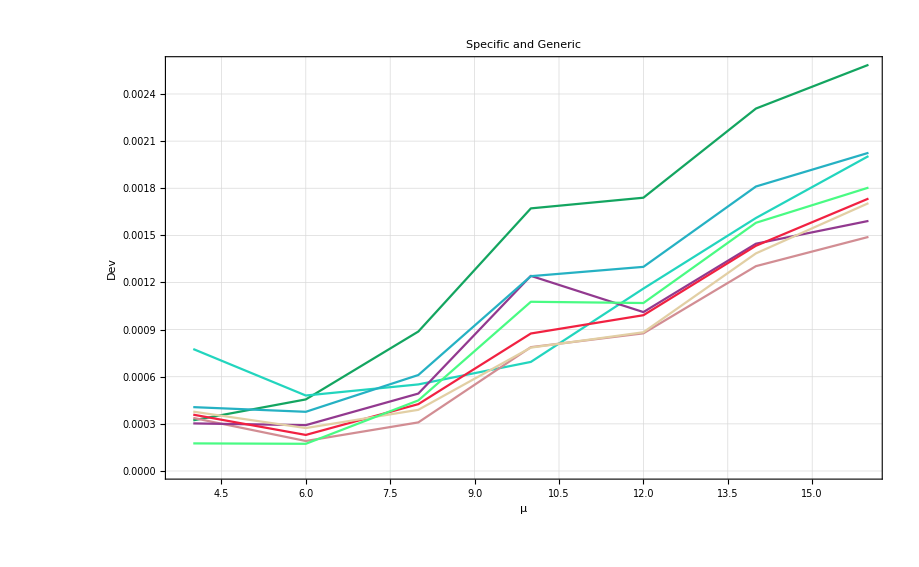

```mathematica
Show[%388,%543]
```

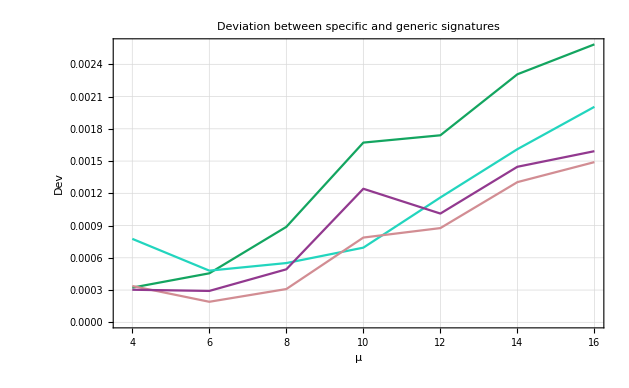

```mathematica
Show[%387,AxesLabel->{HoldForm[μ],HoldForm[Dev]},PlotLabel->HoldForm[Deviation between specific and generic signatures],LabelStyle->{GrayLevel[0]}]
```

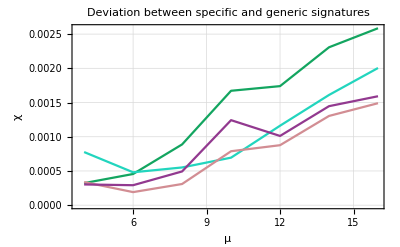

```mathematica
Show[%698,AxesLabel->{None,None},FrameLabel->{{HoldForm[χ],None},{HoldForm[μ],None}},PlotLabel->HoldForm[Deviation between specific and generic signatures]]
```

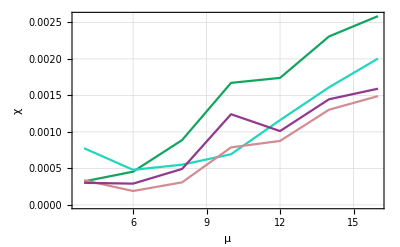

```mathematica
Show[%698,AxesLabel->{None,None},FrameLabel->{{HoldForm[χ],None},{HoldForm[μ],None}},PlotLabel->None]
```

```mathematica
Show[%380,%379]
```

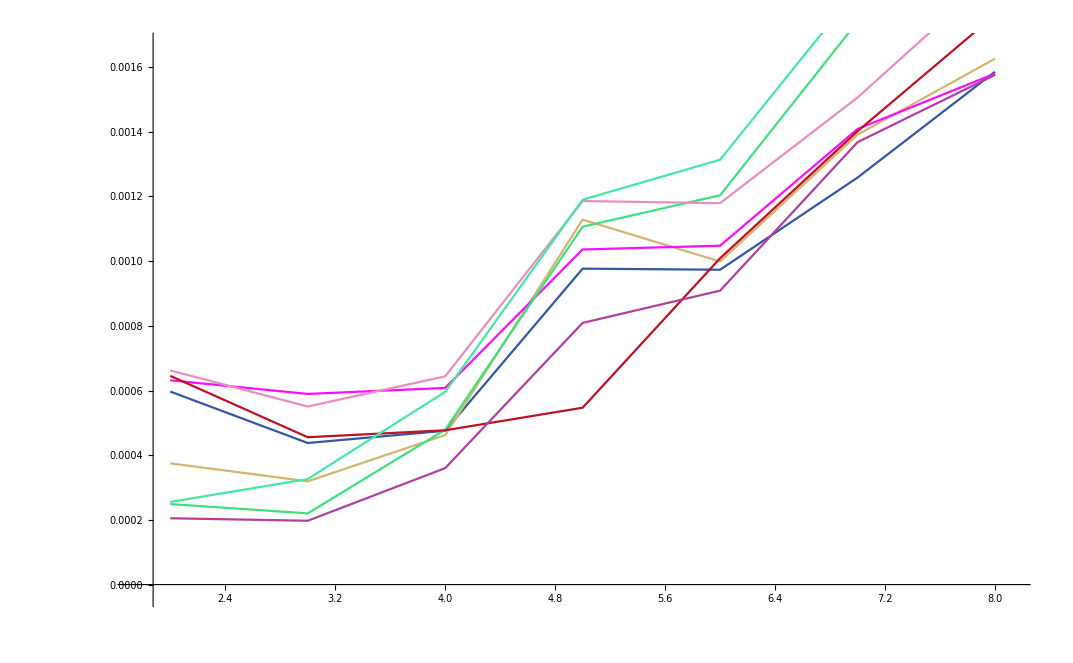

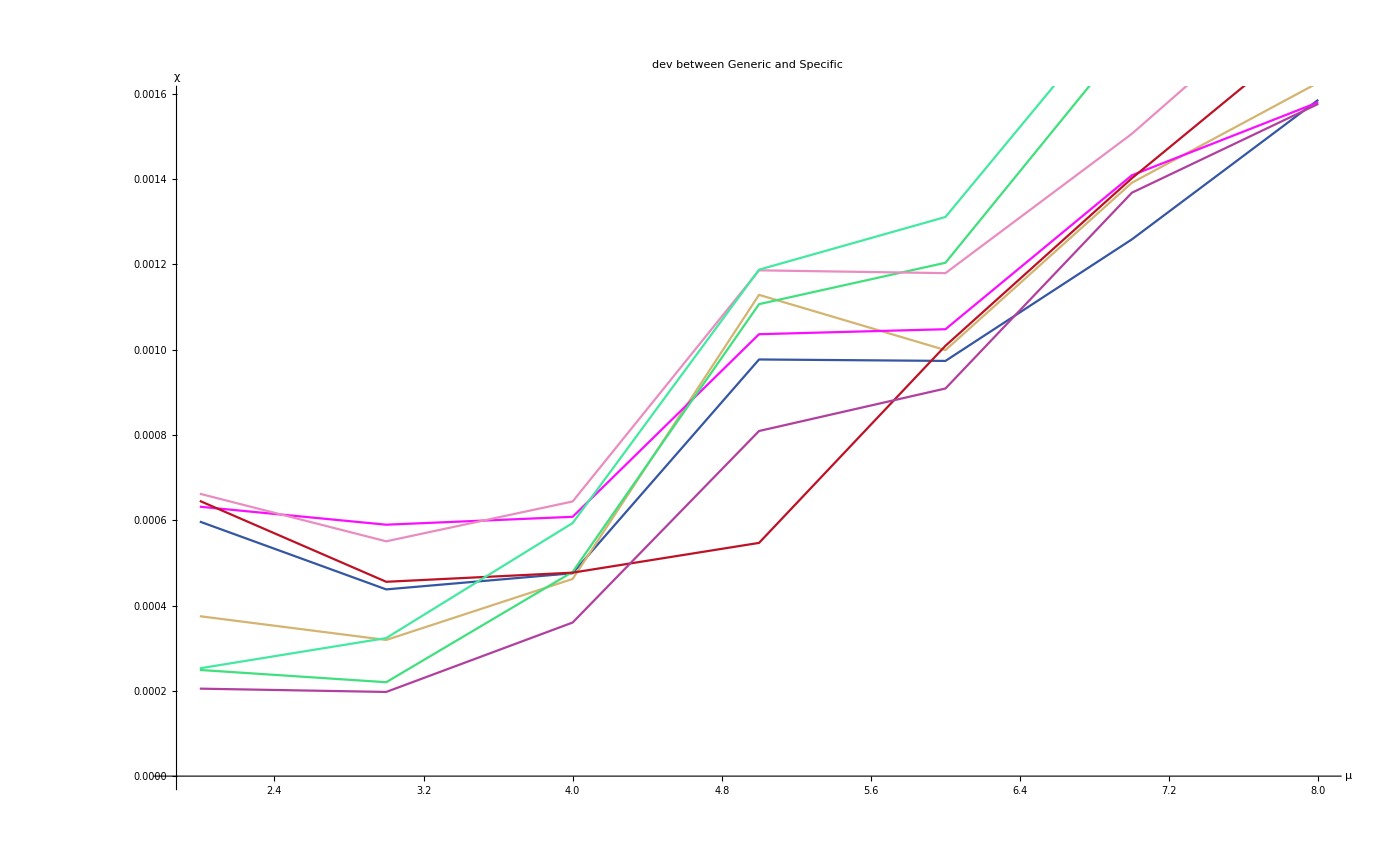

```mathematica
Show[%381,AxesLabel->{HoldForm[μ],HoldForm[χ]},PlotLabel->HoldForm[dev between Generic and Specific],LabelStyle->{GrayLevel[0]}]
```

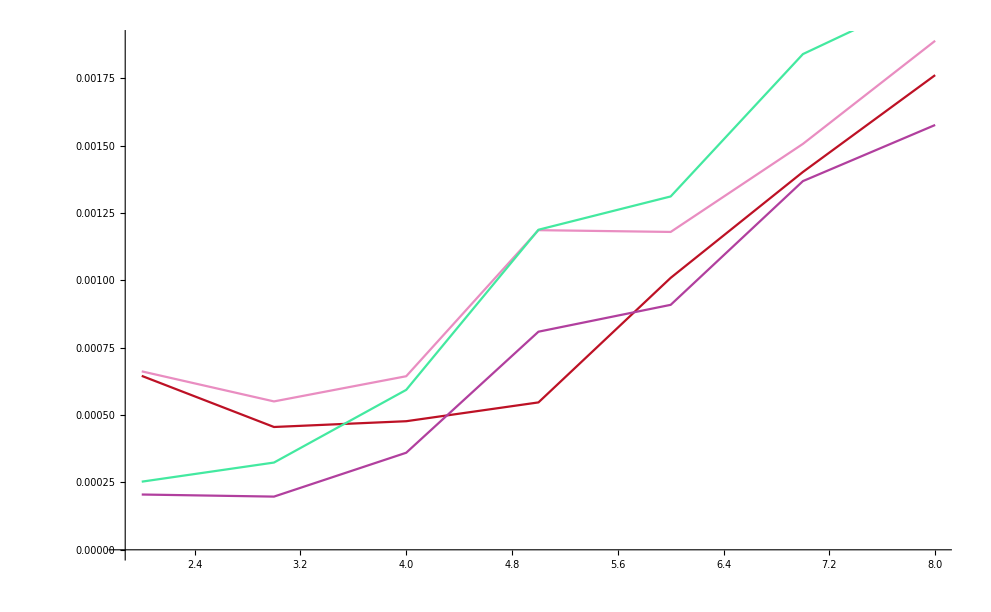

-Graphics-